
-Graphics-
Previous notebook		Content		Next notebook

## Square root of multivector

Version (2018-10-31)  The notebook run time is about x min on 2008 year laptop.

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GAC_Base.nb"}]]
```

### Sqrt of MV for n=3

Cl(3,0) and Cl(1,2) requires substitution(1/2) (-s^2+S^2)==T, whereas Cl(2,1) and Cl(0,3) requires (1/2) (s^2+S^2)==T. Otherwise parasite solutions will appear.

#### Cl(3,0)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Base vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

General case cl(3,0): s =!= S and (s=!=0 || S=!=0)

In this case v and V can be solved and there are no special relation between equations for s and S (they are independent)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300

```mathematica
eqs12[testAlgebra]=Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{1,2}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0]
```

{-b[1]+2 s v[1]-2 S V[1]==0,-b[2]+2 s v[2]-2 S V[2]==0,-b[3]+2 s v[3]-2 S V[3]==0,-b[4]+2 S v[3]+2 s V[3]==0,-b[5]-2 S v[2]-2 s V[2]==0,-b[6]+2 S v[1]+2 s V[1]==0}

```mathematica
coeffv1[testAlgebra]=Cases[v1,_v,Infinity];coeffV1[testAlgebra]=Cases[V1,_V,Infinity];
solvV[testAlgebra]=Flatten[Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]]]]
```

{v[1]→-(-s b[1]-S b[6])/(2 (s^2+S^2)),v[2]→-(-s b[2]+S b[5])/(2 (s^2+S^2)),v[3]→-(-s b[3]-S b[4])/(2 (s^2+S^2)),V[1]→-(S b[1]-s b[6])/(2 (s^2+S^2)),V[2]→-(S b[2]+s b[5])/(2 (s^2+S^2)),V[3]→-(S b[3]-s b[4])/(2 (s^2+S^2))}

```mathematica
solvVToProgram[testAlgebra]=Simplify/@(Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,Method->Reduce][[1]])
```

{v[1]→(s b[1]+S b[6])/(2 (s^2+S^2)),v[2]→(s b[2]-S b[5])/(2 (s^2+S^2)),v[3]→(s b[3]+S b[4])/(2 (s^2+S^2)),V[1]→(-S b[1]+s b[6])/(2 (s^2+S^2)),V[2]→-(S b[2]+s b[5])/(2 (s^2+S^2)),V[3]→(-S b[3]+s b[4])/(2 (s^2+S^2))}

```mathematica
solsvVReals[testAlgebra]=Simplify/@Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{v[1]→ConditionalExpression[b[6]/(2 S),s==0&&S≠0],v[2]→ConditionalExpression[-b[5]/(2 S),s==0&&S≠0],v[3]→ConditionalExpression[b[4]/(2 S),s==0&&S≠0],V[1]→ConditionalExpression[-b[1]/(2 S),s==0&&S≠0],V[2]→ConditionalExpression[-b[2]/(2 S),s==0&&S≠0],V[3]→ConditionalExpression[-b[3]/(2 S),s==0&&S≠0]},{v[1]→ConditionalExpression[b[1]/(2 s),S==0&&s≠0],v[2]→ConditionalExpression[b[2]/(2 s),S==0&&s≠0],v[3]→ConditionalExpression[b[3]/(2 s),S==0&&s≠0],V[1]→ConditionalExpression[b[6]/(2 s),S==0&&s≠0],V[2]→ConditionalExpression[-b[5]/(2 s),S==0&&s≠0],V[3]→ConditionalExpression[b[4]/(2 s),S==0&&s≠0]},{v[1]→ConditionalExpression[(s b[1]+S b[6])/(2 (s^2+S^2)),s≠0&&S≠0],v[2]→ConditionalExpression[(s b[2]-S b[5])/(2 (s^2+S^2)),s≠0&&S≠0],v[3]→ConditionalExpression[(s b[3]+S b[4])/(2 (s^2+S^2)),s≠0&&S≠0],V[1]→ConditionalExpression[(-S b[1]+s b[6])/(2 (s^2+S^2)),s≠0&&S≠0],V[2]→ConditionalExpression[-(S b[2]+s b[5])/(2 (s^2+S^2)),s≠0&&S≠0],V[3]→ConditionalExpression[(-S b[3]+s b[4])/(2 (s^2+S^2)),s≠0&&S≠0]}}

```mathematica
(solsvVReals[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s==0->zeroQ[s],S≠0->nonzeroQ[S],S==0->zeroQ[S],s≠0->nonzeroQ[s]})})//InputForm
```

{{v[1] -> ConditionalExpression[takeMe[b[6]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  v[2] -> ConditionalExpression[takeMe[-b[5]/(2*S)], 
    zeroQ[s] && nonzeroQ[S]], v[3] -> ConditionalExpression[
    takeMe[b[4]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[1] -> ConditionalExpression[takeMe[-b[1]/(2*S)], 
    zeroQ[s] && nonzeroQ[S]], V[2] -> ConditionalExpression[
    takeMe[-b[2]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[3] -> ConditionalExpression[takeMe[-b[3]/(2*S)], 
    zeroQ[s] && nonzeroQ[S]]}, 
 {v[1] -> ConditionalExpression[takeMe[b[1]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[2] -> ConditionalExpression[takeMe[b[2]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[3] -> ConditionalExpression[takeMe[b[3]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[1] -> ConditionalExpression[takeMe[b[6]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[2] -> ConditionalExpression[takeMe[-b[5]/(2*s)], 
    zeroQ[S] && nonzeroQ[s]], V[3] -> ConditionalExpression[
    takeMe[b[4]/(2*s)], zeroQ[S] && nonzeroQ[s]]}, 
 {v[1] -> ConditionalExpression[takeMe[(s*b[1] + S*b[6])/(2*(s^2 + S^2))], 
    nonzeroQ[s] && nonzeroQ[S]], v[2] -> ConditionalExpression[
    takeMe[(s*b[2] - S*b[5])/(2*(s^2 + S^2))], nonzeroQ[s] && nonzeroQ[S]], 
  v[3] -> ConditionalExpression[takeMe[(s*b[3] + S*b[4])/(2*(s^2 + S^2))], 
    nonzeroQ[s] && nonzeroQ[S]], V[1] -> ConditionalExpression[
    takeMe[(-(S*b[1]) + s*b[6])/(2*(s^2 + S^2))], 
    nonzeroQ[s] && nonzeroQ[S]], V[2] -> ConditionalExpression[
    takeMe[-(S*b[2] + s*b[5])/(2*(s^2 + S^2))], nonzeroQ[s] && nonzeroQ[S]], 
  V[3] -> ConditionalExpression[takeMe[(-(S*b[3]) + s*b[4])/(2*(s^2 + S^2))], 
    nonzeroQ[s] && nonzeroQ[S]]}}

```mathematica
solvVToProgram[testAlgebra]=Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,Method->Reduce,MaxExtraConditions->All]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{v[1]→ConditionalExpression[((s b[1])/S+b[6])/(2 S),(s==0&&S>0)||(s==0&&S<0)],v[2]→ConditionalExpression[-(-(s b[2])/S+b[5])/(2 S),(s==0&&S>0)||(s==0&&S<0)],v[3]→ConditionalExpression[((s b[3])/S+b[4])/(2 S),(s==0&&S>0)||(s==0&&S<0)],V[1]→ConditionalExpression[-b[1]/(2 S),(s==0&&S>0)||(s==0&&S<0)],V[2]→ConditionalExpression[-b[2]/(2 S),(s==0&&S>0)||(s==0&&S<0)],V[3]→ConditionalExpression[-b[3]/(2 S),(s==0&&S>0)||(s==0&&S<0)]},{v[1]→ConditionalExpression[(b[1]+(S b[6])/s)/(2 s),(S==0&&s>0)||(S==0&&s<0)],v[2]→ConditionalExpression[(b[2]-(S b[5])/s)/(2 s),(S==0&&s>0)||(S==0&&s<0)],v[3]→ConditionalExpression[b[3]/(2 s),(S==0&&s>0)||(S==0&&s<0)],V[1]→ConditionalExpression[b[6]/(2 s),(S==0&&s>0)||(S==0&&s<0)],V[2]→ConditionalExpression[-b[5]/(2 s),(S==0&&s>0)||(S==0&&s<0)],V[3]→ConditionalExpression[b[4]/(2 s),(S==0&&s>0)||(S==0&&s<0)]},{v[1]→ConditionalExpression[(b[1]+(2 S (-S b[1]+s b[6]))/(2 s^2+2 S^2))/(2 s),(s>0&&S>0)||(s>0&&S<0)||(s<0&&S>0)||(s<0&&S<0)],v[2]→ConditionalExpression[(b[2]+(2 S (-S b[2]-s b[5]))/(2 s^2+2 S^2))/(2 s),(s>0&&S>0)||(s>0&&S<0)||(s<0&&S>0)||(s<0&&S<0)],v[3]→ConditionalExpression[(b[4]-(2 s (-S b[3]+s b[4]))/(2 s^2+2 S^2))/(2 S),(s>0&&S>0)||(s>0&&S<0)||(s<0&&S>0)||(s<0&&S<0)],V[1]→ConditionalExpression[(-S b[1]+s b[6])/(2 s^2+2 S^2),(s>0&&S>0)||(s>0&&S<0)||(s<0&&S>0)||(s<0&&S<0)],V[2]→ConditionalExpression[(-S b[2]-s b[5])/(2 s^2+2 S^2),(s>0&&S>0)||(s>0&&S<0)||(s<0&&S>0)||(s<0&&S<0)],V[3]→ConditionalExpression[(-S b[3]+s b[4])/(2 s^2+2 S^2),(s>0&&S>0)||(s>0&&S<0)||(s<0&&S>0)||(s<0&&S<0)]}}

Pilnas sprendinys su Reduce

```mathematica
solvVToProgram[testAlgebra]=Reduce[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,Backsubstitution->True]
```

(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0)||(s<0&&S==0&&v[1]==b[1]/(2 s)&&v[2]==b[2]/(2 s)&&v[3]==b[3]/(2 s)&&V[1]==b[6]/(2 s)&&V[2]==-b[5]/(2 s)&&V[3]==b[4]/(2 s))||(s>0&&S==0&&v[1]==b[1]/(2 s)&&v[2]==b[2]/(2 s)&&v[3]==b[3]/(2 s)&&V[1]==b[6]/(2 s)&&V[2]==-b[5]/(2 s)&&V[3]==b[4]/(2 s))||(S<0&&s==0&&v[1]==b[6]/(2 S)&&v[2]==-b[5]/(2 S)&&v[3]==b[4]/(2 S)&&V[1]==-b[1]/(2 S)&&V[2]==-b[2]/(2 S)&&V[3]==-b[3]/(2 S))||(S>0&&s==0&&v[1]==b[6]/(2 S)&&v[2]==-b[5]/(2 S)&&v[3]==b[4]/(2 S)&&V[1]==-b[1]/(2 S)&&V[2]==-b[2]/(2 S)&&V[3]==-b[3]/(2 S))||(S<0&&s<0&&v[1]==(s b[1]+S b[6])/(2 (s^2+S^2))&&v[2]==(s b[2]-S b[5])/(2 (s^2+S^2))&&v[3]==(s b[3]+S b[4])/(2 (s^2+S^2))&&V[1]==(-S b[1]+s b[6])/(2 (s^2+S^2))&&V[2]==(-S b[2]-s b[5])/(2 (s^2+S^2))&&V[3]==(-S b[3]+s b[4])/(2 (s^2+S^2)))||(S<0&&s>0&&v[1]==(s b[1]+S b[6])/(2 (s^2+S^2))&&v[2]==(s b[2]-S b[5])/(2 (s^2+S^2))&&v[3]==(s b[3]+S b[4])/(2 (s^2+S^2))&&V[1]==(-S b[1]+s b[6])/(2 (s^2+S^2))&&V[2]==(-S b[2]-s b[5])/(2 (s^2+S^2))&&V[3]==(-S b[3]+s b[4])/(2 (s^2+S^2)))||(S>0&&s<0&&v[1]==(s b[1]+S b[6])/(2 (s^2+S^2))&&v[2]==(s b[2]-S b[5])/(2 (s^2+S^2))&&v[3]==(s b[3]+S b[4])/(2 (s^2+S^2))&&V[1]==(-S b[1]+s b[6])/(2 (s^2+S^2))&&V[2]==(-S b[2]-s b[5])/(2 (s^2+S^2))&&V[3]==(-S b[3]+s b[4])/(2 (s^2+S^2)))||(S>0&&s>0&&v[1]==(s b[1]+S b[6])/(2 (s^2+S^2))&&v[2]==(s b[2]-S b[5])/(2 (s^2+S^2))&&v[3]==(s b[3]+S b[4])/(2 (s^2+S^2))&&V[1]==(-S b[1]+s b[6])/(2 (s^2+S^2))&&V[2]==(-S b[2]-s b[5])/(2 (s^2+S^2))&&V[3]==(-S b[3]+s b[4])/(2 (s^2+S^2)))

```mathematica
solvVToProgram[testAlgebra]=FullSimplify/@Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,VerifySolutions->True,MaxExtraConditions->All]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{v[1]→ConditionalExpression[b[6]/(2 S),s==0&&S≠0],v[2]→ConditionalExpression[-b[5]/(2 S),s==0&&S≠0],v[3]→ConditionalExpression[b[4]/(2 S),s==0&&S≠0],V[1]→ConditionalExpression[-b[1]/(2 S),s==0&&S≠0],V[2]→ConditionalExpression[-b[2]/(2 S),s==0&&S≠0],V[3]→ConditionalExpression[-b[3]/(2 S),s==0&&S≠0]},{v[1]→ConditionalExpression[b[1]/(2 s),S==0&&s≠0],v[2]→ConditionalExpression[b[2]/(2 s),S==0&&s≠0],v[3]→ConditionalExpression[b[3]/(2 s),S==0&&s≠0],V[1]→ConditionalExpression[b[6]/(2 s),S==0&&s≠0],V[2]→ConditionalExpression[-b[5]/(2 s),S==0&&s≠0],V[3]→ConditionalExpression[b[4]/(2 s),S==0&&s≠0]},{v[1]→ConditionalExpression[(s b[1]+S b[6])/(2 (s^2+S^2)),s≠0&&S≠0],v[2]→ConditionalExpression[(s b[2]-S b[5])/(2 (s^2+S^2)),s≠0&&S≠0],v[3]→ConditionalExpression[(s b[3]+S b[4])/(2 (s^2+S^2)),s≠0&&S≠0],V[1]→ConditionalExpression[(-S b[1]+s b[6])/(2 (s^2+S^2)),s≠0&&S≠0],V[2]→ConditionalExpression[-(S b[2]+s b[5])/(2 (s^2+S^2)),s≠0&&S≠0],V[3]→ConditionalExpression[(-S b[3]+s b[4])/(2 (s^2+S^2)),s≠0&&S≠0]}}

```mathematica
(solvVToProgram[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{Sqrt[detb]->detSqrt})})//InputForm
```

{{v[1] -> ConditionalExpression[takeMe[b[6]/(2*S)], s == 0 && S != 0], 
  v[2] -> ConditionalExpression[takeMe[-b[5]/(2*S)], s == 0 && S != 0], 
  v[3] -> ConditionalExpression[takeMe[b[4]/(2*S)], s == 0 && S != 0], 
  V[1] -> ConditionalExpression[takeMe[-b[1]/(2*S)], s == 0 && S != 0], 
  V[2] -> ConditionalExpression[takeMe[-b[2]/(2*S)], s == 0 && S != 0], 
  V[3] -> ConditionalExpression[takeMe[-b[3]/(2*S)], s == 0 && S != 0]}, 
 {v[1] -> ConditionalExpression[takeMe[b[1]/(2*s)], S == 0 && s != 0], 
  v[2] -> ConditionalExpression[takeMe[b[2]/(2*s)], S == 0 && s != 0], 
  v[3] -> ConditionalExpression[takeMe[b[3]/(2*s)], S == 0 && s != 0], 
  V[1] -> ConditionalExpression[takeMe[b[6]/(2*s)], S == 0 && s != 0], 
  V[2] -> ConditionalExpression[takeMe[-b[5]/(2*s)], S == 0 && s != 0], 
  V[3] -> ConditionalExpression[takeMe[b[4]/(2*s)], S == 0 && s != 0]}, 
 {v[1] -> ConditionalExpression[takeMe[(s*b[1] + S*b[6])/(2*(s^2 + S^2))], 
    s != 0 && S != 0], v[2] -> ConditionalExpression[
    takeMe[(s*b[2] - S*b[5])/(2*(s^2 + S^2))], s != 0 && S != 0], 
  v[3] -> ConditionalExpression[takeMe[(s*b[3] + S*b[4])/(2*(s^2 + S^2))], 
    s != 0 && S != 0], V[1] -> ConditionalExpression[
    takeMe[(-(S*b[1]) + s*b[6])/(2*(s^2 + S^2))], s != 0 && S != 0], 
  V[2] -> ConditionalExpression[takeMe[-(S*b[2] + s*b[5])/(2*(s^2 + S^2))], 
    s != 0 && S != 0], V[3] -> ConditionalExpression[
    takeMe[(-(S*b[3]) + s*b[4])/(2*(s^2 + S^2))], s != 0 && S != 0]}}

```mathematica
eqs03[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])/.solvV[testAlgebra]
```

{s^2-S^2-b[0]-(S b[3]-s b[4])^2/(4 (s^2+S^2)^2)+(-s b[3]-S b[4])^2/(4 (s^2+S^2)^2)-(S b[2]+s b[5])^2/(4 (s^2+S^2)^2)+(-s b[2]+S b[5])^2/(4 (s^2+S^2)^2)-(S b[1]-s b[6])^2/(4 (s^2+S^2)^2)+(-s b[1]-S b[6])^2/(4 (s^2+S^2)^2)==0,2 s S+((S b[3]-s b[4]) (-s b[3]-S b[4]))/(2 (s^2+S^2)^2)+((S b[2]+s b[5]) (-s b[2]+S b[5]))/(2 (s^2+S^2)^2)+((S b[1]-s b[6]) (-s b[1]-S b[6]))/(2 (s^2+S^2)^2)-b[7]==0}

The substitution s*S==stS and (1/2)(-s^2+S^2)==s2pS2 reduces the order of equation to 4 and therefore make it solvable in terms of radicals. The substitution s^2+S^2==s2pS2 also works, but generates parasite solutions (due to symmetry of s and S)

```mathematica
(eqs03Eliminated[testAlgebra]=(Eliminate[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(-s^2+S^2)==s2pS2}],{s,S}]))//LeafCount//AbsoluteTiming
```

{0.531514,516}

```mathematica
eqs03Eliminated[testAlgebra]
```

16 s2pS2^2+8 s2pS2 b[0]==16 stS^2-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-8 stS b[7]&&s2pS2 (16 stS-4 b[7])==-4 stS b[0]+b[3] b[4]-b[2] b[5]+b[1] b[6]&&s2pS2 (-4 b[3] b[4]+4 b[2] b[5]-4 b[1] b[6]+4 b[0] b[7])==-64 stS^3-4 stS b[0]^2+4 stS b[1]^2+4 stS b[2]^2+4 stS b[3]^2+b[0] b[3] b[4]-4 stS b[4]^2-b[0] b[2] b[5]-4 stS b[5]^2+b[0] b[1] b[6]-4 stS b[6]^2+48 stS^2 b[7]-b[1]^2 b[7]-b[2]^2 b[7]-b[3]^2 b[7]+b[4]^2 b[7]+b[5]^2 b[7]+b[6]^2 b[7]-8 stS b[7]^2&&256 stS^4-256 stS^3 b[7]+stS b[7] (-8 b[0]^2+8 b[1]^2+8 b[2]^2+8 b[3]^2-8 b[4]^2-8 b[5]^2-8 b[6]^2-8 b[7]^2)+stS^2 (16 b[0]^2-16 b[1]^2-16 b[2]^2-16 b[3]^2+16 b[4]^2+16 b[5]^2+16 b[6]^2+80 b[7]^2)==b[3]^2 b[4]^2-2 b[2] b[3] b[4] b[5]+b[2]^2 b[5]^2+2 b[1] b[3] b[4] b[6]-2 b[1] b[2] b[5] b[6]+b[1]^2 b[6]^2-2 b[0] b[3] b[4] b[7]+2 b[0] b[2] b[5] b[7]-2 b[0] b[1] b[6] b[7]+b[1]^2 b[7]^2+b[2]^2 b[7]^2+b[3]^2 b[7]^2-b[4]^2 b[7]^2-b[5]^2 b[7]^2-b[6]^2 b[7]^2

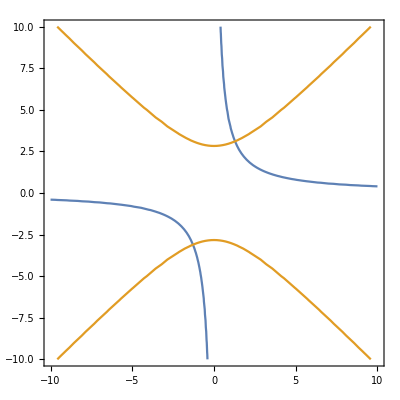

```mathematica
ContourPlot[{s*S==4,(1/2)(-s^2+S^2)==4},{s,-10,10},{S,-10,10},Frame->True]
```

```mathematica
(eqs03EliminatedGB[testAlgebra]=GroebnerBasis[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(-s^2+S^2)==s2pS2}],{stS,s2pS2},{s,S},MonomialOrder->EliminationOrder])
```

{16 s2pS2 stS+4 stS b[0]-b[3] b[4]+b[2] b[5]-b[1] b[6]-4 s2pS2 b[7],-16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-8 stS b[7],64 s2pS2^3+48 s2pS2^2 b[0]+8 s2pS2 b[0]^2+4 s2pS2 b[1]^2+b[0] b[1]^2+4 s2pS2 b[2]^2+b[0] b[2]^2+4 s2pS2 b[3]^2+b[0] b[3]^2-4 stS b[3] b[4]-4 s2pS2 b[4]^2-b[0] b[4]^2+4 stS b[2] b[5]-4 s2pS2 b[5]^2-b[0] b[5]^2-4 stS b[1] b[6]-4 s2pS2 b[6]^2-b[0] b[6]^2+4 stS b[0] b[7]+b[3] b[4] b[7]-b[2] b[5] b[7]+b[1] b[6] b[7]+4 s2pS2 b[7]^2}

The back substitution is. Note that in fact only two solutions exists (the sign of both s and S have to be the same.) Since √(s2pS2^2+ stS^2)>=s2pS2 the solutions 1 and 2 are complex and should be not taken into account

```mathematica
solsAndS[testAlgebra]=Solve[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S}]//FullSimplify
```

Solving in the field of Reals confirms that just we have 2 real roots

```mathematica
Reduce[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{S,s},
Backsubstitution->True]
```

```mathematica
solsAndSRealssS[testAlgebra]=FullSimplify/@Solve[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[-√2 √s2pS2,stS==0]},{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[√2 √s2pS2,stS==0]},{s→ConditionalExpression[-√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[-√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]}}

Prepare for program

```mathematica
(solsAndSRealssS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{stS==0->zeroQ[stS],Sqrt[-s2pS2-Sqrt[s2pS2^2+stS^2]]≠0->positiveQ[-s2pS2-Sqrt[s2pS2^2+stS^2]],Sqrt[-s2pS2+Sqrt[s2pS2^2+stS^2]]≠0->positiveQ[-s2pS2+Sqrt[s2pS2^2+stS^2]]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[
    takeMe[-(stS/Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]])], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[
    takeMe[stS/Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[
    takeMe[-(stS/Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]])], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[
    takeMe[stS/Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]]}}

The reduce answer is  usefull when analysing all cases (Solve reorders vars, in contrary, Reduce don’ reorder!)

```mathematica
FullSimplify/@Solve[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},MaxExtraConditions->All]
```

{{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[-√2 √s2pS2,stS==0]},{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[√2 √s2pS2,stS==0]},{s→ConditionalExpression[-√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[-√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]}}

```mathematica
FullSimplify/@Solve[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},Method->"Reduce"]
```

{{s→-√(-s2pS2-√(s2pS2^2+stS^2)),S→-stS/(√(-s2pS2-√(s2pS2^2+stS^2)))},{s→√(-s2pS2-√(s2pS2^2+stS^2)),S→stS/(√(-s2pS2-√(s2pS2^2+stS^2)))},{s→-√(-s2pS2+√(s2pS2^2+stS^2)),S→-stS/(√(-s2pS2+√(s2pS2^2+stS^2)))},{s→√(-s2pS2+√(s2pS2^2+stS^2)),S→stS/(√(-s2pS2+√(s2pS2^2+stS^2)))}}

The next answer is included in the article

```mathematica
solSsReduce[testAlgebra]=FullSimplify/@Reduce[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},Backsubstitution->True]
```

(s+√(-s2pS2-√(s2pS2^2+stS^2))==0&&S+stS/(√(-s2pS2-√(s2pS2^2+stS^2)))==0)||(√(-s2pS2-√(s2pS2^2+stS^2))==s&&√(-s2pS2-√(s2pS2^2+stS^2))≠0&&S==stS/(√(-s2pS2-√(s2pS2^2+stS^2))))||(s+√(-s2pS2+√(s2pS2^2+stS^2))==0&&S+stS/(√(-s2pS2+√(s2pS2^2+stS^2)))==0)||(√(-s2pS2+√(s2pS2^2+stS^2))==s&&√(-s2pS2+√(s2pS2^2+stS^2))≠0&&S==stS/(√(-s2pS2+√(s2pS2^2+stS^2))))||(stS==0&&s==0&&S+√2 √s2pS2==0)||(stS==0&&s==0&&S==√2 √s2pS2)

```mathematica
solSsSolveReduce[testAlgebra]=FullSimplify/@Solve[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},Method->"Reduce"]
```

{{s→-√(-s2pS2-√(s2pS2^2+stS^2)),S→-stS/(√(-s2pS2-√(s2pS2^2+stS^2)))},{s→√(-s2pS2-√(s2pS2^2+stS^2)),S→stS/(√(-s2pS2-√(s2pS2^2+stS^2)))},{s→-√(-s2pS2+√(s2pS2^2+stS^2)),S→-stS/(√(-s2pS2+√(s2pS2^2+stS^2)))},{s→√(-s2pS2+√(s2pS2^2+stS^2)),S→stS/(√(-s2pS2+√(s2pS2^2+stS^2)))}}

```mathematica
solSsSolve[testAlgebra]=Solve[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},MaxExtraConditions->All, VerifySolutions->True]
```

{{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[-√2 √s2pS2,stS==0]},{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[√2 √s2pS2,stS==0]},{s→ConditionalExpression[-√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[-√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]}}

```mathematica
(sol03Eliminated[testAlgebra]=Solve[eqs03Eliminated[testAlgebra],{stS,s2pS2}])//Length
```

4

```mathematica
(sol03EliminatedGB[testAlgebra]=Solve[Thread[eqs03EliminatedGB[testAlgebra]==0],{stS,s2pS2}])//Length
```

4

```mathematica
LeafCount/@{sol03Eliminated[testAlgebra],sol03Eliminated[testAlgebra]}
```

{11229,11229}

Rewrite in coordinate free form. Evaluate this group

Noticing the following relations try to rewrite equation in coordinate free form from the beginning

```mathematica
b1
```

b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300

```mathematica
(gaGetMV[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra],{0}])//gaPE//Expand
```

2 b[3] b[4]-2 b[2] b[5]+2 b[1] b[6]-2 b[0] b[7]

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

2 b_{3} b_{12}-2 b_{2} b_{13}+2 b_{1} b_{23}-2 b_{0} b_{123}

```mathematica
gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]
```

b[0]^2-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-b[7]^2

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

b_{0}^2-b_{1}^2-b_{2}^2-b_{3}^2+b_{12}^2+b_{13}^2+b_{23}^2-b_{123}^2

```mathematica
detNorm[testAlgebra]=gaDeterminantNorm[b1]
```

(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-b[7]^2)^2

bCCb0^2+bCCbI0^2 žemiau formulėse yra determinantas

```mathematica
Expand[gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]^2+gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]^2 -gaDeterminantNorm[b1]]
```

0

Determinant norm is always positive for cl30 !!!

```mathematica
(detTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];detNorm[testAlgebra]/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[detTable[testAlgebra],NonNegative]
```

True

```mathematica
eqs03EliminatedGB[testAlgebra]
```

{16 s2pS2 stS+4 stS b[0]-b[3] b[4]+b[2] b[5]-b[1] b[6]-4 s2pS2 b[7],-16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-8 stS b[7],64 s2pS2^3+48 s2pS2^2 b[0]+8 s2pS2 b[0]^2+4 s2pS2 b[1]^2+b[0] b[1]^2+4 s2pS2 b[2]^2+b[0] b[2]^2+4 s2pS2 b[3]^2+b[0] b[3]^2-4 stS b[3] b[4]-4 s2pS2 b[4]^2-b[0] b[4]^2+4 stS b[2] b[5]-4 s2pS2 b[5]^2-b[0] b[5]^2-4 stS b[1] b[6]-4 s2pS2 b[6]^2-b[0] b[6]^2+4 stS b[0] b[7]+b[3] b[4] b[7]-b[2] b[5] b[7]+b[1] b[6] b[7]+4 s2pS2 b[7]^2}

```mathematica
(eqs03EliminatedDimensionless[testAlgebra]=Eliminate[Join[Thread[Equal[(Collect[#,{stS,s2pS2},FullSimplify]&/@eqs03EliminatedGB[testAlgebra]),0]],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}])//AbsoluteTiming
```

{0.271218,bCCb0==16 s2pS2^2-16 stS^2+8 s2pS2 b[0]+b[0]^2+8 stS b[7]-b[7]^2&&bCCbI0==32 s2pS2 stS+8 stS b[0]-8 s2pS2 b[7]-2 b[0] b[7]}

```mathematica
tryDenomZero=FullSimplify/@(Subtract@@@(List@@eqs03EliminatedDimensionless[testAlgebra]))
```

{bCCb0-(4 s2pS2+4 stS+b[0]-b[7]) (4 s2pS2-4 stS+b[0]+b[7]),bCCbI0-2 (4 s2pS2+b[0]) (4 stS-b[7])}

```mathematica
(eqs03EliminatedGBDimensionless[testAlgebra]=GroebnerBasis[Join[eqs03EliminatedGB[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]-bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]-bCCbI0}],{stS,s2pS2},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder])//AbsoluteTiming
```

{0.111199,{-bCCbI0+32 s2pS2 stS+8 stS b[0]-8 s2pS2 b[7]-2 b[0] b[7],bCCb0-16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3-4 bCCbI0 stS-2 bCCb0 b[0]+96 s2pS2^2 b[0]+24 s2pS2 b[0]^2+2 b[0]^3+bCCbI0 b[7]}}

This is solution in case bCCbI0=0

```mathematica
Solve[Thread[(tryDenomZero/.{bCCbI0->0})==0],{stS,s2pS2}]
```

{{stS→1/4 (-√-bCCb0+b[7]),s2pS2→-b[0]/4},{stS→1/4 (√-bCCb0+b[7]),s2pS2→-b[0]/4},{stS→b[7]/4,s2pS2→1/4 (-√bCCb0-b[0])},{stS→b[7]/4,s2pS2→1/4 (√bCCb0-b[0])}}

{s2pS2,stS} ordering yields shorter and nicer results

```mathematica
(solFinalSolveNPForProgram[testAlgebra]=FullSimplify/@(Solve[Thread[GroebnerBasis[eqs03EliminatedGBDimensionless[testAlgebra],{s2pS2,stS}]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2+bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

Prepare to include into program

```mathematica
(solFinalSolveNPForProgram[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]//.{Sqrt[detb]->detSqrt,bCCbI0==0->zeroQ[bCCbI0],Sqrt[-bCCb0-detSqrt]≠0->positiveQ[-bCCb0-detSqrt],Sqrt[-bCCb0+detSqrt]≠0->positiveQ[-bCCb0+detSqrt]})})//InputForm
```

{{stS -> ConditionalExpression[takeMe[b[7]/4], zeroQ[bCCbI0]], 
  s2pS2 -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] - b[0])/4], 
    zeroQ[bCCbI0]]}, {stS -> ConditionalExpression[takeMe[b[7]/4], 
    zeroQ[bCCbI0]], s2pS2 -> ConditionalExpression[
    takeMe[(Sqrt[bCCb0] - b[0])/4], zeroQ[bCCbI0]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[-bCCb0 - detSqrt]/Sqrt[2]) + 
       b[7])/4], positiveQ[-bCCb0 - detSqrt]], 
  s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 - detSqrt]) - 2*b[0])/8], 
    positiveQ[-bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[-bCCb0 - detSqrt]/Sqrt[2] + b[7])/
      4], positiveQ[-bCCb0 - detSqrt]], 
  s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 - detSqrt] - 2*b[0])/8], 
    positiveQ[-bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[-bCCb0 + detSqrt]/Sqrt[2]) + 
       b[7])/4], positiveQ[-bCCb0 + detSqrt]], 
  s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 + detSqrt]) - 2*b[0])/8], 
    positiveQ[-bCCb0 + detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[-bCCb0 + detSqrt]/Sqrt[2] + b[7])/
      4], positiveQ[-bCCb0 + detSqrt]], 
  s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 + detSqrt] - 2*b[0])/8], 
    positiveQ[-bCCb0 + detSqrt]]}}

Toliau beveik nereikalinga medziaga.

Other variants (needs clearing)

```mathematica
(solFinalSolveNP[testAlgebra]=FullSimplify/@(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2+bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[1/4 (-√-bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[-b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/4 (√-bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[-b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[(√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (-√2 √(bCCb0-√detb)-2 b[0]),bCCbI0≠0]},{stS→ConditionalExpression[(-√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (√2 √(bCCb0-√detb)-2 b[0]),bCCbI0≠0]},{stS→ConditionalExpression[(√2 (bCCb0-√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (-√2 √(bCCb0+√detb)-2 b[0]),bCCbI0≠0]},{stS→ConditionalExpression[(√2 (-bCCb0+√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (√2 √(bCCb0+√detb)-2 b[0]),bCCbI0≠0]}}

```mathematica
(solFinalSolveNP[testAlgebra]=FullSimplify/@(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2+bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

For article

```mathematica
FullSimplify/@eqs03EliminatedGBDimensionless[testAlgebra]
```

{-bCCbI0+2 (4 s2pS2+b[0]) (4 stS-b[7]),bCCb0-(4 s2pS2+4 stS+b[0]-b[7]) (4 s2pS2-4 stS+b[0]+b[7]),-2 bCCb0 (4 s2pS2+b[0])+2 (4 s2pS2+b[0])^3+bCCbI0 (-4 stS+b[7])}

```mathematica
StringReplace[ToString[TeXForm[FullSimplify[eqs03EliminatedGBDimensionless[testAlgebra]]]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

\left\{2 (b_{0}+4 T) (4 t-b_{123})-b_{I},b_{S}-(b_{0}-b_{123}+4 T+4 t) (b_{0}+b_{123}+4 T-4 t),-2 b_{S} (b_{0}+4 T)+b_{I} (b_{123}-4 t)+2 (b_{0}+4 T)^3\right\}

Since coefficients b[0] and b[7] enters sometimes as single coefficients it cannot probably be further simplified. Further simplification of expressions giving all assumptions about positivity of det and reality of coefficients do not yield simplification

```mathematica
(solFinalReduceMethod[testAlgebra]=FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},Method->"Reduce"])/.{bCCb0^2+bCCbI0^2->detb}
```

{{stS→1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),s2pS2→(√2 √(-bCCb0-√detb) (-bCCb0+√detb)-2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),s2pS2→(√2 √(-bCCb0-√detb) (bCCb0-√detb)-2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),s2pS2→-(√2 √(-bCCb0+√detb) (bCCb0+√detb)+2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),s2pS2→(√2 √(-bCCb0+√detb) (bCCb0+√detb)-2 bCCbI0 b[0])/(8 bCCbI0)}}

The ebst representation is solFinalSolve[testAlgebra]

```mathematica
eqs03EliminatedGBDimensionless[testAlgebra]
```

{-bCCbI0+32 s2pS2 stS+8 stS b[0]-8 s2pS2 b[7]-2 b[0] b[7],bCCb0-16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3-4 bCCbI0 stS-2 bCCb0 b[0]+96 s2pS2^2 b[0]+24 s2pS2 b[0]^2+2 b[0]^3+bCCbI0 b[7]}

```mathematica
(solFinalSolve[testAlgebra]=((FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All, VerifySolutions->True]))/.{bCCb0^2+bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[1/4 (-√-bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[-b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/4 (√-bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[-b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[(√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (-√2 √(bCCb0-√detb)-2 b[0]),bCCbI0≠0]},{stS→ConditionalExpression[(-√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (√2 √(bCCb0-√detb)-2 b[0]),bCCbI0≠0]},{stS→ConditionalExpression[(√2 (bCCb0-√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (-√2 √(bCCb0+√detb)-2 b[0]),bCCbI0≠0]},{stS→ConditionalExpression[(√2 (-bCCb0+√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0],s2pS2→ConditionalExpression[1/8 (√2 √(bCCb0+√detb)-2 b[0]),bCCbI0≠0]}}

Prepare to include intu program

```mathematica
(solFinalSolve[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{Sqrt[detb]->detSqrt})})//InputForm
```

{{stS -> ConditionalExpression[takeMe[b[7]/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0], 
  s2pS2 -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] - b[0])/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0]}, 
 {stS -> ConditionalExpression[takeMe[b[7]/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0], 
  s2pS2 -> ConditionalExpression[takeMe[(Sqrt[bCCb0] - b[0])/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0]}, 
 {stS -> ConditionalExpression[takeMe[(-Sqrt[-bCCb0] + b[7])/4], 
    bCCbI0 == 0], s2pS2 -> ConditionalExpression[takeMe[-b[0]/4], 
    bCCbI0 == 0]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[-bCCb0] + b[7])/4], bCCbI0 == 0], 
  s2pS2 -> ConditionalExpression[takeMe[-b[0]/4], bCCbI0 == 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*Sqrt[bCCb0 - detSqrt]*(bCCb0 + detSqrt) + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(-(Sqrt[2]*Sqrt[bCCb0 - detSqrt]) - 2*b[0])/8], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(-(Sqrt[2]*Sqrt[bCCb0 - detSqrt]*(bCCb0 + detSqrt)) + 
       2*bCCbI0*b[7])/(8*bCCbI0)], bCCbI0 != 0], 
  s2pS2 -> ConditionalExpression[
    takeMe[(Sqrt[2]*Sqrt[bCCb0 - detSqrt] - 2*b[0])/8], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*(bCCb0 - detSqrt)*Sqrt[bCCb0 + detSqrt] + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(-(Sqrt[2]*Sqrt[bCCb0 + detSqrt]) - 2*b[0])/8], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*(-bCCb0 + detSqrt)*Sqrt[bCCb0 + detSqrt] + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(Sqrt[2]*Sqrt[bCCb0 + detSqrt] - 2*b[0])/8], bCCbI0 != 0]}}

If we remove last equation, the solution in general will  differ

```mathematica
(solFinalSolve[testAlgebra]=((FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},MaxExtraConditions->All, VerifySolutions->True]))/.{bCCb0^2+bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

```mathematica
solFinalReduce[testAlgebra]=(Reduce[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},Backsubstitution->True]//FullSimplify)/.{bCCb0^2+bCCbI0^2->detb}
```

(bCCbI0==0&&4 stS==b[7]&&(√bCCb0==4 s2pS2+b[0]||√bCCb0+4 s2pS2+b[0]==0))||(√(-bCCb0-√detb)≠0&&((√2 √(-bCCb0-√detb)+8 stS==2 b[7]&&(√2 bCCbI0)/(√(-bCCb0-√detb))+8 s2pS2+2 b[0]==0)||(8 s2pS2+2 b[0]==(√2 bCCbI0)/(√(-bCCb0-√detb))&&√2 √(-bCCb0-√detb)+2 b[7]==8 stS)))||(√(-bCCb0+√detb)≠0&&((√2 √(-bCCb0+√detb)+8 stS==2 b[7]&&(√2 bCCbI0)/(√(-bCCb0+√detb))+8 s2pS2+2 b[0]==0)||(8 s2pS2+2 b[0]==(√2 bCCbI0)/(√(-bCCb0+√detb))&&√2 √(-bCCb0+√detb)+2 b[7]==8 stS)))

Solutions of the following two equations are the same as of the entire GB system. Below is an explicit check, suppress evaluation

```mathematica
(solFinalSolveNP[testAlgebra]=(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2}]//FullSimplify)/.{bCCb0^2+bCCbI0^2->detb})//LeafCount
```

295

```mathematica
((Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2}]//FullSimplify)/.{bCCb0^2+bCCbI0^2->detb})//LeafCount
```

288

For article Dargys (Nonlinear phenomena)

```mathematica
{solFinalSolveNP[testAlgebra][[3]],solFinalSolveNP[testAlgebra][[4]]}//Column
```

{stS→1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),s2pS2→-(√2 √(-bCCb0+√detb) (bCCb0+√detb)+2 bCCbI0 b[0])/(8 bCCbI0)}
{stS→1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),s2pS2→(√2 √(-bCCb0+√detb) (bCCb0+√detb)-2 bCCbI0 b[0])/(8 bCCbI0)}

```mathematica
StringReplace[ToString[TeXForm[solFinalSolve[testAlgebra][[3]]]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{t\to \frac{1}{4} \left(b_{123}-\frac{\sqrt{D-b_{S}}}{\sqrt{2}}\right),T\to -\frac{2 b_{0} b_{I}+\sqrt{2} \sqrt{D-b_{S}} \left(b_{S}+D\right)}{4 b_{I}}\right\}

In future we will use answer of solFinalSolve[testAlgebra] since it is more symmetric and covers all cases. This is final answer:

```mathematica
solFinalSolve[testAlgebra]
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

Older attempt with pure Reduce (do not evaluate)

```mathematica
(solFinalReduce[testAlgebra]=Reduce[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},Backsubstitution->True]//FullSimplify)/.{bCCb0^2+bCCbI0^2->detb}
```

```mathematica
solFinalReduceSolved[testAlgebra,3]=Solve[solFinalReduce[testAlgebra][[3]],{stS,s2pS2}]
```

```mathematica
solFinalReduceSolved[testAlgebra,3]=Solve[solFinalReduce[testAlgebra][[3]],{stS,s2pS2}]
```

When √(-bCCb0-√detb)=0 we have

```mathematica
solFinalReduceSolved[testAlgebra,1]=Solve[solFinalReduce[testAlgebra][[1]],{stS,s2pS2}]
```

```mathematica
solFinalSolve[testAlgebra]
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

```mathematica
solFinalReduceSolved[testAlgebra,3]=Solve[solFinalReduce[testAlgebra][[3]],{stS,s2pS2}]
```

{{stS→1/8 (√2 √(-bCCb0+√detb)+2 b[7]),s2pS2→(√2 bCCbI0-2 √(-bCCb0+√detb) b[0])/(8 √(-bCCb0+√detb))},{stS→1/8 (-√2 √(-bCCb0+√detb)+2 b[7]),s2pS2→(-√2 bCCbI0-2 √(-bCCb0+√detb) b[0])/(8 √(-bCCb0+√detb))}}

When √(-bCCb0-√detb)=0 we have

```mathematica
solFinalReduceSolved[testAlgebra,1]=Solve[solFinalReduce[testAlgebra][[1]],{stS,s2pS2}]
```

{{stS→b[7]/4,s2pS2→1/4 (-√bCCb0-b[0])},{stS→b[7]/4,s2pS2→1/4 (√bCCb0-b[0])}}

Special cl(3,0) case, when s == S and s == -S

Case s == S  and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]+v[1]^2+v[2]^2+v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,-b[1]+2 s v[1]-2 s V[1]==0,-b[2]+2 s v[2]-2 s V[2]==0,-b[3]+2 s v[3]-2 s V[3]==0,-b[4]+2 s v[3]+2 s V[3]==0,-b[5]-2 s v[2]-2 s V[2]==0,-b[6]+2 s v[1]+2 s V[1]==0,2 s^2-b[7]+2 v[1] V[1]+2 v[2] V[2]+2 v[3] V[3]==0}

Taigi, net kai s=S neatsiranda ypatingumo

```mathematica
solsvVRealsSeqPluss[testAlgebra]=Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[(b[1]+b[6])/(4 s),s≠0],v[2]→ConditionalExpression[(b[2]-b[5])/(4 s),s≠0],v[3]→ConditionalExpression[(b[3]+b[4])/(4 s),s≠0],V[1]→ConditionalExpression[(-b[1]+b[6])/(4 s),s≠0],V[2]→ConditionalExpression[-(b[2]+b[5])/(4 s),s≠0],V[3]→ConditionalExpression[(-b[3]+b[4])/(4 s),s≠0]}

```mathematica
(solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[(b[1] + b[6])/(4*s)], nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[(b[2] - b[5])/(4*s)], nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[(b[3] + b[4])/(4*s)], nonzeroQ[s]], 
 V[1] -> ConditionalExpression[takeMe[(-b[1] + b[6])/(4*s)], nonzeroQ[s]], 
 V[2] -> ConditionalExpression[takeMe[-(b[2] + b[5])/(4*s)], nonzeroQ[s]], 
 V[3] -> ConditionalExpression[takeMe[(-b[3] + b[4])/(4*s)], nonzeroQ[s]]}

```mathematica
eqsS0FL[testAlgebra]=Simplify[eqsS0[testAlgebra][[{1,8}]]/.(solsvVRealsSeqPluss[testAlgebra]/.{s≠0->True})]
```

{(4 s^2 b[0]-b[3] b[4]+b[2] b[5]-b[1] b[6])/s==0,(16 s^4-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-8 s^2 b[7])/s==0}

```mathematica
eqsS0FLElimManual[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}]
```

bCCb0+(-4 s^2+b[7])^2==b[0]^2&&bCCbI0==b[0] (8 s^2-2 b[7])&&s≠0

```mathematica
Solve[bCCbI0==b[0] (8 s^2-2 b[7]),s]
```

{{s→-(√(bCCbI0+2 b[0] b[7]))/(2 √2 √b[0])},{s→(√(bCCbI0+2 b[0] b[7]))/(2 √2 √b[0])}}

```mathematica
Solve[bCCb0+(-4 s^2+b[7])^2==b[0]^2,s]
```

{{s→-1/2 √(-√(-bCCb0+b[0]^2)+b[7])},{s→1/2 √(-√(-bCCb0+b[0]^2)+b[7])},{s→-1/2 √(√(-bCCb0+b[0]^2)+b[7])},{s→1/2 √(√(-bCCb0+b[0]^2)+b[7])}}

This is an answer

```mathematica
Solve[eqsS0FLElimManual[testAlgebra],s,MaxExtraConditions->All]
```

{{s→ConditionalExpression[-1/2 √b[7],bCCb0==b[0]^2&&bCCbI0==0&&-1/2 b[0] √b[7]≠0]},{s→ConditionalExpression[(√b[7])/2,bCCb0==b[0]^2&&bCCbI0==0&&1/2 b[0] √b[7]≠0]},{s→ConditionalExpression[-1/2 √(-√-bCCb0+b[7]),bCCbI0==0&&√(-√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(-√-bCCb0+b[7]),bCCbI0==0&&√(-√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 √(√-bCCb0+b[7]),bCCbI0==0&&√(√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(√-bCCb0+b[7]),bCCbI0==0&&√(√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2-4 b[0]^2==0&&bCCbI0≠0&&(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0&&b[0]≠0]},{s→ConditionalExpression[(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2-4 b[0]^2==0&&bCCbI0≠0&&(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0&&b[0]≠0]}}

```mathematica
gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]
```

b[0]^2-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-b[7]^2

```mathematica
gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]
```

2 b[3] b[4]-2 b[2] b[5]+2 b[1] b[6]-2 b[0] b[7]

```mathematica
eqsS0FLElimb16[testAlgebra]=GroebnerBasis[GroebnerBasis[Join[eqsS0FL[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[7],b[0]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder],{s}]
```

{bCCbI0^2+4 bCCb0 b[0]^2-4 b[0]^4,-bCCbI0+8 s^2 b[0]-2 b[0] b[7],4 bCCbI0 s^2+2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7],bCCb0+16 s^4-b[0]^2-8 s^2 b[7]+b[7]^2,-bCCb0/s-16 s^3+b[0]^2/s+8 s b[7]-b[7]^2/s,bCCbI0/s-8 s b[0]+(2 b[0] b[7])/s}

```mathematica
solRealsS[testAlgebra]=FullSimplify/@Solve[Thread[eqsS0FLElimb16[testAlgebra]==0],{s},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[-1/2 √b[7],bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[(√b[7])/2,bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[-1/2 √(-√-bCCb0+b[7]),bCCbI0==0&&√(-√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(-√-bCCb0+b[7]),bCCbI0==0&&√(-√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 √(√-bCCb0+b[7]),bCCbI0==0&&√(√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(√-bCCb0+b[7]),bCCbI0==0&&√(√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0]},{s→ConditionalExpression[(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0]}}

Prepare input for program

```mathematica
(solRealsS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{bCCbI0≠0->nonzeroQ[bCCbI0],(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0->positiveQ[-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]],bCCbI0==0->zeroQ[bCCbI0],√(-√-bCCb0+b[7])≠0->positiveQ[-√-bCCb0+b[7]]&&positiveQ[-bCCb0],bCCb0==b[0]^2->zeroQ[bCCb0-b[0]^2],b[0]*Sqrt[b[7]]≠0->nonzeroQ[b[0]*Sqrt[b[7]]]&&positiveQ[b[7]],b[0]==0->zeroQ[b[0]],√(√-bCCb0+b[7])≠0->positiveQ[√-bCCb0+b[7]]&&positiveQ[-bCCb0]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[-Sqrt[b[7]]/2], zeroQ[bCCb0 - b[0]^2] && 
     zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && positiveQ[b[7]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[b[7]]/2], zeroQ[bCCb0 - b[0]^2] && 
     zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && positiveQ[b[7]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] + b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] + b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] + b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] + b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]]}}

```mathematica
Solve[Thread[eqsS0FLElimb16[testAlgebra]==0],{s},VerifySolutions->True,Method->Reduce,MaxExtraConditions->All]
```

Case s == -S  and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->-s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]+v[1]^2+v[2]^2+v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,-b[1]+2 s v[1]+2 s V[1]==0,-b[2]+2 s v[2]+2 s V[2]==0,-b[3]+2 s v[3]+2 s V[3]==0,-b[4]-2 s v[3]+2 s V[3]==0,-b[5]+2 s v[2]-2 s V[2]==0,-b[6]-2 s v[1]+2 s V[1]==0,-2 s^2-b[7]+2 v[1] V[1]+2 v[2] V[2]+2 v[3] V[3]==0}

Taigi, net kai s=-S neatsiranda ypatingumo

```mathematica
solsvVRealsSeqMinuss[testAlgebra]=Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[(b[1]-b[6])/(4 s),s≠0],v[2]→ConditionalExpression[(b[2]+b[5])/(4 s),s≠0],v[3]→ConditionalExpression[(b[3]-b[4])/(4 s),s≠0],V[1]→ConditionalExpression[(b[1]+b[6])/(4 s),s≠0],V[2]→ConditionalExpression[(b[2]-b[5])/(4 s),s≠0],V[3]→ConditionalExpression[(b[3]+b[4])/(4 s),s≠0]}

```mathematica
(solsvVRealsSeqMinuss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[(b[1] - b[6])/(4*s)], nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[(b[2] + b[5])/(4*s)], nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[(b[3] - b[4])/(4*s)], nonzeroQ[s]], 
 V[1] -> ConditionalExpression[takeMe[(b[1] + b[6])/(4*s)], nonzeroQ[s]], 
 V[2] -> ConditionalExpression[takeMe[(b[2] - b[5])/(4*s)], nonzeroQ[s]], 
 V[3] -> ConditionalExpression[takeMe[(b[3] + b[4])/(4*s)], nonzeroQ[s]]}

```mathematica
eqsS0FL[testAlgebra]=Simplify[eqsS0[testAlgebra][[{1,8}]]/.(solsvVRealsSeqMinuss[testAlgebra]/.{s≠0->True})]
```

{(4 s^2 b[0]+b[3] b[4]-b[2] b[5]+b[1] b[6])/s==0,(16 s^4-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2+8 s^2 b[7])/s==0}

```mathematica
eqsS0FLElimManual[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}]
```

bCCb0+(4 s^2+b[7])^2==b[0]^2&&bCCbI0==-2 b[0] (4 s^2+b[7])&&s≠0

```mathematica
Solve[bCCbI0==-2 b[0] (4 s^2+b[7]),s]
```

{{s→-(√(-bCCbI0-2 b[0] b[7]))/(2 √2 √b[0])},{s→(√(-bCCbI0-2 b[0] b[7]))/(2 √2 √b[0])}}

```mathematica
Solve[bCCb0+(4 s^2+b[7])^2==0,s]
```

{{s→-1/2 √(-√-bCCb0-b[7])},{s→1/2 √(-√-bCCb0-b[7])},{s→-1/2 √(√-bCCb0-b[7])},{s→1/2 √(√-bCCb0-b[7])}}

This is an answer

```mathematica
Solve[eqsS0FLElimManual[testAlgebra],s,MaxExtraConditions->All]
```

{{s→ConditionalExpression[-1/2 √(-√-bCCb0-b[7]),bCCbI0==0&&√(-√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(-√-bCCb0-b[7]),bCCbI0==0&&√(-√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 √(√-bCCb0-b[7]),bCCbI0==0&&√(√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(√-bCCb0-b[7]),bCCbI0==0&&√(√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 ⅈ √b[7],bCCb0==b[0]^2&&bCCbI0==0&&-1/2 ⅈ b[0] √b[7]≠0]},{s→ConditionalExpression[1/2 ⅈ √b[7],bCCb0==b[0]^2&&bCCbI0==0&&1/2 ⅈ b[0] √b[7]≠0]},{s→ConditionalExpression[-(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2-4 b[0]^2==0&&bCCbI0≠0&&(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0&&b[0]≠0]},{s→ConditionalExpression[(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2-4 b[0]^2==0&&bCCbI0≠0&&(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0&&b[0]≠0]}}

```mathematica
gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]
```

b[0]^2-b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2+b[6]^2-b[7]^2

```mathematica
gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]
```

2 b[3] b[4]-2 b[2] b[5]+2 b[1] b[6]-2 b[0] b[7]

```mathematica
eqsS0FLElimb16[testAlgebra]=GroebnerBasis[GroebnerBasis[Join[eqsS0FL[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[7],b[0]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder],{s}]
```

{bCCbI0^2+4 bCCb0 b[0]^2-4 b[0]^4,bCCbI0+8 s^2 b[0]+2 b[0] b[7],4 bCCbI0 s^2-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7],bCCb0+16 s^4-b[0]^2+8 s^2 b[7]+b[7]^2,-bCCb0/s-16 s^3+b[0]^2/s-8 s b[7]-b[7]^2/s,bCCbI0/s+8 s b[0]+(2 b[0] b[7])/s}

```mathematica
solRealsS[testAlgebra]=FullSimplify/@Solve[Thread[eqsS0FLElimb16[testAlgebra]==0],{s},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[-1/2 √(-√-bCCb0-b[7]),bCCbI0==0&&√(-√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(-√-bCCb0-b[7]),bCCbI0==0&&√(-√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 √(√-bCCb0-b[7]),bCCbI0==0&&√(√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(√-bCCb0-b[7]),bCCbI0==0&&√(√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 ⅈ √b[7],bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[1/2 ⅈ √b[7],bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[-(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0]},{s→ConditionalExpression[(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0]}}

Prepare input for program

```mathematica
(solRealsS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a]/.{1/2 ⅈ √b[7]->1/2  √(-b[7]),-1/2 ⅈ √b[7]->-1/2  √(-b[7])},x]/.{bCCbI0≠0->nonzeroQ[bCCbI0],(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0->positiveQ[2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]],bCCbI0==0->zeroQ[bCCbI0],√(√-bCCb0-b[7])≠0->positiveQ[√-bCCb0-b[7]]&&positiveQ[-bCCb0],bCCb0==b[0]^2->zeroQ[bCCb0-b[0]^2],b[0]*Sqrt[b[7]]≠0->nonzeroQ[b[0]*Sqrt[b[7]]]&&positiveQ[-b[7]],b[0]==0->zeroQ[b[0]],√(-√-bCCb0-b[7])≠0->positiveQ[-√-bCCb0-b[7]]&&positiveQ[-bCCb0]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[-Sqrt[-Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] - b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] - b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] - b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] - b[7]] && positiveQ[-bCCb0] && 
     zeroQ[b[0]]]}, {s -> ConditionalExpression[takeMe[-Sqrt[-b[7]]/2], 
    zeroQ[bCCb0 - b[0]^2] && zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && 
     positiveQ[-b[7]]]}, {s -> ConditionalExpression[takeMe[Sqrt[-b[7]]/2], 
    zeroQ[bCCb0 - b[0]^2] && zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && 
     positiveQ[-b[7]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]]}}

```mathematica
Solve[Thread[eqsS0FLElimb16[testAlgebra]==0],{s},VerifySolutions->True,Method->Reduce,MaxExtraConditions->All]
```

Case s == S==0, here v,V cannot be solved

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[v1 +(V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]+v[1]^2+v[2]^2+v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,-b[1]==0,-b[2]==0,-b[3]==0,-b[4]==0,-b[5]==0,-b[6]==0,-b[7]+2 v[1] V[1]+2 v[2] V[2]+2 v[3] V[3]==0}

```mathematica
vsol0=FullSimplify/@Solve[eqsS0[testAlgebra][[{1,8}]],{v[1],V[1]}]
```

{{v[1]→-1/(√2)(√(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2-√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2))),V[1]→(-b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2-√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2)))},{v[1]→1/(√2)(√(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2-√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2))),V[1]→(b[7]-2 (v[2] V[2]+v[3] V[3]))/(√2 √(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2-√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2)))},{v[1]→-1/(√2)(√(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2+√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2))),V[1]→(-b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2+√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2)))},{v[1]→1/(√2)(√(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2+√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2))),V[1]→(b[7]-2 (v[2] V[2]+v[3] V[3]))/(√2 √(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2+√((b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2 (v[2] V[2]+v[3] V[3]))^2)))}}

```mathematica
vsol0[[4]]//InputForm
```

{v[1] -> Sqrt[b[0] - v[2]^2 - v[3]^2 + V[2]^2 + V[3]^2 + 
     Sqrt[(b[0] - v[2]^2 - v[3]^2 + V[2]^2 + V[3]^2)^2 + 
       (b[7] - 2*(v[2]*V[2] + v[3]*V[3]))^2]]/Sqrt[2], 
 V[1] -> (b[7] - 2*(v[2]*V[2] + v[3]*V[3]))/
   (Sqrt[2]*Sqrt[b[0] - v[2]^2 - v[3]^2 + V[2]^2 + V[3]^2 + 
      Sqrt[(b[0] - v[2]^2 - v[3]^2 + V[2]^2 + V[3]^2)^2 + 
        (b[7] - 2*(v[2]*V[2] + v[3]*V[3]))^2]])}

```mathematica
StringReplace[ToString[TeXForm[vsol0[[4]]]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{v_{1}\to \frac{\sqrt{\sqrt{\left(b_{0}-v_{2}^2-v_{3}^2+V_{2}^2+V_{3}^2\right)^2+(b_{123}-2 (v_{2} V_{2}+v_{3} V_{3}))^2}+b_{0}-v_{2}^2-v_{3}^2+V_{2}^2+V_{3}^2}}{\sqrt{2}},V_{1}\to \frac{b_{123}-2 (v_{2} V_{2}+v_{3} V_{3})}{\sqrt{2} \sqrt{\sqrt{\left(b_{0}-v_{2}^2-v_{3}^2+V_{2}^2+V_{3}^2\right)^2+(b_{123}-2 (v_{2} V_{2}+v_{3} V_{3}))^2}+b_{0}-v_{2}^2-v_{3}^2+V_{2}^2+V_{3}^2}}\right\}

We can’t solve vectors  v and V in this case

Test if we can solve for 𝕖_1+𝕖_{1,2} (which fails with the method below) It fails also here, however for 𝕖_1 solution exists, and is found by general coefficients

```mathematica
eqsS0Spec[testAlgebra]=eqsS0[testAlgebra]/.Join[Thread[{b[0],b[2],b[3],b[5],b[6],b[7]}->0],{b[1]->1,b[4]->1}]
```

{v[1]^2+v[2]^2+v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,-1+2 s v[1]+2 s V[1]==0,2 s v[2]+2 s V[2]==0,2 s v[3]+2 s V[3]==0,-1-2 s v[3]+2 s V[3]==0,2 s v[2]-2 s V[2]==0,-2 s v[1]+2 s V[1]==0,-2 s^2+2 v[1] V[1]+2 v[2] V[2]+2 v[3] V[3]==0}

```mathematica
Solve[eqsS0Spec[testAlgebra],{s,v[1],v[2],v[3],V[1],V[2],V[3]},VerifySolutions->True,MaxExtraConditions->All]
```

{}

Eliminate {b[1],b[2],b[3],b[4],b[5],b[6]} in terms of bCCb0 and bCCbI0

```mathematica
eqsS0Elimb16[testAlgebra]=GroebnerBasis[Join[eqsS0[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[0],b[7]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder]//FullSimplify
```

{-b[7]+2 (v[1] V[1]+v[2] V[2]+v[3] V[3]),-b[0]+v[1]^2+v[2]^2+v[3]^2-V[1]^2-V[2]^2-V[3]^2,bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,b[7] v[1]+2 V[1] (-b[0]+v[2]^2+v[3]^2-V[1]^2)-2 (v[1] (v[2] V[2]+v[3] V[3])+V[1] (V[2]^2+V[3]^2)),bCCbI0 b[0]+2 b[7] (bCCb0+b[7]^2)}

Eliminate {v[1],v[2],v[3],V[1],V[2],V[3]} in terms of v1\[InnerProduct]V1=v[1] V[1]+v[2] V[2]+v[3] V[3] (the scalar produc). It is suprize that we do not need other components.  In the end we compute Groebner basis with respect to remaining vars s, and free params. The first equation, then yields a condition when the solution exists (has no vars).

```mathematica
eqsS0Elimb16AndVv[testAlgebra]=FullSimplify/@GroebnerBasis[GroebnerBasis[Join[eqsS0Elimb16[testAlgebra],{gaPE[v1\[InnerProduct]V1]-v1V2ip,gaPE[v1\[InnerProduct]v1-V1\[InnerProduct]V1]-v2mV2}],{v1V2ip,v2mV2},{v[1],v[2],v[3],V[1],V[2],V[3]},MonomialOrder->EliminationOrder],{v1V2ip,v2mV2}]
```

{-bCCbI0^2+4 b[7]^2 (bCCb0+b[7]^2),bCCbI0 b[0]+2 b[7] (bCCb0+b[7]^2),bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,v2mV2-b[0],2 v1V2ip-b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3}]],{bCCb0,bCCbI0,b[0],b[7]}]
```

{bCCbI0+2 b[0] b[7],bCCb0 b[7]-b[0]^2 b[7]+b[7]^3}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3}]],{bCCbI0,bCCb0,b[0],b[7]}]
```

{bCCb0 b[7]-b[0]^2 b[7]+b[7]^3,bCCbI0+2 b[0] b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3}]],{bCCbI0,bCCb0,b[7],b[0]}]
```

{bCCb0 b[7]-b[0]^2 b[7]+b[7]^3,bCCbI0+2 b[0] b[7]}

In fact we do not need to know substitution of v V the above is superfluous.

```mathematica
eqsS0Elimb16[testAlgebra]
```

{-b[7]+2 (v[1] V[1]+v[2] V[2]+v[3] V[3]),-b[0]+v[1]^2+v[2]^2+v[3]^2-V[1]^2-V[2]^2-V[3]^2,bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,b[7] v[1]+2 V[1] (-b[0]+v[2]^2+v[3]^2-V[1]^2)-2 (v[1] (v[2] V[2]+v[3] V[3])+V[1] (V[2]^2+V[3]^2)),bCCbI0 b[0]+2 b[7] (bCCb0+b[7]^2)}

```mathematica
GroebnerBasis[eqsS0Elimb16[testAlgebra][[{3,4,5}]],{bCCb0,bCCbI0,b[0],b[7]}]
```

{-b[7] v[1]+2 b[0] V[1]-2 v[2]^2 V[1]-2 v[3]^2 V[1]+2 V[1]^3+2 v[1] v[2] V[2]+2 V[1] V[2]^2+2 v[1] v[3] V[3]+2 V[1] V[3]^2,bCCbI0+2 b[0] b[7],bCCb0-b[0]^2+b[7]^2}

The rest is of subsections is not used

How conditions look in spherical coords: quite complicated: do not evaluate

```mathematica
{vv[1],vv[2],vv[3]}=CoordinateTransform["Spherical" -> "Cartesian",{r,θ,φ}]
```

{r Cos[φ] Sin[θ],r Sin[θ] Sin[φ],r Cos[θ]}

```mathematica
{VV[1],VV[2],VV[3]}=CoordinateTransform["Spherical" -> "Cartesian",{R,Θ,Φ}]
```

{R Cos[Φ] Sin[Θ],R Sin[Θ] Sin[Φ],R Cos[Θ]}

```mathematica
vV2Spherical={v2mV2->Simplify[(gaPE[v1\[InnerProduct]v1-V1\[InnerProduct]V1]/.Join[Thread[{V[1],V[2],V[3]}->{VV[1],VV[2],VV[3]}],Thread[{v[1],v[2],v[3]}->{vv[1],vv[2],vv[3]}]])],v1V2ip->FullSimplify[(gaPE[v1\[InnerProduct]V1]/.Join[Thread[{V[1],V[2],V[3]}->{VV[1],VV[2],VV[3]}],Thread[{v[1],v[2],v[3]}->{vv[1],vv[2],vv[3]}]])]}
```

{v2mV2→r^2-R^2,v1V2ip→r R (Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ])}

```mathematica
eqsS0Elimb16Spherical[testAlgebra]=eqsS0Elimb16AndVv[testAlgebra]/.vV2Spherical
```

{-bCCbI0^2-4 bCCb0 b[0]^2+4 b[0]^4,r^2-R^2-b[0],-2 bCCb0 b[0]+2 b[0]^3-bCCbI0 b[7]+4 bCCbI0 r R (Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ]),bCCbI0-2 b[0] b[7]+8 r R b[0] (Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ]),bCCb0-b[0]^2+(b[7]-4 r R (Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ]))^2,2 s^2+b[7]-2 r R (Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ])}

```mathematica
eqsS0Elimb16SphericalNoAngles[testAlgebra]=eqsS0Elimb16Spherical[testAlgebra]/.{(Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ])->combination4Vars}
```

{-bCCbI0^2-4 bCCb0 b[0]^2+4 b[0]^4,r^2-R^2-b[0],4 bCCbI0 combination4Vars r R-2 bCCb0 b[0]+2 b[0]^3-bCCbI0 b[7],bCCbI0+8 combination4Vars r R b[0]-2 b[0] b[7],bCCb0-b[0]^2+(-4 combination4Vars r R+b[7])^2,-2 combination4Vars r R+2 s^2+b[7]}

```mathematica
ContourPlot3D[(Cos[θ] Cos[Θ]+Cos[φmΦ] Sin[θ] Sin[Θ])==0,{φmΦ,0,2π},{θ,-π,π},{Θ,-π,π}]
```

-Graphics3D-

```mathematica
FindInstance[(Cos[θ] Cos[Θ]+Cos[φmΦ] Sin[θ] Sin[Θ])==0&&0<φmΦ<2π&&-π<θ<π&&-π<Θ<π,{φmΦ,θ,Θ},Reals,4]
```

{{φmΦ→π/2,θ→π/2,Θ→-910/319},{φmΦ→101/32,θ→146/65,Θ→2 ArcTan[1/(-1+Tan[73/65]^2)(-2 Cos[101/32] Tan[73/65]+(√(1-2 Tan[73/65]^2+4 Cos[101/32]^2 Tan[73/65]^2+Tan[73/65]^4))/(-1+Tan[73/65]^2)-(Tan[73/65]^2 √(1-2 Tan[73/65]^2+4 Cos[101/32]^2 Tan[73/65]^2+Tan[73/65]^4))/(-1+Tan[73/65]^2))]},{φmΦ→(3 π)/2,θ→π/2,Θ→-958/319},{φmΦ→67/16,θ→-197/65,Θ→2 ArcTan[1/(-1+Tan[197/130]^2)(2 Cos[67/16] Tan[197/130]+(√(1-2 Tan[197/130]^2+4 Cos[67/16]^2 Tan[197/130]^2+Tan[197/130]^4))/(-1+Tan[197/130]^2)-(Tan[197/130]^2 √(1-2 Tan[197/130]^2+4 Cos[67/16]^2 Tan[197/130]^2+Tan[197/130]^4))/(-1+Tan[197/130]^2))]}}

```mathematica
FindInstance[(Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ])==0,{φ,θ,Φ,Θ},Reals,4]
```

{{φ→-3/2,θ→-(251 π)/2,Φ→1/2 (-3-73 π),Θ→-23/10},{φ→31/10,θ→(651 π)/2,Φ→17/10,Θ→-19 π},{φ→-16/5,θ→-(489 π)/2,Φ→1/10 (-32+735 π),Θ→5/2},{φ→21/5,θ→-(673 π)/2,Φ→6205/33,Θ→-82 π}}

```mathematica
Solve[Thread[eqsS0Elimb16SphericalNoAngles[testAlgebra]==0],{s,r,R},Reals,Method->"Reduce"]
```

{}

```mathematica
Reduce[Thread[eqsS0Elimb16SphericalNoAngles[testAlgebra]==0],{s,r,R},Reals,Backsubstitution->True]
```

```mathematica
solsrR=(Solve[Thread[eqsS0Elimb16SphericalNoAngles[testAlgebra]==0],Element[{s,r,R},Reals],Reals,VerifySolutions->True,MaxExtraConditions->All,Method->"Reduce"]/.{R<0->False,R<-_->False})
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s→ConditionalExpression[0,bCCb0==0&&bCCbI0==0&&combination4Vars==0&&b[0]==0&&b[7]==0&&R>0],r→ConditionalExpression[-√(R^2),bCCb0==0&&bCCbI0==0&&combination4Vars==0&&b[0]==0&&b[7]==0&&R>0]},59,{s→ConditionalExpression[1/2 √(1/bCCbI0),1],r→1,R→1}}
 |  |  |  |

```mathematica
(gbSReduceComplexSolveZero=(Solve[Thread[eqsS0Elimb16AndVv[testAlgebra]==0],{v1V2ip,v2mV2},Reals,VerifySolutions->True,MaxExtraConditions->All]))//Length
```

1

```mathematica
gbSReduceComplexSolveZero
```

{{v1V2ip→ConditionalExpression[b[7]/2,(bCCb0==b[0]^2&&bCCbI0==0&&b[7]==0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]>0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]<0)],v2mV2→ConditionalExpression[b[0],(bCCb0==b[0]^2&&bCCbI0==0&&b[7]==0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]>0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]<0)]}}

```mathematica
FindInstance[And[bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]},b[0]≠0,b[1]≠0,b[7]≠0],Element[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals],Reals]
```

{{b[0]→-1,b[1]→-1,b[2]→0,b[3]→0,b[4]→-1,b[5]→0,b[6]→0,b[7]→-1}}

Geometrically it means that we have fixed difference length of sum of two vectors and projection of one vector into the other. Descartes coordinates. Simplest result are when we solve for same coordinate, say 1, of both vectors. The real solutions are 3-th and 4-th (see expression under square root ).

```mathematica
Reduce[{gaPE[v1\[InnerProduct]V1]==v1V2ip,gaPE[(v1+V1)\[InnerProduct](v1-V1)]==vpVP2},{v[1],v[2]},Reals]
```

(V[1]<0&&((v1V2ip<v[3] V[3]&&vpVP2≥(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2)/V[1]^2&&V[2]==0&&v[1]==(v1V2ip-v[3] V[3])/V[1]&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)))||(v1V2ip==v[3] V[3]&&vpVP2≥v[3]^2-V[1]^2-V[3]^2&&V[2]==0&&v[1]==(v1V2ip-v[3] V[3])/V[1]&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)))||(v1V2ip>v[3] V[3]&&vpVP2≥(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2)/V[1]^2&&V[2]==0&&v[1]==(v1V2ip-v[3] V[3])/V[1]&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)))))||(V[1]==0&&v1V2ip==v[3] V[3]&&((vpVP2==v[3]^2-V[3]^2&&V[2]==0&&v[1]==√(vpVP2-v[3]^2+V[3]^2)&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[3]^2)))||(vpVP2>v[3]^2-V[3]^2&&V[2]==0&&-√(vpVP2-v[3]^2+V[3]^2)≤v[1]≤√(vpVP2-v[3]^2+V[3]^2)&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[3]^2)))))||(V[1]>0&&((v1V2ip<v[3] V[3]&&vpVP2≥(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2)/V[1]^2&&V[2]==0&&v[1]==(v1V2ip-v[3] V[3])/V[1]&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)))||(v1V2ip==v[3] V[3]&&vpVP2≥v[3]^2-V[1]^2-V[3]^2&&V[2]==0&&v[1]==(v1V2ip-v[3] V[3])/V[1]&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)))||(v1V2ip>v[3] V[3]&&vpVP2≥(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2)/V[1]^2&&V[2]==0&&v[1]==(v1V2ip-v[3] V[3])/V[1]&&(v[2]==-√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)||v[2]==√(vpVP2-v[1]^2-v[3]^2+V[1]^2+V[3]^2)))))||(((V[2]<0&&((vpVP2==1/(V[1]^2+V[2]^2)(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4+v[3]^2 V[2]^2-2 V[1]^2 V[2]^2-V[2]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2-V[2]^2 V[3]^2)&&v[1]==(v1V2ip V[1]-v[3] V[1] V[3])/(V[1]^2+V[2]^2)-√(1/((V[1]^2+V[2]^2)^2)(-v1V2ip^2 V[2]^2+vpVP2 V[1]^2 V[2]^2-v[3]^2 V[1]^2 V[2]^2+V[1]^4 V[2]^2+vpVP2 V[2]^4-v[3]^2 V[2]^4+2 V[1]^2 V[2]^4+V[2]^6+2 v1V2ip v[3] V[2]^2 V[3]-v[3]^2 V[2]^2 V[3]^2+V[1]^2 V[2]^2 V[3]^2+V[2]^4 V[3]^2)))||(vpVP2>1/(V[1]^2+V[2]^2)(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4+v[3]^2 V[2]^2-2 V[1]^2 V[2]^2-V[2]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2-V[2]^2 V[3]^2)&&(v[1]==(v1V2ip V[1]-v[3] V[1] V[3])/(V[1]^2+V[2]^2)-√(1/((V[1]^2+V[2]^2)^2)(-v1V2ip^2 V[2]^2+vpVP2 V[1]^2 V[2]^2-v[3]^2 V[1]^2 V[2]^2+V[1]^4 V[2]^2+vpVP2 V[2]^4-v[3]^2 V[2]^4+2 V[1]^2 V[2]^4+V[2]^6+2 v1V2ip v[3] V[2]^2 V[3]-v[3]^2 V[2]^2 V[3]^2+V[1]^2 V[2]^2 V[3]^2+V[2]^4 V[3]^2))||v[1]==(v1V2ip V[1]-v[3] V[1] V[3])/(V[1]^2+V[2]^2)+√(1/((V[1]^2+V[2]^2)^2)(-v1V2ip^2 V[2]^2+vpVP2 V[1]^2 V[2]^2-v[3]^2 V[1]^2 V[2]^2+V[1]^4 V[2]^2+vpVP2 V[2]^4-v[3]^2 V[2]^4+2 V[1]^2 V[2]^4+V[2]^6+2 v1V2ip v[3] V[2]^2 V[3]-v[3]^2 V[2]^2 V[3]^2+V[1]^2 V[2]^2 V[3]^2+V[2]^4 V[3]^2))))))||(V[2]>0&&((vpVP2==1/(V[1]^2+V[2]^2)(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4+v[3]^2 V[2]^2-2 V[1]^2 V[2]^2-V[2]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2-V[2]^2 V[3]^2)&&v[1]==(v1V2ip V[1]-v[3] V[1] V[3])/(V[1]^2+V[2]^2)-√(1/((V[1]^2+V[2]^2)^2)(-v1V2ip^2 V[2]^2+vpVP2 V[1]^2 V[2]^2-v[3]^2 V[1]^2 V[2]^2+V[1]^4 V[2]^2+vpVP2 V[2]^4-v[3]^2 V[2]^4+2 V[1]^2 V[2]^4+V[2]^6+2 v1V2ip v[3] V[2]^2 V[3]-v[3]^2 V[2]^2 V[3]^2+V[1]^2 V[2]^2 V[3]^2+V[2]^4 V[3]^2)))||(vpVP2>1/(V[1]^2+V[2]^2)(v1V2ip^2+v[3]^2 V[1]^2-V[1]^4+v[3]^2 V[2]^2-2 V[1]^2 V[2]^2-V[2]^4-2 v1V2ip v[3] V[3]+v[3]^2 V[3]^2-V[1]^2 V[3]^2-V[2]^2 V[3]^2)&&(v[1]==(v1V2ip V[1]-v[3] V[1] V[3])/(V[1]^2+V[2]^2)-√(1/((V[1]^2+V[2]^2)^2)(-v1V2ip^2 V[2]^2+vpVP2 V[1]^2 V[2]^2-v[3]^2 V[1]^2 V[2]^2+V[1]^4 V[2]^2+vpVP2 V[2]^4-v[3]^2 V[2]^4+2 V[1]^2 V[2]^4+V[2]^6+2 v1V2ip v[3] V[2]^2 V[3]-v[3]^2 V[2]^2 V[3]^2+V[1]^2 V[2]^2 V[3]^2+V[2]^4 V[3]^2))||v[1]==(v1V2ip V[1]-v[3] V[1] V[3])/(V[1]^2+V[2]^2)+√(1/((V[1]^2+V[2]^2)^2)(-v1V2ip^2 V[2]^2+vpVP2 V[1]^2 V[2]^2-v[3]^2 V[1]^2 V[2]^2+V[1]^4 V[2]^2+vpVP2 V[2]^4-v[3]^2 V[2]^4+2 V[1]^2 V[2]^4+V[2]^6+2 v1V2ip v[3] V[2]^2 V[3]-v[3]^2 V[2]^2 V[3]^2+V[1]^2 V[2]^2 V[3]^2+V[2]^4 V[3]^2)))))))&&v[2]==(v1V2ip-v[1] V[1]-v[3] V[3])/V[2])

```mathematica
solvV=Solve[{gaPE[v1\[InnerProduct]V1]==v1V2ip,gaPE[v1\[InnerProduct]v1-V1\[InnerProduct]V1]==b[0]},{v[1],v[2]}]//FullSimplify
```

Spherical coordinate is useful in this case. And even simple expressions for free params is obtained in cylindrical coordinates

```mathematica
CoordinateChartData["Spherical","CoordinateRangeAssumptions",{r,θ,φ}]
```

r>0&&0<θ<π&&-π<φ≤π

```mathematica
CoordinateTransform["Spherical" -> "Cartesian",{r,θ,φ}]
```

{r Cos[φ] Sin[θ],r Sin[θ] Sin[φ],r Cos[θ]}

```mathematica
{vv[1],vv[2],vv[3]}=CoordinateTransform["Spherical" -> "Cartesian",{r,θ,φ}]
```

{r Cos[φ] Sin[θ],r Sin[θ] Sin[φ],r Cos[θ]}

```mathematica
{VV[1],VV[2],VV[3]}=CoordinateTransform["Spherical" -> "Cartesian",{R,Θ,Φ}]
```

{R Cos[Φ] Sin[Θ],R Sin[Θ] Sin[Φ],R Cos[Θ]}

```mathematica
eqFreeParamsS[testAlgebra]={gaPE[v1\[InnerProduct]V1]==v1V2ip,gaPE[(v1+V1)\[InnerProduct](v1-V1)]==vpVP2}/.{v->vv,V->VV}//FullSimplify
```

{v1V2ip==r R (Cos[θ] Cos[Θ]+Cos[φ-Φ] Sin[θ] Sin[Θ]),r^2==R^2+vpVP2}

```mathematica
Solve[eqFreeParamsS[testAlgebra],{r,θ}]
```

{{r→-√(R^2+vpVP2),θ→ConditionalExpression[ArcTan[(v1V2ip √(R^2+vpVP2)-(R^4 v1V2ip √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)-(R^2 v1V2ip vpVP2 √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)-(R^3 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))-(R vpVP2 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(-R^3 Cos[Θ]-R vpVP2 Cos[Θ]),(-2 R v1V2ip √(R^2+vpVP2) Cos[φ-Φ] Sin[Θ]-√(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))]+2 π C[1],C[1]∈Integers]},{r→-√(R^2+vpVP2),θ→ConditionalExpression[ArcTan[(v1V2ip √(R^2+vpVP2)-(R^4 v1V2ip √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)-(R^2 v1V2ip vpVP2 √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)+(R^3 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))+(R vpVP2 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(-R^3 Cos[Θ]-R vpVP2 Cos[Θ]),(-2 R v1V2ip √(R^2+vpVP2) Cos[φ-Φ] Sin[Θ]+√(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))]+2 π C[1],C[1]∈Integers]},{r→√(R^2+vpVP2),θ→ConditionalExpression[ArcTan[(-v1V2ip √(R^2+vpVP2)+(R^4 v1V2ip √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)+(R^2 v1V2ip vpVP2 √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)-(R^3 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))-(R vpVP2 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(-R^3 Cos[Θ]-R vpVP2 Cos[Θ]),(2 R v1V2ip √(R^2+vpVP2) Cos[φ-Φ] Sin[Θ]-√(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))]+2 π C[1],C[1]∈Integers]},{r→√(R^2+vpVP2),θ→ConditionalExpression[ArcTan[(-v1V2ip √(R^2+vpVP2)+(R^4 v1V2ip √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)+(R^2 v1V2ip vpVP2 √(R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2)/(R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)+(R^3 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))+(R vpVP2 Cos[φ-Φ] Sin[Θ] √(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(-R^3 Cos[Θ]-R vpVP2 Cos[Θ]),(2 R v1V2ip √(R^2+vpVP2) Cos[φ-Φ] Sin[Θ]+√(4 R^2 v1V2ip^2 (R^2+vpVP2) Cos[φ-Φ]^2 Sin[Θ]^2-4 (v1V2ip^2-R^4 Cos[Θ]^2-R^2 vpVP2 Cos[Θ]^2) (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2)))/(2 (R^4 Cos[Θ]^2+R^2 vpVP2 Cos[Θ]^2+R^4 Cos[φ-Φ]^2 Sin[Θ]^2+R^2 vpVP2 Cos[φ-Φ]^2 Sin[Θ]^2))]+2 π C[1],C[1]∈Integers]}}

In cylindrical coordinates

```mathematica
{vv[1],vv[2],vv[3]}=CoordinateTransform["Cylindrical" -> "Cartesian",{r,φ,z}]
```

{r Cos[φ],r Sin[φ],z}

```mathematica
{VV[1],VV[2],VV[3]}=CoordinateTransform["Cylindrical" -> "Cartesian",{R,Φ,Z}]
```

{R Cos[Φ],R Sin[Φ],Z}

```mathematica
eqFreeParamsC[testAlgebra]={gaPE[v1\[InnerProduct]V1]==v1V2ip}/.{v->vv,V->VV}//FullSimplify
```

```mathematica
eqFreeParamsC[testAlgebra]={gaPE[v1\[InnerProduct]V1]==v1V2ip,v[1]^2+v[2]^2+v[3]^2-V[1]^2-V[2]^2-V[3]^2==b[0]}/.{v->vv,V->VV}//FullSimplify
```

{v1V2ip==z Z+r R Cos[φ-Φ],r^2+z^2==R^2+Z^2+b[0]}

Cylindrical coords yields most simple expressions for free params. The last is an answer

```mathematica
Solve[eqFreeParamsC[testAlgebra],{r,R}]//FullSimplify
```

gaSqrt[mv, Method->Cl[3,0]]

```mathematica
ClearAll[gaSqrt];
Options[gaSqrt]={Method->Automatic,Quiet->False,GeneratedParameters->C,SimplifyExpressions->True};
gaSqrt::Method="Unknown method ";
gaSqrt::info="Case `1` has solution.";
```

```mathematica
gaSqrt[expr_,opts___?OptionQ]:=Module[{aAlgebra=GeometricAlgebra`p`whichAlgebra[expr,Abort->False,Message->"Unable to determine the algebra of input. Using gaRunningAlgebra."],aMethod=(Method/.{opts})/.Options[gaSqrt],theMethod,theAlgebra},
If[aAlgebra==={},theAlgebra=gaRunningAlgebra,theAlgebra=aAlgebra];
If[aMethod===Automatic,theMethod=theAlgebra,theMethod=aMethod];
Switch[theMethod,FindInstance,gaSqrtN[expr,theAlgebra,opts],
Cl[3,0],gaSqrt[expr,theMethod,opts],Cl[0,3],gaSqrt[expr,theMethod,opts]]
]
```

```mathematica
gaSqrtN[expr_,alg_Cl,opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
solTemplate,
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[alg],{gaVectorSpaceDimension[alg]}],0]],a1,s,v1,v,V1,V,S,coeffv1,coeffV1,bnames,genericMV,takeMe,b,vVRules,eqs,solEqs},
v1=gaGeneralMultivector[v,alg,{1}];V1=gaGeneralMultivector[V,alg,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]ps];
genericMV=gaGeneralMultivector[b,alg];
bnames=b/@Range[{0,2^gaVectorSpaceDimension[alg]-1}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];
(* Select generic or specific solution of second system of eqs *)
eqs=Cases[Collect[gaPE[a1\[GeometricProduct]a1]-genericMV,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0];
coeffv1=Cases[v1,_v,Infinity];coeffV1=Cases[V1,_V,Infinity];
(*Print[Flatten[{s,S,coeffv1,coeffV1}]];*)
(*solEqs=Flatten[NSolve[eqs,Flatten[{s,S,coeffv1,coeffV1}],Reals,VerifySolutions->True]];*)
solEqs=FindInstance[eqs,Element[Flatten[{s,S,coeffv1,coeffV1}],Reals],Reals,6,WorkingPrecision->MachinePrecision];
Which[solEqs==={},{},Head[solEqs]===FindInstance,Null,True,gaPE[N[(s+gaGeneralMultivector[v,alg,{1}] +(S+gaGeneralMultivector[V,alg,{1}])\[GeometricProduct]ps)/.solEqs]]
]
]/;gaVectorSpaceDimension[alg]===3
```

```mathematica
positiveQ[x_?NumericQ]:=If[PossibleZeroQ[x],False,Positive[x]];nonNegativeQ[x_?NumericQ]:=If[PossibleZeroQ[x],True,Positive[x]];
nonzeroQ[x_?NumericQ]:=Not[PossibleZeroQ[x]];
zeroQ[x_?NumericQ]:=PossibleZeroQ[x];
```

```mathematica
gaSqrt[expr_,Cl[3,0],opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
simplify=(SimplifyExpressions/.{opts})/.Options[gaSqrt],theTransformation,
solTemplate,
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[3,0]],{3}],0]],bnames,
bCCb0,bCCbI0,detSqrt,genericMV,takeMe,b,stS,s2pS2,stSs2pS2,s,S,sSRulesT,sSRules,genericAnswer,equalsSCase,sSRulesPositive,sSRulesPositiveT,vVRulesPositive,sSRulesNegativeT,sSRulesNegative,vVRulesNegative,v,V,vVRules,eqsvV,solTemplateSpec1,solTemplateSpec2,solTemplateSpec00,specAnswer,specAnswer1,specAnswer2,specAnswer00,freeParamRules,allSpecRules1,allSpecRules2},
SetAttributes[takeMe,HoldAll];
Switch[simplify,True,theTransformation=Simplify,False,theTransformation=Identity,_,theTransformation=simplify];
bCCb0=theTransformation[gaGetMV[exExCC,{0}]];bCCbI0=theTransformation[gaGetMV[Expand[gaPE[exExCC\[GeometricProduct]ps]],{0}]];detSqrt=Sqrt[bCCb0^2+bCCbI0^2];
genericMV=gaGeneralMultivector[b,Cl[3,0]];
bnames=b/@Range[{0,7}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];

(* Start generic case s^2-S^2=!=0 and s=!=0 || S=!=0*)
(* Select generic or specific solution of second system of eqs *)
stSs2pS2=DeleteCases[{(* s=!S *)
{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(-Sqrt[bCCb0]-b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(Sqrt[bCCb0]-b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[-bCCb0-detSqrt]/Sqrt[2])+b[7])/4],positiveQ[-bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0-detSqrt])-2*b[0])/8],positiveQ[-bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[-bCCb0-detSqrt]/Sqrt[2]+b[7])/4],positiveQ[-bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0-detSqrt]-2*b[0])/8],positiveQ[-bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[-bCCb0+detSqrt]/Sqrt[2])+b[7])/4],positiveQ[-bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0+detSqrt])-2*b[0])/8],positiveQ[-bCCb0+detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[-bCCb0+detSqrt]/Sqrt[2]+b[7])/4],positiveQ[-bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0+detSqrt]-2*b[0])/8],positiveQ[-bCCb0+detSqrt]]}
}/.{takeMe->Identity},{___,_->Undefined,___}];
(* Generic  s^2-S^2=!=0  solution of first system of eqs *)
sSRulesT=Flatten[Union[(Union[DeleteCases[(With[{sSSqrt=Sqrt[s2pS2^2+stS^2]},{
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],
S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{s->ConditionalExpression[takeMe[-Sqrt[-s2pS2-sSSqrt]],positiveQ[-s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[-s2pS2-sSSqrt])],positiveQ[-s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[-s2pS2-sSSqrt]],positiveQ[-s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[-s2pS2-sSSqrt]],positiveQ[-s2pS2-sSSqrt]]},{s->ConditionalExpression[takeMe[-Sqrt[-s2pS2+sSSqrt]],positiveQ[-s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[-s2pS2+sSSqrt])],positiveQ[-s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[-s2pS2+sSSqrt]],positiveQ[-s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[-s2pS2+sSSqrt]],positiveQ[-s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@stSs2pS2)],1];
(* take on s^2-S^2=!=0 *)
sSRules=theTransformation/@Pick[sSRulesT,(nonzeroQ[s^2-S^2/.#]&/@sSRulesT)];
Print[FullSimplify/@sSRulesT];
(*If[simplify,CellPrint[FullSimplify/@sSRules]];*)
Print[sSRules];
If[!quiet,If[Length[sSRules]>0,Message[gaSqrt::info,sSRules]]];

solTemplate=gaPE[s+gaGeneralMultivector[v,Cl[3,0],{1}] +(S+gaGeneralMultivector[V,Cl[3,0],{1}])\[GeometricProduct]ps];

vVRules=Flatten[Union[(Union[DeleteCases[({
{"s"->s,"S"->S,v[1]->ConditionalExpression[takeMe[b[6]/(2*S)],zeroQ[s]&&nonzeroQ[S]],v[2]->ConditionalExpression[takeMe[-b[5]/(2*S)],zeroQ[s]&&nonzeroQ[S]],v[3]->ConditionalExpression[takeMe[b[4]/(2*S)],zeroQ[s]&&nonzeroQ[S]],V[1]->ConditionalExpression[takeMe[-b[1]/(2*S)],zeroQ[s]&&nonzeroQ[S]],V[2]->ConditionalExpression[takeMe[-b[2]/(2*S)],zeroQ[s]&&nonzeroQ[S]],V[3]->ConditionalExpression[takeMe[-b[3]/(2*S)],zeroQ[s]&&nonzeroQ[S]]},{"s"->s,"S"->S,v[1]->ConditionalExpression[takeMe[b[1]/(2*s)],zeroQ[S]&&nonzeroQ[s]],v[2]->ConditionalExpression[takeMe[b[2]/(2*s)],zeroQ[S]&&nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[b[3]/(2*s)],zeroQ[S]&&nonzeroQ[s]],V[1]->ConditionalExpression[takeMe[b[6]/(2*s)],zeroQ[S]&&nonzeroQ[s]],V[2]->ConditionalExpression[takeMe[-b[5]/(2*s)],zeroQ[S]&&nonzeroQ[s]],V[3]->ConditionalExpression[takeMe[b[4]/(2*s)],zeroQ[S]&&nonzeroQ[s]]},
{"s"->s,"S"->S,v[1]->ConditionalExpression[takeMe[(s*b[1]+S*b[6])/(2*(s^2+S^2))],nonzeroQ[s]&&nonzeroQ[S]],v[2]->ConditionalExpression[takeMe[(s*b[2]-S*b[5])/(2*(s^2+S^2))],nonzeroQ[s]&&nonzeroQ[S]],v[3]->ConditionalExpression[takeMe[(s*b[3]+S*b[4])/(2*(s^2+S^2))],nonzeroQ[s]&&nonzeroQ[S]],V[1]->ConditionalExpression[takeMe[(-(S*b[1])+s*b[6])/(2*(s^2+S^2))],nonzeroQ[s]&&nonzeroQ[S]],V[2]->ConditionalExpression[takeMe[-(S*b[2]+s*b[5])/(2*(s^2+S^2))],nonzeroQ[s]&&nonzeroQ[S]],V[3]->ConditionalExpression[takeMe[(-(S*b[3])+s*b[4])/(2*(s^2+S^2))],nonzeroQ[s]&&nonzeroQ[S]]}
}/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@sSRules)],1]/.{"s"->s,"S"->S};
Print[(theTransformation/@vVRules)];

genericAnswer=gaPE/@((solTemplate/.#)&/@(theTransformation/@vVRules));
(* Answer of regular case *)
(* Start specific case s^2-S^2==0 and s=!=0 *)

(* Specific s^2-S^2==0 solutions of first system of eqs *)
(* common part for s=S and s==-S*)
equalsSCase=zeroQ[4*bCCb0*b[0]^2+bCCbI0^2-4*b[0]^4];

(*equalsSCase=(Length[Pick[sSRulesT,(zeroQ[s^2-S^2/.#]&/@sSRulesT)]]>0);*)

(*Print[{equalsSCase,4*bCCb0*b[0]^2+bCCbI0^2-4*b[0]^4}];*)
Print[{"{b[0],b[7],bCCbI0,bCCb0}=",{b[0],b[7],bCCbI0,bCCb0}}];

(* s==S *)
If[equalsSCase,
sSRulesPositiveT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[takeMe[Sqrt[b[7]+bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[b[7]+bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[-Sqrt[b[7]+bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[b[7]+bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[Sqrt[b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[Sqrt[b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]+Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]+Sqrt[-bCCb0]]]}
}]/.{takeMe->Identity},_->Undefined]];
sSRulesPositive=theTransformation/@Pick[sSRulesPositiveT,(nonzeroQ[s/.#]&/@sSRulesPositiveT)];
Print[{"sSRulesPositive=",sSRulesPositive}];


vVRulesPositive=Union[(Union[DeleteCases[({"s"->s,v[1]->ConditionalExpression[takeMe[(b[1]+b[6])/(4*s)],nonzeroQ[s]],v[2]->ConditionalExpression[takeMe[(b[2]-b[5])/(4*s)],nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[(b[3]+b[4])/(4*s)],nonzeroQ[s]],V[1]->ConditionalExpression[takeMe[(-b[1]+b[6])/(4*s)],nonzeroQ[s]],V[2]->ConditionalExpression[takeMe[-(b[2]+b[5])/(4*s)],nonzeroQ[s]],V[3]->ConditionalExpression[takeMe[(-b[3]+b[4])/(4*s)],nonzeroQ[s]]}
/.#)/.{takeMe->Identity},_->Undefined]]&/@sSRulesPositive)]/.{"s"->s};

Print[FullSimplify/@vVRulesPositive];
solTemplateSpec1=(gaPE[s+gaGeneralMultivector[v,Cl[3,0],{1}] +(s+gaGeneralMultivector[V,Cl[3,0],{1}])\[GeometricProduct]ps]);

specAnswer1=gaPE/@((solTemplateSpec1/.#)&/@vVRulesPositive);,
specAnswer1={};
];

If[!quiet,If[Length[sSRulesPositive]>0,Message[gaSqrt::info,{"+",sSRulesPositive}]]];
(*Print[{"s==S:{s,specAnswer1}===",sSRulesPositive,specAnswer1}];*)

(* s==-S *)
If[equalsSCase,
sSRulesNegativeT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[takeMe[Sqrt[-b[7]-bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[-b[7]-bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[-Sqrt[-b[7]-bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[-b[7]-bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[Sqrt[-b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[-b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[Sqrt[-b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]+Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[-b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]+Sqrt[-bCCb0]]]}
}]/.{takeMe->Identity},_->Undefined]];


sSRulesNegative=(theTransformation/@Pick[sSRulesNegativeT,(nonzeroQ[s/.#]&/@sSRulesNegativeT)]);
Print[{"sSRulesNegative=",sSRulesNegative}];

vVRulesNegative=Union[(Union[DeleteCases[({"s"->s,v[1]->ConditionalExpression[takeMe[(b[1]-b[6])/(4*s)],nonzeroQ[s]],v[2]->ConditionalExpression[takeMe[(b[2]+b[5])/(4*s)],nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[(b[3]-b[4])/(4*s)],nonzeroQ[s]],V[1]->ConditionalExpression[takeMe[(b[1]+b[6])/(4*s)],nonzeroQ[s]],V[2]->ConditionalExpression[takeMe[(b[2]-b[5])/(4*s)],nonzeroQ[s]],V[3]->ConditionalExpression[takeMe[(b[3]+b[4])/(4*s)],nonzeroQ[s]]}
/.#)/.{takeMe->Identity},_->Undefined]]&/@sSRulesNegative)]/.{"s"->s};

solTemplateSpec2=(gaPE[s+gaGeneralMultivector[v,Cl[3,0],{1}] +(-s+gaGeneralMultivector[V,Cl[3,0],{1}])\[GeometricProduct]ps]);

specAnswer2=gaPE/@((solTemplateSpec2/.#)&/@vVRulesNegative);,
specAnswer2={};
];
If[!quiet,If[Length[sSRulesNegative]>0,Message[gaSqrt::info,{"-",sSRulesNegative}]]];
(*Print[{"s==-S:{s,specAnswer2}===",sSRulesNegative,specAnswer2}];*)


(* s==S==0 *)
(*Print[{equalsSCase,And@@(zeroQ/@(b/@Range[6])),zeroQ[bCCb0-b[0]^2 +b[7]^2],bCCbI0+2 b[0]* b[7]}];*)

If[equalsSCase&&And@@(zeroQ/@(b/@Range[6]))&&zeroQ[bCCb0-b[0]^2 +b[7]^2]&&zeroQ[bCCbI0+2 b[0]* b[7]]&&(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),

Print["s==S==0 case"];

If[!quiet,If[(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),Message[gaSqrt::info,Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]]];

solTemplateSpec00=(gaPE[gaGeneralMultivector[v,Cl[3,0],{1}] +(gaGeneralMultivector[V,Cl[3,0],{1}])\[GeometricProduct]ps]);
freeParamRules={v[1]->Sqrt[b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2+Sqrt[(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2*(v[2]*V[2]+v[3]*V[3]))^2]]/Sqrt[2],V[1]->(b[7]-2*(v[2]*V[2]+v[3]*V[3]))/(Sqrt[2]*Sqrt[b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2+Sqrt[(b[0]-v[2]^2-v[3]^2+V[2]^2+V[3]^2)^2+(b[7]-2*(v[2]*V[2]+v[3]*V[3]))^2]])};

specAnswer00={solTemplateSpec00/.freeParamRules},
specAnswer00={};
];

(*construct special case answer s^2===S^2 *)
If[equalsSCase,
specAnswer=Union[specAnswer00,specAnswer1,specAnswer2],
specAnswer={}
];
(* explicit equations for v and V *)

Join[genericAnswer,specAnswer]
]
```

Test MV generation Cl(3,0)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1300+b[2] 2300+b[3] 3300+b[4] 12300+b[5] 13300+b[6] 23300+b[7] 123300

s≠S case:  Example (included in the article)

```mathematica
testMV=𝕖[1]-2𝕖[2,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Simplify/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$26114→-1/2 √(-2+√5),S$26114→(√(2+√5))/2},{s$26114→1/2 √(-2+√5),S$26114→-1/2 √(2+√5)},{s$26114→-1/2 √(2+√5),S$26114→-1/2 √(-2+√5)},{s$26114→(√(2+√5))/2,S$26114→1/2 √(-2+√5)}}

{{s$26114→-1/2 √(-2+√5),S$26114→(√(2+√5))/2},{s$26114→1/2 √(-2+√5),S$26114→-1/2 √(2+√5)},{s$26114→-1/2 √(2+√5),S$26114→-1/2 √(-2+√5)},{s$26114→(√(2+√5))/2,S$26114→1/2 √(-2+√5)}}

gaSqrt::info: Case {{s$26114→-1/2 √(-2+√5),S$26114→(√(2+√5))/2},{s$26114→1/2 √(-2+√5),S$26114→-1/2 √(2+√5)},{s$26114→-1/2 √(2+√5),S$26114→-1/2 √(-2+√5)},{s$26114→(√(2+√5))/2,S$26114→1/2 √(-2+√5)}} has solution.

{{s$26114→-1/2 √(-2+√5),S$26114→(√(2+√5))/2,v$26114[1]→-1/2 √(2+√5),v$26114[2]→0,v$26114[3]→0,V$26114[1]→-1/2 √(-2+√5),V$26114[2]→0,V$26114[3]→0},{s$26114→1/2 √(-2+√5),S$26114→-1/2 √(2+√5),v$26114[1]→(√(2+√5))/2,v$26114[2]→0,v$26114[3]→0,V$26114[1]→1/2 √(-2+√5),V$26114[2]→0,V$26114[3]→0},{s$26114→-1/2 √(2+√5),S$26114→-1/2 √(-2+√5),v$26114[1]→-1/2 √(-2+√5),v$26114[2]→0,v$26114[3]→0,V$26114[1]→(√(2+√5))/2,V$26114[2]→0,V$26114[3]→0},{s$26114→(√(2+√5))/2,S$26114→1/2 √(-2+√5),v$26114[1]→1/2 √(-2+√5),v$26114[2]→0,v$26114[3]→0,V$26114[1]→-1/2 √(2+√5),V$26114[2]→0,V$26114[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,-4,3}}

{365,-1.02909-0.242934 1300+1.02909 23300-0.242934 123300
1.02909+0.242934 1300-1.02909 23300+0.242934 123300
-0.242934-1.02909 1300-0.242934 23300+1.02909 123300
0.242934+1.02909 1300+0.242934 23300-1.02909 123300,{1300-2 23300,1300-2 23300,1300-2 23300,1300-2 23300}}

```mathematica
{LeafCount[answer=gaSqrt[testMV]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Simplify/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$28127→-1/2 √(-2+√5),S$28127→(√(2+√5))/2},{s$28127→1/2 √(-2+√5),S$28127→-1/2 √(2+√5)},{s$28127→-1/2 √(2+√5),S$28127→-1/2 √(-2+√5)},{s$28127→(√(2+√5))/2,S$28127→1/2 √(-2+√5)}}

{{s$28127→-1/2 √(-2+√5),S$28127→1/(2 √(-2+√5))},{s$28127→1/2 √(-2+√5),S$28127→-1/(2 √(-2+√5))},{s$28127→-1/2 √(2+√5),S$28127→-1/(2 √(2+√5))},{s$28127→(√(2+√5))/2,S$28127→1/(2 √(2+√5))}}

gaSqrt::info: Case {{s$28127→-1/2 √(-2+√5),S$28127→1/(2 √(-2+√5))},{s$28127→1/2 √(-2+√5),S$28127→-1/(2 √(-2+√5))},{s$28127→-1/2 √(2+√5),S$28127→-1/(2 √(2+√5))},{s$28127→(√(2+√5))/2,S$28127→1/(2 √(2+√5))}} has solution.

{{s$28127→-1/2 √(-2+√5),S$28127→1/(2 √(-2+√5)),v$28127[1]→(√(5 (-2+√5)))/(-10+4 √5),v$28127[2]→0,v$28127[3]→0,V$28127[1]→-1/2 √(-2+√5),V$28127[2]→0,V$28127[3]→0},{s$28127→1/2 √(-2+√5),S$28127→-1/(2 √(-2+√5)),v$28127[1]→(1/2+1/(√5)) √(5 (-2+√5)),v$28127[2]→0,v$28127[3]→0,V$28127[1]→1/2 √(-2+√5),V$28127[2]→0,V$28127[3]→0},{s$28127→-1/2 √(2+√5),S$28127→-1/(2 √(2+√5)),v$28127[1]→-(√(5 (2+√5)))/(10+4 √5),v$28127[2]→0,v$28127[3]→0,V$28127[1]→(√(2+√5))/2,V$28127[2]→0,V$28127[3]→0},{s$28127→(√(2+√5))/2,S$28127→1/(2 √(2+√5)),v$28127[1]→(√(5 (2+√5)))/(10+4 √5),v$28127[2]→0,v$28127[3]→0,V$28127[1]→-1/2 √(2+√5),V$28127[2]→0,V$28127[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,-4,3}}

{404,-1.02909-0.242934 1300+1.02909 23300-0.242934 123300
1.02909+0.242934 1300-1.02909 23300+0.242934 123300
-0.242934-1.02909 1300-0.242934 23300+1.02909 123300
0.242934+1.02909 1300+0.242934 23300-1.02909 123300,{1300-2 23300,1300-2 23300,1300-2 23300,1300-2 23300}}

```mathematica
FullSimplify/@answer
```

{-1/2 √(2+√5) (-2+√5+1300+(-2+√5) 23300-123300),1/2 √(2+√5) (-2+√5+1300+(-2+√5) 23300-123300),1/2 √(-2+√5) (-2-√5-1300+(2+√5) 23300-123300),1/2 √(-2+√5) (2+√5+1300-(2+√5) 23300+123300)}

```mathematica
%/.{𝕖[mvDownUp[a_,{}],Cl[1,2,0]]:>"e_"<>ToString[a],√(-2+√5)->"c_1",√(2+√5)->"c_2"}
```

Special cases generator s=S or s=-S when s=!=0

s=S cases ( tested main cases)

Example: b[7]+Sqrt[bCCbI0/(2b[0])], b[0]<0&bCCbI0>0

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&Not[b[0]==0]&&b[0]<0&&b[7]+bCCbI0/(2*b[0])>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1/2}

-1+3300-12300+1/2 123300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$28564→-1/2,S$28564→-1/2},{s$28564→1/2,S$28564→1/2},{s$28564→0,S$28564→-1},{s$28564→0,S$28564→1}}

{{s$28564→0,S$28564→-1},{s$28564→0,S$28564→1}}

gaSqrt::info: Case {{s$28564→0,S$28564→-1},{s$28564→0,S$28564→1}} has solution.

{{s$28564→0,S$28564→-1,v$28564[1]→0,v$28564[2]→0,v$28564[3]→1/2,V$28564[1]→0,V$28564[2]→0,V$28564[3]→1/2},{s$28564→0,S$28564→1,v$28564[1]→0,v$28564[2]→0,v$28564[3]→-1/2,V$28564[1]→0,V$28564[2]→0,V$28564[3]→-1/2}}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1/2,-1,3/4}}

{sSRulesPositive=,{s$28564→-1/2,s$28564→1/2}}

{{s$28564→-1/2,v$28564[1]→0,v$28564[2]→0,v$28564[3]→0,V$28564[1]→0,V$28564[2]→0,V$28564[3]→1},{s$28564→1/2,v$28564[1]→0,v$28564[2]→0,v$28564[3]→0,V$28564[1]→0,V$28564[2]→0,V$28564[3]→-1}}

gaSqrt::info: Case {+,{s$28564→-1/2,s$28564→1/2}} has solution.

{sSRulesNegative=,{}}

{141,-0.5+12300-0.5 123300
0.5 3300+0.5 12300-1. 123300
-0.5 3300-0.5 12300+1. 123300
0.5-1. 12300+0.5 123300,{-1+3300-12300+1/2 123300,-1+3300-12300+1/2 123300,-1+3300-12300+1/2 123300,-1+3300-12300+1/2 123300}}

```mathematica
answer
```

{3300/2+12300/2-123300,-3300/2-12300/2+123300,-1/2+12300-1/2 123300,1/2-12300+1/2 123300}

```mathematica
testMV/.{𝕖[mvDownUp[a_,{}],Cl[3,0,0]]:>"e_"<>StringReplace[ToString[a],","->""],√(-2+√5)->"c_1",√(2+√5)->"c_2"}
```

-1-e_{1 2}+(e_{1 2 3})/2+e_{3}

Example:  testMV=-𝕖2,3+𝕖1,2,3; (article example)

```mathematica
testMV=-23300+123300;
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$26725→1/4 (1-√3),S$26725→1/4 (-1-√3)},{s$26725→1/4 (-1+√3),S$26725→1/4 (1+√3)},{s$26725→1/4 (-1-√3),S$26725→1/4 (1-√3)},{s$26725→1/4 (1+√3),S$26725→1/4 (-1+√3)}}

{{s$26725→1/4 (1-√3),S$26725→1/4 (-1-√3)},{s$26725→1/4 (-1+√3),S$26725→1/4 (1+√3)},{s$26725→1/4 (-1-√3),S$26725→1/4 (1-√3)},{s$26725→1/4 (1+√3),S$26725→1/4 (-1+√3)}}

gaSqrt::info: Case {{s$26725→1/4 (1-√3),S$26725→1/4 (-1-√3)},{s$26725→1/4 (-1+√3),S$26725→1/4 (1+√3)},{s$26725→1/4 (-1-√3),S$26725→1/4 (1-√3)},{s$26725→1/4 (1+√3),S$26725→1/4 (-1+√3)}} has solution.

{{s$26725→1/4 (-1-√3),S$26725→1/4 (1-√3),v$26725[1]→1/4 (-1+√3),v$26725[2]→0,v$26725[3]→0,V$26725[1]→1/4 (1+√3),V$26725[2]→0,V$26725[3]→0},{s$26725→1/4 (1-√3),S$26725→1/4 (-1-√3),v$26725[1]→1/4 (1+√3),v$26725[2]→0,v$26725[3]→0,V$26725[1]→1/4 (-1+√3),V$26725[2]→0,V$26725[3]→0},{s$26725→1/4 (-1+√3),S$26725→1/4 (1+√3),v$26725[1]→1/4 (-1-√3),v$26725[2]→0,v$26725[3]→0,V$26725[1]→1/4 (1-√3),V$26725[2]→0,V$26725[3]→0},{s$26725→1/4 (1+√3),S$26725→1/4 (-1+√3),v$26725[1]→1/4 (1-√3),v$26725[2]→0,v$26725[3]→0,V$26725[1]→1/4 (-1-√3),V$26725[2]→0,V$26725[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1/2,0,3/4}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{317,-0.683013+0.183013 1300+0.683013 23300-0.183013 123300
-0.183013+0.683013 1300+0.183013 23300-0.683013 123300
0.183013-0.683013 1300-0.183013 23300+0.683013 123300
0.683013-0.183013 1300-0.683013 23300+0.183013 123300,{-23300+1/2 123300,-23300+1/2 123300,-23300+1/2 123300,-23300+1/2 123300}}

```mathematica
answer
```

{3300/2+12300/2-123300,-3300/2-12300/2+123300,-1/2+12300-1/2 123300,1/2-12300+1/2 123300}

```mathematica
answer/.{𝕖[mvDownUp[a_,{}],Cl[3,0,0]]:>"e_"<>StringReplace[ToString[a],","->""],√(-2+√5)->"c_1",√(2+√5)->"c_2"}
```

{(e_{1 2})/2-e_{1 2 3}+(e_{3})/2,-(e_{1 2})/2+e_{1 2 3}-(e_{3})/2,-1/2+e_{1 2}-(e_{1 2 3})/2,1/2-e_{1 2}+(e_{1 2 3})/2}

```mathematica
testMV/.{𝕖[mvDownUp[a_,{}],Cl[3,0,0]]:>"e_"<>StringReplace[ToString[a],","->""],√(-2+√5)->"c_1",√(2+√5)->"c_2"}
```

-1-e_{1 2}+(e_{1 2 3})/2+e_{3}

Example: b[7]+bCCbI0/(2*b[0])>0&&b[0]<0&&b[7]>0&&Not[b[0]==0]

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[0]<0&&b[7]>0&&Not[b[0]==0]&&b[7]+bCCbI0/(2*b[0])>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1/2}

-1+3300-12300+1/2 123300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$29658→-1/2,S$29658→-1/2},{s$29658→1/2,S$29658→1/2},{s$29658→0,S$29658→-1},{s$29658→0,S$29658→1}}

{{s$29658→0,S$29658→-1},{s$29658→0,S$29658→1}}

gaSqrt::info: Case {{s$29658→0,S$29658→-1},{s$29658→0,S$29658→1}} has solution.

{{s$29658→0,S$29658→-1,v$29658[1]→0,v$29658[2]→0,v$29658[3]→1/2,V$29658[1]→0,V$29658[2]→0,V$29658[3]→1/2},{s$29658→0,S$29658→1,v$29658[1]→0,v$29658[2]→0,v$29658[3]→-1/2,V$29658[1]→0,V$29658[2]→0,V$29658[3]→-1/2}}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1/2,-1,3/4}}

{sSRulesPositive=,{s$29658→-1/2,s$29658→1/2}}

{{s$29658→-1/2,v$29658[1]→0,v$29658[2]→0,v$29658[3]→0,V$29658[1]→0,V$29658[2]→0,V$29658[3]→1},{s$29658→1/2,v$29658[1]→0,v$29658[2]→0,v$29658[3]→0,V$29658[1]→0,V$29658[2]→0,V$29658[3]→-1}}

gaSqrt::info: Case {+,{s$29658→-1/2,s$29658→1/2}} has solution.

{sSRulesNegative=,{}}

{141,-0.5+12300-0.5 123300
0.5 3300+0.5 12300-1. 123300
-0.5 3300-0.5 12300+1. 123300
0.5-1. 12300+0.5 123300,{-1+3300-12300+1/2 123300,-1+3300-12300+1/2 123300,-1+3300-12300+1/2 123300,-1+3300-12300+1/2 123300}}

Example: b[7]+bCCbI0/(2*b[0])>0&&b[0]>0&&b[7]>0&&Not[b[0]==0]

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[0]>0&&b[7]>0&&Not[b[0]==0]&&b[7]+bCCbI0/(2*b[0])>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→-1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1/2}

1-3300-12300+1/2 123300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$32476→-1,S$32476→0},{s$32476→1,S$32476→0},{s$32476→-1/2,S$32476→-1/2},{s$32476→1/2,S$32476→1/2}}

{{s$32476→-1,S$32476→0},{s$32476→1,S$32476→0}}

gaSqrt::info: Case {{s$32476→-1,S$32476→0},{s$32476→1,S$32476→0}} has solution.

{{s$32476→-1,S$32476→0,v$32476[1]→0,v$32476[2]→0,v$32476[3]→1/2,V$32476[1]→0,V$32476[2]→0,V$32476[3]→1/2},{s$32476→1,S$32476→0,v$32476[1]→0,v$32476[2]→0,v$32476[3]→-1/2,V$32476[1]→0,V$32476[2]→0,V$32476[3]→-1/2}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,1/2,1,3/4}}

{sSRulesPositive=,{s$32476→-1/2,s$32476→1/2}}

{{s$32476→-1/2,v$32476[1]→0,v$32476[2]→0,v$32476[3]→1,V$32476[1]→0,V$32476[2]→0,V$32476[3]→0},{s$32476→1/2,v$32476[1]→0,v$32476[2]→0,v$32476[3]→-1,V$32476[1]→0,V$32476[2]→0,V$32476[3]→0}}

gaSqrt::info: Case {+,{s$32476→-1/2,s$32476→1/2}} has solution.

{sSRulesNegative=,{}}

{117,-1.+0.5 3300+0.5 12300
-0.5+3300-0.5 123300
0.5-1. 3300+0.5 123300
1.-0.5 3300-0.5 12300,{1-3300-12300+1/2 123300,1-3300-12300+1/2 123300,1-3300-12300+1/2 123300,1-3300-12300+1/2 123300}}

Example: b[7]-Sqrt[-bCCb0]>0&&b[7]>0&&b[0]==0

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[7]>0&&b[0]==0&&bCCb0<=0&&b[7]-Sqrt[-bCCb0]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→0,b[1]→-4226409/16384,b[2]→-1,b[3]→-4,b[4]→-32,b[5]→-256,b[6]→-2097152/4226409,b[7]→1}

-(4226409 1300)/16384-2300-4 3300-32 12300-256 13300-(2097152 23300)/4226409+123300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$35313→-1/2 √(1-(5 √167785593983687173193)/69245485056),S$35313→-1/2 √(1-(5 √167785593983687173193)/69245485056)},{s$35313→1/2 √(1-(5 √167785593983687173193)/69245485056),S$35313→1/2 √(1-(5 √167785593983687173193)/69245485056)},{s$35313→-1/2 √(1+(5 √167785593983687173193)/69245485056),S$35313→-1/2 √(1+(5 √167785593983687173193)/69245485056)},{s$35313→√(1/4+(5 √167785593983687173193)/276981940224),S$35313→√(1/4+(5 √167785593983687173193)/276981940224)}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1,0,-4194639849592179329825/4794937200640719323136}}

{sSRulesPositive=,{s$35313→-1/2 √(1-(5 √167785593983687173193)/69245485056),s$35313→1/2 √(1-(5 √167785593983687173193)/69245485056),s$35313→-1/2 √(1+(5 √167785593983687173193)/69245485056),s$35313→√(1/4+(5 √167785593983687173193)/276981940224)}}

{{s$35313→-1/2 √(1-(5 √167785593983687173193)/69245485056),v$35313[1]→17896892773649/(8448 √(3881 (69245485056-5 √167785593983687173193))),v$35313[2]→-255/(2 √(1-(5 √167785593983687173193)/69245485056)),v$35313[3]→18/(√(1-(5 √167785593983687173193)/69245485056)),V$35313[1]→-17828173296913/(8448 √(3881 (69245485056-5 √167785593983687173193))),V$35313[2]→-257/(2 √(1-(5 √167785593983687173193)/69245485056)),V$35313[3]→14/(√(1-(5 √167785593983687173193)/69245485056))},{s$35313→1/2 √(1-(5 √167785593983687173193)/69245485056),v$35313[1]→-17896892773649/(8448 √(3881 (69245485056-5 √167785593983687173193))),v$35313[2]→255/(2 √(1-(5 √167785593983687173193)/69245485056)),v$35313[3]→-18/(√(1-(5 √167785593983687173193)/69245485056)),V$35313[1]→17828173296913/(8448 √(3881 (69245485056-5 √167785593983687173193))),V$35313[2]→257/(2 √(1-(5 √167785593983687173193)/69245485056)),V$35313[3]→-14/(√(1-(5 √167785593983687173193)/69245485056))},{s$35313→√(1/4+(5 √167785593983687173193)/276981940224),v$35313[1]→-17896892773649/(8448 √(3881 (69245485056+5 √167785593983687173193))),v$35313[2]→255/(4 √(1/4+(5 √167785593983687173193)/276981940224)),v$35313[3]→-9/(√(1/4+(5 √167785593983687173193)/276981940224)),V$35313[1]→17828173296913/(8448 √(3881 (69245485056+5 √167785593983687173193))),V$35313[2]→257/(4 √(1/4+(5 √167785593983687173193)/276981940224)),V$35313[3]→-7/(√(1/4+(5 √167785593983687173193)/276981940224))},{s$35313→-1/2 √(1+(5 √167785593983687173193)/69245485056),v$35313[1]→17896892773649/(8448 √(3881 (69245485056+5 √167785593983687173193))),v$35313[2]→-255/(2 √(1+(5 √167785593983687173193)/69245485056)),v$35313[3]→18/(√(1+(5 √167785593983687173193)/69245485056)),V$35313[1]→-17828173296913/(8448 √(3881 (69245485056+5 √167785593983687173193))),V$35313[2]→-257/(2 √(1+(5 √167785593983687173193)/69245485056)),V$35313[3]→14/(√(1+(5 √167785593983687173193)/69245485056))}}

gaSqrt::info: Case {+,{s$35313→-1/2 √(1-(5 √167785593983687173193)/69245485056),s$35313→1/2 √(1-(5 √167785593983687173193)/69245485056),s$35313→-1/2 √(1+(5 √167785593983687173193)/69245485056),s$35313→√(1/4+(5 √167785593983687173193)/276981940224)}} has solution.

{sSRulesNegative=,{}}

{878,-0.695577+92.8925 1300-91.6505 2300+12.9389 3300+10.0636 12300+92.3693 13300-92.5359 23300-0.695577 123300
-0.127171+508.089 1300-501.295 2300+70.7711 3300+55.0442 12300+505.227 13300-506.138 23300-0.127171 123300
0.127171-508.089 1300+501.295 2300-70.7711 3300-55.0442 12300-505.227 13300+506.138 23300+0.127171 123300
0.695577-92.8925 1300+91.6505 2300-12.9389 3300-10.0636 12300-92.3693 13300+92.5359 23300+0.695577 123300,{-(4226409 1300)/16384-2300-4 3300-32 12300-256 13300-(2097152 23300)/4226409+123300,-(4226409 1300)/16384-2300-4 3300-32 12300-256 13300-(2097152 23300)/4226409+123300,-(4226409 1300)/16384-2300-4 3300-32 12300-256 13300-(2097152 23300)/4226409+123300,-(4226409 1300)/16384-2300-4 3300-32 12300-256 13300-(2097152 23300)/4226409+123300}}

Example: b[7]+Sqrt[-bCCb0]>0&&b[7]>0&&b[0]==0

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[7]>0&&b[0]==0&&bCCb0<=0&&b[7]+Sqrt[-bCCb0]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→0,b[1]→-512,b[2]→-1,b[3]→-4,b[4]→-32,b[5]→-256,b[6]→-1/4,b[7]→1}

-512 1300-2300-4 3300-32 12300-256 13300-23300/4+123300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$37477→-1/4 √(-4+√3129631),S$37477→1/4 √(-4+√3129631)},{s$37477→1/4 √(-4+√3129631),S$37477→-1/4 √(-4+√3129631)},{s$37477→-1/4 √(4+√3129631),S$37477→-1/4 √(4+√3129631)},{s$37477→(√(4+√3129631))/4,S$37477→(√(4+√3129631))/4}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1,0,-3129631/16}}

{sSRulesPositive=,{s$37477→-1/4 √(4+√3129631),s$37477→(√(4+√3129631))/4}}

{{s$37477→-1/4 √(4+√3129631),v$37477[1]→2049/(4 √(4+√3129631)),v$37477[2]→-255/(√(4+√3129631)),v$37477[3]→36/(√(4+√3129631)),V$37477[1]→-2047/(4 √(4+√3129631)),V$37477[2]→-257/(√(4+√3129631)),V$37477[3]→28/(√(4+√3129631))},{s$37477→(√(4+√3129631))/4,v$37477[1]→-2049/(4 √(4+√3129631)),v$37477[2]→255/(√(4+√3129631)),v$37477[3]→-36/(√(4+√3129631)),V$37477[1]→2047/(4 √(4+√3129631)),V$37477[2]→257/(√(4+√3129631)),V$37477[3]→-28/(√(4+√3129631))}}

gaSqrt::info: Case {+,{s$37477→-1/4 √(4+√3129631),s$37477→(√(4+√3129631))/4}} has solution.

{sSRulesNegative=,{s$37477→-1/4 √(-4+√3129631),s$37477→1/4 √(-4+√3129631)}}

gaSqrt::info: Case {-,{s$37477→-1/4 √(-4+√3129631),s$37477→1/4 √(-4+√3129631)}} has solution.

{725,-10.527+12.1652 1300-6.05587 2300+0.854946 3300+0.664958 12300+6.10337 13300-12.1533 23300-10.527 123300
10.527-12.1652 1300+6.05587 2300-0.854946 3300-0.664958 12300-6.10337 13300+12.1533 23300+10.527 123300
-10.5032+12.1808 1300+6.11718 2300-0.666463 3300+0.856881 12300+6.06958 13300+12.1927 23300+10.5032 123300
10.5032-12.1808 1300-6.11718 2300+0.666463 3300-0.856881 12300-6.06958 13300-12.1927 23300-10.5032 123300,{-512 1300-2300-4 3300-32 12300-256 13300-23300/4+123300,-512 1300-2300-4 3300-32 12300-256 13300-23300/4+123300,-512 1300-2300-4 3300-32 12300-256 13300-23300/4+123300,-512 1300-2300-4 3300-32 12300-256 13300-23300/4+123300}}

Example: b[7]+Sqrt[-bCCb0]>0&&b[7]<0&&b[0]==0

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[7]<0&&b[0]==0&&bCCb0<=0&&b[7]+Sqrt[-bCCb0]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→0,b[1]→-512,b[2]→-1,b[3]→-4,b[4]→-32,b[5]→-256,b[6]→-1/4,b[7]→-1}

-512 1300-2300-4 3300-32 12300-256 13300-23300/4-123300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$40387→-1/4 √(-4+√3129631),S$40387→-1/4 √(-4+√3129631)},{s$40387→1/4 √(-4+√3129631),S$40387→1/4 √(-4+√3129631)},{s$40387→-1/4 √(4+√3129631),S$40387→(√(4+√3129631))/4},{s$40387→(√(4+√3129631))/4,S$40387→-1/4 √(4+√3129631)}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,-1,0,-3129631/16}}

{sSRulesPositive=,{s$40387→-1/4 √(-4+√3129631),s$40387→1/4 √(-4+√3129631)}}

{{s$40387→-1/4 √(-4+√3129631),v$40387[1]→2049/(4 √(-4+√3129631)),v$40387[2]→-255/(√(-4+√3129631)),v$40387[3]→36/(√(-4+√3129631)),V$40387[1]→-2047/(4 √(-4+√3129631)),V$40387[2]→-257/(√(-4+√3129631)),V$40387[3]→28/(√(-4+√3129631))},{s$40387→1/4 √(-4+√3129631),v$40387[1]→-2049/(4 √(-4+√3129631)),v$40387[2]→255/(√(-4+√3129631)),v$40387[3]→-36/(√(-4+√3129631)),V$40387[1]→2047/(4 √(-4+√3129631)),V$40387[2]→257/(√(-4+√3129631)),V$40387[3]→-28/(√(-4+√3129631))}}

gaSqrt::info: Case {+,{s$40387→-1/4 √(-4+√3129631),s$40387→1/4 √(-4+√3129631)}} has solution.

{sSRulesNegative=,{s$40387→-1/4 √(4+√3129631),s$40387→(√(4+√3129631))/4}}

gaSqrt::info: Case {-,{s$40387→-1/4 √(4+√3129631),s$40387→(√(4+√3129631))/4}} has solution.

{725,-10.527+12.1533 1300+6.10337 2300-0.664958 3300+0.854946 12300+6.05587 13300+12.1652 23300+10.527 123300
10.527-12.1533 1300-6.10337 2300+0.664958 3300-0.854946 12300-6.05587 13300-12.1652 23300-10.527 123300
-10.5032+12.1927 1300-6.06958 2300+0.856881 3300+0.666463 12300+6.11718 13300-12.1808 23300-10.5032 123300
10.5032-12.1927 1300+6.06958 2300-0.856881 3300-0.666463 12300-6.11718 13300+12.1808 23300+10.5032 123300,{-512 1300-2300-4 3300-32 12300-256 13300-23300/4-123300,-512 1300-2300-4 3300-32 12300-256 13300-23300/4-123300,-512 1300-2300-4 3300-32 12300-256 13300-23300/4-123300,-512 1300-2300-4 3300-32 12300-256 13300-23300/4-123300}}

Example: b[7]+Sqrt[b[0]^2-bCCb0], b[7]<0 (sena logika)

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[0]^2-bCCb0>0&&b[7]<0&&Not[b[0]==0]&&b[7]+Sqrt[b[0]^2-bCCb0]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-7/4,b[1]→-1,b[2]→-2,b[3]→-1,b[4]→-75/32,b[5]→0,b[6]→0,b[7]→-21523/44800}

-7/4-1300-2 2300-3300-(75 12300)/32-(21523 123300)/44800

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$43183→-(5 √(3/14))/4,S$43183→(5 √(3/14))/4},{s$43183→(5 √(3/14))/4,S$43183→-(5 √(3/14))/4},{s$43183→-1/80 √(7/2 (-1600+√2589929)),S$43183→-1/80 √(7/2 (1600+√2589929))},{s$43183→√(-7/8+(7 √2589929)/12800),S$43183→1/80 √(7/2 (1600+√2589929))}}

{{s$43183→-1/80 √(7/2 (-1600+√2589929)),S$43183→-1/80 √(7/2 (1600+√2589929))},{s$43183→√(-7/8+(7 √2589929)/12800),S$43183→1/80 √(7/2 (1600+√2589929))}}

gaSqrt::info: Case {{s$43183→-1/80 √(7/2 (-1600+√2589929)),S$43183→-1/80 √(7/2 (1600+√2589929))},{s$43183→√(-7/8+(7 √2589929)/12800),S$43183→1/80 √(7/2 (1600+√2589929))}} has solution.

{{s$43183→√(-7/8+(7 √2589929)/12800),S$43183→1/80 √(7/2 (1600+√2589929)),v$43183[1]→-20 √((2 (-1600+√2589929))/18129503),v$43183[2]→-40 √((2 (-1600+√2589929))/18129503),v$43183[3]→-5/4 √((8192000+6649 √2589929)/36259006),V$43183[1]→20 √((2 (1600+√2589929))/18129503),V$43183[2]→40 √((2 (1600+√2589929))/18129503),V$43183[3]→5/4 √((-8192000+6649 √2589929)/36259006)},{s$43183→-1/80 √(7/2 (-1600+√2589929)),S$43183→-1/80 √(7/2 (1600+√2589929)),v$43183[1]→20 √((2 (-1600+√2589929))/18129503),v$43183[2]→40 √((2 (-1600+√2589929))/18129503),v$43183[3]→5/4 √((8192000+6649 √2589929)/36259006),V$43183[1]→-20 √((2 (1600+√2589929))/18129503),V$43183[2]→-40 √((2 (1600+√2589929))/18129503),V$43183[3]→-5/4 √((-8192000+6649 √2589929)/36259006)}}

{{b[0],b[7],bCCbI0,bCCb0}=,{-7/4,-21523/44800,38477/12800,4666080471/2007040000}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{s$43183→-(5 √(3/14))/4,s$43183→(5 √(3/14))/4}}

gaSqrt::info: Case {-,{s$43183→-(5 √(3/14))/4,s$43183→(5 √(3/14))/4}} has solution.

{747,-0.578638+0.432049 1300+0.864099 2300-0.580566 3300+1.44467 12300-0.864099 13300+0.432049 23300+0.578638 123300
0.578638-0.432049 1300-0.864099 2300+0.580566 3300-1.44467 12300+0.864099 13300-0.432049 23300-0.578638 123300
-0.071414+0.0202858 1300+0.0405715 2300+0.902289 3300-0.328777 12300+0.752643 13300-0.376321 23300-1.3248 123300
0.071414-0.0202858 1300-0.0405715 2300-0.902289 3300+0.328777 12300-0.752643 13300+0.376321 23300+1.3248 123300,{-7/4-1300-2 2300-3300-(75 12300)/32-(21523 123300)/44800,-7/4-1300-2 2300-3300-(75 12300)/32-(21523 123300)/44800,-7/4-1300-2 2300-3300-(75 12300)/32-(21523 123300)/44800,-7/4-1300-2 2300-3300-(75 12300)/32-(21523 123300)/44800}}

s=-S cases:  [nebaigta]

Example:

```mathematica
eqsFI=bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&(b[7]>0&&Not[b[0]==0]&&b[0]^2-bCCb0>0&&-b[7]+Sqrt[b[0]^2-bCCb0]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-4,b[1]→-1,b[2]→-2,b[3]→-1,b[4]→-75/32,b[5]→0,b[6]→0,b[7]→893/6400}

-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$65209→-(5 √(3/2))/16,S$65209→(5 √(3/2))/16},{s$65209→(5 √(3/2))/16,S$65209→-(5 √(3/2))/16},{s$65209→-√(-2+(√2589929)/800),S$65209→-173/(800 √(-2+(√2589929)/800))},{s$65209→√(-2+(√2589929)/800),S$65209→173/(800 √(-2+(√2589929)/800))}}

{{s$65209→-√(-2+(√2589929)/800),S$65209→-1/20 √(800+(√2589929)/2)},{s$65209→√(-2+(√2589929)/800),S$65209→1/20 √(800+(√2589929)/2)}}

gaSqrt::info: Case {{s$65209→-√(-2+(√2589929)/800),S$65209→-1/20 √(800+(√2589929)/2)},{s$65209→√(-2+(√2589929)/800),S$65209→1/20 √(800+(√2589929)/2)}} has solution.

{{s$65209→-√(-2+(√2589929)/800),S$65209→-1/20 √(800+(√2589929)/2),v$65209[1]→5 √((2 (-1600+√2589929))/2589929),v$65209[2]→10 √((2 (-1600+√2589929))/2589929),v$65209[3]→√(400000/2589929+166225/(512 √2589929)),V$65209[1]→-5 √((2 (1600+√2589929))/2589929),V$65209[2]→-10 √((2 (1600+√2589929))/2589929),V$65209[3]→-5/16 √((-8192000+6649 √2589929)/5179858)},{s$65209→√(-2+(√2589929)/800),S$65209→1/20 √(800+(√2589929)/2),v$65209[1]→-5 √((2 (-1600+√2589929))/2589929),v$65209[2]→-10 √((2 (-1600+√2589929))/2589929),v$65209[3]→-5/16 √((8192000+6649 √2589929)/5179858),V$65209[1]→5 √((2 (1600+√2589929))/2589929),V$65209[2]→10 √((2 (1600+√2589929))/2589929),V$65209[3]→√(-400000/2589929+166225/(512 √2589929))}}

{{b[0],b[7],bCCbI0,bCCb0}=,{-4,893/6400,4643/800,633802551/40960000}}

{sSRulesPositive=,{s$65209→-(√(173/2))/20,s$65209→(√(173/2))/20}}

gaSqrt::info: Case {+,{s$65209→-(√(173/2))/20,s$65209→(√(173/2))/20}} has solution.

{{s$65209→Undefined},{s$65209→Undefined},{s$65209→takeMe$65209[1/2 √(-b$65209[7]+√(b$65209[0]^2-bCCb0$65209))]},{s$65209→takeMe$65209[-1/2 √(-b$65209[7]+√(b$65209[0]^2-bCCb0$65209))]}}

gaSqrt::info: Case {-,{s$65209→-(5 √(3/2))/16,s$65209→(5 √(3/2))/16}} has solution.

General::stop: Further output of gaSqrt::info will be suppressed during this calculation.

{1019,-0.382733+0.653197 1300+1.30639 2300-0.877734 3300+2.18413 12300-1.30639 13300+0.653197 23300+0.382733 123300
0.382733-0.653197 1300-1.30639 2300+0.877734 3300-2.18413 12300+1.30639 13300-0.653197 23300-0.382733 123300
-0.107968+0.0134178 1300+0.0268355 2300+0.596808 3300-0.217465 12300+0.497826 13300-0.248913 23300-2.00291 123300
0.107968-0.0134178 1300-0.0268355 2300-0.596808 3300+0.217465 12300-0.497826 13300+0.248913 23300+2.00291 123300,{-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,1875/692-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,1875/692-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400}}

Article Example:-𝕖2,3+𝕖1,2,3;

```mathematica
testMV=-23300+123300;
```

```mathematica
{LeafCount[answer=gaSqrt[testMV]],answerN=gaSqrt[testMV,Method->FindInstance],answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$61353→-7/(4 √2 15^(1/4)),S$61353→-7/(4 √2 15^(1/4))},{s$61353→7/(4 √2 15^(1/4)),S$61353→7/(4 √2 15^(1/4))},{s$61353→-√(-1/2+79/(32 √15)),S$61353→-49/(32 √(15 (-1/2+79/(32 √15))))},{s$61353→√(-1/2+79/(32 √15)),S$61353→49/(32 √(15 (-1/2+79/(32 √15))))}}

{{s$61353→-1/4 √(-8+79/(2 √15)),S$61353→-49/(4 √(-480+158 √15))},{s$61353→√(-1/2+79/(32 √15)),S$61353→49/(4 √(-480+158 √15))}}

gaSqrt::info: Case {{s$61353→-1/4 √(-8+79/(2 √15)),S$61353→-49/(4 √(-480+158 √15))},{s$61353→√(-1/2+79/(32 √15)),S$61353→49/(4 √(-480+158 √15))}} has solution.

{{s$61353→√(-1/2+79/(32 √15)),S$61353→49/(4 √(-480+158 √15)),v$61353[1]→(7 (-15+8 √15) √(-480+158 √15))/(120 (-79+16 √15)),v$61353[2]→0,v$61353[3]→0,V$61353[1]→(7 (-15+8 √15) √(-120+(79 √15)/2))/(60 (-79+16 √15)),V$61353[2]→0,V$61353[3]→0},{s$61353→-1/4 √(-8+79/(2 √15)),S$61353→-49/(4 √(-480+158 √15)),v$61353[1]→-(7 (-15+8 √15) √(-480+158 √15))/(120 (-79+16 √15)),v$61353[2]→0,v$61353[3]→0,V$61353[1]→-(7 (-15+8 √15) √(-120+(79 √15)/2))/(60 (-79+16 √15)),V$61353[2]→0,V$61353[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,49/(8 √15),0,1}}

{sSRulesPositive=,{s$61353→-7/(4 √2 15^(1/4)),s$61353→7/(4 √2 15^(1/4))}}

gaSqrt::info: Case {+,{s$61353→-7/(4 √2 15^(1/4)),s$61353→7/(4 √2 15^(1/4))}} has solution.

{{s$61353→Undefined},{s$61353→Undefined},{s$61353→Undefined},{s$61353→Undefined}}

{503,{-0.628782+0.370714 1300+1.0665 23300-0.628782 123300,0.628782-0.370714 1300-1.0665 23300+0.628782 123300,-0.370714+0.628782 1300+0.628782 23300-1.0665 123300,0.370714-0.628782 1300-0.628782 23300+1.0665 123300},{-1+(7 1300)/8-(7 23300)/(√15)+(49 123300)/(8 √15),-1+(7 1300)/8-(7 23300)/(√15)+(49 123300)/(8 √15),-1+(7 1300)/8-(7 23300)/(√15)+(49 123300)/(8 √15),-1+(7 1300)/8-(7 23300)/(√15)+(49 123300)/(8 √15)}}

```mathematica
eqsFI={bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[0]<0&&b[7]>1}/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
badcaseSpluss[2]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[2]
```

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→2}

-1+2 123300

```mathematica
eqsFI={bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[0]>2&&b[7]>1}/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
badcaseSpluss[3]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[3]
```

{b[0]→4,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→2}

4+2 123300

```mathematica
eqsFI={bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[0]>2&&b[7]>1&&b[1]>0}/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
badcaseSpluss[4]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[4]
```

{b[0]→4,b[1]→1,b[2]→0,b[3]→0,b[4]→-1,b[5]→0,b[6]→0,b[7]→2}

4+1300-12300+2 123300

```mathematica
eqsFI={Or[(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&-2*bCCb0*b[0]+2*b[0]^3+bCCbI0*b[7]>0&&bCCbI0=!=0),(bCCbI0==0&&-Sqrt[-bCCb0]-b[7]>0&&-bCCb0>0&&b[0]>0)]}/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
badcaseSpluss[5]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[5]
```

{b[0]→1,b[1]→0,b[2]→0,b[3]→-1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1/2}

1-3300-12300+1/2 123300

s=S=0 cases

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[3,0]],{3}],0]];
b1=gaGeneralMultivector[b,testAlgebra];
```

Example:  testMV=-1+𝕖1,2,3

```mathematica
eqsFI0=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[7]>0&&Not[b[0]==0]&&b[1]==0&&b[2]==0&&b[3]==0&&b[4]==0&&b[5]==0&&b[6]==0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI0,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→1}

-1+123300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$88862→0,S$88862→0},{s$88862→-√(-1/2+1/(√2)),S$88862→-√(1/2+1/(√2))},{s$88862→√(-1/2+1/(√2)),S$88862→√(1/2+1/(√2))}}

{{s$88862→-√(-1/2+1/(√2)),S$88862→-√(1/2+1/(√2))},{s$88862→√(-1/2+1/(√2)),S$88862→√(1/2+1/(√2))}}

gaSqrt::info: Case {{s$88862→-√(-1/2+1/(√2)),S$88862→-√(1/2+1/(√2))},{s$88862→√(-1/2+1/(√2)),S$88862→√(1/2+1/(√2))}} has solution.

{{s$88862→-√(-1/2+1/(√2)),S$88862→-√(1/2+1/(√2)),v$88862[1]→0,v$88862[2]→0,v$88862[3]→0,V$88862[1]→0,V$88862[2]→0,V$88862[3]→0},{s$88862→√(-1/2+1/(√2)),S$88862→√(1/2+1/(√2)),v$88862[1]→0,v$88862[2]→0,v$88862[3]→0,V$88862[1]→0,V$88862[2]→0,V$88862[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1,2,0}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

s==S==0 case

gaSqrt::info: Case {{s$88862→0,S$88862→0}} has solution.

{324,-0.434954 1300+0.428832 2300+0.0223414 13300-1.17157 23300
0.32769 1300-0.329308 2300+0.205081 12300+0.850492 13300+0.671141 23300
0.287473 1300-66. 2300+0.295082 13300-66.0075 23300
-0.300857 1300+1.14286 2300-0.0300382 13300-1.54782 23300
-0.45509 1300-2.4 2300-17. 3300+0.422567 12300-0.0596565 13300-17.1984 23300
-0.456176 1300+0.45045 2300+0.893259 12300-0.597394 13300-0.506173 23300,{-1+123300,-1+123300,-1+123300}}

```mathematica
answer//FullSimplify
```

{-(√(-1+√2)+√(1+√2) 123300)/(√2),√(-1/2+1/(√2))+√(1/2+1/(√2)) 123300,1/(√2)√(-1-v$88862[2]^2-v$88862[3]^2+V$88862[2]^2+V$88862[3]^2+√((-1+2 v$88862[2] V$88862[2]+2 v$88862[3] V$88862[3])^2+(1+v$88862[2]^2+v$88862[3]^2-V$88862[2]^2-V$88862[3]^2)^2)) 1300+v$88862[2] 2300+v$88862[3] 3300+V$88862[3] 12300-V$88862[2] 13300+((1-2 v$88862[2] V$88862[2]-2 v$88862[3] V$88862[3]) 23300)/(√2 √(-1-v$88862[2]^2-v$88862[3]^2+V$88862[2]^2+V$88862[3]^2+√((-1+2 v$88862[2] V$88862[2]+2 v$88862[3] V$88862[3])^2+(1+v$88862[2]^2+v$88862[3]^2-V$88862[2]^2-V$88862[3]^2)^2)))}

Example:  testMV=𝕖1+𝕖1,2

```mathematica
testMV=𝕖[1]+𝕖[1,2]
```

1300+12300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$24277→0,S$24277→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,0,0}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{1,,{}}

```mathematica
answer
```

{}

Example: quaternion

```mathematica
testMV=1+𝕖[1,2]-𝕖[1,3]+𝕖[2,3]
```

1+12300-13300+23300

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$24324→0,S$24324→-1/(√2)},{s$24324→0,S$24324→1/(√2)},{s$24324→-√(3/2),S$24324→0},{s$24324→√(3/2),S$24324→0}}

{{s$24324→0,S$24324→-1/(√2)},{s$24324→0,S$24324→1/(√2)},{s$24324→-√(3/2),S$24324→0},{s$24324→√(3/2),S$24324→0}}

gaSqrt::info: Case {{s$24324→0,S$24324→-1/(√2)},{s$24324→0,S$24324→1/(√2)},{s$24324→-√(3/2),S$24324→0},{s$24324→√(3/2),S$24324→0}} has solution.

{{s$24324→0,S$24324→-1/(√2),v$24324[1]→-1/(√2),v$24324[2]→-1/(√2),v$24324[3]→-1/(√2),V$24324[1]→0,V$24324[2]→0,V$24324[3]→0},{s$24324→0,S$24324→1/(√2),v$24324[1]→1/(√2),v$24324[2]→1/(√2),v$24324[3]→1/(√2),V$24324[1]→0,V$24324[2]→0,V$24324[3]→0},{s$24324→-√(3/2),S$24324→0,v$24324[1]→0,v$24324[2]→0,v$24324[3]→0,V$24324[1]→-1/(√6),V$24324[2]→-1/(√6),V$24324[3]→-1/(√6)},{s$24324→√(3/2),S$24324→0,v$24324[1]→0,v$24324[2]→0,v$24324[3]→0,V$24324[1]→1/(√6),V$24324[2]→1/(√6),V$24324[3]→1/(√6)}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,0,0,4}}

{248,-0.707107 1300-0.707107 2300-0.707107 3300-0.707107 123300
0.707107 1300+0.707107 2300+0.707107 3300+0.707107 123300
-1.22474-0.408248 12300+0.408248 13300-0.408248 23300
1.22474+0.408248 12300-0.408248 13300+0.408248 23300,{1+12300-13300+23300,1+12300-13300+23300,1+12300-13300+23300,1+12300-13300+23300}}

```mathematica
answer//FullSimplify
```

{-(1300+2300+3300+123300)/(√2),(1300+2300+3300+123300)/(√2),-(3+12300-13300+23300)/(√6),(3+12300-13300+23300)/(√6)}

Other problematic cases

```mathematica
eqsFIM={Or[(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]>0&&bCCbI0=!=0)]}/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
badcaseSminuss[2]=FindInstance[eqsFIM,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSminuss[2]
```

```mathematica
badcases=FindInstance[And[bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}],{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals,10];
```

```mathematica
testMV=b1/.badcases[[1]]
```

-607+98 1300-(7 2300)/10+2 3300+(5 12300)/2+(27 13300)/10+63 23300+(20346722503579 123300)/75036004600

```mathematica
testMV=b1/.badcases[[2]]//FullSimplify
```

-56 1300+1/557090(-45681380 2300+7799260 3300-55317065 12300+7 (920081+4 √27349806) 13300+(-4398436+41 √27349806) 23300+55709 (9510+43 123300))

```mathematica
testMV=b1/.badcases[[3]]//FullSimplify
```

701+9 1300-63 2300-40 3300+45 √2 12300+28 √2 13300+4 √2 23300+3/2 123300

```mathematica
testMV=b1/.badcases[[4]]
```

128-19 1300-19 12300-43/10 123300

```mathematica
testMV=b1/.badcases[[5]]
```

-268+52 1300-36 2300+38 3300-36 √(1361/685) 12300+38 √(1361/685) 13300+21/10 123300

```mathematica
testMV=b1/.badcases[[6]]
```

-299+42 1300-13 2300+33 3300-42 12300+(546 (33+√3022) 13300)/1933+((102685968-298116 √3022+89401 √(2 (1737474143-9837828 √3022))) 23300)/176221945-8/5 123300

```mathematica
testMV=𝕖[1]+𝕖[2,3];
```

```mathematica
testMV=𝕖[1]+𝕖[1,2];
```

```mathematica
testMV=b1/.{b[0]->-1,b[1]->-1,b[2]->0,b[3]->0,b[4]->-1,b[5]->0,b[6]->0,b[7]->-1}
```

-1-1300-12300-123300

```mathematica
testMV=-1-𝕖[1]-𝕖[2,3]/√2
```

-1-1300-23300/(√2)

```mathematica
testMV=-11;
```

```mathematica
testMV=7;
```

```mathematica
testMV=1+𝕖[1];
```

```mathematica
testMV=1+3𝕖[1,2,3]; (* problem with FindInstance *)
```

```mathematica
testMV=5+𝕖[1]+𝕖[1,3]+𝕖[1,2,3];
```

```mathematica
testMV=5+𝕖[1]+𝕖[1,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

```mathematica
{LeafCount[answer=gaSqrt[Expand[testMV],SimplifyExpressions->False]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

#### Cl(0,3)

```mathematica
testAlgebra=Cl[0,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Base vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

{1,1030,2030,3030,12030,13030,23030,123030}

General case cl(0,3): s =!= S and (s=!=0 || S=!=0)

In this case v and V can be solved and there are no special relation between equations for s and S (they are independent)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030+b[7] 123030

```mathematica
eqs12[testAlgebra]=Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{1,2}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0]
```

{-b[1]+2 s v[1]+2 S V[1]==0,-b[2]+2 s v[2]+2 S V[2]==0,-b[3]+2 s v[3]+2 S V[3]==0,-b[4]-2 S v[3]-2 s V[3]==0,-b[5]+2 S v[2]+2 s V[2]==0,-b[6]-2 S v[1]-2 s V[1]==0}

```mathematica
coeffv1[testAlgebra]=Cases[v1,_v,Infinity];coeffV1[testAlgebra]=Cases[V1,_V,Infinity];
solvV[testAlgebra]=Flatten[Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]]]]
```

{v[1]→-(-s b[1]-S b[6])/(2 (s^2-S^2)),v[2]→-(-s b[2]+S b[5])/(2 (s^2-S^2)),v[3]→-(-s b[3]-S b[4])/(2 (s^2-S^2)),V[1]→-(-S b[1]-s b[6])/(2 (-s^2+S^2)),V[2]→-(-S b[2]+s b[5])/(2 (-s^2+S^2)),V[3]→-(-S b[3]-s b[4])/(2 (-s^2+S^2))}

```mathematica
(Reduce[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Backsubstitution->True])
```

(s==0&&S≠0&&v[1]==-b[6]/(2 S)&&v[2]==b[5]/(2 S)&&v[3]==-b[4]/(2 S)&&V[1]==b[1]/(2 S)&&V[2]==b[2]/(2 S)&&V[3]==b[3]/(2 S))||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0)||(s^2-S^2≠0&&v[1]==(s b[1]+S b[6])/(2 (s^2-S^2))&&v[2]==(s b[2]-S b[5])/(2 (s^2-S^2))&&v[3]==(s b[3]+S b[4])/(2 (s^2-S^2))&&s≠0&&V[1]==(-S b[1]-s b[6])/(2 (s^2-S^2))&&V[2]==(-S b[2]+s b[5])/(2 (s^2-S^2))&&V[3]==(-S b[3]-s b[4])/(2 (s^2-S^2)))||(b[3]==-b[4]&&b[4]≠0&&b[2]==b[5]&&b[5]≠0&&b[1]==-b[6]&&s==S&&S≠0&&V[1]==(-b[6]-2 S v[1])/(2 S)&&V[2]==(b[5]-2 S v[2])/(2 S)&&V[3]==(-b[4]-2 S v[3])/(2 S))||(b[3]==b[4]&&b[4]≠0&&b[2]==-b[5]&&b[5]≠0&&b[1]==b[6]&&s==-S&&-S≠0&&V[1]==(b[6]+2 S v[1])/(2 S)&&V[2]==(-b[5]+2 S v[2])/(2 S)&&V[3]==(b[4]+2 S v[3])/(2 S))||(b[4]==0&&b[3]==0&&b[2]==-b[5]&&b[5]≠0&&b[1]==b[6]&&s==-S&&-S≠0&&V[1]==(b[6]+2 S v[1])/(2 S)&&V[2]==(-b[5]+2 S v[2])/(2 S)&&V[3]==v[3])||(b[4]==0&&b[3]==0&&b[2]==b[5]&&b[5]≠0&&b[1]==-b[6]&&s==S&&S≠0&&V[1]==(-b[6]-2 S v[1])/(2 S)&&V[2]==(b[5]-2 S v[2])/(2 S)&&V[3]==-v[3])||(b[5]==0&&b[3]==-b[4]&&b[2]==0&&b[4]≠0&&b[1]==-b[6]&&s==S&&S≠0&&V[1]==(-b[6]-2 S v[1])/(2 S)&&V[2]==-v[2]&&V[3]==(-b[4]-2 S v[3])/(2 S))||(b[5]==0&&b[3]==b[4]&&b[2]==0&&b[4]≠0&&b[1]==b[6]&&s==-S&&-S≠0&&V[1]==(b[6]+2 S v[1])/(2 S)&&V[2]==v[2]&&V[3]==(b[4]+2 S v[3])/(2 S))||(b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==-b[6]&&b[6]≠0&&s==S&&S≠0&&V[1]==(-b[6]-2 S v[1])/(2 S)&&V[2]==-v[2]&&V[3]==-v[3])||(b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==b[6]&&b[6]≠0&&s==-S&&-S≠0&&V[1]==(b[6]+2 S v[1])/(2 S)&&V[2]==v[2]&&V[3]==v[3])||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==-S&&-S≠0&&V[1]==v[1]&&V[2]==v[2]&&V[3]==v[3])||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==S&&S≠0&&V[1]==-v[1]&&V[2]==-v[2]&&V[3]==-v[3])

```mathematica
solvVToProgram[testAlgebra]=Simplify/@(Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,Method->Reduce][[1]])
```

{v[1]→(s b[1]+S b[6])/(2 s^2-2 S^2),v[2]→(s b[2]-S b[5])/(2 s^2-2 S^2),v[3]→(s b[3]+S b[4])/(2 s^2-2 S^2),V[1]→(S b[1]+s b[6])/(-2 s^2+2 S^2),V[2]→(S b[2]-s b[5])/(-2 s^2+2 S^2),V[3]→(S b[3]+s b[4])/(-2 s^2+2 S^2)}

```mathematica
solsvVReals[testAlgebra]=Simplify/@Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{v[1]→ConditionalExpression[(b[1]-2 S V[1])/(2 s),(s+S==0||s==S)&&(S b[3])/s+b[4]==0&&b[5]==(S b[2])/s&&(S b[1])/s+b[6]==0&&s≠0],v[2]→ConditionalExpression[(b[2]-2 S V[2])/(2 s),(s+S==0||s==S)&&(S b[3])/s+b[4]==0&&b[5]==(S b[2])/s&&(S b[1])/s+b[6]==0&&s≠0],v[3]→ConditionalExpression[-(b[4]+2 s V[3])/(2 S),(s+S==0||s==S)&&(S b[3])/s+b[4]==0&&b[5]==(S b[2])/s&&(S b[1])/s+b[6]==0&&s≠0]},{v[1]→ConditionalExpression[-b[6]/(2 S),s==0&&S≠0],v[2]→ConditionalExpression[b[5]/(2 S),s==0&&S≠0],v[3]→ConditionalExpression[-b[4]/(2 S),s==0&&S≠0],V[1]→ConditionalExpression[b[1]/(2 S),s==0&&S≠0],V[2]→ConditionalExpression[b[2]/(2 S),s==0&&S≠0],V[3]→ConditionalExpression[b[3]/(2 S),s==0&&S≠0]},{v[1]→ConditionalExpression[b[1]/(2 s),S==0&&s≠0],v[2]→ConditionalExpression[b[2]/(2 s),S==0&&s≠0],v[3]→ConditionalExpression[b[3]/(2 s),S==0&&s≠0],V[1]→ConditionalExpression[-b[6]/(2 s),S==0&&s≠0],V[2]→ConditionalExpression[b[5]/(2 s),S==0&&s≠0],V[3]→ConditionalExpression[-b[4]/(2 s),S==0&&s≠0]},{v[1]→ConditionalExpression[(s b[1]+S b[6])/(2 s^2-2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],v[2]→ConditionalExpression[(s b[2]-S b[5])/(2 s^2-2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],v[3]→ConditionalExpression[(s b[3]+S b[4])/(2 s^2-2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],V[1]→ConditionalExpression[(S b[1]+s b[6])/(-2 s^2+2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],V[2]→ConditionalExpression[(S b[2]-s b[5])/(-2 s^2+2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],V[3]→ConditionalExpression[(S b[3]+s b[4])/(-2 s^2+2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))]}}

```mathematica
(solsvVReals[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s==0->zeroQ[s],S≠0->nonzeroQ[S],S==0->zeroQ[S],s≠0->nonzeroQ[s]})})//InputForm
```

{{v[1] -> ConditionalExpression[takeMe[(b[1] - 2*S*V[1])/(2*s)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && b[5] == (S*b[2])/s && 
     (S*b[1])/s + b[6] == 0 && nonzeroQ[s]], 
  v[2] -> ConditionalExpression[takeMe[(b[2] - 2*S*V[2])/(2*s)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && b[5] == (S*b[2])/s && 
     (S*b[1])/s + b[6] == 0 && nonzeroQ[s]], 
  v[3] -> ConditionalExpression[takeMe[-(b[4] + 2*s*V[3])/(2*S)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && b[5] == (S*b[2])/s && 
     (S*b[1])/s + b[6] == 0 && nonzeroQ[s]]}, 
 {v[1] -> ConditionalExpression[takeMe[-b[6]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  v[2] -> ConditionalExpression[takeMe[b[5]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  v[3] -> ConditionalExpression[takeMe[-b[4]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[1] -> ConditionalExpression[takeMe[b[1]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[2] -> ConditionalExpression[takeMe[b[2]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[3] -> ConditionalExpression[takeMe[b[3]/(2*S)], zeroQ[s] && nonzeroQ[S]]}, 
 {v[1] -> ConditionalExpression[takeMe[b[1]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[2] -> ConditionalExpression[takeMe[b[2]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[3] -> ConditionalExpression[takeMe[b[3]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[1] -> ConditionalExpression[takeMe[-b[6]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[2] -> ConditionalExpression[takeMe[b[5]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[3] -> ConditionalExpression[takeMe[-b[4]/(2*s)], zeroQ[S] && nonzeroQ[s]]}, 
 {v[1] -> ConditionalExpression[takeMe[(s*b[1] + S*b[6])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  v[2] -> ConditionalExpression[takeMe[(s*b[2] - S*b[5])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  v[3] -> ConditionalExpression[takeMe[(s*b[3] + S*b[4])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  V[1] -> ConditionalExpression[takeMe[(S*b[1] + s*b[6])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  V[2] -> ConditionalExpression[takeMe[(S*b[2] - s*b[5])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  V[3] -> ConditionalExpression[takeMe[(S*b[3] + s*b[4])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))]}}

```mathematica
eqs03[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])/.solvV[testAlgebra]
```

{s^2+S^2-b[0]-(-S b[3]-s b[4])^2/(4 (-s^2+S^2)^2)-(-s b[3]-S b[4])^2/(4 (s^2-S^2)^2)-(-S b[2]+s b[5])^2/(4 (-s^2+S^2)^2)-(-s b[2]+S b[5])^2/(4 (s^2-S^2)^2)-(-S b[1]-s b[6])^2/(4 (-s^2+S^2)^2)-(-s b[1]-S b[6])^2/(4 (s^2-S^2)^2)==0,2 s S-((-S b[3]-s b[4]) (-s b[3]-S b[4]))/(2 (s^2-S^2) (-s^2+S^2))-((-S b[2]+s b[5]) (-s b[2]+S b[5]))/(2 (s^2-S^2) (-s^2+S^2))-((-S b[1]-s b[6]) (-s b[1]-S b[6]))/(2 (s^2-S^2) (-s^2+S^2))-b[7]==0}

```mathematica
eqsForArticle=Eliminate[Join[eqs03[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}]
```

bCCb0==4 s^4+24 s^2 S^2+4 S^4-4 s^2 b[0]-4 S^2 b[0]+b[0]^2-8 s S b[7]+b[7]^2&&bCCbI0==16 s^3 S+16 s S^3-8 s S b[0]-4 s^2 b[7]-4 S^2 b[7]+2 b[0] b[7]&&s-S≠0&&s+S≠0

```mathematica
List@@eqsForArticle[[{1,2}]]//Factor//FullSimplify
```

{bCCb0+4 s^2 (-6 S^2+b[0])+8 s S b[7]==4 s^4+(-2 S^2+b[0])^2+b[7]^2,bCCbI0==2 (2 (s^2+S^2)-b[0]) (4 s S-b[7])}

```mathematica
Expand[(List@@eqsForArticle[[{1,2}]])/.{s^2->2s2pS2-S^2,s^3->(2s2pS2-S^2)*s,s^4->(2s2pS2-S^2)^2,s*S->stS}]/.{s^2->2s2pS2-S^2,s^3->(2s2pS2-S^2)*s,s^4->(2s2pS2-S^2)^2,s*S->stS}
```

{bCCb0==-16 S^4+32 S^2 s2pS2+16 s2pS2^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2,bCCbI0==32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7]}

```mathematica
Eliminate[Join[List@@eqsForArticle[[{1,2}]],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{s,S}]
```

4 bCCbI0 s2pS2==8 bCCb0 stS-128 stS^3+bCCbI0 b[0]-2 bCCb0 b[7]+96 stS^2 b[7]-24 stS b[7]^2+2 b[7]^3&&16 s2pS2^2-8 s2pS2 b[0]==bCCb0-16 stS^2-b[0]^2+8 stS b[7]-b[7]^2&&s2pS2 (32 stS-8 b[7])==bCCbI0+8 stS b[0]-2 b[0] b[7]&&1024 stS^4-1024 stS^3 b[7]+stS b[7] (32 bCCb0-64 b[7]^2)+stS^2 (-64 bCCb0+384 b[7]^2)==-bCCbI0^2+4 bCCb0 b[7]^2-4 b[7]^4

```mathematica
GroebnerBasis[Join[List@@eqsForArticle[[{1,2}]],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{stS,s2pS2},{s,S},MonomialOrder->EliminationOrder]
```

{-bCCbI0+32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7],-bCCb0+16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3+4 bCCbI0 stS+2 bCCb0 b[0]-96 s2pS2^2 b[0]+24 s2pS2 b[0]^2-2 b[0]^3-bCCbI0 b[7]}

```mathematica
{Solve[Thread[%[[{1,2}]]==0],{stS,s2pS2}],Solve[%%,{stS,s2pS2}]}
```

{{{stS→1/4 (-(√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(-√2 bCCb0 √(bCCb0-√(bCCb0^2-bCCbI0^2))+((bCCb0-√(bCCb0^2-bCCbI0^2))^(3/2))/(√2)+bCCbI0 b[0])/(4 bCCbI0)},{stS→1/4 ((√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(2 √2 bCCb0 √(bCCb0-√(bCCb0^2-bCCbI0^2))-√2 (bCCb0-√(bCCb0^2-bCCbI0^2))^(3/2)+2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 (-(√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(-√2 bCCb0 √(bCCb0+√(bCCb0^2-bCCbI0^2))+((bCCb0+√(bCCb0^2-bCCbI0^2))^(3/2))/(√2)+bCCbI0 b[0])/(4 bCCbI0)},{stS→1/4 ((√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(2 √2 bCCb0 √(bCCb0+√(bCCb0^2-bCCbI0^2))-√2 (bCCb0+√(bCCb0^2-bCCbI0^2))^(3/2)+2 bCCbI0 b[0])/(8 bCCbI0)}},{{stS→1/4 (-(√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(-√2 bCCb0 √(bCCb0-√(bCCb0^2-bCCbI0^2))+((bCCb0-√(bCCb0^2-bCCbI0^2))^(3/2))/(√2)+bCCbI0 b[0])/(4 bCCbI0)},{stS→1/4 ((√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(2 √2 bCCb0 √(bCCb0-√(bCCb0^2-bCCbI0^2))-√2 (bCCb0-√(bCCb0^2-bCCbI0^2))^(3/2)+2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 (-(√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(-√2 bCCb0 √(bCCb0+√(bCCb0^2-bCCbI0^2))+((bCCb0+√(bCCb0^2-bCCbI0^2))^(3/2))/(√2)+bCCbI0 b[0])/(4 bCCbI0)},{stS→1/4 ((√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7]),s2pS2→(2 √2 bCCb0 √(bCCb0+√(bCCb0^2-bCCbI0^2))-√2 (bCCb0+√(bCCb0^2-bCCbI0^2))^(3/2)+2 bCCbI0 b[0])/(8 bCCbI0)}}}

The substitution s*S==stS and (1/2)(s^2+S^2)==s2pS2 reduces the order of equation to 4 and therefore make it solvable in terms of radicals. The substitution -s^2+S^2==s2pS2 also works, but generates parasite solutions. This is different from Cl(3,0)

```mathematica
(eqs03Eliminated[testAlgebra]=(Eliminate[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{s,S}]))//LeafCount//AbsoluteTiming
```

{0.355044,515}

```mathematica
eqs03Eliminated[testAlgebra]
```

16 s2pS2^2-8 s2pS2 b[0]==-16 stS^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+8 stS b[7]&&s2pS2 (16 stS-4 b[7])==4 stS b[0]-b[3] b[4]+b[2] b[5]-b[1] b[6]&&s2pS2 (-4 b[3] b[4]+4 b[2] b[5]-4 b[1] b[6]+4 b[0] b[7])==-64 stS^3+4 stS b[0]^2+4 stS b[1]^2+4 stS b[2]^2+4 stS b[3]^2-b[0] b[3] b[4]+4 stS b[4]^2+b[0] b[2] b[5]+4 stS b[5]^2-b[0] b[1] b[6]+4 stS b[6]^2+48 stS^2 b[7]-b[1]^2 b[7]-b[2]^2 b[7]-b[3]^2 b[7]-b[4]^2 b[7]-b[5]^2 b[7]-b[6]^2 b[7]-8 stS b[7]^2&&256 stS^4-256 stS^3 b[7]+stS b[7] (8 b[0]^2+8 b[1]^2+8 b[2]^2+8 b[3]^2+8 b[4]^2+8 b[5]^2+8 b[6]^2-8 b[7]^2)+stS^2 (-16 b[0]^2-16 b[1]^2-16 b[2]^2-16 b[3]^2-16 b[4]^2-16 b[5]^2-16 b[6]^2+80 b[7]^2)==-b[3]^2 b[4]^2+2 b[2] b[3] b[4] b[5]-b[2]^2 b[5]^2-2 b[1] b[3] b[4] b[6]+2 b[1] b[2] b[5] b[6]-b[1]^2 b[6]^2+2 b[0] b[3] b[4] b[7]-2 b[0] b[2] b[5] b[7]+2 b[0] b[1] b[6] b[7]+b[1]^2 b[7]^2+b[2]^2 b[7]^2+b[3]^2 b[7]^2+b[4]^2 b[7]^2+b[5]^2 b[7]^2+b[6]^2 b[7]^2

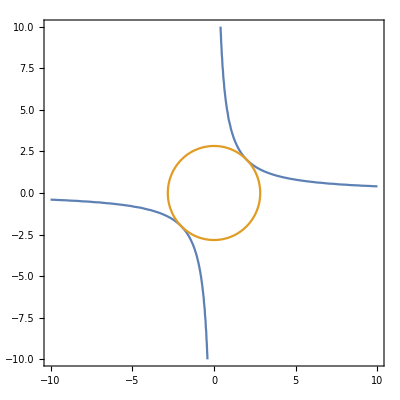

```mathematica
ContourPlot[{s*S==4,(1/2)(s^2+S^2)==4},{s,-10,10},{S,-10,10},Frame->True]
```

```mathematica
(eqs03EliminatedGB[testAlgebra]=FullSimplify/@GroebnerBasis[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{stS,s2pS2},{s,S},MonomialOrder->EliminationOrder])
```

{16 s2pS2 stS-4 stS b[0]+b[3] b[4]-b[2] b[5]+b[1] b[6]-4 s2pS2 b[7],16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[1]^2-b[2]^2-b[3]^2-b[4]^2-b[5]^2-b[6]^2-8 stS b[7],64 s2pS2^3-48 s2pS2^2 b[0]-(b[3] b[4]-b[2] b[5]+b[1] b[6]) (4 stS-b[7])+b[0] (b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+4 stS b[7])+s2pS2 (8 b[0]^2-4 (b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))}

The back substitution is. Note that in fact only two solutions exists (the sign of both s and S have to be the same.) Since √(s2pS2^2+ stS^2)>=s2pS2 the solutions 1 and 2 are complex and should be not taken into account

```mathematica
solsAndS[testAlgebra]=Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S}]//FullSimplify
```

Solving in the field of Reals confirms that just we have 2 real roots

```mathematica
Reduce[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{S,s},
Backsubstitution->True]
```

```mathematica
Reduce[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},
Backsubstitution->True]
```

(s==-√(s2pS2-√(s2pS2^2-stS^2))&&-√(s2pS2-√(s2pS2^2-stS^2))≠0&&S==-stS/(√(s2pS2-√(s2pS2^2-stS^2))))||(s==√(s2pS2-√(s2pS2^2-stS^2))&&√(s2pS2-√(s2pS2^2-stS^2))≠0&&S==stS/(√(s2pS2-√(s2pS2^2-stS^2))))||(s==-√(s2pS2+√(s2pS2^2-stS^2))&&-√(s2pS2+√(s2pS2^2-stS^2))≠0&&S==-stS/(√(s2pS2+√(s2pS2^2-stS^2))))||(s==√(s2pS2+√(s2pS2^2-stS^2))&&√(s2pS2+√(s2pS2^2-stS^2))≠0&&S==stS/(√(s2pS2+√(s2pS2^2-stS^2))))||(stS==0&&s==0&&S==-√2 √s2pS2)||(stS==0&&s==0&&S==√2 √s2pS2)

```mathematica
Reduce[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{S,s},
Backsubstitution->True]
```

(S==-√(s2pS2-√(s2pS2^2-stS^2))&&-√(s2pS2-√(s2pS2^2-stS^2))≠0&&s==-stS/(√(s2pS2-√(s2pS2^2-stS^2))))||(S==√(s2pS2-√(s2pS2^2-stS^2))&&√(s2pS2-√(s2pS2^2-stS^2))≠0&&s==stS/(√(s2pS2-√(s2pS2^2-stS^2))))||(S==-√(s2pS2+√(s2pS2^2-stS^2))&&-√(s2pS2+√(s2pS2^2-stS^2))≠0&&s==-stS/(√(s2pS2+√(s2pS2^2-stS^2))))||(S==√(s2pS2+√(s2pS2^2-stS^2))&&√(s2pS2+√(s2pS2^2-stS^2))≠0&&s==stS/(√(s2pS2+√(s2pS2^2-stS^2))))||(stS==0&&S==0&&s==-√2 √s2pS2)||(stS==0&&S==0&&s==√2 √s2pS2)

```mathematica
solsAndSRealssS[testAlgebra]=FullSimplify/@Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[-√2 √s2pS2,stS==0]},{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[√2 √s2pS2,stS==0]},{s→ConditionalExpression[-√(s2pS2-√(s2pS2^2-stS^2)),√(s2pS2-√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[-stS/(√(s2pS2-√(s2pS2^2-stS^2))),√(s2pS2-√(s2pS2^2-stS^2))≠0]},{s→ConditionalExpression[√(s2pS2-√(s2pS2^2-stS^2)),√(s2pS2-√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[stS/(√(s2pS2-√(s2pS2^2-stS^2))),√(s2pS2-√(s2pS2^2-stS^2))≠0]},{s→ConditionalExpression[-√(s2pS2+√(s2pS2^2-stS^2)),√(s2pS2+√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[-stS/(√(s2pS2+√(s2pS2^2-stS^2))),√(s2pS2+√(s2pS2^2-stS^2))≠0]},{s→ConditionalExpression[√(s2pS2+√(s2pS2^2-stS^2)),√(s2pS2+√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[stS/(√(s2pS2+√(s2pS2^2-stS^2))),√(s2pS2+√(s2pS2^2-stS^2))≠0]}}

Prepare for program

```mathematica
(solsAndSRealssS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{stS==0->zeroQ[stS],Sqrt[s2pS2-Sqrt[s2pS2^2-stS^2]]≠0->positiveQ[s2pS2-Sqrt[s2pS2^2-stS^2]],Sqrt[s2pS2+Sqrt[s2pS2^2-stS^2]]≠0->positiveQ[s2pS2+Sqrt[s2pS2^2-stS^2]]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]])], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[stS/Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]])], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[stS/Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]]}}

```mathematica
solsAndSRealssS[testAlgebra][[3]]
```

{s→ConditionalExpression[-√(s2pS2-√(s2pS2^2-stS^2)),√(s2pS2-√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[-stS/(√(s2pS2-√(s2pS2^2-stS^2))),√(s2pS2-√(s2pS2^2-stS^2))≠0]}

```mathematica
StringReplace[ToString[TeXForm[solsAndSRealssS[testAlgebra][[3]]/.{ConditionalExpression[a_,x_]:>a}]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{s\to -\sqrt{T-\sqrt{T^2-t^2}},S\to -\frac{t}{\sqrt{T-\sqrt{T^2-t^2}}}\right\}

The reduce answer is  usefull when analysing all cases (Solve reorders vars, in contrary, Reduce don’ reorder!)

```mathematica
FullSimplify/@Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},MaxExtraConditions->All]
```

```mathematica
FullSimplify/@Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},Method->"Reduce"]
```

The next answer is included in the article

```mathematica
solSsReduce[testAlgebra]=FullSimplify/@Reduce[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},Backsubstitution->True]
```

(s+√(s2pS2-√(s2pS2^2-stS^2))==0&&S+stS/(√(s2pS2-√(s2pS2^2-stS^2)))==0)||(√(s2pS2-√(s2pS2^2-stS^2))==s&&√(s2pS2-√(s2pS2^2-stS^2))≠0&&S==stS/(√(s2pS2-√(s2pS2^2-stS^2))))||(s+√(s2pS2+√(s2pS2^2-stS^2))==0&&S+stS/(√(s2pS2+√(s2pS2^2-stS^2)))==0)||(√(s2pS2+√(s2pS2^2-stS^2))==s&&√(s2pS2+√(s2pS2^2-stS^2))≠0&&S==stS/(√(s2pS2+√(s2pS2^2-stS^2))))||(stS==0&&s==0&&S+√2 √s2pS2==0)||(stS==0&&s==0&&S==√2 √s2pS2)

```mathematica
solSsSolveReduce[testAlgebra]=FullSimplify/@Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},Method->"Reduce"]
```

{{s→-√(s2pS2-√(s2pS2^2-stS^2)),S→-stS/(√(s2pS2-√((s2pS2-stS) (s2pS2+stS))))},{s→√(s2pS2-√(s2pS2^2-stS^2)),S→stS/(√(s2pS2-√((s2pS2-stS) (s2pS2+stS))))},{s→-√(s2pS2+√(s2pS2^2-stS^2)),S→-stS/(√(s2pS2+√((s2pS2-stS) (s2pS2+stS))))},{s→√(s2pS2+√(s2pS2^2-stS^2)),S→stS/(√(s2pS2+√((s2pS2-stS) (s2pS2+stS))))}}

```mathematica
solSsSolve[testAlgebra]=Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},MaxExtraConditions->All, VerifySolutions->True]
```

```mathematica
(sol03Eliminated[testAlgebra]=Solve[eqs03Eliminated[testAlgebra],{stS,s2pS2}])//Length
```

4

```mathematica
(sol03EliminatedGB[testAlgebra]=Solve[Thread[eqs03EliminatedGB[testAlgebra]==0],{stS,s2pS2}])//Length
```

4

```mathematica
LeafCount/@{sol03Eliminated[testAlgebra],sol03Eliminated[testAlgebra]}
```

{11229,11229}

Rewrite in coordinate free form. Evaluate this group

Noticing the following relations try to rewrite equation in coordinate free form from the beginning

```mathematica
b1
```

b[0]+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030+b[7] 123030

```mathematica
(gaGetMV[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra],{0}])//gaPE//Expand
```

-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

```mathematica
gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]
```

b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

```mathematica
detNorm[testAlgebra]=gaDeterminantNorm[b1]
```

-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2

bCCb0^2-bCCbI0^2 žemiau formulėse yra determinantas

```mathematica
Expand[gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]^2-gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]^2 -gaDeterminantNorm[b1]]
```

0

Determinant norm is always positive for cl03 as well !!!

```mathematica
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},detNorm[testAlgebra]<0],Reals]
```

False

```mathematica
(detTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];detNorm[testAlgebra]/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[detTable[testAlgebra],NonNegative]
```

True

```mathematica
explicitRulesbS=(bCCb0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
(testbbTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-1000,100}],Length[b1]]]];explicitRulesbS/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[testbbTable[testAlgebra],NonNegative]
```

True

```mathematica
explicitRulesb=(bCCb0-√(bCCb0^2-bCCbI0^2))/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
(testbbTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-1000,100}],Length[b1]]]];explicitRulesb/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[testbbTable[testAlgebra],NonNegative]
```

True

```mathematica
eqs03EliminatedGB[testAlgebra]
```

{16 s2pS2 stS-4 stS b[0]+b[3] b[4]-b[2] b[5]+b[1] b[6]-4 s2pS2 b[7],16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[1]^2-b[2]^2-b[3]^2-b[4]^2-b[5]^2-b[6]^2-8 stS b[7],64 s2pS2^3-48 s2pS2^2 b[0]-(b[3] b[4]-b[2] b[5]+b[1] b[6]) (4 stS-b[7])+b[0] (b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+4 stS b[7])+s2pS2 (8 b[0]^2-4 (b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))}

```mathematica
Thread[Equal[(Collect[#,{stS,s2pS2},FullSimplify]&/@eqs03EliminatedGB[testAlgebra]),0]]
```

{stS (16 s2pS2-4 b[0])+b[3] b[4]-b[2] b[5]+b[1] b[6]-4 s2pS2 b[7]==0,16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[1]^2-b[2]^2-b[3]^2-b[4]^2-b[5]^2-b[6]^2-8 stS b[7]==0,64 s2pS2^3-48 s2pS2^2 b[0]+b[0] (b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2)+(b[3] b[4]-b[2] b[5]+b[1] b[6]) b[7]+4 stS (-b[3] b[4]+b[2] b[5]-b[1] b[6]+b[0] b[7])+s2pS2 (8 b[0]^2-4 (b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))==0}

```mathematica
(eqs03EliminatedDimensionless[testAlgebra]=Eliminate[Join[Thread[Equal[(Collect[#,{stS,s2pS2},FullSimplify]&/@eqs03EliminatedGB[testAlgebra]),0]],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}])//AbsoluteTiming
```

{0.041878,bCCb0==16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2&&bCCbI0==32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7]}

To article

```mathematica
tryDenomZero[testAlgebra]=FullSimplify/@(Subtract@@@(List@@eqs03EliminatedDimensionless[testAlgebra]))
```

{bCCb0-(-4 s2pS2+b[0])^2-(-4 stS+b[7])^2,bCCbI0-2 (4 s2pS2-b[0]) (4 stS-b[7])}

```mathematica
(soltryDenomZero[testAlgebra]=Reduce[Thread[tryDenomZero[testAlgebra]==0],{stS,s2pS2},Backsubstitution->True])/.{bCCb0^2-bCCbI0^2->detb}
```

(bCCbI0==0&&stS==b[7]/4&&s2pS2==1/4 (-√bCCb0+b[0]))||(bCCbI0==0&&stS==b[7]/4&&s2pS2==1/4 (√bCCb0+b[0]))||(stS==1/8 (-√2 √(bCCb0-√detb)+2 b[7])&&-√(bCCb0-√detb)≠0&&s2pS2==(-bCCbI0+√2 √(bCCb0-√detb) b[0])/(4 √2 √(bCCb0-√detb)))||(stS==1/8 (√2 √(bCCb0-√detb)+2 b[7])&&√(bCCb0-√detb)≠0&&s2pS2==(bCCbI0+√2 √(bCCb0-√detb) b[0])/(4 √2 √(bCCb0-√detb)))||(stS==1/8 (-√2 √(bCCb0+√detb)+2 b[7])&&-√(bCCb0+√detb)≠0&&s2pS2==(-bCCbI0+√2 √(bCCb0+√detb) b[0])/(4 √2 √(bCCb0+√detb)))||(stS==1/8 (√2 √(bCCb0+√detb)+2 b[7])&&√(bCCb0+√detb)≠0&&s2pS2==(bCCbI0+√2 √(bCCb0+√detb) b[0])/(4 √2 √(bCCb0+√detb)))

```mathematica
(soltryDenomZero[testAlgebra]=Simplify/@Solve[Thread[tryDenomZero[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb}
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

```mathematica
(soltryDenomZero[testAlgebra][[3]]/.{bCCb0^2-bCCbI0^2->detb})
```

{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]}

```mathematica
stSAnds2pS2Vals=(soltryDenomZero[testAlgebra]/.{ConditionalExpression[a_,x_]:>a});
```

```mathematica
tt=(s2pS2-Sqrt[s2pS2^2-stS^2]/.(soltryDenomZero[testAlgebra]/.{ConditionalExpression[a_,x_]:>a}))
```

{1/4 (-√bCCb0+b[0])-√(1/16 (-√bCCb0+b[0])^2-b[7]^2/16),1/4 (√bCCb0+b[0])-√(1/16 (√bCCb0+b[0])^2-b[7]^2/16),1/8 (-(√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])-√(1/64 (-(√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 (-(√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2),1/8 ((√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])-√(1/64 ((√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 ((√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2),1/8 (-(√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])-√(1/64 (-(√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 (-(√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2),1/8 ((√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])-√(1/64 ((√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 ((√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2)}

```mathematica
((tt/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]})/.{b[1]->1,b[6]->-2})/.b[_]:>0
```

{-(√5)/2,0,-1/2-(√3)/4,1/2-(√3)/4,-1/4-(ⅈ √3)/4,1/4-(ⅈ √3)/4}

```mathematica
poSaknis3=tt[[3]]/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
```

```mathematica
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},poSaknis3<0],Reals]
```

```mathematica
poSaknis4=tt[[4]]/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
```

```mathematica
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},poSaknis4<0],Reals]
```

```mathematica
poSaknis5=tt[[5]]/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
```

```mathematica
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},poSaknis5>0],Reals]
```

```mathematica
poSaknis6=tt[[6]]/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
```

```mathematica
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},poSaknis6>0],Reals]
```

```mathematica
testCond=(tt[[{3,4,5,6}]]/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]})
```

{1/8 (2 b[0]-(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2-√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))-√(1/64 (2 b[0]-(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2-√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2-1/16 (b[7]-1/(√2)(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2-√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2),1/8 (2 b[0]+(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2-√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))-√(1/64 (2 b[0]+(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2-√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2-1/16 (b[7]+1/(√2)(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2-√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2),1/8 (2 b[0]-(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2+√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))-√(1/64 (2 b[0]-(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2+√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2-1/16 (b[7]-1/(√2)(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2+√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2),1/8 (2 b[0]+(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2+√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))-√(1/64 (2 b[0]+(√2 (-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]))/(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2+√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2-1/16 (b[7]+1/(√2)(√(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2+√(-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2)^2))))^2)}

```mathematica
(signTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];testCond/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[#[[1]]&/@signTable[testAlgebra],Element[#,Reals]&]
```

True

```mathematica
ttt=(s2pS2+Sqrt[s2pS2^2-stS^2]/.(soltryDenomZero[testAlgebra]/.{ConditionalExpression[a_,x_]:>a}))
```

{1/4 (-√bCCb0+b[0])+√(1/16 (-√bCCb0+b[0])^2-b[7]^2/16),1/4 (√bCCb0+b[0])+√(1/16 (√bCCb0+b[0])^2-b[7]^2/16),1/8 (-(√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])+√(1/64 (-(√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 (-(√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2),1/8 ((√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])+√(1/64 ((√2 bCCbI0)/(√(bCCb0-√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 ((√(bCCb0-√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2),1/8 (-(√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])+√(1/64 (-(√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 (-(√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2),1/8 ((√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])+√(1/64 ((√2 bCCbI0)/(√(bCCb0+√(bCCb0^2-bCCbI0^2)))+2 b[0])^2-1/16 ((√(bCCb0+√(bCCb0^2-bCCbI0^2)))/(√2)+b[7])^2)}

```mathematica
testCond2=(ttt[[{3,4,5,6}]]/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]});
```

```mathematica
(signTable2[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];testCond2/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[#[[3]]&/@signTable[testAlgebra],Element[#,Reals]&]
```

False

```mathematica
StringReplace[ToString[TeXForm[(soltryDenomZero[testAlgebra][[3]]/.{bCCb0^2-bCCbI0^2->detb})/.{ConditionalExpression[a_,x_]:>a}]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{t\to \frac{1}{4} \left(b_{123}-\frac{\sqrt{b_{S}-D}}{\sqrt{2}}\right),T\to \frac{1}{8} \left(2 b_{0}-\frac{\sqrt{2} b_{I}}{\sqrt{b_{S}-D}}\right)\right\}

```mathematica
(soltryDenomZero[testAlgebra]=Simplify/@Solve[Thread[tryDenomZero[testAlgebra]==0],{s2pS2,stS},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb}
```

{{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[-(√2 bCCb0 √(bCCb0-√detb)+√2 √(bCCb0-√detb) √detb-2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 bCCb0 √(bCCb0-√detb)+√2 √(bCCb0-√detb) √detb+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(-√2 bCCb0 √(bCCb0+√detb)+√2 √(bCCb0+√detb) √detb+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 bCCb0 √(bCCb0+√detb)-√2 √(bCCb0+√detb) √detb+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]}}

```mathematica
FullSimplify[#,TransformationFunctions->{Automatic,(#/.bCCb0^2-bCCbI0^2->detb)&}]&/@soltryDenomZero[testAlgebra]
```

{{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(-√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 (-bCCb0+√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 (bCCb0-√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]}}

```mathematica
(eqs03EliminatedGBDimensionless[testAlgebra]=GroebnerBasis[Join[eqs03EliminatedGB[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]-bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]-bCCbI0}],{stS,s2pS2},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder])//AbsoluteTiming
```

{0.031686,{-bCCbI0+32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7],-bCCb0+16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3+4 bCCbI0 stS+2 bCCb0 b[0]-96 s2pS2^2 b[0]+24 s2pS2 b[0]^2-2 b[0]^3-bCCbI0 b[7]}}

This is solution in case bCCbI0=0

```mathematica
Solve[Thread[(tryDenomZero/.{bCCbI0->0})==0],{stS,s2pS2}]
```

{}

{s2pS2,stS} ordering yields shorter and nicer results

```mathematica
(solFinalSolveNPForProgram[testAlgebra]=FullSimplify/@(Solve[Thread[GroebnerBasis[eqs03EliminatedGBDimensionless[testAlgebra],{s2pS2,stS}]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

Prepare to include into program

```mathematica
(solFinalSolveNPForProgram[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]//.{Sqrt[detb]->detSqrt,bCCbI0==0->zeroQ[bCCbI0],Sqrt[bCCb0-detSqrt]≠0->positiveQ[bCCb0-detSqrt],Sqrt[bCCb0+detSqrt]≠0->positiveQ[bCCb0+detSqrt]})})//InputForm
```

{{stS -> ConditionalExpression[takeMe[b[7]/4], zeroQ[bCCbI0]], 
  s2pS2 -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] + b[0])/4], zeroQ[bCCbI0]]}, 
 {stS -> ConditionalExpression[takeMe[b[7]/4], zeroQ[bCCbI0]], 
  s2pS2 -> ConditionalExpression[takeMe[(Sqrt[bCCb0] + b[0])/4], zeroQ[bCCbI0]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[bCCb0 - detSqrt]/Sqrt[2]) + b[7])/4], 
    positiveQ[bCCb0 - detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 - detSqrt]) + 2*b[0])/8], 
    positiveQ[bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[bCCb0 - detSqrt]/Sqrt[2] + b[7])/4], 
    positiveQ[bCCb0 - detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 - detSqrt] + 2*b[0])/8], 
    positiveQ[bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[bCCb0 + detSqrt]/Sqrt[2]) + b[7])/4], 
    positiveQ[bCCb0 + detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 + detSqrt]) + 2*b[0])/8], 
    positiveQ[bCCb0 + detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[bCCb0 + detSqrt]/Sqrt[2] + b[7])/4], 
    positiveQ[bCCb0 + detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 + detSqrt] + 2*b[0])/8], 
    positiveQ[bCCb0 + detSqrt]]}}

Toliau beveik nereikalinga medziaga.

Other variants (needs clearing)

```mathematica
(solFinalSolveNP[testAlgebra]=FullSimplify/@(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/(8 bCCbI0)(-√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (-bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]}}

```mathematica
(solFinalSolveNP[testAlgebra]=FullSimplify/@(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

For article

```mathematica
FullSimplify/@eqs03EliminatedGBDimensionless[testAlgebra]
```

{-bCCbI0+2 (4 s2pS2-b[0]) (4 stS-b[7]),-bCCb0+(-4 s2pS2+b[0])^2+(-4 stS+b[7])^2,2 (4 s2pS2-b[0])^3+2 bCCb0 (-4 s2pS2+b[0])+bCCbI0 (4 stS-b[7])}

```mathematica
StringReplace[ToString[TeXForm[FullSimplify[eqs03EliminatedGBDimensionless[testAlgebra]]]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

Since coefficients b[0] and b[7] enters sometimes as single coefficients it cannot probably be further simplified. Further simplification of expressions giving all assumptions about positivity of det and reality of coefficients do not yield simplification

```mathematica
(solFinalReduceMethod[testAlgebra]=FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},Method->"Reduce"])/.{bCCb0^2-bCCbI0^2->detb}
```

{{stS→1/4 (-(√(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))))/(√2)+b[7]),s2pS2→1/(8 bCCbI0)(-√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])},{stS→1/4 ((√(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))))/(√2)+b[7]),s2pS2→(√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 (-(√(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))))/(√2)+b[7]),s2pS2→1/(8 bCCbI0)(√2 (-bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])},{stS→1/4 ((√(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))))/(√2)+b[7]),s2pS2→(√2 (bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])/(8 bCCbI0)}}

The ebst representation is solFinalSolve[testAlgebra]

```mathematica
eqs03EliminatedGBDimensionless[testAlgebra]
```

{-bCCbI0+32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7],-bCCb0+16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3+4 bCCbI0 stS+2 bCCb0 b[0]-96 s2pS2^2 b[0]+24 s2pS2 b[0]^2-2 b[0]^3-bCCbI0 b[7]}

```mathematica
(solFinalSolve[testAlgebra]=((FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All, VerifySolutions->True]))/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/(8 bCCbI0)(-√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (-bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]}}

Prepare to include intu program

```mathematica
(solFinalSolve[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{Sqrt[detb]->detSqrt})})//InputForm
```

{{stS -> ConditionalExpression[takeMe[b[7]/4], bCCbI0 == 0 && Sqrt[bCCb0] != 0], 
  s2pS2 -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] + b[0])/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0]}, 
 {stS -> ConditionalExpression[takeMe[b[7]/4], bCCbI0 == 0 && Sqrt[bCCb0] != 0], 
  s2pS2 -> ConditionalExpression[takeMe[(Sqrt[bCCb0] + b[0])/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0]}, 
 {stS -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] + b[7])/4], bCCbI0 == 0], 
  s2pS2 -> ConditionalExpression[takeMe[b[0]/4], bCCbI0 == 0]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[bCCb0] + b[7])/4], bCCbI0 == 0], 
  s2pS2 -> ConditionalExpression[takeMe[b[0]/4], bCCbI0 == 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(-(Sqrt[2]*Sqrt[bCCb0 - Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]]*
         (bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)])) + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(-(Sqrt[bCCb0 - detSqrt]/Sqrt[2]) + b[0])/4], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*Sqrt[bCCb0 - Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]]*
        (bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]) + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(Sqrt[bCCb0 - detSqrt]/Sqrt[2] + b[0])/4], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*(-bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)])*
        Sqrt[bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]] + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(-(Sqrt[bCCb0 + detSqrt]/Sqrt[2]) + b[0])/4], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*(bCCb0 - Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)])*
        Sqrt[bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]] + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(Sqrt[bCCb0 + detSqrt]/Sqrt[2] + b[0])/4], bCCbI0 != 0]}}

If we remove last equation, the solution in general will  differ

```mathematica
(solFinalSolve[testAlgebra]=((FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},MaxExtraConditions->All, VerifySolutions->True]))/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

```mathematica
solFinalReduce[testAlgebra]=(Reduce[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},Backsubstitution->True]//FullSimplify)/.{bCCb0^2-bCCbI0^2->detb}
```

(bCCbI0==0&&4 stS==b[7]&&(√bCCb0+4 s2pS2==b[0]||√bCCb0+b[0]==4 s2pS2))||(√(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))≠0&&((8 s2pS2==(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]&&√2 √(bCCb0-√detb)+2 b[7]==8 stS)||((√2 bCCbI0)/(√(bCCb0-√detb))+8 s2pS2==2 b[0]&&√2 √(bCCb0-√detb)+8 stS==2 b[7])))||(√(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))≠0&&((8 s2pS2==(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]&&√2 √(bCCb0+√detb)+2 b[7]==8 stS)||((√2 bCCbI0)/(√(bCCb0+√detb))+8 s2pS2==2 b[0]&&√2 √(bCCb0+√detb)+8 stS==2 b[7])))

Solutions of the following two equations are the same as of the entire GB system. Below is an explicit check, suppress evaluation

```mathematica
(solFinalSolveNP[testAlgebra]=(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2}]//FullSimplify)/.{bCCb0^2-bCCbI0^2->detb})//LeafCount
```

```mathematica
((Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2}]//FullSimplify)/.{bCCb0^2-bCCbI0^2->detb})//LeafCount
```

In future we will use answer of solFinalSolve[testAlgebra] since it is more symmetric and covers all cases. This is final answer:

```mathematica
solFinalSolve[testAlgebra]
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

Special cl(0,3) case, when s == S and s == -S

Case s == S  and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030+b[7] 123030

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{2 s^2-b[0]-v[1]^2-v[2]^2-v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,-b[1]+2 s v[1]+2 s V[1]==0,-b[2]+2 s v[2]+2 s V[2]==0,-b[3]+2 s v[3]+2 s V[3]==0,-b[4]-2 s v[3]-2 s V[3]==0,-b[5]+2 s v[2]+2 s V[2]==0,-b[6]-2 s v[1]-2 s V[1]==0,2 s^2-b[7]-2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

When s=S somthing special happens: only half of v and V can be solved under special condition

```mathematica
solsvVRealsSeqPluss[testAlgebra]=Expand/@Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[b[1]/(2 s)-V[1],b[1]+b[6]==0&&b[2]==b[5]&&b[3]+b[4]==0&&s≠0],v[2]→ConditionalExpression[b[5]/(2 s)-V[2],b[1]+b[6]==0&&b[2]==b[5]&&b[3]+b[4]==0&&s≠0],v[3]→ConditionalExpression[-b[4]/(2 s)-V[3],b[1]+b[6]==0&&b[2]==b[5]&&b[3]+b[4]==0&&s≠0]}

```mathematica
solsvVRealsSeqPlussReduce[testAlgebra]=Reduce[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],V[1],v[2],v[3],V[2],V[3]},Reals]
```

(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0)||(b[1]==-b[6]&&((s<0&&b[3]==-b[4]&&b[2]==b[5]&&V[1]==(b[1]-2 s v[1])/(2 s))||(s>0&&b[3]==-b[4]&&b[2]==b[5]&&V[1]==(b[1]-2 s v[1])/(2 s)))&&V[2]==(b[2]-2 s v[2])/(2 s)&&V[3]==(b[3]-2 s v[3])/(2 s))

```mathematica
(solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[b[1]/(2*s) - V[1]], 
   b[1] + b[6] == 0 && b[2] == b[5] && b[3] + b[4] == 0 && nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[b[5]/(2*s) - V[2]], 
   b[1] + b[6] == 0 && b[2] == b[5] && b[3] + b[4] == 0 && nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[-b[4]/(2*s) - V[3]], 
   b[1] + b[6] == 0 && b[2] == b[5] && b[3] + b[4] == 0 && nonzeroQ[s]]}

```mathematica
solsvVRealsSeqPluss[testAlgebra]
```

{v[1]→ConditionalExpression[b[1]/(2 s)-V[1],b[1]+b[6]==0&&b[2]==b[5]&&b[3]+b[4]==0&&s≠0],v[2]→ConditionalExpression[b[5]/(2 s)-V[2],b[1]+b[6]==0&&b[2]==b[5]&&b[3]+b[4]==0&&s≠0],v[3]→ConditionalExpression[-b[4]/(2 s)-V[3],b[1]+b[6]==0&&b[2]==b[5]&&b[3]+b[4]==0&&s≠0]}

```mathematica
StringReplace[ToString[TeXForm[solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>a}]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{v_{1}\to \frac{b_{1}}{2 s}-V_{1},v_{2}\to \frac{b_{13}}{2 s}-V_{2},v_{3}\to -\frac{b_{12}}{2 s}-V_{3}\right\}

```mathematica
eqsS0FL[testAlgebra]=DeleteCases[(eqsS0[testAlgebra]/.{b[6]->-b[1],b[5]->b[2],b[4]->-b[3]})/.(solsvVRealsSeqPluss[testAlgebra]/.ConditionalExpression[ex_,_]:>(ex/.{b[6]->-b[1],b[5]->b[2],b[4]->-b[3]}))//Expand,True]
```

{2 s^2-b[0]-b[1]^2/(4 s^2)-b[2]^2/(4 s^2)-b[3]^2/(4 s^2)+(b[1] V[1])/s-2 V[1]^2+(b[2] V[2])/s-2 V[2]^2+(b[3] V[3])/s-2 V[3]^2==0,2 s^2-b[7]-(b[1] V[1])/s+2 V[1]^2-(b[2] V[2])/s+2 V[2]^2-(b[3] V[3])/s+2 V[3]^2==0}

```mathematica
StringReplace[ToString[TeXForm[eqsS0FL[testAlgebra]/.{ConditionalExpression[a_,x_]:>a}]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{-\frac{b_{1}^2}{4 s^2}-\frac{b_{2}^2}{4 s^2}-\frac{b_{3}^2}{4 s^2}+\frac{b_{1} V_{1}}{s}+\frac{b_{2} V_{2}}{s}+\frac{b_{3} V_{3}}{s}-b_{0}+2 s^2-2 V_{1}^2-2 V_{2}^2-2 V_{3}^2=0,-\frac{b_{1} V_{1}}{s}-\frac{b_{2} V_{2}}{s}-\frac{b_{3} V_{3}}{s}-b_{123}+2 s^2+2 V_{1}^2+2 V_{2}^2+2 V_{3}^2=0\right\}

Now if we try to eliminate additional free parameter, then all free parameters get eliminated! and we are left with the condition: Better to do it manually as is shown below

```mathematica
(eqsS0FLNoS[testAlgebra]=GroebnerBasis[eqsS0FL[testAlgebra],{V[1],V[2],V[3]},{s},MonomialOrder->EliminationOrder])//Length
```

1

Alternative (yields same complexity, not used

```mathematica
eqsS0FLOposite[testAlgebra]=DeleteCases[(eqsS0[testAlgebra]/.{b[1]->-b[6],b[2]->b[5],b[3]->-b[4]})/.(solsvVRealsSeqPluss[testAlgebra]/.ConditionalExpression[ex_,_]:>(ex/.{b[1]->-b[6],b[2]->b[5],b[3]->-b[4]}))//Expand,True]
```

{2 s^2-b[0]-b[4]^2/(4 s^2)-b[5]^2/(4 s^2)-b[6]^2/(4 s^2)-(b[6] V[1])/s-2 V[1]^2+(b[5] V[2])/s-2 V[2]^2-(b[4] V[3])/s-2 V[3]^2==0,2 s^2-b[7]+(b[6] V[1])/s+2 V[1]^2-(b[5] V[2])/s+2 V[2]^2+(b[4] V[3])/s+2 V[3]^2==0}

```mathematica
(eqsS0FLNoSOposite[testAlgebra]=GroebnerBasis[eqsS0FLOposite[testAlgebra],{V[1],V[2],V[3]},{s},MonomialOrder->EliminationOrder])//Length
```

1

```mathematica
bBiv=gaGetMV[b1,{2}];
```

```mathematica
eqsS0FLNoSOpositeGB=GroebnerBasis[Join[eqsS0FLNoSOposite[testAlgebra],{gaPE[V1\[InnerProduct]V1]-V2,(gaPE[bBiv\[InnerProduct]bBiv])-bBiv2,(b[6] V[1]-b[5] V[2]+b[4] V[3])-bBivV}],{V2,bBivV,bBiv2},{V[1],V[2],V[3]},MonomialOrder->EliminationOrder][[2]]
```

```mathematica
eqsS0FLNoSGB=GroebnerBasis[Join[eqsS0FLNoS[testAlgebra],{gaPE[V1\[InnerProduct]V1]-V2,(gaPE[v1\[InnerProduct]V1]/.{v[1]->b[1],v[2]->b[2],v[3]->b[3]})-bV,(gaPE[v1\[InnerProduct]v1]/.{v[1]->b[1],v[2]->b[2],v[3]->b[3]})-b2}],{V2,bV,b2},{V[1],V[2],V[3]},MonomialOrder->EliminationOrder][[2]]
```

b2^3+256 bV^4-256 b2 bV^2 V2+32 b2^2 V2^2+256 b2 V2^4+48 b2 bV^2 b[0]-8 b2^2 V2 b[0]-256 bV^2 V2^2 b[0]-128 b2 V2^3 b[0]+128 bV^2 V2 b[0]^2+16 b2 V2^2 b[0]^2-16 bV^2 b[0]^3-80 b2 bV^2 b[7]+24 b2^2 V2 b[7]-256 bV^2 V2^2 b[7]+384 b2 V2^3 b[7]-4 b2^2 b[0] b[7]-160 b2 V2^2 b[0] b[7]+16 bV^2 b[0]^2 b[7]+16 b2 V2 b[0]^2 b[7]+4 b2^2 b[7]^2-128 bV^2 V2 b[7]^2+208 b2 V2^2 b[7]^2+16 bV^2 b[0] b[7]^2-64 b2 V2 b[0] b[7]^2+4 b2 b[0]^2 b[7]^2-16 bV^2 b[7]^3+48 b2 V2 b[7]^3-8 b2 b[0] b[7]^3+4 b2 b[7]^4

This is final relation between V[1] ,V[2] and V[3], with V2=-V[1]^2-V[2]^2-V[3]^2; bV=-b[1] V[1]-b[2] V[2]-b[3] V[3]; b2=-b[1]^2-b[2]^2-b[3]^2

```mathematica
freeCoefficientCondition[testAlgebra]=(Collect[eqsS0FLNoSGB,bV,FullSimplify]/.(16 V2-3 b[0]+5 b[7])->4( 4V2- b[0]+ b[7])+b[7]+b[0])
```

256 bV^4+b2 (b2+2 (2 V2+b[7]) (4 V2-b[0]+b[7]))^2-16 bV^2 ((4 V2-b[0]+b[7])^2 (b[0]+b[7])+b2 (b[0]+b[7]+4 (4 V2-b[0]+b[7])))

It is possible to obtain simple condition with manual manipulation

```mathematica
{lhs1,lhs2}=First/@eqsS0FL[testAlgebra]
```

{2 s^2-b[0]-b[1]^2/(4 s^2)-b[2]^2/(4 s^2)-b[3]^2/(4 s^2)+(b[1] V[1])/s-2 V[1]^2+(b[2] V[2])/s-2 V[2]^2+(b[3] V[3])/s-2 V[3]^2,2 s^2-b[7]-(b[1] V[1])/s+2 V[1]^2-(b[2] V[2])/s+2 V[2]^2-(b[3] V[3])/s+2 V[3]^2}

```mathematica
{eqA1,eqA2}=({lhs1-lhs2,lhs1+lhs2}//FullSimplify)/.{b[1]^2+b[2]^2+b[3]^2->bbbp2}
```

{-(bbbp2-8 s (b[1] V[1]+b[2] V[2]+b[3] V[3])+4 s^2 (b[0]-b[7]+4 (V[1]^2+V[2]^2+V[3]^2)))/(4 s^2),-(bbbp2+4 s^2 (-4 s^2+b[0]+b[7]))/(4 s^2)}

```mathematica
StringReplace[ToString[TeXForm[eqA1/.{ConditionalExpression[a_,x_]:>a}]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

-\frac{4 s^2 \left(b_{0}-b_{123}+4 \left(V_{1}^2+V_{2}^2+V_{3}^2\right)\right)-8 s (b_{1} V_{1}+b_{2} V_{2}+b_{3} V_{3})+\text{bbbp2}}{4 s^2}

```mathematica
{lhs1-lhs2,lhs1+lhs2}//FullSimplify
```

{-(b[1]^2+b[2]^2+b[3]^2-8 s (b[1] V[1]+b[2] V[2]+b[3] V[3])+4 s^2 (b[0]-b[7]+4 (V[1]^2+V[2]^2+V[3]^2)))/(4 s^2),-(b[1]^2+b[2]^2+b[3]^2+4 s^2 (-4 s^2+b[0]+b[7]))/(4 s^2)}

```mathematica
StringReplace[ToString[TeXForm[{lhs1-lhs2,lhs1+lhs2}//FullSimplify]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{-\frac{4 s^2 \left(b_{0}-b_{123}+4 \left(V_{1}^2+V_{2}^2+V_{3}^2\right)\right)-8 s (b_{1} V_{1}+b_{2} V_{2}+b_{3} V_{3})+b_{1}^2+b_{2}^2+b_{3}^2}{4 s^2},-\frac{4 s^2 \left(b_{0}+b_{123}-4 s^2\right)+b_{1}^2+b_{2}^2+b_{3}^2}{4 s^2}\right\}

```mathematica
v1\[InnerProduct]v1//gaPE
```

-v[1]^2-v[2]^2-v[3]^2

We express b[1--3] using bCCb0 (can use also bCCbI0)

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->-b[1],b[5]->b[2],b[4]->-b[3]}
```

{b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2+b[7]^2==bCCb0,2 b[1]^2+2 b[2]^2+2 b[3]^2+2 b[0] b[7]==bCCbI0}

```mathematica
solAlt=Eliminate[Join[{lhs1+lhs2==0},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}][[1]]/.Equal->Rule
```

bCCb0→32 s^4-8 s^2 b[0]+b[0]^2-8 s^2 b[7]+b[7]^2

```mathematica
bbbp2TobCCb0=Solve[(relations[testAlgebra][[1]]//FullSimplify)/.{b[1]^2+b[2]^2+b[3]^2->bbbp2},bbbp2][[1]]
```

{bbbp2→1/2 (bCCb0-b[0]^2-b[7]^2)}

solV1Alt is preffered since is s^2 inside sqrt. For s<0 solutions interchanges. (If we eliminate bbbp2 in the first eq and then solve we obtain s^4 equation, which will yield more complex expression)

```mathematica
solV1Alt=FullSimplify[Solve[(eqA1/.bbbp2TobCCb0//FullSimplify)==0,V[1]],Assumptions->s>0]
```

{{V[1]→1/(8 s)(2 b[1]-√2 √(-bCCb0+b[0]^2+2 b[1]^2+b[7]^2+16 s (b[2] V[2]+b[3] V[3])-8 s^2 (b[0]-b[7]+4 (V[2]^2+V[3]^2))))},{V[1]→1/(8 s)(2 b[1]+√2 √(-bCCb0+b[0]^2+2 b[1]^2+b[7]^2+16 s (b[2] V[2]+b[3] V[3])-8 s^2 (b[0]-b[7]+4 (V[2]^2+V[3]^2))))}}

When we substitute the solution of s into V[1] we obtain the final formula we seek

```mathematica
solV1Alt[[1]]//InputForm
```

{V[1] -> (2*b[1] - Sqrt[2]*Sqrt[-bCCb0 + b[0]^2 + 2*b[1]^2 + b[7]^2 + 
       16*s*(b[2]*V[2] + b[3]*V[3]) - 8*s^2*(b[0] - b[7] + 4*(V[2]^2 + V[3]^2))])/
   (8*s)}

```mathematica
StringReplace[ToString[TeXForm[solV1Alt[[1]]]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{V_{1}\to \frac{2 b_{1}-\sqrt{2} \sqrt{-8 s^2 \left(b_{0}-b_{123}+4 \left(V_{2}^2+V_{3}^2\right)\right)+16 s (b_{2} V_{2}+b_{3} V_{3})+b_{0}^2+2 b_{1}^2+b_{123}^2-b_{S}}}{8 s}\right\}

Now we solve for s

```mathematica
eqsS0FLElimV[testAlgebra]=Eliminate[eqsS0FL[testAlgebra],V[1]]
```

4 b[7]==16 s^2-4 b[0]-b[1]^2/s^2-b[2]^2/s^2-b[3]^2/s^2&&s≠0

```mathematica
Subtract@@eqsS0FLElimV[testAlgebra][[1]]
```

-16 s^2+4 b[0]+b[1]^2/s^2+b[2]^2/s^2+b[3]^2/s^2+4 b[7]

```mathematica
(eqA2/.{bbbp2->b[1]^2+b[2]^2+b[3]^2})//Simplify
```

-(b[1]^2+b[2]^2+b[3]^2+4 s^2 (-4 s^2+b[0]+b[7]))/(4 s^2)

```mathematica
-4*%-%%//Simplify
```

0

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->-b[1],b[5]->b[2],b[4]->-b[3]}
```

{b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2+b[7]^2==bCCb0,2 b[1]^2+2 b[2]^2+2 b[3]^2+2 b[0] b[7]==bCCbI0}

```mathematica
eqsS0FLElimVNob[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}]
```

bCCb0==32 s^4-8 s^2 b[0]+b[0]^2-8 s^2 b[7]+b[7]^2&&s≠0

```mathematica
eqsS0FLElimVNobOther[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[2]]}],{b[1],b[2],b[3]}]
```

bCCbI0==32 s^4-8 s^2 b[0]-8 s^2 b[7]+2 b[0] b[7]&&s≠0

```mathematica
StringReplace[ToString[TeXForm[eqsS0FLElimVNob[testAlgebra]]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

b_{S}=-8 b_{0} s^2-8 b_{123} s^2+b_{0}^2+b_{123}^2+32 s^4\land s\neq 0

```mathematica
solsPos=Simplify/@Solve[eqsS0FLElimVNob[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]+√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]+√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]}}

For article && program

```mathematica
solsPos//InputForm
```

{{s -> ConditionalExpression[-Sqrt[b[0] - Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] - Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] - Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] - Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[-Sqrt[b[0] + Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] + Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] + Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] + Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}}

```mathematica
solsPos[[1]]/.{ConditionalExpression[a_,x_]:>a}
```

{s→-(√(b[0]-√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2)}

```mathematica
StringReplace[ToString[TeXForm[solsPos[[1]]/.{ConditionalExpression[a_,x_]:>a}]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}","v(1)"->"v_{1}","v(2)"->"v_{2}","v(3)"->"v_{3}","V(1)"->"V_{1}","V(2)"->"V_{2}","V(3)"->"V_{3}","\\sqrt{\\text{detb}}"->"D"}]
```

\left\{s\to -\frac{\sqrt{-\sqrt{2 b_{S}-(b_{0}-b_{123})^2}+b_{0}+b_{123}}}{2 \sqrt{2}}\right\}

```mathematica
testCond=(((s/.solsPos)/.{ConditionalExpression[a_,x_]:>a})/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]})
```

{-(√(b[0]+b[7]-√(-(b[0]-b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2),(√(b[0]+b[7]-√(-(b[0]-b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2),-(√(b[0]+b[7]+√(-(b[0]-b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2),(√(b[0]+b[7]+√(-(b[0]-b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2)}

```mathematica
(signTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];testCond/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[#[[4]]&/@signTable[testAlgebra],Element[#,Reals]&]
```

True

```mathematica
eqsS0FLElimCondition[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],s}]
```

bCCb0-(b[0]-b[7])^2==bCCbI0

```mathematica
test2=eqsS0FLElimCondition[testAlgebra]/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->-b[1],b[5]->b[2],b[4]->-b[3]}
```

b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2-(b[0]-b[7])^2+b[7]^2==2 b[1]^2+2 b[2]^2+2 b[3]^2+2 b[0] b[7]

```mathematica
(signTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];test2/.testNumRules[testAlgebra],{1000}])])//Length
```

1

```mathematica
Simplify/@Solve[eqsS0FLElimVNobOther[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]+√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]+√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]}}

Case s == -S  and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->-s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030+b[7] 123030

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{2 s^2-b[0]-v[1]^2-v[2]^2-v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,-b[1]+2 s v[1]-2 s V[1]==0,-b[2]+2 s v[2]-2 s V[2]==0,-b[3]+2 s v[3]-2 s V[3]==0,-b[4]+2 s v[3]-2 s V[3]==0,-b[5]-2 s v[2]+2 s V[2]==0,-b[6]+2 s v[1]-2 s V[1]==0,-2 s^2-b[7]-2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

When s=±S somthing special happens: only half of v and V can be solved under special condition

```mathematica
solsvVRealsSeqPluss[testAlgebra]=Expand/@Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[b[6]/(2 s)+V[1],b[1]==b[6]&&b[2]+b[5]==0&&b[3]==b[4]&&s≠0],v[2]→ConditionalExpression[b[2]/(2 s)+V[2],b[1]==b[6]&&b[2]+b[5]==0&&b[3]==b[4]&&s≠0],v[3]→ConditionalExpression[b[4]/(2 s)+V[3],b[1]==b[6]&&b[2]+b[5]==0&&b[3]==b[4]&&s≠0]}

```mathematica
solsvVRealsSeqPlussReduce[testAlgebra]=Reduce[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],V[1],v[2],v[3],V[2],V[3]},Reals]
```

(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0)||(b[1]==b[6]&&((s<0&&b[3]==b[4]&&b[2]==-b[5]&&V[1]==(-b[6]+2 s v[1])/(2 s))||(s>0&&b[3]==b[4]&&b[2]==-b[5]&&V[1]==(-b[6]+2 s v[1])/(2 s)))&&V[2]==-(b[2]-2 s v[2])/(2 s)&&V[3]==-(b[3]-2 s v[3])/(2 s))

```mathematica
(solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[b[6]/(2*s) + V[1]], 
   b[1] == b[6] && b[2] + b[5] == 0 && b[3] == b[4] && nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[b[2]/(2*s) + V[2]], 
   b[1] == b[6] && b[2] + b[5] == 0 && b[3] == b[4] && nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[b[4]/(2*s) + V[3]], 
   b[1] == b[6] && b[2] + b[5] == 0 && b[3] == b[4] && nonzeroQ[s]]}

```mathematica
eqsS0FL[testAlgebra]=DeleteCases[(eqsS0[testAlgebra]/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]})/.(solsvVRealsSeqPluss[testAlgebra]/.ConditionalExpression[ex_,_]:>(ex/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]}))//Expand,True]
```

{2 s^2-b[0]-b[1]^2/(4 s^2)-b[2]^2/(4 s^2)-b[3]^2/(4 s^2)-(b[1] V[1])/s-2 V[1]^2-(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s-2 V[3]^2==0,-2 s^2-b[7]-(b[1] V[1])/s-2 V[1]^2-(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s-2 V[3]^2==0}

It is possible to obtain simple condition with manual manipulation

```mathematica
{lhs1,lhs2}=First/@eqsS0FL[testAlgebra]
```

{2 s^2-b[0]-b[1]^2/(4 s^2)-b[2]^2/(4 s^2)-b[3]^2/(4 s^2)-(b[1] V[1])/s-2 V[1]^2-(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s-2 V[3]^2,-2 s^2-b[7]-(b[1] V[1])/s-2 V[1]^2-(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s-2 V[3]^2}

```mathematica
{eqA1,eqA2}=({lhs1-lhs2,lhs1+lhs2}//FullSimplify)/.{b[1]^2+b[2]^2+b[3]^2->bbbp2}
```

{-(bbbp2-4 s^2 (4 s^2-b[0]+b[7]))/(4 s^2),-(bbbp2+8 s (b[1] V[1]+b[2] V[2]+b[3] V[3])+4 s^2 (b[0]+b[7]+4 (V[1]^2+V[2]^2+V[3]^2)))/(4 s^2)}

We express b[1--3] using bCCb0 (can use also bCCbI0)

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]}
```

{b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2+b[7]^2==bCCb0,-2 b[1]^2-2 b[2]^2-2 b[3]^2+2 b[0] b[7]==bCCbI0}

```mathematica
solAlt=Eliminate[Join[{lhs1-lhs2==0},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}][[1]]/.Equal->Rule
```

bCCb0→32 s^4-8 s^2 b[0]+b[0]^2+8 s^2 b[7]+b[7]^2

```mathematica
bbbp2TobCCb0=Solve[(relations[testAlgebra][[1]]//FullSimplify)/.{b[1]^2+b[2]^2+b[3]^2->bbbp2},bbbp2][[1]]
```

{bbbp2→1/2 (bCCb0-b[0]^2-b[7]^2)}

For s<0 solutions interchanges. (If we eliminate bbbp2 in the first eq and then solve we obtain s^4 equation, which will yield more complex expression)

```mathematica
solV1Alt=FullSimplify[Solve[(eqA2/.bbbp2TobCCb0//FullSimplify)==0,V[1]],Assumptions->s>0]
```

{{V[1]→-1/(8 s)(2 b[1]+√2 √(-bCCb0+b[0]^2+2 b[1]^2+b[7]^2-16 s (b[2] V[2]+b[3] V[3])-8 s^2 (b[0]+b[7]+4 (V[2]^2+V[3]^2))))},{V[1]→1/(8 s)(-2 b[1]+√2 √(-bCCb0+b[0]^2+2 b[1]^2+b[7]^2-16 s (b[2] V[2]+b[3] V[3])-8 s^2 (b[0]+b[7]+4 (V[2]^2+V[3]^2))))}}

When we substitute the solution of s into V[1] we obtain the final formula we seek

```mathematica
solV1Alt[[2]]//InputForm
```

{V[1] -> (-2*b[1] + Sqrt[2]*Sqrt[-bCCb0 + b[0]^2 + 2*b[1]^2 + b[7]^2 - 
       16*s*(b[2]*V[2] + b[3]*V[3]) - 8*s^2*(b[0] + b[7] + 4*(V[2]^2 + V[3]^2))])/
   (8*s)}

Now we solve for s

```mathematica
eqsS0FL[testAlgebra]
```

{2 s^2-b[0]-b[1]^2/(4 s^2)-b[2]^2/(4 s^2)-b[3]^2/(4 s^2)-(b[1] V[1])/s-2 V[1]^2-(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s-2 V[3]^2==0,-2 s^2-b[7]-(b[1] V[1])/s-2 V[1]^2-(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s-2 V[3]^2==0}

Now we solve for s

```mathematica
eqsS0FLElimV[testAlgebra]=Eliminate[eqsS0FL[testAlgebra],V[1]]
```

4 b[7]==-16 s^2+4 b[0]+b[1]^2/s^2+b[2]^2/s^2+b[3]^2/s^2&&s≠0

```mathematica
eqsS0FLElimVNob[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}]
```

bCCb0==32 s^4-8 s^2 b[0]+b[0]^2+8 s^2 b[7]+b[7]^2&&s≠0

```mathematica
eqsS0FLElimVNobOther[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[2]]}],{b[1],b[2],b[3]}]
```

bCCbI0==-32 s^4+8 s^2 b[0]-8 s^2 b[7]+2 b[0] b[7]&&s≠0

```mathematica
solsNeg=Simplify/@Solve[eqsS0FLElimVNob[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-b[7]-√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]-√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-b[7]-√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]-√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]-b[7]+√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]+√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-b[7]+√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]+√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]}}

```mathematica
testCondNeg=(((s/.solsNeg)/.{ConditionalExpression[a_,x_]:>a})/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]})
```

{-(√(b[0]-b[7]-√(-(b[0]+b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2),(√(b[0]-b[7]-√(-(b[0]+b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2),-(√(b[0]-b[7]+√(-(b[0]+b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2),(√(b[0]-b[7]+√(-(b[0]+b[7])^2+2 (b[0]^2+b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+b[7]^2))))/(2 √2)}

```mathematica
(signTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];testCondNeg/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[#[[3]]&/@signTable[testAlgebra],Element[#,Reals]&]
```

True

```mathematica
solsNeg[[3]]
```

{s→ConditionalExpression[-(√(b[0]-b[7]+√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]+√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]}

For article && program

```mathematica
solsNeg//InputForm
```

{{s -> ConditionalExpression[-Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[-Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}}

```mathematica
eqsS0FLElimCondition[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],s}]
```

-bCCb0+(b[0]+b[7])^2==bCCbI0

```mathematica
Simplify/@Solve[eqsS0FLElimVNobOther[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]+√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]+√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]}}

Case s == S==0, here v,V cannot be solved

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[v1 +(V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030+b[7] 123030

```mathematica
{v1\[InnerProduct]v1//gaPE,V1\[InnerProduct]V1//gaPE,v1\[InnerProduct]V1//gaPE}
```

{-v[1]^2-v[2]^2-v[3]^2,-V[1]^2-V[2]^2-V[3]^2,-v[1] V[1]-v[2] V[2]-v[3] V[3]}

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]-v[1]^2-v[2]^2-v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,-b[1]==0,-b[2]==0,-b[3]==0,-b[4]==0,-b[5]==0,-b[6]==0,-b[7]-2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

```mathematica
vsol0=FullSimplify/@Solve[eqsS0[testAlgebra][[{1,8}]],{v[1],V[1]}]
```

{{v[1]→-1/(√2)(√(-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-√(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2))),V[1]→(b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-√(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2)))},{v[1]→1/(√2)(√(-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-√(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2))),V[1]→-((b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-√(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2))))},{v[1]→-1/(√2)(√(-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2+√(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2))),V[1]→(b[7]+2 v[2] V[2]+2 v[3] V[3])/(√(-2 b[0]-2 (v[2]^2+v[3]^2+V[2]^2+V[3]^2)+2 √(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2)))},{v[1]→1/(√2)(√(-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2+√(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2))),V[1]→-((b[7]+2 v[2] V[2]+2 v[3] V[3])/(√(-2 b[0]-2 (v[2]^2+v[3]^2+V[2]^2+V[3]^2)+2 √(-(b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2))))}}

```mathematica
vsol0[[4]]//InputForm
```

{v[1] -> Sqrt[-b[0] - v[2]^2 - v[3]^2 - V[2]^2 - V[3]^2 + 
     Sqrt[-(b[7] + 2*v[2]*V[2] + 2*v[3]*V[3])^2 + 
       (b[0] + v[2]^2 + v[3]^2 + V[2]^2 + V[3]^2)^2]]/Sqrt[2], 
 V[1] -> -((b[7] + 2*v[2]*V[2] + 2*v[3]*V[3])/
    Sqrt[-2*b[0] - 2*(v[2]^2 + v[3]^2 + V[2]^2 + V[3]^2) + 
      2*Sqrt[-(b[7] + 2*v[2]*V[2] + 2*v[3]*V[3])^2 + 
         (b[0] + v[2]^2 + v[3]^2 + V[2]^2 + V[3]^2)^2]])}

We can’t solve vectors  v and V in this case

Test if we can solve for 𝕖_1+𝕖_{1,2} (which fails with the method below) It fails also here, however for 𝕖_1 solution exists, and is found by general coefficients

```mathematica
eqsS0Spec[testAlgebra]=eqsS0[testAlgebra]/.Join[Thread[{b[0],b[2],b[3],b[5],b[6],b[7]}->0],{b[1]->1,b[4]->1}]
```

{-v[1]^2-v[2]^2-v[3]^2-V[1]^2-V[2]^2-V[3]^2==0,False,True,True,False,True,True,-2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

```mathematica
Solve[eqsS0Spec[testAlgebra],{s,v[1],v[2],v[3],V[1],V[2],V[3]},VerifySolutions->True,MaxExtraConditions->All]
```

{}

Eliminate {b[1],b[2],b[3],b[4],b[5],b[6]} in terms of bCCb0 and bCCbI0

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0}
```

{b[0]^2+b[7]^2==bCCb0,2 b[0] b[7]==bCCbI0}

```mathematica
eqsS0Elimb16[testAlgebra]=GroebnerBasis[Join[eqsS0[testAlgebra],relations[testAlgebra]],{b[0],b[7]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder]//FullSimplify
```

{b[7]+2 (v[1] V[1]+v[2] V[2]+v[3] V[3]),b[0]+v[1]^2+v[2]^2+v[3]^2+V[1]^2+V[2]^2+V[3]^2,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,-b[7] v[1]+2 V[1] (b[0]+v[2]^2+v[3]^2+V[1]^2)-2 v[1] (v[2] V[2]+v[3] V[3])+2 V[1] (V[2]^2+V[3]^2),bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3}

Eliminate {v[1],v[2],v[3],V[1],V[2],V[3]} in terms of v1\[InnerProduct]V1=v[1] V[1]+v[2] V[2]+v[3] V[3] (the scalar produc). It is suprize that we do not need other components.  In the end we compute Groebner basis with respect to remaining vars s, and free params. The first equation, then yields a condition when the solution exists (has no vars).

```mathematica
eqsS0Elimb16AndVv[testAlgebra]=FullSimplify/@GroebnerBasis[GroebnerBasis[Join[eqsS0Elimb16[testAlgebra],{gaPE[v1\[InnerProduct]V1]-v1V2ip,gaPE[v1\[InnerProduct]v1+V1\[InnerProduct]V1]-v2mV2}],{v1V2ip,v2mV2},{v[1],v[2],v[3],V[1],V[2],V[3]},MonomialOrder->EliminationOrder],{v1V2ip,v2mV2}]
```

{bCCbI0^2-4 bCCb0 b[7]^2+4 b[7]^4,bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,v2mV2-b[0],2 v1V2ip-b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCb0,bCCbI0,b[0],b[7]}]
```

{bCCbI0-2 b[0] b[7],bCCb0-b[0]^2-b[7]^2}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCbI0,bCCb0,b[0],b[7]}]
```

{bCCb0-b[0]^2-b[7]^2,bCCbI0-2 b[0] b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCbI0,bCCb0,b[7],b[0]}]
```

{bCCb0-b[0]^2-b[7]^2,bCCbI0-2 b[0] b[7]}

In fact we do not need to know substitution of v V the above is superfluous.

```mathematica
eqsS0Elimb16[testAlgebra]
```

{b[7]+2 (v[1] V[1]+v[2] V[2]+v[3] V[3]),b[0]+v[1]^2+v[2]^2+v[3]^2+V[1]^2+V[2]^2+V[3]^2,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,-b[7] v[1]+2 V[1] (b[0]+v[2]^2+v[3]^2+V[1]^2)-2 v[1] (v[2] V[2]+v[3] V[3])+2 V[1] (V[2]^2+V[3]^2),bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3}

```mathematica
GroebnerBasis[eqsS0Elimb16[testAlgebra][[{3,4,5}]],{bCCb0,bCCbI0,b[0],b[7]}]
```

{-b[7] v[1]+2 b[0] V[1]+2 v[2]^2 V[1]+2 v[3]^2 V[1]+2 V[1]^3-2 v[1] v[2] V[2]+2 V[1] V[2]^2-2 v[1] v[3] V[3]+2 V[1] V[3]^2,bCCbI0-2 b[0] b[7],bCCb0-b[0]^2-b[7]^2}

The rest is of subsections is not used

```mathematica
(gbSReduceComplexSolveZero=(Solve[Thread[eqsS0Elimb16AndVv[testAlgebra]==0],{v1V2ip,v2mV2},Reals,VerifySolutions->True,MaxExtraConditions->All]))//Length
```

1

```mathematica
gbSReduceComplexSolveZero
```

{{v1V2ip→ConditionalExpression[b[7]/2,(bCCb0-b[0]^2-b[7]^2==0&&bCCbI0==0&&b[7]==0)||(b[7]>0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)||(b[7]<0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)],v2mV2→ConditionalExpression[b[0],(bCCb0-b[0]^2-b[7]^2==0&&bCCbI0==0&&b[7]==0)||(b[7]>0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)||(b[7]<0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)]}}

Geometrically it means that we have fixed difference length of sum of two vectors and projection of one vector into the other. Descartes coordinates. Simplest result are when we solve for same coordinate, say 1, of both vectors. The real solutions are 3-th and 4-th (see expression under square root ).

```mathematica
eqsS0Elimb16[testAlgebra]
```

{b[7]+2 (v[1] V[1]+v[2] V[2]+v[3] V[3]),b[0]+v[1]^2+v[2]^2+v[3]^2+V[1]^2+V[2]^2+V[3]^2,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,-b[7] v[1]+2 V[1] (b[0]+v[2]^2+v[3]^2+V[1]^2)-2 v[1] (v[2] V[2]+v[3] V[3])+2 V[1] (V[2]^2+V[3]^2),bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3}

```mathematica
gaPE[v1\[InnerProduct]V1]
```

-v[1] V[1]-v[2] V[2]-v[3] V[3]

```mathematica
gaPE[v1\[InnerProduct]v1+V1\[InnerProduct]V1]
```

-v[1]^2-v[2]^2-v[3]^2-V[1]^2-V[2]^2-V[3]^2

```mathematica
solvV=Solve[{gaPE[v1\[InnerProduct]V1]-b[7]/2==0,gaPE[v1\[InnerProduct]v1+V1\[InnerProduct]V1]-b[0]==0},{v[1],v[2]}]//FullSimplify
```

{{v[1]→-1/(2 (V[1]^2+V[2]^2))(V[1] (b[7]+2 v[3] V[3])+√(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2)))),v[2]→1/(2 V[2] (V[1]^2+V[2]^2))(-V[2]^2 (b[7]+2 v[3] V[3])+V[1] √(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2))))},{v[1]→1/(2 (V[1]^2+V[2]^2))(-V[1] (b[7]+2 v[3] V[3])+√(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2)))),v[2]→-1/(2 V[2] (V[1]^2+V[2]^2))(V[2]^2 (b[7]+2 v[3] V[3])+V[1] √(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2))))}}

```mathematica
solvV[[1]]//InputForm
```

{v[1] -> -(Sqrt[-b[0] - v[2]^2 - v[3]^2 - V[2]^2 - V[3]^2 - 
      Sqrt[-(b[7] + 2*v[2]*V[2] + 2*v[3]*V[3])^2 + 
        (b[0] + v[2]^2 + v[3]^2 + V[2]^2 + V[3]^2)^2]]/Sqrt[2]), 
 V[1] -> (b[7] + 2*v[2]*V[2] + 2*v[3]*V[3])/
   (Sqrt[2]*Sqrt[-b[0] - v[2]^2 - v[3]^2 - V[2]^2 - V[3]^2 - 
      Sqrt[-(b[7] + 2*v[2]*V[2] + 2*v[3]*V[3])^2 + 
        (b[0] + v[2]^2 + v[3]^2 + V[2]^2 + V[3]^2)^2]])}

```mathematica
solvV=Solve[{gaPE[v1\[InnerProduct]V1]-b[7]/2==0,gaPE[v1\[InnerProduct]v1+V1\[InnerProduct]V1]-b[0]==0},{v[1],V[1]}]//FullSimplify
```

gaSqrt[mv, Method->Cl[0,3]]

```mathematica
ClearAll[gaSqrt];
Options[gaSqrt]={Method->Automatic,Quiet->False,GeneratedParameters->C,SimplifyExpressions->True};
gaSqrt::Method="Unknown method ";
gaSqrt::info="Case `1` has solution.";
```

```mathematica
gaSqrt[expr_,opts___?OptionQ]:=Module[{aAlgebra=GeometricAlgebra`p`whichAlgebra[expr,Abort->False,Message->"Unable to determine the algebra of input. Using gaRunningAlgebra."],aMethod=(Method/.{opts})/.Options[gaSqrt],theMethod,theAlgebra},
If[aAlgebra==={},theAlgebra=gaRunningAlgebra,theAlgebra=aAlgebra];
If[aMethod===Automatic,theMethod=theAlgebra,theMethod=aMethod];
Switch[theMethod,FindInstance,gaSqrtN[expr,theAlgebra,opts],
Cl[3,0],gaSqrt[expr,theMethod,opts],Cl[0,3],gaSqrt[expr,theMethod,opts]]
]
```

```mathematica
gaSqrtN[expr_,alg_Cl,opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
solTemplate,
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[alg],{gaVectorSpaceDimension[alg]}],0]],a1,s,v1,v,V1,V,S,coeffv1,coeffV1,bnames,genericMV,takeMe,b,vVRules,eqs,solEqs},
v1=gaGeneralMultivector[v,alg,{1}];V1=gaGeneralMultivector[V,alg,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]ps];
genericMV=gaGeneralMultivector[b,alg];
bnames=b/@Range[{0,2^gaVectorSpaceDimension[alg]-1}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];
(* Select generic or specific solution of second system of eqs *)
eqs=Cases[Collect[gaPE[a1\[GeometricProduct]a1]-genericMV,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0];
coeffv1=Cases[v1,_v,Infinity];coeffV1=Cases[V1,_V,Infinity];
(*Print[Flatten[{s,S,coeffv1,coeffV1}]];*)
(*solEqs=Flatten[NSolve[eqs,Flatten[{s,S,coeffv1,coeffV1}],Reals,VerifySolutions->True]];*)
solEqs=FindInstance[eqs,Element[Flatten[{s,S,coeffv1,coeffV1}],Reals],Reals,6,WorkingPrecision->MachinePrecision];
Which[solEqs==={},{},Head[solEqs]===FindInstance,Null,True,gaPE[N[(s+gaGeneralMultivector[v,alg,{1}] +(S+gaGeneralMultivector[V,alg,{1}])\[GeometricProduct]ps)/.solEqs]]
]
]/;gaVectorSpaceDimension[alg]===3
```

```mathematica
positiveQ[x_?NumericQ]:=If[PossibleZeroQ[x],False,Positive[x]];nonNegativeQ[x_?NumericQ]:=If[PossibleZeroQ[x],True,Positive[x]];
nonzeroQ[x_?NumericQ]:=Not[PossibleZeroQ[x]];
zeroQ[x_?NumericQ]:=PossibleZeroQ[x];
```

```mathematica
gaSqrt[expr_,Cl[0,3],opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
simplify=(SimplifyExpressions/.{opts})/.Options[gaSqrt],theTransformation,
solTemplate,theAlg=Cl[0,3],
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[0,3]],{3}],0]],bnames,
bCCb0,bCCbI0,detSqrt,genericMV,takeMe,b,stS,s2pS2,stSs2pS2,s,S,sSRulesT,sSRules,genericAnswer,equalsSCase,sSRulesPositive,sSRulesPositiveT,vVRulesPositive,sSRulesNegativeT,sSRulesNegative,vVRulesNegative,v,V,vVRules,eqsvV,solTemplateSpec1,solTemplateSpec2,solTemplateSpec00,specAnswer,specAnswer1,specAnswer2,specAnswer00,freeParamRules,allSpecRules1,allSpecRules2},
SetAttributes[takeMe,HoldAll];
Switch[simplify,True,theTransformation=Simplify,False,theTransformation=Identity,_,theTransformation=simplify];
bCCb0=theTransformation[gaGetMV[exExCC,{0}]];bCCbI0=theTransformation[gaGetMV[Expand[gaPE[exExCC\[GeometricProduct]ps]],{0}]];detSqrt=Sqrt[bCCb0^2-bCCbI0^2];
genericMV=gaGeneralMultivector[b,theAlg];
bnames=b/@Range[{0,7}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];

(* Start generic case s^2-S^2=!=0 and s=!=0 || S=!=0*)
(* Select generic or specific solution of second system of eqs *)
stSs2pS2=DeleteCases[{(* s=!S *)
{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(-Sqrt[bCCb0]+b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(Sqrt[bCCb0]+b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[bCCb0-detSqrt]/Sqrt[2])+b[7])/4],positiveQ[bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0-detSqrt])+2*b[0])/8],positiveQ[bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[bCCb0-detSqrt]/Sqrt[2]+b[7])/4],positiveQ[bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0-detSqrt]+2*b[0])/8],positiveQ[bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[bCCb0+detSqrt]/Sqrt[2])+b[7])/4],positiveQ[bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0+detSqrt])+2*b[0])/8],positiveQ[bCCb0+detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[bCCb0+detSqrt]/Sqrt[2]+b[7])/4],positiveQ[bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0+detSqrt]+2*b[0])/8],positiveQ[bCCb0+detSqrt]]}
}/.{takeMe->Identity},{___,_->Undefined,___}];
(* Generic  s^2-S^2=!=0  solution of first system of eqs *)
sSRulesT=Flatten[Union[(Union[DeleteCases[(With[{sSSqrt=Sqrt[s2pS2^2-stS^2]},{
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
(* positiveQ[s2pS2-sSSqrt] means nonzeroQ[stS] *)
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2-sSSqrt])],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2+sSSqrt])],positiveQ[s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@stSs2pS2)],1];
Print["temp: "];
Print[{s2pS2,stS}/.stSs2pS2];
Print[{{s2pS2,stS},s2pS2+Sqrt[s2pS2^2-stS^2],s2pS2-Sqrt[s2pS2^2-stS^2]}/.stSs2pS2];
Print[((With[{sSSqrt=Sqrt[s2pS2^2-stS^2]},{{"T,t",s2pS2,stS},
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
(* positiveQ[s2pS2-sSSqrt] means nonzeroQ[stS] *)
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2-sSSqrt])],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2+sSSqrt])],positiveQ[s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity})&/@stSs2pS2];


(* take on s^2-S^2=!=0 *)
sSRules=theTransformation/@Pick[sSRulesT,(nonzeroQ[s^2-S^2/.#]&/@sSRulesT)];
Print[FullSimplify/@sSRulesT];
(*If[simplify,CellPrint[FullSimplify/@sSRules]];*)
Print[sSRules];
If[!quiet,If[Length[sSRules]>0,Message[gaSqrt::info,sSRules]]];

solTemplate=gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(S+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps];

vVRules=Flatten[Union[(Union[DeleteCases[({
{"s"->s,"S"->S,v[1]->ConditionalExpression[takeMe[-(-(s*b[1])-S*b[6])/(2*(s^2-S^2))],nonzeroQ[s^2-S^2]],
v[2]->ConditionalExpression[takeMe[-(-(s*b[2])+S*b[5])/(2*(s^2-S^2))],nonzeroQ[s^2-S^2]],v[3]->ConditionalExpression[takeMe[-(-(s*b[3])-S*b[4])/(2*(s^2-S^2))],nonzeroQ[s^2-S^2]],V[1]->ConditionalExpression[takeMe[-(-(S*b[1])-s*b[6])/(2*(-s^2+S^2))],nonzeroQ[s^2-S^2]],V[2]->ConditionalExpression[takeMe[-(-(S*b[2])+s*b[5])/(2*(-s^2+S^2))],nonzeroQ[s^2-S^2]],V[3]->ConditionalExpression[takeMe[-(-(S*b[3])-s*b[4])/(2*(-s^2+S^2))],nonzeroQ[s^2-S^2]]}
}/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@sSRules)],1]/.{"s"->s,"S"->S};
Print[(theTransformation/@vVRules)];

genericAnswer=gaPE/@((solTemplate/.#)&/@(theTransformation/@vVRules));
(* Answer of regular case *)
(* Start specific case s^2-S^2==0 and s=!=0 *)

(* Specific s^2-S^2==0 solutions of first system of eqs *)
(* common part for s=S  and s==-S*)
equalsSCase=zeroQ[bCCb0-bCCbI0-(b[0]-b[7])^2]||zeroQ[-bCCb0-bCCbI0+(b[0]+b[7])^2];


(*equalsSCase=(Length[Pick[sSRulesT,(zeroQ[s^2-S^2/.#]&/@sSRulesT)]]>0);*)


Print[{"{b[0],b[7],bCCbI0,bCCb0}=",{b[0],b[7],bCCbI0,bCCb0}}];

(* s==S ; bCCb0-bCCbI0-(b[0]-b[7])^2==0 *)
If[equalsSCase&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]],
sSRulesPositiveT=Union[DeleteCases[Flatten[{ (*s≠0 is ensured by positiveQ*)
{s->ConditionalExpression[-Sqrt[b[0]-Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]-Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]},
{s->ConditionalExpression[Sqrt[b[0]-Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]-Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]},
{s->ConditionalExpression[-Sqrt[b[0]+Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]+Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]},
{s->ConditionalExpression[Sqrt[b[0]+Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]+Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]}
}]/.{takeMe->Identity},_->Undefined]];
sSRulesPositive=theTransformation/@Pick[sSRulesPositiveT,(nonzeroQ[s/.#]&/@sSRulesPositiveT)];
Print[{"sSRulesPositive=",sSRulesPositive}];

freeParamRules={V[1]->(2*b[1]+Sqrt[2]*Sqrt[-bCCb0+b[0]^2+2*b[1]^2+b[7]^2+16*s*(b[2]*V[2]+b[3]*V[3])-8*s^2*(b[0]-b[7]+4*(V[2]^2+V[3]^2))])/(8*s)};

vVRulesPositive=Union[(Union[DeleteCases[(({"s"->s,v[1]->ConditionalExpression[takeMe[(b[1])/(2*s)-V[1]],nonzeroQ[s]&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]]],
v[2]->ConditionalExpression[takeMe[(b[5])/(2*s)-V[2]],nonzeroQ[s]&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]]],
v[3]->ConditionalExpression[takeMe[(-b[4])/(2*s)-V[3]],nonzeroQ[s]&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]]],
"V[1]"->V[1]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesPositive)]/.{"s"->s,"V[1]"->V[1]};


Print[FullSimplify/@vVRulesPositive];
solTemplateSpec1=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer1=gaPE/@((solTemplateSpec1/.#)&/@vVRulesPositive);
,
specAnswer1={};
];

If[!quiet,If[Length[sSRulesPositive]>0,Message[gaSqrt::info,{"+",sSRulesPositive}]]];
(*Print[{"s==S:{s,specAnswer1}===",sSRulesPositive,specAnswer1}];*)


(* s==-S -bCCb0-bCCbI0+(b[0]+b[7])^2==0 *)
If[equalsSCase&&zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]],
sSRulesNegativeT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[-Sqrt[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]]},{s->ConditionalExpression[Sqrt[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]]},
{s->ConditionalExpression[-Sqrt[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]]},
{s->ConditionalExpression[Sqrt[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]]}
}]/.{takeMe->Identity},_->Undefined]];


sSRulesNegative=(theTransformation/@Pick[sSRulesNegativeT,(nonzeroQ[s/.#]&/@sSRulesNegativeT)]);
Print[{"sSRulesNegative=",sSRulesNegative}];

freeParamRules=
{V[1]->(-2*b[1]-Sqrt[2]*Sqrt[-bCCb0+b[0]^2+2*b[1]^2+b[7]^2-16*s*(b[2]*V[2]+b[3]*V[3])-8*s^2*(b[0]+b[7]+4*(V[2]^2+V[3]^2))])/(8*s)};

vVRulesNegative=Union[(Union[DeleteCases[(({"s"->s,v[1]->ConditionalExpression[takeMe[b[6]/(2*s)+V[1]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],
v[2]->ConditionalExpression[takeMe[b[2]/(2*s)+V[2]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[b[4]/(2*s)+V[3]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],
"V[1]"->V[1]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesNegative)]/.{"s"->s,"V[1]"->V[1]};


solTemplateSpec2=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(-s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer2=gaPE/@((solTemplateSpec2/.#)&/@vVRulesNegative);
,
specAnswer2={};
];
If[!quiet,If[Length[sSRulesNegative]>0,Message[gaSqrt::info,{"-",sSRulesNegative}]]];
(*Print[{"s==-S:{s,specAnswer2}===",sSRulesNegative,specAnswer2}];*)


(* s==S==0 *)
Print[{equalsSCase,And@@(zeroQ/@(b/@Range[6])),zeroQ[bCCb0-b[0]^2 -b[7]^2],bCCbI0-2 b[0]* b[7]}];

If[equalsSCase&&And@@(zeroQ/@(b/@Range[6]))&&zeroQ[bCCb0-b[0]^2 -b[7]^2]&&zeroQ[bCCbI0-2 b[0]* b[7]]&&(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),

Print["s==S==0 case"];

If[!quiet,If[(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),Message[gaSqrt::info,Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]]];

solTemplateSpec00=(gaPE[gaGeneralMultivector[v,theAlg,{1}] +(gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);
freeParamRules={v[1]->-(Sqrt[-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-Sqrt[-(b[7]+2*v[2]*V[2]+2*v[3]*V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2]]/Sqrt[2]),V[1]->(b[7]+2*v[2]*V[2]+2*v[3]*V[3])/(Sqrt[2]*Sqrt[-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-Sqrt[-(b[7]+2*v[2]*V[2]+2*v[3]*V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2]])};

specAnswer00={solTemplateSpec00/.freeParamRules},
specAnswer00={};
];


(*construct special case answer s^2===S^2 *)
If[equalsSCase,
specAnswer=Union[specAnswer00,specAnswer1,specAnswer2],
specAnswer={}
];
(* explicit equations for v and V *)

Join[genericAnswer,specAnswer]
]
```

Test MV generation Cl(0,3)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030+b[7] 123030

s≠S case:  Example

```mathematica
testMV=𝕖[1]-2𝕖[2,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

temp:

{{-1/2,-1/4},{1/2,1/4},{-1/4,-1/2},{1/4,1/2}}

{{{-1/2,-1/4},-1/2+(√3)/4,-1/2-(√3)/4},{{1/2,1/4},1/2+(√3)/4,1/2-(√3)/4},{{-1/4,-1/2},-1/4+(ⅈ √3)/4,-1/4-(ⅈ √3)/4},{{1/4,1/2},1/4+(ⅈ √3)/4,1/4-(ⅈ √3)/4}}

{{{T,t,-1/2,-1/4},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined}},{{T,t,1/2,1/4},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{s$24230→-√(1/2-(√3)/4),S$24230→-1/(4 √(1/2-(√3)/4))},{s$24230→√(1/2-(√3)/4),S$24230→1/(4 √(1/2-(√3)/4))},{s$24230→-√(1/2+(√3)/4),S$24230→-1/(4 √(1/2+(√3)/4))},{s$24230→√(1/2+(√3)/4),S$24230→1/(4 √(1/2+(√3)/4))}},{{T,t,-1/4,-1/2},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined}},{{T,t,1/4,1/2},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{S$24230→Undefined,s$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined},{s$24230→Undefined,S$24230→Undefined}}}

{{s$24230→1/4 (√2-√6),S$24230→-1/2 √(2+√3)},{s$24230→(√(2-√3))/2,S$24230→(√(2+√3))/2},{s$24230→-1/2 √(2+√3),S$24230→-1/(2 √(2+√3))},{s$24230→(√(2+√3))/2,S$24230→1/(2 √(2+√3))}}

{{s$24230→1/4 (√2-√6),S$24230→-1/2 √(2+√3)},{s$24230→(√(2-√3))/2,S$24230→(√(2+√3))/2},{s$24230→-1/2 √(2+√3),S$24230→-1/(2 √(2+√3))},{s$24230→(√(2+√3))/2,S$24230→1/(2 √(2+√3))}}

gaSqrt::info: Case {{s$24230→1/4 (√2-√6),S$24230→-1/2 √(2+√3)},{s$24230→(√(2-√3))/2,S$24230→(√(2+√3))/2},{s$24230→-1/2 √(2+√3),S$24230→-1/(2 √(2+√3))},{s$24230→(√(2+√3))/2,S$24230→1/(2 √(2+√3))}} has solution.

{{s$24230→(√(2-√3))/2,S$24230→(√(2+√3))/2,v$24230[1]→(√(2+√3))/2,v$24230[2]→0,v$24230[3]→0,V$24230[1]→(√(2-√3))/2,V$24230[2]→0,V$24230[3]→0},{s$24230→-1/2 √(2+√3),S$24230→-1/(2 √(2+√3)),v$24230[1]→1/4 (√2-√6),v$24230[2]→0,v$24230[3]→0,V$24230[1]→-1/2 √(2+√3),V$24230[2]→0,V$24230[3]→0},{s$24230→(√(2+√3))/2,S$24230→1/(2 √(2+√3)),v$24230[1]→(√(2-√3))/2,v$24230[2]→0,v$24230[3]→0,V$24230[1]→(√(2+√3))/2,V$24230[2]→0,V$24230[3]→0},{s$24230→1/4 (√2-√6),S$24230→-1/2 √(2+√3),v$24230[1]→-1/2 √(2+√3),v$24230[2]→0,v$24230[3]→0,V$24230[1]→1/4 (√2-√6),V$24230[2]→0,V$24230[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,4,5}}

{False,False,False,4}

{377,-0.965926-0.258819 1030+0.965926 23030-0.258819 123030
-0.258819-0.965926 1030+0.258819 23030-0.965926 123030
0.258819+0.965926 1030-0.258819 23030+0.965926 123030
0.965926+0.258819 1030-0.965926 23030+0.258819 123030,{1030-2 23030,1030-2 23030,1030-2 23030,1030-2 23030}}

```mathematica
answer
```

{(√(2-√3))/2+1/2 √(2+√3) 1030-1/2 √(2-√3) 23030+1/2 √(2+√3) 123030,-1/2 √(2+√3)+1/4 (√2-√6) 1030+1/2 √(2+√3) 23030-123030/(2 √(2+√3)),(√(2+√3))/2+1/2 √(2-√3) 1030-1/2 √(2+√3) 23030+123030/(2 √(2+√3)),1/4 (√2-√6)-1/2 √(2+√3) 1030-1/4 (√2-√6) 23030-1/2 √(2+√3) 123030}

```mathematica
Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@(-answer))
```

{1030-2 23030,1030-2 23030,1030-2 23030,1030-2 23030}

```mathematica
answerN
```

-0.965926-0.258819 1030+0.965926 23030-0.258819 123030
-0.258819-0.965926 1030+0.258819 23030-0.965926 123030
0.258819+0.965926 1030-0.258819 23030+0.965926 123030
0.965926+0.258819 1030-0.965926 23030+0.258819 123030

```mathematica
(answer[[1]]+answer[[4]])//FullSimplify
```

0

```mathematica
answer[[1]]
```

(√(2-√3))/2+1/2 √(2+√3) 1030-1/2 √(2-√3) 23030+1/2 √(2+√3) 123030

```mathematica
answer[[4]]
```

1/4 (√2-√6)-1/2 √(2+√3) 1030-1/4 (√2-√6) 23030-1/2 √(2+√3) 123030

```mathematica
answer//N//Column
```

0.258819+0.965926 1030-0.258819 23030+0.965926 123030
-0.965926-0.258819 1030+0.965926 23030-0.258819 123030
0.965926+0.258819 1030-0.965926 23030+0.258819 123030
-0.258819-0.965926 1030+0.258819 23030-0.965926 123030

```mathematica
-answer//N//Column
```

-0.258819-0.965926 1030+0.258819 23030-0.965926 123030
0.965926+0.258819 1030-0.965926 23030+0.258819 123030
-0.965926-0.258819 1030+0.965926 23030-0.258819 123030
0.258819+0.965926 1030-0.258819 23030+0.965926 123030

```mathematica
Flatten[{(-answer),answer}]//Expand//Union
```

{-1/2 √(2+√3)-1/2 √(3/2) 1030+1030/(2 √2)+1/2 √(2+√3) 23030-123030/(2 √(2+√3)),-1/2 √(2+√3)-1/2 √(2-√3) 1030+1/2 √(2+√3) 23030-123030/(2 √(2+√3)),(√(2+√3))/2+1/2 √(3/2) 1030-1030/(2 √2)-1/2 √(2+√3) 23030+123030/(2 √(2+√3)),(√(2+√3))/2+1/2 √(2-√3) 1030-1/2 √(2+√3) 23030+123030/(2 √(2+√3)),-(√(3/2))/2+1/(2 √2)-1/2 √(2+√3) 1030+1/2 √(3/2) 23030-23030/(2 √2)-1/2 √(2+√3) 123030,-1/2 √(2-√3)-1/2 √(2+√3) 1030+1/2 √(2-√3) 23030-1/2 √(2+√3) 123030,(√(3/2))/2-1/(2 √2)+1/2 √(2+√3) 1030-1/2 √(3/2) 23030+23030/(2 √2)+1/2 √(2+√3) 123030,(√(2-√3))/2+1/2 √(2+√3) 1030-1/2 √(2-√3) 23030+1/2 √(2+√3) 123030}

```mathematica
%//Length
```

8

```mathematica
StringReplace[ToString[(answer/.{𝕖[mvDownUp[a_,{}],Cl[0,3,0]]:>"e_"<>StringReplace[ToString[a],","->""]}//TeXForm)],{"\\text{e$\\_\\{$"->"e_{","$\\}$"->"}"}]
```

\left\{\frac{1}{2} \sqrt{2+\sqrt{3}} e_{1}}+\frac{1}{2} \sqrt{2+\sqrt{3}} e_{1 2 3}}-\frac{1}{2} \sqrt{2-\sqrt{3}} e_{2 3}}+\frac{\sqrt{2-\sqrt{3}}}{2},\frac{1}{4} \left(\sqrt{2}-\sqrt{6}\right) e_{1}}-\frac{e_{1 2 3}}}{2 \sqrt{2+\sqrt{3}}}+\frac{1}{2} \sqrt{2+\sqrt{3}} e_{2 3}}-\frac{\sqrt{2+\sqrt{3}}}{2},\frac{1}{2} \sqrt{2-\sqrt{3}} e_{1}}+\frac{e_{1 2 3}}}{2 \sqrt{2+\sqrt{3}}}-\frac{1}{2} \sqrt{2+\sqrt{3}} e_{2 3}}+\frac{\sqrt{2+\sqrt{3}}}{2},-\frac{1}{2} \sqrt{2+\sqrt{3}} e_{1}}-\frac{1}{2} \sqrt{2+\sqrt{3}} e_{1 2 3}}-\frac{1}{4} \left(\sqrt{2}-\sqrt{6}\right) e_{2 3}}+\frac{1}{4} \left(\sqrt{2}-\sqrt{6}\right)\right\}

```mathematica
Collect[#,_𝕖,FullSimplify[#]&]&/@answer
```

{(√(2-√3))/2+1/2 √(2+√3) 1030+1/4 (√2-√6) 23030+1/2 √(2+√3) 123030,-1/2 √(2+√3)+1/4 (√2-√6) 1030+1/2 √(2+√3) 23030-123030/(2 √(2+√3)),(√(2+√3))/2+1/2 √(2-√3) 1030-1/2 √(2+√3) 23030+123030/(2 √(2+√3)),1/4 (√2-√6)-1/2 √(2+√3) 1030+1/2 √(2-√3) 23030-1/2 √(2+√3) 123030}

```mathematica
%/.{𝕖[mvDownUp[a_,{}],Cl[3,0,0]]:>"e_"<>ToString[a],√(-2+√5)->"c_1",√(2+√5)->"c_2"}
```

```mathematica
testMV=1+𝕖[2]-2𝕖[1,3]+𝕖[1,2,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$52397→-1/2 √(1/2 (5+√5-2 √(3 (2+√5)))),S$52397→-1/2 √(√(3 (2+√5))+1/2 (5+√5))},{s$52397→1/(√(2 (10+4 √5+√(174+78 √5)))),S$52397→1/2 √(√(3 (2+√5))+1/2 (5+√5))},{s$52397→-1/2 √(√(3 (2+√5))+1/2 (5+√5)),S$52397→-1/2 √(1/2 (5+√5-2 √(3 (2+√5))))},{s$52397→1/2 √(√(3 (2+√5))+1/2 (5+√5)),S$52397→1/2 √(1/2 (5+√5-2 √(3 (2+√5))))}}

{{s$52397→-1/2 √(1/2 (5+√5-2 √(3 (2+√5)))),S$52397→-1/2 √(√(3 (2+√5))+1/2 (5+√5))},{s$52397→1/(√(2 (10+4 √5+√(174+78 √5)))),S$52397→1/2 √(√(3 (2+√5))+1/2 (5+√5))},{s$52397→-1/2 √(√(3 (2+√5))+1/2 (5+√5)),S$52397→-1/2 √(1/2 (5+√5-2 √(3 (2+√5))))},{s$52397→1/2 √(√(3 (2+√5))+1/2 (5+√5)),S$52397→1/2 √(1/2 (5+√5-2 √(3 (2+√5))))}}

gaSqrt::info: Case {{s$52397→-1/2 √(1/2 (5+√5-2 Power[«2»])),S$52397→-1/2 √(√(3 Plus[«2»])+1/2 (5+Power[«2»]))},{s$52397→1/(√(2 (10+4 √5+√(174+Times[«2»])))),S$52397→1/2 √(√(3 Plus[«2»])+1/2 (5+Power[«2»]))},{s$52397→-1/2 √(√(3 Plus[«2»])+1/2 (5+Power[«2»])),S$52397→-1/2 √(1/2 («1»))},{s$52397→1/2 √(√(3 Plus[«2»])+1/2 (5+Power[«2»])),S$52397→1/2 √(1/2 (5+√5-2 Power[«2»]))}} has solution.

{{s$52397→-1/2 √(1/2 (5+√5-2 √(3 (2+√5)))),S$52397→-1/2 √(√(3 (2+√5))+1/2 (5+√5)),v$52397[1]→0,v$52397[2]→√(5/(8+4 √5-2 √(6 (1+√5)))),v$52397[3]→0,V$52397[1]→0,V$52397[2]→-√(5/(2 (4+2 √5+√(6 (1+√5))))),V$52397[3]→0},{s$52397→-1/2 √(√(3 (2+√5))+1/2 (5+√5)),S$52397→-1/2 √(1/2 (5+√5-2 √(3 (2+√5)))),v$52397[1]→0,v$52397[2]→-√(5/(2 (4+2 √5+√(6 (1+√5))))),v$52397[3]→0,V$52397[1]→0,V$52397[2]→√(5/(8+4 √5-2 √(6 (1+√5)))),V$52397[3]→0},{s$52397→1/2 √(√(3 (2+√5))+1/2 (5+√5)),S$52397→1/2 √(1/2 (5+√5-2 √(3 (2+√5)))),v$52397[1]→0,v$52397[2]→√(5/(2 (4+2 √5+√(6 (1+√5))))),v$52397[3]→0,V$52397[1]→0,V$52397[2]→-1/2 √(√(3 (-2+√5))+1/2 (1+√5)),V$52397[3]→0},{s$52397→1/(√(2 (10+4 √5+√(174+78 √5)))),S$52397→1/2 √(√(3 (2+√5))+1/2 (5+√5)),v$52397[1]→0,v$52397[2]→-1/2 √(√(3 (-2+√5))+1/2 (1+√5)),v$52397[3]→0,V$52397[1]→0,V$52397[2]→1/2 √(1/2 (1+√5-2 √(3 (-2+√5)))),V$52397[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,1,-2,7}}

{654,{1+2030-2 13030+123030,1+2030-2 13030+123030,1+2030-2 13030+123030,1+2030-2 13030+123030}}

```mathematica
eqsFIM={bCCbI0==0&&Not[bCCb0==0]&&Not[bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0]}/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
badcaseSminuss[2]=FindInstance[eqsFIM,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSminuss[2]
```

{b[0]→-1,b[1]→-1,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→0}

-1-1030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$70131→0,S$70131→-√(-1/2+1/(√2))},{s$70131→0,S$70131→√(-1/2+1/(√2))},{s$70131→-√(-1/2+1/(√2)),S$70131→0},{s$70131→√(-1/2+1/(√2)),S$70131→0},{S$70131→0,s$70131→-√(-1/2+1/(√2))}}

{{s$70131→0,S$70131→-√(-1/2+1/(√2))},{s$70131→0,S$70131→√(-1/2+1/(√2))},{s$70131→-√(-1/2+1/(√2)),S$70131→0},{s$70131→√(-1/2+1/(√2)),S$70131→0},{S$70131→0,s$70131→-√(-1/2+1/(√2))}}

gaSqrt::info: Case {{s$70131→0,S$70131→-√(-1/2+1/(√2))},{s$70131→0,S$70131→√(-1/2+1/(√2))},{s$70131→-√(-1/2+1/(√2)),S$70131→0},{s$70131→√(-1/2+1/(√2)),S$70131→0},{S$70131→0,s$70131→-√(-1/2+1/(√2))}} has solution.

{{s$70131→0,S$70131→-√(-1/2+1/(√2)),v$70131[1]→0,v$70131[2]→0,v$70131[3]→0,V$70131[1]→√(1/2+1/(√2)),V$70131[2]→0,V$70131[3]→0},{s$70131→0,S$70131→√(-1/2+1/(√2)),v$70131[1]→0,v$70131[2]→0,v$70131[3]→0,V$70131[1]→-√(1/2+1/(√2)),V$70131[2]→0,V$70131[3]→0},{s$70131→-√(-1/2+1/(√2)),S$70131→0,v$70131[1]→√(1/2+1/(√2)),v$70131[2]→0,v$70131[3]→0,V$70131[1]→0,V$70131[2]→0,V$70131[3]→0},{s$70131→√(-1/2+1/(√2)),S$70131→0,v$70131[1]→-√(1/2+1/(√2)),v$70131[2]→0,v$70131[3]→0,V$70131[1]→0,V$70131[2]→0,V$70131[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,0,0,2}}

{180,-1.09868 23030-0.45509 123030
1.09868 23030+0.45509 123030
-0.45509+1.09868 1030
0.45509-1.09868 1030,{-1-1030,-1-1030,-1-1030,-1-1030}}

```mathematica
answer
```

{-√(1/2+1/(√2)) 23030-√(-1/2+1/(√2)) 123030,√(1/2+1/(√2)) 23030+√(-1/2+1/(√2)) 123030,-√(-1/2+1/(√2))+√(1/2+1/(√2)) 1030,√(-1/2+1/(√2))-√(1/2+1/(√2)) 1030}

```mathematica
testMV=1+𝕖[2]+𝕖[1]+2𝕖[1,3]+𝕖[1,2,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->Identity]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$45827→-1/2 √(1+√(4+√7)+Root[400-72 #1^4+#1^8&,1]),S$45827→-1/2 √Root[4+464 #1-664 #1^2+192 #1^3-248 #1^4+24 #1^5+12 #1^6-8 #1^7+#1^8&,4]},{s$45827→1/2 √(1+√(4+√7)+Root[400-72 #1^4+#1^8&,1]),S$45827→√Root[1+464 #1-2656 #1^2+3072 #1^3-15872 #1^4+6144 #1^5+12288 #1^6-32768 #1^7+16384 #1^8&,4]},{s$45827→-(√(3+√(4-√7)+√(-14+8 √2+8 √7-2 √14)))/(2 (4-√7)^(1/4)),S$45827→Root[1+464 #1^2-2656 #1^4+3072 #1^6-15872 #1^8+6144 #1^10+12288 #1^12-32768 #1^14+16384 #1^16&,2]},{s$45827→(√(3+√(4-√7)+√(-14+8 √2+8 √7-2 √14)))/(2 (4-√7)^(1/4)),S$45827→√Root[1+464 #1-2656 #1^2+3072 #1^3-15872 #1^4+6144 #1^5+12288 #1^6-32768 #1^7+16384 #1^8&,3]}}

{{s$45827→-√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→-(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))},{s$45827→√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))},{s$45827→-√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→-(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))},{s$45827→√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))}}

gaSqrt::info: Case {{s$45827→-√(1/8 (2+Times[«2»])-√Plus[«2»]),S$45827→-(1+√(1/2 (8+Times[«2»])))/(4 √(1/8 (2+Times[«2»])-√Plus[«2»]))},{s$45827→√(1/8 (2+6 Power[«2»])-√(Times[«2»]+Times[«2»])),S$45827→(1+√(«1»))/(4 √(«1»))},{«1»},{s$45827→√(1/8 (2+6 Power[«2»])+√(1/64 Power[«2»]-1/16 Power[«2»])),S$45827→(1+√(1/2 (8+Times[«2»])))/(4 √(1/8 (2+Times[«2»])+√(Times[«2»]+Times[«2»])))}} has solution.

{{s$45827→-√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→-(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))),v$45827[1]→-((√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))))),v$45827[2]→((1+√(1/2 (8-2 √7)))/(2 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))-√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),v$45827[3]→0,V$45827[1]→-((1+√(1/2 (8-2 √7)))/(8 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)) (1/8 (-2-6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))))),V$45827[2]→(-(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))+2 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (-2-6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),V$45827[3]→0},{s$45827→√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))),v$45827[1]→(√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),v$45827[2]→(-(1+√(1/2 (8-2 √7)))/(2 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))+√(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),v$45827[3]→0,V$45827[1]→(1+√(1/2 (8-2 √7)))/(8 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)) (1/8 (-2-6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),V$45827[2]→((1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))-2 √(1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (-2-6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),V$45827[3]→0},{s$45827→-√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→-(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))),v$45827[1]→-((√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))))),v$45827[2]→((1+√(1/2 (8-2 √7)))/(2 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))-√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),v$45827[3]→0,V$45827[1]→-((1+√(1/2 (8-2 √7)))/(8 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)) (1/8 (-2-6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))))),V$45827[2]→(-(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))+2 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (-2-6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),V$45827[3]→0},{s$45827→√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)),S$45827→(1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))),v$45827[1]→(√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),v$45827[2]→(-(1+√(1/2 (8-2 √7)))/(2 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))+√(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)-(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),v$45827[3]→0,V$45827[1]→(1+√(1/2 (8-2 √7)))/(8 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)) (1/8 (-2-6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),V$45827[2]→((1+√(1/2 (8-2 √7)))/(4 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))-2 √(1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)))/(2 (1/8 (-2-6 √(2/(8-2 √7)))-√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2)+(1+√(1/2 (8-2 √7)))^2/(16 (1/8 (2+6 √(2/(8-2 √7)))+√(1/64 (2+6 √(2/(8-2 √7)))^2-1/16 (1+√(1/2 (8-2 √7)))^2))))),V$45827[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,1,6,8}}

{False,False,False,4}

$Aborted

Special cases generator s=S or s=-S when s=!=0

s=S cases

Example: s=S

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0&&b[0]-b[7]<-2&&b[1]==0&&b[2]==0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→0,b[1]→0,b[2]→0,b[3]→-1,b[4]→1,b[5]→0,b[6]→0,b[7]→4}

-3030+12030+4 123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

temp:

{{-1/(2 √(2 (18-8 √5))),1/4 (4-√(1/2 (18-8 √5)))},{1/(2 √(2 (18-8 √5))),1/4 (4+√(1/2 (18-8 √5)))},{-1/(2 √(2 (18+8 √5))),1/4 (4-√(1/2 (18+8 √5)))},{1/(2 √(2 (18+8 √5))),1/4 (4+√(1/2 (18+8 √5)))}}

{{{-1/(2 √(2 (18-8 √5))),1/4 (4-√(1/2 (18-8 √5)))},-1/(2 √(2 (18-8 √5)))+√(1/(8 (18-8 √5))-1/16 (4-√(1/2 (18-8 √5)))^2),-1/(2 √(2 (18-8 √5)))-√(1/(8 (18-8 √5))-1/16 (4-√(1/2 (18-8 √5)))^2)},{{1/(2 √(2 (18-8 √5))),1/4 (4+√(1/2 (18-8 √5)))},1/(2 √(2 (18-8 √5)))+√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2),1/(2 √(2 (18-8 √5)))-√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)},{{-1/(2 √(2 (18+8 √5))),1/4 (4-√(1/2 (18+8 √5)))},-1/(2 √(2 (18+8 √5)))+√(1/(8 (18+8 √5))-1/16 (4-√(1/2 (18+8 √5)))^2),-1/(2 √(2 (18+8 √5)))-√(1/(8 (18+8 √5))-1/16 (4-√(1/2 (18+8 √5)))^2)},{{1/(2 √(2 (18+8 √5))),1/4 (4+√(1/2 (18+8 √5)))},1/(2 √(2 (18+8 √5)))+√(1/(8 (18+8 √5))-1/16 (4+√(1/2 (18+8 √5)))^2),1/(2 √(2 (18+8 √5)))-√(1/(8 (18+8 √5))-1/16 (4+√(1/2 (18+8 √5)))^2)}}

{{{T,t,-1/(2 √(2 (18-8 √5))),1/4 (4-√(1/2 (18-8 √5)))},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined}},{{T,t,1/(2 √(2 (18-8 √5))),1/4 (4+√(1/2 (18-8 √5)))},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{s$24269→-√(1/(2 √(2 (18-8 √5)))-√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)),S$24269→-(4+√(1/2 (18-8 √5)))/(4 √(1/(2 √(2 (18-8 √5)))-√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)))},{s$24269→√(1/(2 √(2 (18-8 √5)))-√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)),S$24269→(4+√(1/2 (18-8 √5)))/(4 √(1/(2 √(2 (18-8 √5)))-√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)))},{s$24269→-√(1/(2 √(2 (18-8 √5)))+√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)),S$24269→-(4+√(1/2 (18-8 √5)))/(4 √(1/(2 √(2 (18-8 √5)))+√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)))},{s$24269→√(1/(2 √(2 (18-8 √5)))+√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)),S$24269→(4+√(1/2 (18-8 √5)))/(4 √(1/(2 √(2 (18-8 √5)))+√(1/(8 (18-8 √5))-1/16 (4+√(1/2 (18-8 √5)))^2)))}},{{T,t,-1/(2 √(2 (18+8 √5))),1/4 (4-√(1/2 (18+8 √5)))},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined}},{{T,t,1/(2 √(2 (18+8 √5))),1/4 (4+√(1/2 (18+8 √5)))},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{S$24269→Undefined,s$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined},{s$24269→Undefined,S$24269→Undefined}}}

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/(4 √(9-4 √5))-√((-38+17 √5-9 √Plus[«2»]+4 √Times[«2»])/(2 (9-4 Power[«2»])))-25/(16 (1/(4 √(9+Times[«2»]))-√(1/2 Power[«2»] Plus[«4»])))+(√5)/(4 (1/(4 √(9+Times[«2»]))-√(1/2 Power[«2»] Plus[«4»])))-(√(9-4 √5))/(2 (1/(4 √(9+Times[«2»]))-√(1/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/(4 √(9-4 √5))+√((-38+17 √5-9 √(9+Times[«2»])+4 √(5 Plus[«2»]))/(2 (9-4 √5)))-25/(16 (1/(4 √(9+Times[«2»]))+√((-38+Times[«2»]+Times[«2»]+Times[«2»])/(2 Plus[«2»]))))+(√5)/(4 (1/(4 √(9+Times[«2»]))+√((-38+Times[«2»]+Times[«2»]+Times[«2»])/(2 Plus[«2»]))))-(√(9-4 √5))/(2 (1/(4 √(9+Times[«2»]))+√((-38+Times[«2»]+Times[«2»]+Times[«2»])/(2 Plus[«2»])))) is equal to zero. Assuming it is.

{{s$24269→-1/2 √(2+√5),S$24269→-1/2 √(2+√5)},{s$24269→(√(2+√5))/2,S$24269→(√(2+√5))/2},{s$24269→-1/2 √(2+√5),S$24269→-1/2 √(2+√5)},{s$24269→(√(2+√5))/2,S$24269→(√(2+√5))/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,4,2,18}}

{sSRulesPositive=,{s$24269→-1/2 √(2+√5),s$24269→(√(2+√5))/2}}

{{s$24269→-1/2 √(2+√5),V$24269[1]→-1/2 √(1/2 (-2+√5)) √(-2+8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)),v$24269[1]→1/2 √(1/2 (-2+√5)) √(-2+8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)),v$24269[2]→-V$24269[2],v$24269[3]→√(-2+√5)-V$24269[3]},{s$24269→(√(2+√5))/2,V$24269[1]→1/2 √(1/2 (-2+√5)) √(-2-8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)),v$24269[1]→-1/2 √(1/2 (-2+√5)) √(-2-8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)),v$24269[2]→-V$24269[2],v$24269[3]→-√(-2+√5)-V$24269[3]}}

gaSqrt::info: Case {+,{s$24269→-1/2 √(2+√5),s$24269→(√(2+√5))/2}} has solution.

{True,False,False,2}

{497,{-3030+12030+4 123030,-3030+12030+4 123030}}

```mathematica
Collect[#,_𝕖,FullSimplify]&/@answer
```

{-1/2 √(2+√5)+1/2 √(1/2 (-2+√5)) √(-2+8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)) 1030-V$24269[2] 2030+(√(-2+√5)-V$24269[3]) 3030-V$24269[3] 12030+V$24269[2] 13030+1/2 √(1/2 (-2+√5)) √(-2+8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)) 23030-1/2 √(2+√5) 123030,(√(2+√5))/2-1/2 √(1/2 (-2+√5)) √(-2-8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)) 1030-V$24269[2] 2030+(-√(-2+√5)-V$24269[3]) 3030-V$24269[3] 12030+V$24269[2] 13030-1/2 √(1/2 (-2+√5)) √(-2-8 √(2+√5) V$24269[3]-8 (2+√5) (-1+V$24269[2]^2+V$24269[3]^2)) 23030+1/2 √(2+√5) 123030}

```mathematica
answer[[1]]
```

-1/2 √(2+√5)+(√(-2+8 √(2+√5) V$24269[3]-2 (2+√5) (-4+4 (V$24269[2]^2+V$24269[3]^2))) 1030)/(2 √(2 (2+√5)))-V$24269[2] 2030+(1/(√(2+√5))-V$24269[3]) 3030-V$24269[3] 12030+V$24269[2] 13030+(√(-2+8 √(2+√5) V$24269[3]-2 (2+√5) (-4+4 (V$24269[2]^2+V$24269[3]^2))) 23030)/(2 √(2 (2+√5)))-1/2 √(2+√5) 123030

```mathematica
answer[[2]]
```

(√(2+√5))/2-(√(-2-8 √(2+√5) V$24269[3]-2 (2+√5) (-4+4 (V$24269[2]^2+V$24269[3]^2))) 1030)/(2 √(2 (2+√5)))-V$24269[2] 2030+(-1/(√(2+√5))-V$24269[3]) 3030-V$24269[3] 12030+V$24269[2] 13030-(√(-2-8 √(2+√5) V$24269[3]-2 (2+√5) (-4+4 (V$24269[2]^2+V$24269[3]^2))) 23030)/(2 √(2 (2+√5)))+1/2 √(2+√5) 123030

```mathematica
StringReplace[ToString[(answer[[1]]/.{V$27908[a_]:>"V"<>StringReplace[ToString[a],","->""],𝕖[mvDownUp[a_,{}],Cl[0,3,0]]:>"e_"<>StringReplace[ToString[a],","->""]}//TeXForm)],{"\\text{e$\\_\\{$"->"e_{","$\\}$"->"}","\\left(2+\\sqrt{5}\\right)"->"c_1","2+\\sqrt{5}"->"c_1","\\text{V2}"->"V_2","\\text{V3}"->"V_3"}]
```

\frac{e_{1}} \sqrt{8 \sqrt{c_1} \text{V$\$$37888}(3)-2 c_1 \left(4 \left(\text{V$\$$37888}(2)^2+\text{V$\$$37888}(3)^2\right)-4\right)-2}}{2 \sqrt{2 c_1}}-e_{1 2}} \text{V$\$$37888}(3)-\frac{1}{2} \sqrt{c_1} e_{1 2 3}}+e_{1 3}} \text{V$\$$37888}(2)-e_{2}} \text{V$\$$37888}(2)+\frac{e_{2 3}} \sqrt{8 \sqrt{c_1} \text{V$\$$37888}(3)-2 c_1 \left(4 \left(\text{V$\$$37888}(2)^2+\text{V$\$$37888}(3)^2\right)-4\right)-2}}{2 \sqrt{2 c_1}}+e_{3}} \left(\frac{1}{\sqrt{c_1}}-\text{V$\$$37888}(3)\right)-\frac{\sqrt{c_1}}{2}

```mathematica
"\\frac{e_{1}} \\sqrt{-2 c_1 \\left(4 \\left(V_2^2+V_3^2\\right)-4\\right)+8 \\sqrt{c_1} V_3-2}}{2 \\sqrt{2 c_1}}-e_{1 2}} V_3-\\frac{1}{2} \\sqrt{c_1} e_{1 2 3}}+e_{1 3}} V_2-e_{2}} V_2+\\frac{e_{2 3}} \\sqrt{-2 c_1 \\left(4 \\left(V_2^2+V_3^2\\right)-4\\right)+8 \\sqrt{c_1} V_3-2}}{2 \\sqrt{2 c_1}}+e_{3}} \\left(\\frac{1}{\\sqrt{c_1}}-V_3\\right)-\\frac{\\sqrt{c_1}}{2}"
```

```mathematica
MapAt[FullSimplify,(answer/.{V$37888[2]->1/2,V$37888[3]->0}),{All,All}]
```

{-1/2 √(2+√5)+1/2 √(5-√5) 1030-2030/2+√(-2+√5) 3030+13030/2+1/2 √(5-√5) 23030-1/2 √(2+√5) 123030,(√(2+√5))/2-1/2 √(5-√5) 1030-2030/2-√(-2+√5) 3030+13030/2-1/2 √(5-√5) 23030+1/2 √(2+√5) 123030}

```mathematica
%//N
```

{-1.02909+0.831254 1030-0.5 2030+0.485868 3030+0.5 13030+0.831254 23030-1.02909 123030,1.02909-0.831254 1030-0.5 2030-0.485868 3030+0.5 13030-0.831254 23030+1.02909 123030}

```mathematica
{"T,t",1/(2 √(2 (18-8 √5))),1/4 (4+√(1/2 (18-8 √5)))}//FullSimplify
```

{T,t,1/4 (2+√5),1/4 (2+√5)}

```mathematica
{s$37888->-1/2 √(2+√5),s$37888->(√(2+√5))/2}//FullSimplify
```

{s$37888→-1/2 √(2+√5),s$37888→(√(2+√5))/2}

```mathematica
StringReplace[ToString[{s$37888->-1/2 √(2+√5),V$37888[1]->-1/2 √(1/2 (-2+√5)) √(-2+8 √(2+√5) V$37888[3]-8 (2+√5) (-1+V$37888[2]^2+V$37888[3]^2)),v$37888[1]->1/2 √(1/2 (-2+√5)) √(-2+8 √(2+√5) V$37888[3]-8 (2+√5) (-1+V$37888[2]^2+V$37888[3]^2)),v$37888[2]->-V$37888[2],v$37888[3]->√(-2+√5)-V$37888[3]}/.{V$37888[a_]:>"V"<>ToString[a]}//TeXForm],{"\\text{e$\\_\\{$"->"e_{","$\\}$"->"}","\\left(2+\\sqrt{5}\\right)"->"c_1","2+\\sqrt{5}"->"c_1","\\left(\\sqrt{5}-2\\right)"->"c_2","\\sqrt{5}-2"->"c_2","\\text{V2}"->"V_2","\\text{V3}"->"V_3"}]
```

\left\{\text{s$\$$37888}\to -\frac{1}{2} \sqrt{c_1},\text{V1}\to -\frac{1}{2} \sqrt{\frac{1}{2} c_2} \sqrt{-8 c_1 \left(V_2^2+V_3^2-1\right)+8 \sqrt{c_1} V_3-2},\text{v$\$$37888}(1)\to \frac{1}{2} \sqrt{\frac{1}{2} c_2} \sqrt{-8 c_1 \left(V_2^2+V_3^2-1\right)+8 \sqrt{c_1} V_3-2},\text{v$\$$37888}(2)\to -V_2,\text{v$\$$37888}(3)\to \sqrt{c_2}-V_3\right\}

```mathematica
StringReplace[ToString[{s$37888->(√(2+√5))/2,V$37888[1]->1/2 √(1/2 (-2+√5)) √(-2-8 √(2+√5) V$37888[3]-8 (2+√5) (-1+V$37888[2]^2+V$37888[3]^2)),v$37888[1]->-1/2 √(1/2 (-2+√5)) √(-2-8 √(2+√5) V$37888[3]-8 (2+√5) (-1+V$37888[2]^2+V$37888[3]^2)),v$37888[2]->-V$37888[2],v$37888[3]->-√(-2+√5)-V$37888[3]}/.{V$37888[a_]:>"V"<>ToString[a]}//TeXForm],{"\\text{e$\\_\\{$"->"e_{","$\\}$"->"}","\\left(2+\\sqrt{5}\\right)"->"c_1","2+\\sqrt{5}"->"c_1","\\left(\\sqrt{5}-2\\right)"->"c_2","\\sqrt{5}-2"->"c_2","\\text{V2}"->"V_2","\\text{V3}"->"V_3"}]
```

\left\{\text{s$\$$37888}\to \frac{\sqrt{c_1}}{2},\text{V1}\to \frac{1}{2} \sqrt{\frac{1}{2} c_2} \sqrt{-8 c_1 \left(V_2^2+V_3^2-1\right)-8 \sqrt{c_1} V_3-2},\text{v$\$$37888}(1)\to -\frac{1}{2} \sqrt{\frac{1}{2} c_2} \sqrt{-8 c_1 \left(V_2^2+V_3^2-1\right)-8 \sqrt{c_1} V_3-2},\text{v$\$$37888}(2)\to -V_2,\text{v$\$$37888}(3)\to -V_3-\sqrt{c_2}\right\}

```mathematica
Reduce[-bCCb0+b[0]^2+2*b[1]^2+b[7]^2-16*s*(b[2]*V[2]+b[3]*V[3])-8*s^2*(b[0]+b[7]+4*(V[2]^2+V[3]^2))>0,{V[2],V[3]},Reals]
```

(s<0&&bCCb0<-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2&&-b[2]/(4 s)-(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2)/s^2))/(4 √2)<V[2]<-b[2]/(4 s)+(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2)/s^2))/(4 √2)&&-b[3]/(4 s)-(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2-16 s b[2] V[2]-32 s^2 V[2]^2)/s^2))/(4 √2)<V[3]<-b[3]/(4 s)+(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2-16 s b[2] V[2]-32 s^2 V[2]^2)/s^2))/(4 √2))||(s==0&&bCCb0<b[0]^2+2 b[1]^2+b[7]^2)||(s>0&&bCCb0<-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2&&-b[2]/(4 s)-(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2)/s^2))/(4 √2)<V[2]<-b[2]/(4 s)+(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[2]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2)/s^2))/(4 √2)&&-b[3]/(4 s)-(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2-16 s b[2] V[2]-32 s^2 V[2]^2)/s^2))/(4 √2)<V[3]<-b[3]/(4 s)+(√((-bCCb0-8 s^2 b[0]+b[0]^2+2 b[1]^2+2 b[3]^2-8 s^2 b[7]+b[7]^2-16 s b[2] V[2]-32 s^2 V[2]^2)/s^2))/(4 √2))

```mathematica
testMV=-3030+12030
```

-3030+12030

```mathematica
answerN=gaSqrt[testMV,Method->FindInstance]//Column
```

$Aborted

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

temp:

{{-3/(2 √(2 (22-8 √7))),1/4 (4-√(1/2 (22-8 √7)))},{3/(2 √(2 (22-8 √7))),1/4 (4+√(1/2 (22-8 √7)))},{-3/(2 √(2 (22+8 √7))),1/4 (4-√(1/2 (22+8 √7)))},{3/(2 √(2 (22+8 √7))),1/4 (4+√(1/2 (22+8 √7)))}}

{{{-3/(2 √(2 (22-8 √7))),1/4 (4-√(1/2 (22-8 √7)))},-3/(2 √(2 (22-8 √7)))+√(9/(8 (22-8 √7))-1/16 (4-√(1/2 (22-8 √7)))^2),-3/(2 √(2 (22-8 √7)))-√(9/(8 (22-8 √7))-1/16 (4-√(1/2 (22-8 √7)))^2)},{{3/(2 √(2 (22-8 √7))),1/4 (4+√(1/2 (22-8 √7)))},3/(2 √(2 (22-8 √7)))+√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2),3/(2 √(2 (22-8 √7)))-√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)},{{-3/(2 √(2 (22+8 √7))),1/4 (4-√(1/2 (22+8 √7)))},-3/(2 √(2 (22+8 √7)))+√(9/(8 (22+8 √7))-1/16 (4-√(1/2 (22+8 √7)))^2),-3/(2 √(2 (22+8 √7)))-√(9/(8 (22+8 √7))-1/16 (4-√(1/2 (22+8 √7)))^2)},{{3/(2 √(2 (22+8 √7))),1/4 (4+√(1/2 (22+8 √7)))},3/(2 √(2 (22+8 √7)))+√(9/(8 (22+8 √7))-1/16 (4+√(1/2 (22+8 √7)))^2),3/(2 √(2 (22+8 √7)))-√(9/(8 (22+8 √7))-1/16 (4+√(1/2 (22+8 √7)))^2)}}

{{{T,t,-3/(2 √(2 (22-8 √7))),1/4 (4-√(1/2 (22-8 √7)))},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined}},{{T,t,3/(2 √(2 (22-8 √7))),1/4 (4+√(1/2 (22-8 √7)))},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{s$48272→-√(3/(2 √(2 (22-8 √7)))-√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)),S$48272→-(4+√(1/2 (22-8 √7)))/(4 √(3/(2 √(2 (22-8 √7)))-√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)))},{s$48272→√(3/(2 √(2 (22-8 √7)))-√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)),S$48272→(4+√(1/2 (22-8 √7)))/(4 √(3/(2 √(2 (22-8 √7)))-√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)))},{s$48272→-√(3/(2 √(2 (22-8 √7)))+√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)),S$48272→-(4+√(1/2 (22-8 √7)))/(4 √(3/(2 √(2 (22-8 √7)))+√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)))},{s$48272→√(3/(2 √(2 (22-8 √7)))+√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)),S$48272→(4+√(1/2 (22-8 √7)))/(4 √(3/(2 √(2 (22-8 √7)))+√(9/(8 (22-8 √7))-1/16 (4+√(1/2 (22-8 √7)))^2)))}},{{T,t,-3/(2 √(2 (22+8 √7))),1/4 (4-√(1/2 (22+8 √7)))},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined}},{{T,t,3/(2 √(2 (22+8 √7))),1/4 (4+√(1/2 (22+8 √7)))},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{S$48272→Undefined,s$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined},{s$48272→Undefined,S$48272→Undefined}}}

{{s$48272→-1/2 √(2+√7),S$48272→-1/2 √(2+√7)},{s$48272→(√(2+√7))/2,S$48272→(√(2+√7))/2},{s$48272→-1/2 √(2+√7),S$48272→-1/2 √(2+√7)},{s$48272→(√(2+√7))/2,S$48272→(√(2+√7))/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,4,6,22}}

{sSRulesPositive=,{s$48272→-1/2 √(2+√7),s$48272→(√(2+√7))/2}}

{{s$48272→-1/2 √(2+√7),V$48272[1]→(1-(√(-4+8 √(2+√7) (V$48272[2]+V$48272[3])-8 (2+√7) (-1+V$48272[2]^2+V$48272[3]^2)))/(√2))/(2 √(2+√7)),v$48272[1]→(1+(√(-4+8 √(2+√7) (V$48272[2]+V$48272[3])-8 (2+√7) (-1+V$48272[2]^2+V$48272[3]^2)))/(√2))/(2 √(2+√7)),v$48272[2]→1/(√(2+√7))-V$48272[2],v$48272[3]→1/(√(2+√7))-V$48272[3]},{s$48272→(√(2+√7))/2,V$48272[1]→(-1+(√(-4-8 √(2+√7) (V$48272[2]+V$48272[3])-8 (2+√7) (-1+V$48272[2]^2+V$48272[3]^2)))/(√2))/(2 √(2+√7)),v$48272[1]→(-1-(√(-4-8 √(2+√7) (V$48272[2]+V$48272[3])-8 (2+√7) (-1+V$48272[2]^2+V$48272[3]^2)))/(√2))/(2 √(2+√7)),v$48272[2]→-1/(√(2+√7))-V$48272[2],v$48272[3]→-1/(√(2+√7))-V$48272[3]}}

gaSqrt::info: Case {+,{s$48272→-1/2 √(2+√7),s$48272→(√(2+√7))/2}} has solution.

{True,False,False,6}

{605,{-1030-2030-3030+12030-13030+23030+4 123030,-1030-2030-3030+12030-13030+23030+4 123030}}

```mathematica
answer
```

{-1/2 √(2+√7)+(1/(√(2+√7))+(-2+√2 √(-4-8 √(2+√7) (-V$48272[2]-V$48272[3])-2 (2+√7) (-4+4 (V$48272[2]^2+V$48272[3]^2))))/(4 √(2+√7))) 1030+(1/(√(2+√7))-V$48272[2]) 2030+(1/(√(2+√7))-V$48272[3]) 3030-V$48272[3] 12030+V$48272[2] 13030+((-2+√2 √(-4-8 √(2+√7) (-V$48272[2]-V$48272[3])-2 (2+√7) (-4+4 (V$48272[2]^2+V$48272[3]^2)))) 23030)/(4 √(2+√7))-1/2 √(2+√7) 123030,(√(2+√7))/2+(-1/(√(2+√7))-(-2+√2 √(-4+8 √(2+√7) (-V$48272[2]-V$48272[3])-2 (2+√7) (-4+4 (V$48272[2]^2+V$48272[3]^2))))/(4 √(2+√7))) 1030+(-1/(√(2+√7))-V$48272[2]) 2030+(-1/(√(2+√7))-V$48272[3]) 3030-V$48272[3] 12030+V$48272[2] 13030-((-2+√2 √(-4+8 √(2+√7) (-V$48272[2]-V$48272[3])-2 (2+√7) (-4+4 (V$48272[2]^2+V$48272[3]^2)))) 23030)/(4 √(2+√7))+1/2 √(2+√7) 123030}

```mathematica
(answer/.{V$40433[2]->0,V$40433[3]->0})//N
```

{-1.0777+1.17663 1030+0.463951 2030+0.463951 3030+0.71268 23030-1.0777 123030,1.0777-1.17663 1030-0.463951 2030-0.463951 3030-0.71268 23030+1.0777 123030}

```mathematica
answer
```

{-1/2 √(2+√7)+(1/(√(2+√7))+(-2+√2 √(-4-8 √(2+√7) (-V$40433[2]-V$40433[3])-2 (2+√7) (-4+4 (V$40433[2]^2+V$40433[3]^2))))/(4 √(2+√7))) 1030+(1/(√(2+√7))-V$40433[2]) 2030+(1/(√(2+√7))-V$40433[3]) 3030-V$40433[3] 12030+V$40433[2] 13030+((-2+√2 √(-4-8 √(2+√7) (-V$40433[2]-V$40433[3])-2 (2+√7) (-4+4 (V$40433[2]^2+V$40433[3]^2)))) 23030)/(4 √(2+√7))-1/2 √(2+√7) 123030,(√(2+√7))/2+(-1/(√(2+√7))-(-2+√2 √(-4+8 √(2+√7) (-V$40433[2]-V$40433[3])-2 (2+√7) (-4+4 (V$40433[2]^2+V$40433[3]^2))))/(4 √(2+√7))) 1030+(-1/(√(2+√7))-V$40433[2]) 2030+(-1/(√(2+√7))-V$40433[3]) 3030-V$40433[3] 12030+V$40433[2] 13030-((-2+√2 √(-4+8 √(2+√7) (-V$40433[2]-V$40433[3])-2 (2+√7) (-4+4 (V$40433[2]^2+V$40433[3]^2)))) 23030)/(4 √(2+√7))+1/2 √(2+√7) 123030}

```mathematica
answer[[1]]\[GeometricProduct]answer[[1]]
```

-3030+12030

```mathematica
answer/.{V$27013[2]->0,V$27013[3]->0}
```

{-1/2-1/2 ⅈ 1030+3030-1/2 ⅈ 23030-1/2 123030,1/2+1/2 ⅈ 1030-3030+1/2 ⅈ 23030+1/2 123030}

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&b[0]==0&&b[7]==-b[0]&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→0,b[1]→-1,b[2]→-1,b[3]→-1,b[4]→1,b[5]→-1,b[6]→1,b[7]→0}

-1030-2030-3030+12030-13030+23030

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&b[0]==0&&b[7]==-b[0]&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→0,b[1]→-1,b[2]→-1,b[3]→-1,b[4]→1,b[5]→-1,b[6]→1,b[7]→0}

-1030-2030-3030+12030-13030+23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$32483→-3^(1/4)/2,S$32483→-3^(1/4)/2},{s$32483→3^(1/4)/2,S$32483→3^(1/4)/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,6,6}}

{sSRulesPositive=,{s$32483→-3^(1/4)/2,s$32483→3^(1/4)/2}}

{{s$32483→-3^(1/4)/2,V$32483[1]→(1+√(-2+4 3^(1/4) V$32483[2]-4 √3 V$32483[2]^2+4 3^(1/4) V$32483[3]-4 √3 V$32483[3]^2))/(2 3^(1/4)),v$32483[1]→(1-√(-2+4 3^(1/4) V$32483[2]-4 √3 V$32483[2]^2+4 3^(1/4) V$32483[3]-4 √3 V$32483[3]^2))/(2 3^(1/4)),v$32483[2]→1/3^(1/4)-V$32483[2],v$32483[3]→1/3^(1/4)-V$32483[3]},{s$32483→3^(1/4)/2,V$32483[1]→(-2-√2 √(-4-8 3^(1/4) (V$32483[2]+V$32483[3])-8 √3 (V$32483[2]^2+V$32483[3]^2)))/(4 3^(1/4)),v$32483[1]→(-1+√2 √(-1-2 3^(1/4) V$32483[2] (1+3^(1/4) V$32483[2])-2 3^(1/4) V$32483[3] (1+3^(1/4) V$32483[3])))/(2 3^(1/4)),v$32483[2]→-1/3^(1/4)-V$32483[2],v$32483[3]→-1/3^(1/4)-V$32483[3]}}

gaSqrt::info: Case {+,{s$32483→-3^(1/4)/2,s$32483→3^(1/4)/2}} has solution.

{sSRulesNegative=,{}}

{477,{-1030-2030-3030+12030-13030+23030,-1030-2030-3030+12030-13030+23030}}

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&b[0]==0&&b[7]>0&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[2]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[2]
```

True

{b[0]→0,b[1]→-1,b[2]→-1,b[3]→-1,b[4]→1,b[5]→-1,b[6]→1,b[7]→1}

-1030-2030-3030+12030-13030+23030+123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 3/(2 √(2 (7-√13)))-1/4 √((-40+16 √13-14 √Times[«2»]+2 √Times[«2»])/(2 (7-Power[«2»])))-9/(32 (3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«4»])))+(√13)/(32 (3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«4»])))-(√(1/2 (7-√13)))/(8 (3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 3/(2 √(2 (7-√13)))+1/4 √((-40+16 √13-14 √Times[«2»]+2 √Times[«2»])/(2 (7-Power[«2»])))-9/(32 (3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«4»])))+(√13)/(32 (3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«4»])))-(√(1/2 (7-√13)))/(8 (3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

{{s$35492→Root[-3-4 #1^2+16 #1^4&,1],S$35492→Root[-3-4 #1^2+16 #1^4&,1]},{s$35492→1/2 √(1/2 (1+√13)),S$35492→1/2 √(1/2 (1+√13))},{s$35492→Root[-3-4 #1^2+16 #1^4&,1],S$35492→Root[-3-4 #1^2+16 #1^4&,1]},{s$35492→1/2 √(1/2 (1+√13)),S$35492→1/2 √(1/2 (1+√13))}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1,6,7}}

{sSRulesPositive=,{s$35492→Root[-3-4 #1^2+16 #1^4&,1],s$35492→1/2 √(1/2 (1+√13))}}

{{s$35492→1/2 √(1/2 (1+√13)),V$35492[1]→-(2+√2 √(-4-4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(2 (1+√13))),v$35492[1]→(-√2+√(-4-4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(1+√13)),v$35492[2]→Root[-1+#1^2+3 #1^4&,1]-V$35492[2],v$35492[3]→Root[-1+#1^2+3 #1^4&,1]-V$35492[3]},{s$35492→Root[-3-4 #1^2+16 #1^4&,1],V$35492[1]→(√2+√(-4+4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(1+√13)),v$35492[1]→(√2-√(-4+4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(1+√13)),v$35492[2]→Root[-1+#1^2+3 #1^4&,2]-V$35492[2],v$35492[3]→Root[-1+#1^2+3 #1^4&,2]-V$35492[3]}}

gaSqrt::info: Case {+,{s$35492→Root[-3-4 Slot[«1»]^2+16 Slot[«1»]^4&,1,0],s$35492→1/2 √(1/2 (1+√13))}} has solution.

{sSRulesNegative=,{}}

{741,{-1030-2030-3030+12030-13030+23030+123030,-1030-2030-3030+12030-13030+23030+123030}}

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&Not[b[0]==0]&&b[7]>0&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[3]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[3]
```

True

{b[0]→-1,b[1]→-1,b[2]→-1,b[3]→-1,b[4]→1,b[5]→-1,b[6]→1,b[7]→1}

-1-1030-2030-3030+12030-13030+23030+123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$62836→-3^(1/4)/2,S$62836→-3^(1/4)/2},{s$62836→3^(1/4)/2,S$62836→3^(1/4)/2},{s$62836→-3^(1/4)/2,S$62836→-3^(1/4)/2},{s$62836→3^(1/4)/2,S$62836→3^(1/4)/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1,4,8}}

{sSRulesPositive=,{s$62836→-3^(1/4)/2,s$62836→3^(1/4)/2}}

{{s$62836→-3^(1/4)/2,V$62836[1]→(2+√2 √(-4+8 3^(1/4) (V$62836[2]+V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2))))/(4 3^(1/4)),v$62836[1]→-(-1+√2 √(-1+√3+2 3^(1/4) V$62836[2]-2 √3 V$62836[2]^2+2 3^(1/4) V$62836[3]-2 √3 V$62836[3]^2))/(2 3^(1/4)),v$62836[2]→1/3^(1/4)-V$62836[2],v$62836[3]→1/3^(1/4)-V$62836[3]},{s$62836→3^(1/4)/2,V$62836[1]→(-2-√2 √(-4-8 3^(1/4) (V$62836[2]+V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2))))/(4 3^(1/4)),v$62836[1]→(-1+√2 √(-1+√3-2 3^(1/4) V$62836[2] (1+3^(1/4) V$62836[2])-2 3^(1/4) V$62836[3] (1+3^(1/4) V$62836[3])))/(2 3^(1/4)),v$62836[2]→-1/3^(1/4)-V$62836[2],v$62836[3]→-1/3^(1/4)-V$62836[3]}}

gaSqrt::info: Case {+,{s$62836→-3^(1/4)/2,s$62836→3^(1/4)/2}} has solution.

{493,{-1-1030-2030-3030+12030-13030+23030+123030,-1-1030-2030-3030+12030-13030+23030+123030}}

```mathematica
answer[[1]]
```

-3^(1/4)/2+(1/3^(1/4)+(-2-√2 √(-4-8 3^(1/4) (-V$62836[2]-V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2))))/(4 3^(1/4))) 1030+(1/3^(1/4)-V$62836[2]) 2030+(1/3^(1/4)-V$62836[3]) 3030-V$62836[3] 12030+V$62836[2] 13030+((-2-√2 √(-4-8 3^(1/4) (-V$62836[2]-V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2)))) 23030)/(4 3^(1/4))-1/2 3^(1/4) 123030

```mathematica
answer[[1]]\[GeometricProduct]answer[[1]]//gaPE//Expand//Simplify
```

-1-1030-2030-3030+12030-13030+23030+123030

s=-S cases:

Example:

```mathematica
eqsFI=(-bCCb0-bCCbI0+(b[0]+b[7])^2==0&&b[6]==b[1]&&b[5]+b[2]==0&&b[3]==b[4]&&Not[bCCbI0==0]&&b[0]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→1,b[2]→-1,b[3]→1,b[4]→1,b[5]→1,b[6]→1,b[7]→0}

1+1030-2030+3030+12030+13030+23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/4+3/(2 √(2 (7+√13)))-1/4 √((-12-12 √13+12 √Times[«2»])/(2 (7+√13)))-7/(32 (1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»])))-(√13)/(32 (1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/4+3/(2 √(2 (7+√13)))+1/4 √((-12-12 √13+12 √Times[«2»])/(2 (7+√13)))-7/(32 (1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»])))-(√13)/(32 (1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

{{s$28571→1/4 (2-√(2 (1+√13))),S$28571→1/4 (2+√(2 (1+√13)))},{s$28571→1/4 (-2+√(2 (1+√13))),S$28571→1/4 (-2-√(2 (1+√13)))},{s$28571→1/4 (-2-√(2 (1+√13))),S$28571→1/4 (-2+√(2 (1+√13)))},{s$28571→1/4 (2+√(2 (1+√13))),S$28571→1/4 (2-√(2 (1+√13)))},{s$28571→Root[-3-4 #1^2+16 #1^4&,1],S$28571→1/2 √(1/2 (1+√13))},{s$28571→1/2 √(1/2 (1+√13)),S$28571→Root[-3-4 #1^2+16 #1^4&,1]},{s$28571→Root[-3-4 #1^2+16 #1^4&,1],S$28571→1/2 √(1/2 (1+√13))},{s$28571→1/2 √(1/2 (1+√13)),S$28571→Root[-3-4 #1^2+16 #1^4&,1]}}

{{s$28571→1/4 (2-√(2 (1+√13))),S$28571→1/4 (2+√(2 (1+√13)))},{s$28571→1/4 (-2+√(2 (1+√13))),S$28571→1/4 (-2-√(2 (1+√13)))},{s$28571→1/4 (-2-√(2 (1+√13))),S$28571→1/4 (-2+√(2 (1+√13)))},{s$28571→1/4 (2+√(2 (1+√13))),S$28571→1/4 (2-√(2 (1+√13)))}}

gaSqrt::info: Case {{s$28571→1/4 (2-√(2 Plus[«2»])),S$28571→1/4 (2+√(2 (1+Power[«2»])))},{s$28571→1/4 (-2+√(2 (1+Power[«2»]))),S$28571→1/4 (-2-√(2 Plus[«2»]))},{s$28571→1/4 (-2-√(2 Plus[«2»])),S$28571→1/4 (-2+√(2 (1+Power[«2»])))},{s$28571→1/4 (2+√(2 (1+Power[«2»]))),S$28571→1/4 (2-√(2 Plus[«2»]))}} has solution.

{{s$28571→1/4 (-2-√(2 (1+√13))),S$28571→1/4 (-2+√(2 (1+√13))),v$28571[1]→-1/(√(2 (1+√13))),v$28571[2]→1/(√(2 (1+√13))),v$28571[3]→-1/(√(2 (1+√13))),V$28571[1]→1/(√(2 (1+√13))),V$28571[2]→-1/(√(2 (1+√13))),V$28571[3]→1/(√(2 (1+√13)))},{s$28571→1/4 (2-√(2 (1+√13))),S$28571→1/4 (2+√(2 (1+√13))),v$28571[1]→-1/(√(2 (1+√13))),v$28571[2]→1/(√(2 (1+√13))),v$28571[3]→-1/(√(2 (1+√13))),V$28571[1]→1/(√(2 (1+√13))),V$28571[2]→-1/(√(2 (1+√13))),V$28571[3]→1/(√(2 (1+√13)))},{s$28571→1/4 (-2+√(2 (1+√13))),S$28571→1/4 (-2-√(2 (1+√13))),v$28571[1]→1/(√(2 (1+√13))),v$28571[2]→-1/(√(2 (1+√13))),v$28571[3]→1/(√(2 (1+√13))),V$28571[1]→-1/(√(2 (1+√13))),V$28571[2]→1/(√(2 (1+√13))),V$28571[3]→-1/(√(2 (1+√13)))},{s$28571→1/4 (2+√(2 (1+√13))),S$28571→1/4 (2-√(2 (1+√13))),v$28571[1]→1/(√(2 (1+√13))),v$28571[2]→-1/(√(2 (1+√13))),v$28571[3]→1/(√(2 (1+√13))),V$28571[1]→-1/(√(2 (1+√13))),V$28571[2]→1/(√(2 (1+√13))),V$28571[3]→-1/(√(2 (1+√13)))}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,0,-6,7}}

True

{sSRulesNegative=,{s$28571→Root[-3-4 #1^2+16 #1^4&,1],s$28571→1/2 √(1/2 (1+√13))}}

gaSqrt::info: Case {-,{s$28571→Root[-3-4 Slot[«1»]^2+16 Slot[«1»]^4&,1,0],s$28571→1/2 √(1/2 (1+√13))}} has solution.

{1502,{1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030}}

```mathematica
eqsFI=(-bCCb0-bCCbI0+(b[0]+b[7])^2==0&&b[6]==b[1]&&b[5]+b[2]==0&&b[3]==b[4]&&Not[bCCbI0==0]&&b[0]<0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[2]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[2]
```

True

{b[0]→-1,b[1]→1,b[2]→-1,b[3]→1,b[4]→1,b[5]→1,b[6]→1,b[7]→0}

-1+1030-2030+3030+12030+13030+23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -1/4+3/(2 √(2 (7-√13)))-1/4 √((-12+12 √13-12 √Times[«2»])/(2 (7-Power[«2»])))-7/(32 (-1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»])))+(√13)/(32 (-1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -1/4+3/(2 √(2 (7-√13)))+1/4 √((-12+12 √13-12 √Times[«2»])/(2 (7-Power[«2»])))-7/(32 (-1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»])))+(√13)/(32 (-1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

{{s$35814→1/2 Root[-3+#1^2+#1^4&,1],S$35814→1/2 Root[-3+#1^2+#1^4&,2]},{s$35814→1/2 Root[-3+#1^2+#1^4&,2],S$35814→1/2 Root[-3+#1^2+#1^4&,1]},{s$35814→Root[-3+4 #1^2+16 #1^4&,1],S$35814→1/2 Root[-3+#1^2+#1^4&,2]},{s$35814→1/2 Root[-3+#1^2+#1^4&,2],S$35814→Root[-3+4 #1^2+16 #1^4&,1]}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,0,-6,7}}

True

{sSRulesNegative=,{s$35814→Root[-3+4 #1^2+16 #1^4&,1],s$35814→1/2 Root[-3+#1^2+#1^4&,2]}}

gaSqrt::info: Case {-,{s$35814→Root[-3+4 Slot[«1»]^2+16 Slot[«1»]^4&,1,0],s$35814→1/2 Root[-3+Slot[«1»]^2+Slot[«1»]^4&,2,0]}} has solution.

{745,{-1+1030-2030+3030+12030+13030+23030,-1+1030-2030+3030+12030+13030+23030}}

```mathematica
eqsFI=(-bCCb0-bCCbI0+(b[0]+b[7])^2==0&&b[6]==b[1]&&b[5]+b[2]==0&&b[3]==b[4]&&Not[bCCbI0==0]&&b[7]<-2)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[3]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[3]
```

True

{b[0]→0,b[1]→1,b[2]→-1,b[3]→1,b[4]→1,b[5]→1,b[6]→1,b[7]→-3}

1030-2030+3030+12030+13030+23030-3 123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/2 √(3/(2 (5-Power[«2»])))-1/4 √((3 (-72+16 √21-10 √Times[«2»]+6 √Times[«2»]))/(2 (5-Power[«2»])))-33/(32 (1/2 √(3/2 Power[«2»])-1/4 √(3/2 Power[«2»] Plus[«4»])))+(3 √21)/(32 (1/2 √(3/2 Power[«2»])-1/4 √(3/2 Power[«2»] Plus[«4»])))-(3 √(3/2 (5-√21)))/(8 (1/2 √(3/2 Power[«2»])-1/4 √(3/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/2 √(3/(2 (5-Power[«2»])))+1/4 √((3 (-72+16 √21-10 √Times[«2»]+6 √Times[«2»]))/(2 (5-Power[«2»])))-33/(32 (1/2 √(3/2 Power[«2»])+1/4 √(3/2 Power[«2»] Plus[«4»])))+(3 √21)/(32 (1/2 √(3/2 Power[«2»])+1/4 √(3/2 Power[«2»] Plus[«4»])))-(3 √(3/2 (5-√21)))/(8 (1/2 √(3/2 Power[«2»])+1/4 √(3/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

{{s$39146→-1/2 √(1/2 (3+√21)),S$39146→1/2 √(1/2 (3+√21))},{s$39146→1/2 √(1/2 (3+√21)),S$39146→-1/2 √(1/2 (3+√21))},{s$39146→-1/2 √(1/2 (3+√21)),S$39146→1/2 √(1/2 (3+√21))},{s$39146→1/2 √(1/2 (3+√21)),S$39146→-1/2 √(1/2 (3+√21))}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,-3,-6,15}}

True

{sSRulesNegative=,{s$39146→-1/2 √(1/2 (3+√21)),s$39146→1/2 √(1/2 (3+√21))}}

gaSqrt::info: Case {-,{s$39146→-1/2 √(1/2 (3+√21)),s$39146→1/2 √(1/2 (3+√21))}} has solution.

{645,{1030-2030+3030+12030+13030+23030-3 123030,1030-2030+3030+12030+13030+23030-3 123030}}

s=S=0 cases

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[0,3]],{3}],0]];
b1=gaGeneralMultivector[b,testAlgebra];
```

Example:  testMV=-1-𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&Not[bCCbI0==0])/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→-1}

-1-123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$38151→0,S$38151→0},{S$38151→0,s$38151→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,-1,2,2}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$38151→0,S$38151→0},{S$38151→0,s$38151→0}} has solution.

{250,0.299252 1030+0.640662 2030+0.640662 13030-0.299252 23030
-0.136471 1030-0.0684932 2030-0.690423 3030+0.690423 12030-0.0684932 13030+0.136471 23030
-0.159601 1030+0.68886 2030+0.68886 13030+0.159601 23030
-0.564094 1030+0.426378 2030+0.426378 13030+0.564094 23030
-0.515851 1030-0.48363 2030-0.48363 13030+0.515851 23030
0.311721 1030-0.634689 2030-0.634689 13030-0.311721 23030,{-1-123030}}

Example:  testMV=-1+𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&Not[bCCbI0==0]&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→1}

-1+123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$41443→0,S$41443→0},{S$41443→0,s$41443→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1,-2,2}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$41443→0,S$41443→0},{S$41443→0,s$41443→0}} has solution.

{250,0.299252 1030+0.640662 2030-0.640662 13030+0.299252 23030
-0.136471 1030-0.0684932 2030-0.690423 3030-0.690423 12030+0.0684932 13030-0.136471 23030
-0.159601 1030+0.68886 2030-0.68886 13030-0.159601 23030
-0.564094 1030+0.426378 2030-0.426378 13030-0.564094 23030
-0.515851 1030-0.48363 2030+0.48363 13030-0.515851 23030
0.311721 1030-0.634689 2030+0.634689 13030+0.311721 23030,{-1+123030}}

Example:  testMV=1+4𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$46466→0,S$46466→0},{S$46466→0,s$46466→0},{s$46466→-(√5)/2,S$46466→-(√5)/2},{s$46466→(√5)/2,S$46466→(√5)/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,4,8,17}}

{sSRulesPositive=,{s$46466→-(√5)/2,s$46466→(√5)/2}}

{{s$46466→-(√5)/2,V$46466[1]→1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[1]→-1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[2]→-V$46466[2],v$46466[3]→-V$46466[3]},{s$46466→(√5)/2,V$46466[1]→-1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[1]→1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[2]→-V$46466[2],v$46466[3]→-V$46466[3]}}

gaSqrt::info: Case {+,{s$46466→-(√5)/2,s$46466→(√5)/2}} has solution.

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$46466→0,S$46466→0},{S$46466→0,s$46466→0}} has solution.

{538,1.11803-0.743516 1030+0.444054 2030-0.444054 13030-0.743516 23030+1.11803 123030
-1.11803-0.403458 1030-0.766304 2030+0.766304 13030-0.403458 23030-1.11803 123030
-1.11803-0.172911 1030+0.848588 2030-0.848588 13030-0.172911 23030-1.11803 123030
1.11803+0.201729 1030+0.842203 2030-0.842203 13030+0.201729 23030+1.11803 123030
1.11803-0.599424 1030-0.625053 2030+0.625053 13030-0.599424 23030+1.11803 123030
-1.11803+0.00288184 1030+0.866021 3030+0.866021 12030+0.00288184 23030-1.11803 123030,{1+4 123030,1+4 123030,1+4 123030}}

Example:  testMV=1

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=1
```

1

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$49685→-1/2,S$49685→-1/2},{s$49685→1/2,S$49685→1/2},{s$49685→-1/2,S$49685→1/2},{s$49685→1/2,S$49685→-1/2},{s$49685→0,S$49685→0},{S$49685→0,s$49685→0},{s$49685→-1,S$49685→0},{s$49685→0,S$49685→-1},{s$49685→0,S$49685→1},{s$49685→1,S$49685→0},{S$49685→0,s$49685→-1},{S$49685→0,s$49685→1}}

{{s$49685→-1,S$49685→0},{s$49685→0,S$49685→-1},{s$49685→0,S$49685→1},{s$49685→1,S$49685→0},{S$49685→0,s$49685→-1},{S$49685→0,s$49685→1}}

gaSqrt::info: Case {{s$49685→-1,S$49685→0},{s$49685→0,S$49685→-1},{s$49685→0,S$49685→1},{s$49685→1,S$49685→0},{S$49685→0,s$49685→-1},{S$49685→0,s$49685→1}} has solution.

{{s$49685→-1,S$49685→0,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0},{s$49685→0,S$49685→-1,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0},{s$49685→0,S$49685→1,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0},{s$49685→1,S$49685→0,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,0,0,1}}

{sSRulesPositive=,{s$49685→-1/2,s$49685→1/2}}

{{s$49685→-1/2,V$49685[1]→1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[1]→-1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[2]→-V$49685[2],v$49685[3]→-V$49685[3]},{s$49685→1/2,V$49685[1]→-1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[1]→1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[2]→-V$49685[2],v$49685[3]→-V$49685[3]}}

gaSqrt::info: Case {+,{s$49685→-1/2,s$49685→1/2}} has solution.

{sSRulesNegative=,{s$49685→-1/2,s$49685→1/2}}

gaSqrt::info: Case {-,{s$49685→-1/2,s$49685→1/2}} has solution.

General::stop: Further output of gaSqrt::info will be suppressed during this calculation.

{True,True,True,0}

s==S==0 case

{801,-1.
-1. 123030
123030
1.,{1,1,1,1,1,1,1,1,1}}

Example:  testMV=-5

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=-5
```

-5

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$62060→0,S$62060→0},{S$62060→0,s$62060→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-5,0,0,25}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$62060→0,S$62060→0},{S$62060→0,s$62060→0}} has solution.

{247,1.58114 1030-1.11024 2030+0.921331 13030-0.646935 23030
0.802974 1030-1.36 2030+1.04688 3030-0.48972 12030+0.804081 13030-0.723404 23030
-1.93791 1030+0.974239 12030+0.543478 13030
1.72862 2030-0.180556 3030+0.585492 12030-0.0611549 13030-1.27778 23030
-2.02941 1030+0.12037 2030-0.809024 12030-0.460145 13030+0.0272926 23030
0.776903 1030+0.877551 2030-1.26229 13030-1.42582 23030,{-5}}

Example:  testMV=-𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=-𝕖[1,2,3]
```

-123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$68536→-1/2,S$68536→1/2},{s$68536→1/2,S$68536→-1/2},{s$68536→0,S$68536→0},{S$68536→0,s$68536→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,-1,0,1}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{s$68536→-1/2,s$68536→1/2}}

gaSqrt::info: Case {-,{s$68536→-1/2,s$68536→1/2}} has solution.

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$68536→0,S$68536→0},{S$68536→0,s$68536→0}} has solution.

{508,0.5-0.428571 1030-0.257539 2030-0.257539 13030+0.428571 23030-0.5 123030
-0.5-0.232558 1030+0.0695652 2030+0.437124 3030-0.437124 12030+0.0695652 13030+0.232558 23030+0.5 123030
-0.5-0.0996678 1030-0.489966 2030-0.489966 13030+0.0996678 23030+0.5 123030
0.5+0.116279 1030-0.486291 2030-0.486291 13030-0.116279 23030-0.5 123030
0.5-0.345515 1030-0.25 2030+0.260997 3030-0.260997 12030-0.25 13030+0.345515 23030-0.5 123030
-0.5-0.0996678 1030+0.489966 2030+0.489966 13030+0.0996678 23030+0.5 123030,{-123030,-123030,-123030}}

Example:  testMV=𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=𝕖[1,2,3]
```

123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$71515→-1/2,S$71515→-1/2},{s$71515→1/2,S$71515→1/2},{s$71515→0,S$71515→0},{S$71515→0,s$71515→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1,0,1}}

{sSRulesPositive=,{s$71515→-1/2,s$71515→1/2}}

{{s$71515→-1/2,V$71515[1]→1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[1]→-1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[2]→-V$71515[2],v$71515[3]→-V$71515[3]},{s$71515→1/2,V$71515[1]→-1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[1]→1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[2]→-V$71515[2],v$71515[3]→-V$71515[3]}}

gaSqrt::info: Case {+,{s$71515→-1/2,s$71515→1/2}} has solution.

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$71515→0,S$71515→0},{S$71515→0,s$71515→0}} has solution.

{512,0.5-0.428571 1030-0.257539 2030+0.257539 13030-0.428571 23030+0.5 123030
-0.5-0.232558 1030+0.0695652 2030+0.437124 3030+0.437124 12030-0.0695652 13030-0.232558 23030-0.5 123030
-0.5-0.0996678 1030-0.489966 2030+0.489966 13030-0.0996678 23030-0.5 123030
0.5+0.116279 1030-0.486291 2030+0.486291 13030+0.116279 23030+0.5 123030
0.5-0.345515 1030-0.25 2030+0.260997 3030+0.260997 12030+0.25 13030-0.345515 23030+0.5 123030
-0.5-0.0996678 1030+0.489966 2030-0.489966 13030-0.0996678 23030-0.5 123030,{123030,123030,123030}}

Example:  testMV=𝕖1-𝕖[2,3]

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=𝕖[1]-𝕖[2,3]
```

1030-23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$85857→-1/2,S$85857→-1/2},{s$85857→1/2,S$85857→1/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,2,2}}

{sSRulesPositive=,{s$85857→-1/2,s$85857→1/2}}

{{s$85857→-1/2,V$85857[1]→-1/2+√(-V$85857[2]^2-V$85857[3]^2),v$85857[1]→-1/2-√(-V$85857[2]^2-V$85857[3]^2),v$85857[2]→-V$85857[2],v$85857[3]→-V$85857[3]},{s$85857→1/2,V$85857[1]→1/2-√(-V$85857[2]^2-V$85857[3]^2),v$85857[1]→1/2+√(-V$85857[2]^2-V$85857[3]^2),v$85857[2]→-V$85857[2],v$85857[3]→-V$85857[3]}}

gaSqrt::info: Case {+,{s$85857→-1/2,s$85857→1/2}} has solution.

{True,False,False,2}

{289,-0.5-0.5 1030+0.5 23030-0.5 123030
0.5+0.5 1030-0.5 23030+0.5 123030,{1030-23030,1030-23030}}

Other problematic cases

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->Simplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$157570→-(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((2-3 √2+√38)/(10-2 √(11+3 √19)))},{s$157570→(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→1/2 (14-3 √19)^(1/4) √((2-3 √2+√38)/(10-2 √(11+3 √19)))},{s$157570→-1/2 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)),S$157570→-(2-3 √2+√38)/(4 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)))},{s$157570→1/2 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)),S$157570→(1+√(14-3 √19))/(2 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)))}}

{{s$157570→-(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19)))},{s$157570→(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19)))},{s$157570→-1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→-(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))},{s$157570→1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))}}

gaSqrt::info: Case {{s$157570→-(√((1+√Plus[«2»]) (5-Power[«2»])))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((1+√Plus[«2»])/(5+Times[«2»]))},{s$157570→(√((1+√Plus[«2»]) (5-«1»)))/(2 («1»)^(1/4)),S$157570→1/2 («1»)^(«1») √((1+√(«1»))/(5+«1»))},{«1»,«1»},{s$157570→1/2 √(5+5/(√Plus[«2»])+√(11+Times[«2»])+√(13+Times[«2»])),S$157570→(1+√(14-3 Power[«2»]))/(2 √(5+5/(√Plus[«2»])+√(11+Times[«2»])+√(13+Times[«2»])))}} has solution.

{{s$157570→-(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19))),v$157570[1]→((14-3 √19)^(1/4) √((5-√(11+3 √19))/(1+√(14-3 √19))) (-5+√(11+3 √19)))/(22+6 √19-10 √(11+3 √19)),v$157570[2]→-((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),v$157570[3]→0,V$157570[1]→-((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),V$157570[2]→((14-3 √19)^(1/4) √((5-√(11+3 √19))/(1+√(14-3 √19))) (-5+√(11+3 √19)))/(22+6 √19-10 √(11+3 √19)),V$157570[3]→0},{s$157570→(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19))),v$157570[1]→((14-3 √19)^(1/4) (5-√(11+3 √19))^(3/2))/(√(1+√(14-3 √19)) (22+6 √19-10 √(11+3 √19))),v$157570[2]→((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),v$157570[3]→0,V$157570[1]→((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),V$157570[2]→((14-3 √19)^(1/4) (5-√(11+3 √19))^(3/2))/(√(1+√(14-3 √19)) (22+6 √19-10 √(11+3 √19))),V$157570[3]→0},{s$157570→-1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→-(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),v$157570[1]→-(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(4 (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),v$157570[2]→(1+√(14-3 √19))/(4 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),v$157570[3]→0,V$157570[1]→(1+√(14-3 √19))/(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),V$157570[2]→-(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),V$157570[3]→0},{s$157570→1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),v$157570[1]→(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(4 (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),v$157570[2]→-((1+√(14-3 √19))/(4 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))))),v$157570[3]→0,V$157570[1]→-((1+√(14-3 √19))/(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))))),V$157570[2]→(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),V$157570[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{5,1,10,28}}

{False,False,False,0}

{2741,{5+1030+13030+123030,5+1030+13030+123030,5+1030+13030+123030,5+1030+13030+123030}}

```mathematica
Collect[answer[[1]]\[GeometricProduct]answer[[1]]//gaPE//Expand,_𝕖,Together]//N
```

-1.-1. 1030-0.707107 23030+4.79641×10^-13 123030

```mathematica
testMV=b1/.{b[0]->-1,b[1]->-1,b[2]->0,b[3]->0,b[4]->-1,b[5]->0,b[6]->0,b[7]->-1}
```

-1-1030-12030-123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

```mathematica
{LeafCount[answer=gaSqrt[Expand[testMV],SimplifyExpressions->False]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

#### Cl(1,2)

```mathematica
testAlgebra=Cl[1,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Base vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

{1,1120,2120,3120,12120,13120,23120,123120}

General case cl(1,2): s =!= S and (s=!=0 || S=!=0)

In this case v and V can be solved and there are no special relation between equations for s and S (they are independent)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1120+b[2] 2120+b[3] 3120+b[4] 12120+b[5] 13120+b[6] 23120+b[7] 123120

```mathematica
eqs12[testAlgebra]=Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{1,2}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0]
```

{-b[1]+2 s v[1]-2 S V[1]==0,-b[2]+2 s v[2]-2 S V[2]==0,-b[3]+2 s v[3]-2 S V[3]==0,-b[4]-2 S v[3]-2 s V[3]==0,-b[5]+2 S v[2]+2 s V[2]==0,-b[6]+2 S v[1]+2 s V[1]==0}

```mathematica
coeffv1[testAlgebra]=Cases[v1,_v,Infinity];coeffV1[testAlgebra]=Cases[V1,_V,Infinity];
solvV[testAlgebra]=Flatten[Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]]]]
```

{v[1]→-(-s b[1]-S b[6])/(2 (s^2+S^2)),v[2]→-(-s b[2]-S b[5])/(2 (s^2+S^2)),v[3]→-(-s b[3]+S b[4])/(2 (s^2+S^2)),V[1]→-(S b[1]-s b[6])/(2 (s^2+S^2)),V[2]→-(S b[2]-s b[5])/(2 (s^2+S^2)),V[3]→-(S b[3]+s b[4])/(2 (s^2+S^2))}

```mathematica
(Reduce[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Backsubstitution->True])
```

(s==0&&S≠0&&v[1]==b[6]/(2 S)&&v[2]==b[5]/(2 S)&&v[3]==-b[4]/(2 S)&&V[1]==-b[1]/(2 S)&&V[2]==-b[2]/(2 S)&&V[3]==-b[3]/(2 S))||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0)||(s^2+S^2≠0&&v[1]==(s b[1]+S b[6])/(2 (s^2+S^2))&&v[2]==(s b[2]+S b[5])/(2 (s^2+S^2))&&v[3]==(s b[3]-S b[4])/(2 (s^2+S^2))&&s≠0&&V[1]==(-S b[1]+s b[6])/(2 (s^2+S^2))&&V[2]==(-S b[2]+s b[5])/(2 (s^2+S^2))&&V[3]==(-S b[3]-s b[4])/(2 (s^2+S^2)))||(b[3]==-ⅈ b[4]&&b[4]≠0&&b[2]==ⅈ b[5]&&b[5]≠0&&b[1]==ⅈ b[6]&&s==ⅈ S&&ⅈ S≠0&&V[1]==(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==(ⅈ (-b[5]+2 S v[2]))/(2 S)&&V[3]==(ⅈ (b[4]+2 S v[3]))/(2 S))||(b[3]==ⅈ b[4]&&b[4]≠0&&b[2]==-ⅈ b[5]&&b[5]≠0&&b[1]==-ⅈ b[6]&&s==-ⅈ S&&-ⅈ S≠0&&V[1]==-(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==-(ⅈ (-b[5]+2 S v[2]))/(2 S)&&V[3]==-(ⅈ (b[4]+2 S v[3]))/(2 S))||(b[4]==0&&b[3]==0&&b[2]==-ⅈ b[5]&&b[5]≠0&&b[1]==-ⅈ b[6]&&s==-ⅈ S&&-ⅈ S≠0&&V[1]==-(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==-(ⅈ (-b[5]+2 S v[2]))/(2 S)&&V[3]==-ⅈ v[3])||(b[4]==0&&b[3]==0&&b[2]==ⅈ b[5]&&b[5]≠0&&b[1]==ⅈ b[6]&&s==ⅈ S&&ⅈ S≠0&&V[1]==(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==(ⅈ (-b[5]+2 S v[2]))/(2 S)&&V[3]==ⅈ v[3])||(b[5]==0&&b[3]==-ⅈ b[4]&&b[2]==0&&b[4]≠0&&b[1]==ⅈ b[6]&&s==ⅈ S&&ⅈ S≠0&&V[1]==(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==ⅈ v[2]&&V[3]==(ⅈ (b[4]+2 S v[3]))/(2 S))||(b[5]==0&&b[3]==ⅈ b[4]&&b[2]==0&&b[4]≠0&&b[1]==-ⅈ b[6]&&s==-ⅈ S&&-ⅈ S≠0&&V[1]==-(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==-ⅈ v[2]&&V[3]==-(ⅈ (b[4]+2 S v[3]))/(2 S))||(b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==-ⅈ b[6]&&b[6]≠0&&s==-ⅈ S&&-ⅈ S≠0&&V[1]==-(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==-ⅈ v[2]&&V[3]==-ⅈ v[3])||(b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==ⅈ b[6]&&b[6]≠0&&s==ⅈ S&&ⅈ S≠0&&V[1]==(ⅈ (-b[6]+2 S v[1]))/(2 S)&&V[2]==ⅈ v[2]&&V[3]==ⅈ v[3])||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==-ⅈ S&&-ⅈ S≠0&&V[1]==-ⅈ v[1]&&V[2]==-ⅈ v[2]&&V[3]==-ⅈ v[3])||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==ⅈ S&&ⅈ S≠0&&V[1]==ⅈ v[1]&&V[2]==ⅈ v[2]&&V[3]==ⅈ v[3])

```mathematica
solvVToProgram[testAlgebra]=Simplify/@(Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,Method->Reduce][[1]])
```

{v[1]→(s b[1]+S b[6])/(2 (s^2+S^2)),v[2]→(s b[2]+S b[5])/(2 (s^2+S^2)),v[3]→(s b[3]-S b[4])/(2 (s^2+S^2)),V[1]→(-S b[1]+s b[6])/(2 (s^2+S^2)),V[2]→(-S b[2]+s b[5])/(2 (s^2+S^2)),V[3]→-(S b[3]+s b[4])/(2 (s^2+S^2))}

```mathematica
%//InputForm
```

{v[1] -> (s*b[1] + S*b[6])/(2*(s^2 + S^2)), 
 v[2] -> (s*b[2] + S*b[5])/(2*(s^2 + S^2)), 
 v[3] -> (s*b[3] - S*b[4])/(2*(s^2 + S^2)), 
 V[1] -> (-(S*b[1]) + s*b[6])/(2*(s^2 + S^2)), 
 V[2] -> (-(S*b[2]) + s*b[5])/(2*(s^2 + S^2)), 
 V[3] -> -(S*b[3] + s*b[4])/(2*(s^2 + S^2))}

```mathematica
solsvVReals[testAlgebra]=Simplify/@Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{v[1]→ConditionalExpression[b[6]/(2 S),s==0&&S≠0],v[2]→ConditionalExpression[b[5]/(2 S),s==0&&S≠0],v[3]→ConditionalExpression[-b[4]/(2 S),s==0&&S≠0],V[1]→ConditionalExpression[-b[1]/(2 S),s==0&&S≠0],V[2]→ConditionalExpression[-b[2]/(2 S),s==0&&S≠0],V[3]→ConditionalExpression[-b[3]/(2 S),s==0&&S≠0]},{v[1]→ConditionalExpression[b[1]/(2 s),S==0&&s≠0],v[2]→ConditionalExpression[b[2]/(2 s),S==0&&s≠0],v[3]→ConditionalExpression[b[3]/(2 s),S==0&&s≠0],V[1]→ConditionalExpression[b[6]/(2 s),S==0&&s≠0],V[2]→ConditionalExpression[b[5]/(2 s),S==0&&s≠0],V[3]→ConditionalExpression[-b[4]/(2 s),S==0&&s≠0]},{v[1]→ConditionalExpression[(s b[1]+S b[6])/(2 (s^2+S^2)),s≠0&&S≠0],v[2]→ConditionalExpression[(s b[2]+S b[5])/(2 (s^2+S^2)),s≠0&&S≠0],v[3]→ConditionalExpression[(s b[3]-S b[4])/(2 (s^2+S^2)),s≠0&&S≠0],V[1]→ConditionalExpression[(-S b[1]+s b[6])/(2 (s^2+S^2)),s≠0&&S≠0],V[2]→ConditionalExpression[(-S b[2]+s b[5])/(2 (s^2+S^2)),s≠0&&S≠0],V[3]→ConditionalExpression[-(S b[3]+s b[4])/(2 (s^2+S^2)),s≠0&&S≠0]}}

```mathematica
(solsvVReals[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s==0->zeroQ[s],S≠0->nonzeroQ[S],S==0->zeroQ[S],s≠0->nonzeroQ[s]})})//InputForm
```

{{v[1] -> ConditionalExpression[takeMe[(b[1] - 2*S*V[1])/(2*s)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && b[5] == (S*b[2])/s && 
     (S*b[1])/s + b[6] == 0 && nonzeroQ[s]], 
  v[2] -> ConditionalExpression[takeMe[(b[2] - 2*S*V[2])/(2*s)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && b[5] == (S*b[2])/s && 
     (S*b[1])/s + b[6] == 0 && nonzeroQ[s]], 
  v[3] -> ConditionalExpression[takeMe[-(b[4] + 2*s*V[3])/(2*S)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && b[5] == (S*b[2])/s && 
     (S*b[1])/s + b[6] == 0 && nonzeroQ[s]]}, 
 {v[1] -> ConditionalExpression[takeMe[-b[6]/(2*S)], 
    zeroQ[s] && nonzeroQ[S]], v[2] -> ConditionalExpression[
    takeMe[b[5]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  v[3] -> ConditionalExpression[takeMe[-b[4]/(2*S)], 
    zeroQ[s] && nonzeroQ[S]], V[1] -> ConditionalExpression[
    takeMe[b[1]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[2] -> ConditionalExpression[takeMe[b[2]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[3] -> ConditionalExpression[takeMe[b[3]/(2*S)], 
    zeroQ[s] && nonzeroQ[S]]}, 
 {v[1] -> ConditionalExpression[takeMe[b[1]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[2] -> ConditionalExpression[takeMe[b[2]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[3] -> ConditionalExpression[takeMe[b[3]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[1] -> ConditionalExpression[takeMe[-b[6]/(2*s)], 
    zeroQ[S] && nonzeroQ[s]], V[2] -> ConditionalExpression[
    takeMe[b[5]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[3] -> ConditionalExpression[takeMe[-b[4]/(2*s)], 
    zeroQ[S] && nonzeroQ[s]]}, 
 {v[1] -> ConditionalExpression[takeMe[(s*b[1] + S*b[6])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, 
        Less, 0] || S < s || s + S > 0)) || 
     (s > 0 && (Inequality[0, Less, S, Less, s] || Inequality[-s, Less, S, 
        Less, 0] || s + S < 0 || S > s))], 
  v[2] -> ConditionalExpression[takeMe[(s*b[2] - S*b[5])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, 
        Less, 0] || S < s || s + S > 0)) || 
     (s > 0 && (Inequality[0, Less, S, Less, s] || Inequality[-s, Less, S, 
        Less, 0] || s + S < 0 || S > s))], 
  v[3] -> ConditionalExpression[takeMe[(s*b[3] + S*b[4])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, 
        Less, 0] || S < s || s + S > 0)) || 
     (s > 0 && (Inequality[0, Less, S, Less, s] || Inequality[-s, Less, S, 
        Less, 0] || s + S < 0 || S > s))], 
  V[1] -> ConditionalExpression[takeMe[(S*b[1] + s*b[6])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, 
        Less, 0] || S < s || s + S > 0)) || 
     (s > 0 && (Inequality[0, Less, S, Less, s] || Inequality[-s, Less, S, 
        Less, 0] || s + S < 0 || S > s))], 
  V[2] -> ConditionalExpression[takeMe[(S*b[2] - s*b[5])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, 
        Less, 0] || S < s || s + S > 0)) || 
     (s > 0 && (Inequality[0, Less, S, Less, s] || Inequality[-s, Less, S, 
        Less, 0] || s + S < 0 || S > s))], 
  V[3] -> ConditionalExpression[takeMe[(S*b[3] + s*b[4])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, 
        Less, 0] || S < s || s + S > 0)) || 
     (s > 0 && (Inequality[0, Less, S, Less, s] || Inequality[-s, Less, S, 
        Less, 0] || s + S < 0 || S > s))]}}

```mathematica
eqs03[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])/.solvV[testAlgebra]
```

{s^2-S^2-b[0]+(S b[3]+s b[4])^2/(4 (s^2+S^2)^2)-(-s b[3]+S b[4])^2/(4 (s^2+S^2)^2)+(S b[2]-s b[5])^2/(4 (s^2+S^2)^2)-(-s b[2]-S b[5])^2/(4 (s^2+S^2)^2)-(S b[1]-s b[6])^2/(4 (s^2+S^2)^2)+(-s b[1]-S b[6])^2/(4 (s^2+S^2)^2)==0,2 s S-((S b[3]+s b[4]) (-s b[3]+S b[4]))/(2 (s^2+S^2)^2)-((S b[2]-s b[5]) (-s b[2]-S b[5]))/(2 (s^2+S^2)^2)+((S b[1]-s b[6]) (-s b[1]-S b[6]))/(2 (s^2+S^2)^2)-b[7]==0}

```mathematica
eqsForArticle=Eliminate[Join[eqs03[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}]
```

bCCb0==4 s^4-24 s^2 S^2+4 S^4-4 s^2 b[0]+4 S^2 b[0]+b[0]^2+8 s S b[7]-b[7]^2&&bCCbI0==-16 s^3 S+16 s S^3+8 s S b[0]+4 s^2 b[7]-4 S^2 b[7]-2 b[0] b[7]&&s^2+S^2≠0

```mathematica
List@@eqsForArticle[[{1,2}]]
```

{bCCb0==4 s^4-24 s^2 S^2+4 S^4-4 s^2 b[0]+4 S^2 b[0]+b[0]^2+8 s S b[7]-b[7]^2,bCCbI0==-16 s^3 S+16 s S^3+8 s S b[0]+4 s^2 b[7]-4 S^2 b[7]-2 b[0] b[7]}

```mathematica
FullSimplify/@(Subtract@@@(List@@eqsForArticle[[{1,2}]]))
```

{bCCb0-4 s^4-4 S^4-4 S^2 b[0]-b[0]^2+4 s^2 (6 S^2+b[0])-8 s S b[7]+b[7]^2,bCCbI0+2 (2 s^2-2 S^2-b[0]) (4 s S-b[7])}

```mathematica
Eliminate[Join[List@@eqsForArticle[[{1,2}]],{s*S==stS,(1/2)(-s^2+S^2)==s2pS2}],{s,S}]//FullSimplify
```

(4 s2pS2+b[0])^2+8 stS b[7]==bCCb0+16 stS^2+b[7]^2&&bCCbI0==2 (4 s2pS2+b[0]) (4 stS-b[7])

```mathematica
FullSimplify/@(Subtract@@@(List@@%))
```

{-bCCb0+(4 s2pS2+4 stS+b[0]-b[7]) (4 s2pS2-4 stS+b[0]+b[7]),bCCbI0-2 (4 s2pS2+b[0]) (4 stS-b[7])}

```mathematica
GroebnerBasis[Join[List@@eqsForArticle[[{1,2}]],{s*S==stS,(1/2)(-s^2+S^2)==s2pS2}],{stS,s2pS2},{s,S},MonomialOrder->EliminationOrder]//FullSimplify
```

{-bCCbI0+2 (4 s2pS2+b[0]) (4 stS-b[7]),bCCb0-(4 s2pS2+4 stS+b[0]-b[7]) (4 s2pS2-4 stS+b[0]+b[7]),-2 bCCb0 (4 s2pS2+b[0])+2 (4 s2pS2+b[0])^3+bCCbI0 (-4 stS+b[7])}

```mathematica
{Solve[%%[[{1,2}]],{stS,s2pS2}],Solve[%%,{stS,s2pS2}]}
```

{{{stS→1/4 (-(√(-bCCb0-√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(-2 √2 bCCb0 √(-bCCb0-√(bCCb0^2+bCCbI0^2))-√2 (-bCCb0-√(bCCb0^2+bCCbI0^2))^(3/2)-2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 ((√(-bCCb0-√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(√2 bCCb0 √(-bCCb0-√(bCCb0^2+bCCbI0^2))+((-bCCb0-√(bCCb0^2+bCCbI0^2))^(3/2))/(√2)-bCCbI0 b[0])/(4 bCCbI0)},{stS→1/4 (-(√(-bCCb0+√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(-2 √2 bCCb0 √(-bCCb0+√(bCCb0^2+bCCbI0^2))-√2 (-bCCb0+√(bCCb0^2+bCCbI0^2))^(3/2)-2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 ((√(-bCCb0+√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(√2 bCCb0 √(-bCCb0+√(bCCb0^2+bCCbI0^2))+((-bCCb0+√(bCCb0^2+bCCbI0^2))^(3/2))/(√2)-bCCbI0 b[0])/(4 bCCbI0)}},{{stS→1/4 (-(√(-bCCb0-√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(-2 √2 bCCb0 √(-bCCb0-√(bCCb0^2+bCCbI0^2))-√2 (-bCCb0-√(bCCb0^2+bCCbI0^2))^(3/2)-2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 ((√(-bCCb0-√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(√2 bCCb0 √(-bCCb0-√(bCCb0^2+bCCbI0^2))+((-bCCb0-√(bCCb0^2+bCCbI0^2))^(3/2))/(√2)-bCCbI0 b[0])/(4 bCCbI0)},{stS→1/4 (-(√(-bCCb0+√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(-2 √2 bCCb0 √(-bCCb0+√(bCCb0^2+bCCbI0^2))-√2 (-bCCb0+√(bCCb0^2+bCCbI0^2))^(3/2)-2 bCCbI0 b[0])/(8 bCCbI0)},{stS→1/4 ((√(-bCCb0+√(bCCb0^2+bCCbI0^2)))/(√2)+b[7]),s2pS2→(√2 bCCb0 √(-bCCb0+√(bCCb0^2+bCCbI0^2))+((-bCCb0+√(bCCb0^2+bCCbI0^2))^(3/2))/(√2)-bCCbI0 b[0])/(4 bCCbI0)}}}

The Cl30 substitution s*S==stS and (1/2)(-s^2+S^2)==s2pS2 reduces the order of equation to 4 and therefore make it solvable in terms of radicals. The substitution s^2+S^2==s2pS2 also works, but generates parasite solutions. This is different from Cl(3,0)

```mathematica
(eqs03Eliminated[testAlgebra]=(Eliminate[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(-s^2+S^2)==s2pS2}],{s,S}]))//LeafCount//AbsoluteTiming
```

{0.506292,516}

```mathematica
eqs03Eliminated[testAlgebra]
```

16 s2pS2^2+8 s2pS2 b[0]==16 stS^2-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-8 stS b[7]&&s2pS2 (16 stS-4 b[7])==-4 stS b[0]+b[3] b[4]-b[2] b[5]+b[1] b[6]&&s2pS2 (-4 b[3] b[4]+4 b[2] b[5]-4 b[1] b[6]+4 b[0] b[7])==-64 stS^3-4 stS b[0]^2+4 stS b[1]^2-4 stS b[2]^2-4 stS b[3]^2+b[0] b[3] b[4]+4 stS b[4]^2-b[0] b[2] b[5]+4 stS b[5]^2+b[0] b[1] b[6]-4 stS b[6]^2+48 stS^2 b[7]-b[1]^2 b[7]+b[2]^2 b[7]+b[3]^2 b[7]-b[4]^2 b[7]-b[5]^2 b[7]+b[6]^2 b[7]-8 stS b[7]^2&&256 stS^4-256 stS^3 b[7]+stS b[7] (-8 b[0]^2+8 b[1]^2-8 b[2]^2-8 b[3]^2+8 b[4]^2+8 b[5]^2-8 b[6]^2-8 b[7]^2)+stS^2 (16 b[0]^2-16 b[1]^2+16 b[2]^2+16 b[3]^2-16 b[4]^2-16 b[5]^2+16 b[6]^2+80 b[7]^2)==b[3]^2 b[4]^2-2 b[2] b[3] b[4] b[5]+b[2]^2 b[5]^2+2 b[1] b[3] b[4] b[6]-2 b[1] b[2] b[5] b[6]+b[1]^2 b[6]^2-2 b[0] b[3] b[4] b[7]+2 b[0] b[2] b[5] b[7]-2 b[0] b[1] b[6] b[7]+b[1]^2 b[7]^2-b[2]^2 b[7]^2-b[3]^2 b[7]^2+b[4]^2 b[7]^2+b[5]^2 b[7]^2-b[6]^2 b[7]^2

```mathematica
ContourPlot[{s*S==4,(1/2)(-s^2+S^2)==4},{s,-10,10},{S,-10,10},Frame->True]
```

-Graphics-

```mathematica
(eqs03EliminatedGB[testAlgebra]=FullSimplify/@GroebnerBasis[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(-s^2+S^2)==s2pS2}],{stS,s2pS2},{s,S},MonomialOrder->EliminationOrder])
```

{4 stS (4 s2pS2+b[0])-b[3] b[4]+b[2] b[5]-b[1] b[6]-4 s2pS2 b[7],16 stS^2-8 s2pS2 (2 s2pS2+b[0])-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-8 stS b[7],64 s2pS2^3+48 s2pS2^2 b[0]-(b[3] b[4]-b[2] b[5]+b[1] b[6]) (4 stS-b[7])+b[0] (b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2-b[6]^2+4 stS b[7])+4 s2pS2 (2 b[0]^2+b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2-b[6]^2+b[7]^2)}

The next answer is included in the article

```mathematica
solsAndSRealssS[testAlgebra]=FullSimplify/@Solve[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[-√2 √s2pS2,stS==0]},{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[√2 √s2pS2,stS==0]},{s→ConditionalExpression[-√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2-√(s2pS2^2+stS^2)),√(-s2pS2-√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2-√(s2pS2^2+stS^2))),√(-s2pS2-√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[-√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[-stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]},{s→ConditionalExpression[√(-s2pS2+√(s2pS2^2+stS^2)),√(-s2pS2+√(s2pS2^2+stS^2))≠0],S→ConditionalExpression[stS/(√(-s2pS2+√(s2pS2^2+stS^2))),√(-s2pS2+√(s2pS2^2+stS^2))≠0]}}

Prepare for program

```mathematica
(solsAndSRealssS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{stS==0->zeroQ[stS],Sqrt[-s2pS2-Sqrt[s2pS2^2+stS^2]]≠0->positiveQ[-s2pS2-Sqrt[s2pS2^2+stS^2]],Sqrt[-s2pS2+Sqrt[s2pS2^2+stS^2]]≠0->positiveQ[-s2pS2+Sqrt[s2pS2^2+stS^2]]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[takeMe[-(stS/Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]])], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[takeMe[stS/Sqrt[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 - Sqrt[s2pS2^2 + stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[takeMe[-(stS/Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]])], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
  S -> ConditionalExpression[takeMe[stS/Sqrt[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]], 
    positiveQ[-s2pS2 + Sqrt[s2pS2^2 + stS^2]]]}}

The reduce answer is  usefull when analysing all cases (Solve reorders vars, in contrary, Reduce don’ reorder!)

Alternative for test

```mathematica
solSsReduce[testAlgebra]=FullSimplify/@Reduce[{s*S==stS,(1/2)(-s^2+S^2)==s2pS2},{s,S},Backsubstitution->True]
```

(s+√(-s2pS2-√(s2pS2^2+stS^2))==0&&S+stS/(√(-s2pS2-√(s2pS2^2+stS^2)))==0)||(√(-s2pS2-√(s2pS2^2+stS^2))==s&&√(-s2pS2-√(s2pS2^2+stS^2))≠0&&S==stS/(√(-s2pS2-√(s2pS2^2+stS^2))))||(s+√(-s2pS2+√(s2pS2^2+stS^2))==0&&S+stS/(√(-s2pS2+√(s2pS2^2+stS^2)))==0)||(√(-s2pS2+√(s2pS2^2+stS^2))==s&&√(-s2pS2+√(s2pS2^2+stS^2))≠0&&S==stS/(√(-s2pS2+√(s2pS2^2+stS^2))))||(stS==0&&s==0&&S+√2 √s2pS2==0)||(stS==0&&s==0&&S==√2 √s2pS2)

```mathematica
solSsSolveReduce[testAlgebra]=FullSimplify/@Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},Method->"Reduce"]
```

{{s→-√(s2pS2-√(s2pS2^2-stS^2)),S→-stS/(√(s2pS2-√((s2pS2-stS) (s2pS2+stS))))},{s→√(s2pS2-√(s2pS2^2-stS^2)),S→stS/(√(s2pS2-√((s2pS2-stS) (s2pS2+stS))))},{s→-√(s2pS2+√(s2pS2^2-stS^2)),S→-stS/(√(s2pS2+√((s2pS2-stS) (s2pS2+stS))))},{s→√(s2pS2+√(s2pS2^2-stS^2)),S→stS/(√(s2pS2+√((s2pS2-stS) (s2pS2+stS))))}}

```mathematica
solSsSolve[testAlgebra]=Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},MaxExtraConditions->All, VerifySolutions->True]
```

```mathematica
(sol03Eliminated[testAlgebra]=Solve[eqs03Eliminated[testAlgebra],{stS,s2pS2}])//Length
```

```mathematica
(sol03EliminatedGB[testAlgebra]=Solve[Thread[eqs03EliminatedGB[testAlgebra]==0],{stS,s2pS2}])//Length
```

```mathematica
LeafCount/@{sol03Eliminated[testAlgebra],sol03Eliminated[testAlgebra]}
```

Rewrite in coordinate free form. Evaluate this group

Noticing the following relations try to rewrite equation in coordinate free form from the beginning

```mathematica
b1
```

b[0]+b[1] 1120+b[2] 2120+b[3] 3120+b[4] 12120+b[5] 13120+b[6] 23120+b[7] 123120

```mathematica
(gaGetMV[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra],{0}])//gaPE//Expand
```

2 b[3] b[4]-2 b[2] b[5]+2 b[1] b[6]-2 b[0] b[7]

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

2 b_{3} b_{12}-2 b_{2} b_{13}+2 b_{1} b_{23}-2 b_{0} b_{123}

```mathematica
gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]
```

b[0]^2-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-b[7]^2

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

b_{0}^2-b_{1}^2-b_{2}^2-b_{3}^2+b_{12}^2+b_{13}^2+b_{23}^2-b_{123}^2

```mathematica
detNorm[testAlgebra]=gaDeterminantNorm[b1]
```

(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-b[7]^2)^2

bCCb0^2+bCCbI0^2 žemiau formulėse yra determinantas

```mathematica
Expand[gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]^2+gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]^2 -gaDeterminantNorm[b1]]
```

0

Determinant norm is always positive for cl(12) as well !!!

```mathematica
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},detNorm[testAlgebra]<0],Reals]
```

False

```mathematica
(detTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];detNorm[testAlgebra]/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[detTable[testAlgebra],NonNegative]
```

True

bCCbI0 and bCCb0 are not positive in general

```mathematica
explicitRulesbS=(bCCb0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
(testbbTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-1000,100}],Length[b1]]]];explicitRulesbS/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
explicitRulesbS
```

b[0]^2-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-b[7]^2

```mathematica
AllTrue[testbbTable[testAlgebra],NonNegative]
```

False

```mathematica
explicitRulesb=(bCCb0-√(bCCb0^2+bCCbI0^2))/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
(testbbTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-1000,100}],Length[b1]]]];explicitRulesb/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[testbbTable[testAlgebra],NonNegative]
```

False

```mathematica
eqs03EliminatedGB[testAlgebra]
```

{4 stS (4 s2pS2+b[0])-b[3] b[4]+b[2] b[5]-b[1] b[6]-4 s2pS2 b[7],16 stS^2-8 s2pS2 (2 s2pS2+b[0])-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-8 stS b[7],64 s2pS2^3+48 s2pS2^2 b[0]-(b[3] b[4]-b[2] b[5]+b[1] b[6]) (4 stS-b[7])+b[0] (b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2-b[6]^2+4 stS b[7])+4 s2pS2 (2 b[0]^2+b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2-b[6]^2+b[7]^2)}

```mathematica
Thread[Equal[(Collect[#,{stS,s2pS2},FullSimplify]&/@eqs03EliminatedGB[testAlgebra]),0]]
```

{stS (16 s2pS2+4 b[0])-b[3] b[4]+b[2] b[5]-b[1] b[6]-4 s2pS2 b[7]==0,-16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-8 stS b[7]==0,64 s2pS2^3+48 s2pS2^2 b[0]+b[0] (b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2-b[6]^2)+(b[3] b[4]-b[2] b[5]+b[1] b[6]) b[7]+4 stS (-b[3] b[4]+b[2] b[5]-b[1] b[6]+b[0] b[7])+4 s2pS2 (2 b[0]^2+b[1]^2-b[2]^2-b[3]^2+b[4]^2+b[5]^2-b[6]^2+b[7]^2)==0}

```mathematica
(eqs03EliminatedDimensionless[testAlgebra]=Eliminate[Join[Thread[Equal[(Collect[#,{stS,s2pS2},FullSimplify]&/@eqs03EliminatedGB[testAlgebra]),0]],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}])//AbsoluteTiming
```

{0.136459,bCCb0==16 s2pS2^2-16 stS^2+8 s2pS2 b[0]+b[0]^2+8 stS b[7]-b[7]^2&&bCCbI0==32 s2pS2 stS+8 stS b[0]-8 s2pS2 b[7]-2 b[0] b[7]}

To article

```mathematica
FullSimplify/@eqs03EliminatedDimensionless[testAlgebra]
```

bCCb0+16 stS^2+b[7]^2==(4 s2pS2+b[0])^2+8 stS b[7]&&bCCbI0==2 (4 s2pS2+b[0]) (4 stS-b[7])

```mathematica
tryDenomZero[testAlgebra]=FullSimplify/@(Subtract@@@(List@@eqs03EliminatedDimensionless[testAlgebra]))
```

{bCCb0-(4 s2pS2+4 stS+b[0]-b[7]) (4 s2pS2-4 stS+b[0]+b[7]),bCCbI0-2 (4 s2pS2+b[0]) (4 stS-b[7])}

```mathematica
FullSimplify/@(Reduce[eqs03EliminatedDimensionless[testAlgebra],{stS,s2pS2},Backsubstitution->True]/.{bCCb0^2+bCCbI0^2->detb})
```

(bCCbI0==0&&4 stS==b[7]&&√bCCb0+4 s2pS2+b[0]==0)||(bCCbI0==0&&4 stS==b[7]&&√bCCb0==4 s2pS2+b[0])||(√2 √(-bCCb0-√detb)+8 stS==2 b[7]&&(√2 bCCbI0)/(√(-bCCb0-√detb))+8 s2pS2+2 b[0]==0)||(√2 √(-bCCb0-√detb)+2 b[7]==8 stS&&√(-bCCb0-√detb)≠0&&8 s2pS2+2 b[0]==(√2 bCCbI0)/(√(-bCCb0-√detb)))||(√2 √(-bCCb0+√detb)+8 stS==2 b[7]&&(√2 bCCbI0)/(√(-bCCb0+√detb))+8 s2pS2+2 b[0]==0)||(√2 √(-bCCb0+√detb)+2 b[7]==8 stS&&√(-bCCb0+√detb)≠0&&8 s2pS2+2 b[0]==(√2 bCCbI0)/(√(-bCCb0+√detb)))

```mathematica
(sol03tT[testAlgebra]=FullSimplify/@Solve[eqs03EliminatedDimensionless[testAlgebra],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2+bCCbI0^2->detb}
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

```mathematica
FullSimplify[#,TransformationFunctions->{Automatic,(#/.bCCb0^2+bCCbI0^2->detb)&}]&/@sol03tT[testAlgebra]
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

```mathematica
(eqs03EliminatedGBDimensionless[testAlgebra]=GroebnerBasis[Join[eqs03EliminatedGB[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]-bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]-bCCbI0}],{stS,s2pS2},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder])//AbsoluteTiming
```

{0.042698,{-bCCbI0+32 s2pS2 stS+8 stS b[0]-8 s2pS2 b[7]-2 b[0] b[7],bCCb0-16 s2pS2^2+16 stS^2-8 s2pS2 b[0]-b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3-4 bCCbI0 stS-2 bCCb0 b[0]+96 s2pS2^2 b[0]+24 s2pS2 b[0]^2+2 b[0]^3+bCCbI0 b[7]}}

```mathematica
(Reduce[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},Backsubstitution->True]/.{bCCb0^2+bCCbI0^2->detb})
```

(bCCbI0==0&&stS==b[7]/4&&s2pS2==1/4 (-√bCCb0-b[0]))||(bCCbI0==0&&stS==b[7]/4&&s2pS2==1/4 (√bCCb0-b[0]))||(stS==1/8 (-√2 √(-bCCb0-√detb)+2 b[7])&&-√(-bCCb0-√detb)≠0&&s2pS2==(-bCCbI0-√2 √(-bCCb0-√detb) b[0])/(4 √2 √(-bCCb0-√detb)))||(stS==1/8 (√2 √(-bCCb0-√detb)+2 b[7])&&√(-bCCb0-√detb)≠0&&s2pS2==(bCCbI0-√2 √(-bCCb0-√detb) b[0])/(4 √2 √(-bCCb0-√detb)))||(stS==1/8 (-√2 √(-bCCb0+√detb)+2 b[7])&&-√(-bCCb0+√detb)≠0&&s2pS2==(-bCCbI0-√2 √(-bCCb0+√detb) b[0])/(4 √2 √(-bCCb0+√detb)))||(stS==1/8 (√2 √(-bCCb0+√detb)+2 b[7])&&√(-bCCb0+√detb)≠0&&s2pS2==(bCCbI0-√2 √(-bCCb0+√detb) b[0])/(4 √2 √(-bCCb0+√detb)))

```mathematica
(soltryDenomZeroGB[testAlgebra]=ExpandAll/@(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True]/.{bCCb0^2+bCCbI0^2->detb}))
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[-(√bCCb0)/4-b[0]/4,bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[(√bCCb0)/4-b[0]/4,bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[-(√-bCCb0)/4+b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[-b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[(√-bCCb0)/4+b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[-b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[(bCCb0 √(bCCb0-√detb))/(4 √2 bCCbI0)+(√(bCCb0-√detb) √detb)/(4 √2 bCCbI0)+b[7]/4,bCCbI0≠0],s2pS2→ConditionalExpression[-(√(bCCb0-√detb))/(4 √2)-b[0]/4,bCCbI0≠0]},{stS→ConditionalExpression[-(bCCb0 √(bCCb0-√detb))/(4 √2 bCCbI0)-(√(bCCb0-√detb) √detb)/(4 √2 bCCbI0)+b[7]/4,bCCbI0≠0],s2pS2→ConditionalExpression[(√(bCCb0-√detb))/(4 √2)-b[0]/4,bCCbI0≠0]},{stS→ConditionalExpression[(bCCb0 √(bCCb0+√detb))/(4 √2 bCCbI0)-(√(bCCb0+√detb) √detb)/(4 √2 bCCbI0)+b[7]/4,bCCbI0≠0],s2pS2→ConditionalExpression[-(√(bCCb0+√detb))/(4 √2)-b[0]/4,bCCbI0≠0]},{stS→ConditionalExpression[-(bCCb0 √(bCCb0+√detb))/(4 √2 bCCbI0)+(√(bCCb0+√detb) √detb)/(4 √2 bCCbI0)+b[7]/4,bCCbI0≠0],s2pS2→ConditionalExpression[(√(bCCb0+√detb))/(4 √2)-b[0]/4,bCCbI0≠0]}}

```mathematica
soltryDenomZeroGB[testAlgebra]//Length
```

8

{s2pS2,stS} ordering yields different results (simpler, for article)

```mathematica
(solFinalSolveNPForProgram[testAlgebra]=FullSimplify/@(Solve[Thread[GroebnerBasis[eqs03EliminatedGBDimensionless[testAlgebra],{s2pS2,stS}]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2+bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0-b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0-√detb))/(√2)+b[7]),√(-bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0-√detb))-2 b[0]),√(-bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(-bCCb0+√detb))/(√2)+b[7]),√(-bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(-bCCb0+√detb))-2 b[0]),√(-bCCb0+√detb)≠0]}}

Prepare to include into program

```mathematica
(solFinalSolveNPForProgram[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]//.{Sqrt[detb]->detSqrt,bCCbI0==0->zeroQ[bCCbI0],Sqrt[-bCCb0-detSqrt]≠0->positiveQ[-bCCb0-detSqrt],Sqrt[-bCCb0+detSqrt]≠0->positiveQ[-bCCb0+detSqrt]})})//InputForm
```

{{stS -> ConditionalExpression[takeMe[b[7]/4], zeroQ[bCCbI0]], 
  s2pS2 -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] - b[0])/4], zeroQ[bCCbI0]]}, 
 {stS -> ConditionalExpression[takeMe[b[7]/4], zeroQ[bCCbI0]], 
  s2pS2 -> ConditionalExpression[takeMe[(Sqrt[bCCb0] - b[0])/4], zeroQ[bCCbI0]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[-bCCb0 - detSqrt]/Sqrt[2]) + b[7])/
      4], positiveQ[-bCCb0 - detSqrt]], 
  s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 - detSqrt]) - 2*b[0])/8], 
    positiveQ[-bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[-bCCb0 - detSqrt]/Sqrt[2] + b[7])/4], 
    positiveQ[-bCCb0 - detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 - detSqrt] - 2*b[0])/8], 
    positiveQ[-bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[-bCCb0 + detSqrt]/Sqrt[2]) + b[7])/
      4], positiveQ[-bCCb0 + detSqrt]], 
  s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 + detSqrt]) - 2*b[0])/8], 
    positiveQ[-bCCb0 + detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[-bCCb0 + detSqrt]/Sqrt[2] + b[7])/4], 
    positiveQ[-bCCb0 + detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0 + detSqrt] - 2*b[0])/8], 
    positiveQ[-bCCb0 + detSqrt]]}}

Special cl(1,2) case, when s == S and s == -S

Case s == S and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1120+b[2] 2120+b[3] 3120+b[4] 12120+b[5] 13120+b[6] 23120+b[7] 123120

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]+v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2==0,-b[1]+2 s v[1]-2 s V[1]==0,-b[2]+2 s v[2]-2 s V[2]==0,-b[3]+2 s v[3]-2 s V[3]==0,-b[4]-2 s v[3]-2 s V[3]==0,-b[5]+2 s v[2]+2 s V[2]==0,-b[6]+2 s v[1]+2 s V[1]==0,2 s^2-b[7]+2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

When s=S somthing special happens: only half of v and V can be solved under special condition

```mathematica
solsvVRealsSeqPluss[testAlgebra]=Expand/@Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[b[1]/(4 s)+b[6]/(4 s),s≠0],v[2]→ConditionalExpression[b[2]/(4 s)+b[5]/(4 s),s≠0],v[3]→ConditionalExpression[b[3]/(4 s)-b[4]/(4 s),s≠0],V[1]→ConditionalExpression[-b[1]/(4 s)+b[6]/(4 s),s≠0],V[2]→ConditionalExpression[-b[2]/(4 s)+b[5]/(4 s),s≠0],V[3]→ConditionalExpression[-b[3]/(4 s)-b[4]/(4 s),s≠0]}

```mathematica
solsvVRealsSeqPlussReduce[testAlgebra]=Reduce[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],V[1],v[2],v[3],V[2],V[3]},Reals]
```

(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0)||((s<0||s>0)&&v[1]==(b[1]+b[6])/(4 s)&&V[1]==-(b[1]-2 s v[1])/(2 s)&&v[2]==(b[2]+b[5])/(4 s)&&v[3]==-(-b[3]+b[4])/(4 s)&&V[2]==-(b[2]-2 s v[2])/(2 s)&&V[3]==-(b[3]-2 s v[3])/(2 s))

```mathematica
(solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[b[1]/(4*s) + b[6]/(4*s)], nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[b[2]/(4*s) + b[5]/(4*s)], nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[b[3]/(4*s) - b[4]/(4*s)], nonzeroQ[s]], 
 V[1] -> ConditionalExpression[takeMe[-b[1]/(4*s) + b[6]/(4*s)], nonzeroQ[s]], 
 V[2] -> ConditionalExpression[takeMe[-b[2]/(4*s) + b[5]/(4*s)], nonzeroQ[s]], 
 V[3] -> ConditionalExpression[takeMe[-b[3]/(4*s) - b[4]/(4*s)], nonzeroQ[s]]}

```mathematica
eqsS0FL[testAlgebra]=DeleteCases[(eqsS0[testAlgebra])/.(solsvVRealsSeqPluss[testAlgebra]/.ConditionalExpression[ex_,_]:>(ex))//Expand,True]
```

{-b[0]+(b[3] b[4])/(4 s^2)-(b[2] b[5])/(4 s^2)+(b[1] b[6])/(4 s^2)==0,2 s^2-b[1]^2/(8 s^2)+b[2]^2/(8 s^2)+b[3]^2/(8 s^2)-b[4]^2/(8 s^2)-b[5]^2/(8 s^2)+b[6]^2/(8 s^2)-b[7]==0}

```mathematica
eqsS0FLElimb16[testAlgebra]=GroebnerBasis[GroebnerBasis[Join[eqsS0FL[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[7],b[0]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder],{s}]
```

{bCCbI0^2+4 bCCb0 b[0]^2-4 b[0]^4,-bCCbI0+8 s^2 b[0]-2 b[0] b[7],4 bCCbI0 s^2+2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7],bCCb0+16 s^4-b[0]^2-8 s^2 b[7]+b[7]^2,-bCCb0/s-16 s^3+b[0]^2/s+8 s b[7]-b[7]^2/s,bCCbI0/s-8 s b[0]+(2 b[0] b[7])/s}

```mathematica
solRealsS[testAlgebra]=FullSimplify/@Solve[Thread[eqsS0FLElimb16[testAlgebra]==0],{s},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[-1/2 √b[7],bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[(√b[7])/2,bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[-1/2 √(-√-bCCb0+b[7]),bCCbI0==0&&√(-√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(-√-bCCb0+b[7]),bCCbI0==0&&√(-√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 √(√-bCCb0+b[7]),bCCbI0==0&&√(√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(√-bCCb0+b[7]),bCCbI0==0&&√(√-bCCb0+b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0]},{s→ConditionalExpression[(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0]}}

Prepare input for program

```mathematica
(solRealsS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{bCCbI0≠0->nonzeroQ[bCCbI0],(√(-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]))/(√bCCbI0)≠0->positiveQ[-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7]],bCCbI0==0->zeroQ[bCCbI0],√(-√-bCCb0+b[7])≠0->positiveQ[-√-bCCb0+b[7]]&&nonNegativeQ[-bCCb0],bCCb0==b[0]^2->zeroQ[bCCb0-b[0]^2],b[0]*Sqrt[b[7]]≠0->nonzeroQ[b[0]*Sqrt[b[7]]]&&positiveQ[b[7]],b[0]==0->zeroQ[b[0]],√(√-bCCb0+b[7])≠0->positiveQ[√-bCCb0+b[7]]&&nonNegativeQ[-bCCb0]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[-Sqrt[b[7]]/2], zeroQ[bCCb0 - b[0]^2] && 
     zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && positiveQ[b[7]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[b[7]]/2], zeroQ[bCCb0 - b[0]^2] && 
     zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && positiveQ[b[7]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] + b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] + b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] + b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[Sqrt[-bCCb0] + b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] + b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[-2*bCCb0*b[0] + 2*b[0]^3 + bCCbI0*b[7]]]}}

We express using bCCb0 (can use also bCCbI0)

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}
```

{b[0]^2-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-b[7]^2==bCCb0,2 b[3] b[4]-2 b[2] b[5]+2 b[1] b[6]-2 b[0] b[7]==bCCbI0}

```mathematica
eqsS0FL[testAlgebra]
```

{-b[0]+(b[3] b[4])/(4 s^2)-(b[2] b[5])/(4 s^2)+(b[1] b[6])/(4 s^2)==0,2 s^2-b[1]^2/(8 s^2)+b[2]^2/(8 s^2)+b[3]^2/(8 s^2)-b[4]^2/(8 s^2)-b[5]^2/(8 s^2)+b[6]^2/(8 s^2)-b[7]==0}

```mathematica
solAlt=Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],b[4],b[5],b[6]}]
```

bCCb0==-16 s^4+b[0]^2+8 s^2 b[7]-b[7]^2&&bCCbI0==b[0] (8 s^2-2 b[7])&&s≠0

```mathematica
solAlt//FullSimplify
```

bCCb0+(-4 s^2+b[7])^2==b[0]^2&&bCCbI0==b[0] (8 s^2-2 b[7])&&s≠0

```mathematica
GroebnerBasis[(Subtract@@@List@@solAlt),{bCCb0,bCCbI0,b[0],b[7]},{s},MonomialOrder->EliminationOrder]
```

{bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,bCCbI0 b[0]+2 bCCb0 b[7]+2 b[7]^3}

```mathematica
eqsS0FLElimCondition[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],s}]
```

4 b[0]^2 (-bCCb0+b[0]^2)==bCCbI0^2

Case s == -S and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->-s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1120+b[2] 2120+b[3] 3120+b[4] 12120+b[5] 13120+b[6] 23120+b[7] 123120

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]+v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2==0,-b[1]+2 s v[1]+2 s V[1]==0,-b[2]+2 s v[2]+2 s V[2]==0,-b[3]+2 s v[3]+2 s V[3]==0,-b[4]+2 s v[3]-2 s V[3]==0,-b[5]-2 s v[2]+2 s V[2]==0,-b[6]-2 s v[1]+2 s V[1]==0,-2 s^2-b[7]+2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

When s=S somthing special happens: only half of v and V can be solved under special condition

```mathematica
solsvVRealsSeqPluss[testAlgebra]=Expand/@Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[b[1]/(4 s)-b[6]/(4 s),s≠0],v[2]→ConditionalExpression[b[2]/(4 s)-b[5]/(4 s),s≠0],v[3]→ConditionalExpression[b[3]/(4 s)+b[4]/(4 s),s≠0],V[1]→ConditionalExpression[b[1]/(4 s)+b[6]/(4 s),s≠0],V[2]→ConditionalExpression[b[2]/(4 s)+b[5]/(4 s),s≠0],V[3]→ConditionalExpression[b[3]/(4 s)-b[4]/(4 s),s≠0]}

```mathematica
solsvVRealsSeqPlussReduce[testAlgebra]=Reduce[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],V[1],v[2],v[3],V[2],V[3]},Reals]
```

(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0)||((s<0||s>0)&&v[1]==(b[1]-b[6])/(4 s)&&V[1]==(b[6]+2 s v[1])/(2 s)&&v[2]==-(-b[2]+b[5])/(4 s)&&v[3]==(b[3]+b[4])/(4 s)&&V[2]==(b[2]-2 s v[2])/(2 s)&&V[3]==(b[3]-2 s v[3])/(2 s))

```mathematica
(solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[b[1]/(4*s) - b[6]/(4*s)], nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[b[2]/(4*s) - b[5]/(4*s)], nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[b[3]/(4*s) + b[4]/(4*s)], nonzeroQ[s]], 
 V[1] -> ConditionalExpression[takeMe[b[1]/(4*s) + b[6]/(4*s)], nonzeroQ[s]], 
 V[2] -> ConditionalExpression[takeMe[b[2]/(4*s) + b[5]/(4*s)], nonzeroQ[s]], 
 V[3] -> ConditionalExpression[takeMe[b[3]/(4*s) - b[4]/(4*s)], nonzeroQ[s]]}

```mathematica
eqsS0FL[testAlgebra]=DeleteCases[(eqsS0[testAlgebra])/.(solsvVRealsSeqPluss[testAlgebra]/.ConditionalExpression[ex_,_]:>(ex))//Expand,True]
```

{-b[0]-(b[3] b[4])/(4 s^2)+(b[2] b[5])/(4 s^2)-(b[1] b[6])/(4 s^2)==0,-2 s^2+b[1]^2/(8 s^2)-b[2]^2/(8 s^2)-b[3]^2/(8 s^2)+b[4]^2/(8 s^2)+b[5]^2/(8 s^2)-b[6]^2/(8 s^2)-b[7]==0}

```mathematica
eqsS0FLElimb16[testAlgebra]=GroebnerBasis[GroebnerBasis[Join[eqsS0FL[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[7],b[0]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder],{s}]
```

{bCCbI0^2+4 bCCb0 b[0]^2-4 b[0]^4,bCCbI0+8 s^2 b[0]+2 b[0] b[7],4 bCCbI0 s^2-2 bCCb0 b[0]+2 b[0]^3+bCCbI0 b[7],bCCb0+16 s^4-b[0]^2+8 s^2 b[7]+b[7]^2,-bCCb0/s-16 s^3+b[0]^2/s-8 s b[7]-b[7]^2/s,bCCbI0/s+8 s b[0]+(2 b[0] b[7])/s}

```mathematica
solRealsS[testAlgebra]=FullSimplify/@Solve[Thread[eqsS0FLElimb16[testAlgebra]==0],{s},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[-1/2 √(-√-bCCb0-b[7]),bCCbI0==0&&√(-√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(-√-bCCb0-b[7]),bCCbI0==0&&√(-√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 √(√-bCCb0-b[7]),bCCbI0==0&&√(√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[1/2 √(√-bCCb0-b[7]),bCCbI0==0&&√(√-bCCb0-b[7])≠0&&b[0]==0]},{s→ConditionalExpression[-1/2 ⅈ √b[7],bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[1/2 ⅈ √b[7],bCCb0==b[0]^2&&bCCbI0==0&&b[0] √b[7]≠0]},{s→ConditionalExpression[-(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0]},{s→ConditionalExpression[(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(2 √bCCbI0),4 bCCb0+bCCbI0^2/b[0]^2==4 b[0]^2&&bCCbI0≠0&&(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0]}}

Prepare input for program

```mathematica
(solRealsS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{bCCbI0≠0->nonzeroQ[bCCbI0],(√(2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]))/(√bCCbI0)≠0->positiveQ[2 bCCb0 b[0]-2 b[0]^3-bCCbI0 b[7]],bCCbI0==0->zeroQ[bCCbI0],√(-√-bCCb0-b[7])≠0->positiveQ[-√-bCCb0-b[7]]&&nonNegativeQ[-bCCb0],bCCb0==b[0]^2->zeroQ[bCCb0-b[0]^2],b[0]*Sqrt[b[7]]≠0->nonzeroQ[b[0]*Sqrt[b[7]]]&&positiveQ[b[7]],b[0]==0->zeroQ[b[0]],√(√-bCCb0-b[7])≠0->positiveQ[√-bCCb0-b[7]]&&nonNegativeQ[-bCCb0]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[-Sqrt[-Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] - b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[-Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[-Sqrt[-bCCb0] - b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] - b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[Sqrt[-bCCb0] - b[7]]/2], 
    zeroQ[bCCbI0] && positiveQ[Sqrt[-bCCb0] - b[7]] && nonNegativeQ[-bCCb0] && 
     zeroQ[b[0]]]}, {s -> ConditionalExpression[takeMe[(-I/2)*Sqrt[b[7]]], 
    zeroQ[bCCb0 - b[0]^2] && zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && 
     positiveQ[b[7]]]}, {s -> ConditionalExpression[takeMe[(I/2)*Sqrt[b[7]]], 
    zeroQ[bCCb0 - b[0]^2] && zeroQ[bCCbI0] && nonzeroQ[b[0]*Sqrt[b[7]]] && 
     positiveQ[b[7]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]/
      (2*Sqrt[bCCbI0])], 4*bCCb0 + bCCbI0^2/b[0]^2 == 4*b[0]^2 && 
     nonzeroQ[bCCbI0] && positiveQ[2*bCCb0*b[0] - 2*b[0]^3 - bCCbI0*b[7]]]}}

We express using bCCb0 (can use also bCCbI0)

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}
```

{b[0]^2-b[1]^2+b[2]^2+b[3]^2-b[4]^2-b[5]^2+b[6]^2-b[7]^2==bCCb0,2 b[3] b[4]-2 b[2] b[5]+2 b[1] b[6]-2 b[0] b[7]==bCCbI0}

```mathematica
solAlt=Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],b[4],b[5],b[6]}]
```

bCCb0==-16 s^4+b[0]^2-8 s^2 b[7]-b[7]^2&&bCCbI0==b[0] (-8 s^2-2 b[7])&&s≠0

```mathematica
GroebnerBasis[(Subtract@@@List@@solAlt),{bCCb0,bCCbI0,b[0],b[7]},{s},MonomialOrder->EliminationOrder]
```

{bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,bCCbI0 b[0]+2 bCCb0 b[7]+2 b[7]^3}

```mathematica
eqsS0FLElimCondition[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],s}]
```

4 b[0]^2 (-bCCb0+b[0]^2)==bCCbI0^2

Case s == -S==0, here v,V cannot be solved

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[v1 +(V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1120+b[2] 2120+b[3] 3120+b[4] 12120+b[5] 13120+b[6] 23120+b[7] 123120

```mathematica
{v1\[InnerProduct]v1//gaPE,V1\[InnerProduct]V1//gaPE,v1\[InnerProduct]V1//gaPE}
```

{v[1]^2-v[2]^2-v[3]^2,V[1]^2-V[2]^2-V[3]^2,v[1] V[1]-v[2] V[2]-v[3] V[3]}

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]+v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2==0,-b[1]==0,-b[2]==0,-b[3]==0,-b[4]==0,-b[5]==0,-b[6]==0,-b[7]+2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

```mathematica
vsol0=FullSimplify/@Solve[eqsS0[testAlgebra][[{1,8}]],{v[1],V[1]}]
```

{{v[1]→-1/(√2)(√(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2-√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2))),V[1]→-((b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2-√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2))))},{v[1]→1/(√2)(√(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2-√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2))),V[1]→(b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2-√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2)))},{v[1]→-1/(√2)(√(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2+√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2))),V[1]→-((b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2+√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2))))},{v[1]→1/(√2)(√(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2+√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2))),V[1]→(b[7]+2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2+√((b[7]+2 v[2] V[2]+2 v[3] V[3])^2+(b[0]+v[2]^2+v[3]^2-V[2]^2-V[3]^2)^2)))}}

```mathematica
vsol0[[2]]//InputForm
```

{v[1] -> (V[1]*(b[7] + 2*v[3]*V[3]) + 
    Sqrt[V[2]^2*(b[7]^2 + 4*b[0]*(-V[1]^2 + V[2]^2) + 4*b[7]*v[3]*V[3] + 
       4*(v[3]^2 + V[1]^2 - V[2]^2)*(-V[1]^2 + V[2]^2 + V[3]^2))])/
   (2*(V[1]^2 - V[2]^2)), 
 v[2] -> (V[2]^2*(b[7] + 2*v[3]*V[3]) + 
    V[1]*Sqrt[V[2]^2*(b[7]^2 + 4*b[0]*(-V[1]^2 + V[2]^2) + 4*b[7]*v[3]*V[3] + 
        4*(v[3]^2 + V[1]^2 - V[2]^2)*(-V[1]^2 + V[2]^2 + V[3]^2))])/
   (2*V[2]*(V[1]^2 - V[2]^2))}

We can’t solve vectors  v and V in this case

Test if we can solve for 𝕖_1+𝕖_{1,2} (which fails with the method below) It fails also here, however for 𝕖_1 solution exists, and is found by general coefficients

```mathematica
eqsS0Spec[testAlgebra]=eqsS0[testAlgebra]/.Join[Thread[{b[0],b[2],b[3],b[5],b[6],b[7]}->0],{b[1]->1,b[4]->1}]
```

{v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2==0,False,True,True,False,True,True,2 v[1] V[1]-2 v[2] V[2]-2 v[3] V[3]==0}

```mathematica
Solve[eqsS0Spec[testAlgebra],{s,v[1],v[2],v[3],V[1],V[2],V[3]},VerifySolutions->True,MaxExtraConditions->All]
```

{}

Eliminate {b[1],b[2],b[3],b[4],b[5],b[6]} in terms of bCCb0 and bCCbI0

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0}
```

{b[0]^2-b[7]^2==bCCb0,-2 b[0] b[7]==bCCbI0}

```mathematica
eqsS0Elimb16[testAlgebra]=GroebnerBasis[Join[eqsS0[testAlgebra],relations[testAlgebra]],{b[0],b[7]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder]//FullSimplify
```

{-b[7]+2 v[1] V[1]-2 (v[2] V[2]+v[3] V[3]),-b[0]+v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2,bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,-b[7] v[1]+2 V[1] (b[0]+v[2]^2+v[3]^2+V[1]^2)-2 (v[1] (v[2] V[2]+v[3] V[3])+V[1] (V[2]^2+V[3]^2)),bCCbI0 b[0]+2 b[7] (bCCb0+b[7]^2)}

Eliminate {v[1],v[2],v[3],V[1],V[2],V[3]} in terms of v1\[InnerProduct]V1=v[1] V[1]+v[2] V[2]+v[3] V[3] (the scalar produc). It is suprize that we do not need other components.  In the end we compute Groebner basis with respect to remaining vars s, and free params. The first equation, then yields a condition when the solution exists (has no vars).

```mathematica
eqsS0Elimb16[testAlgebra]
```

{-b[7]+2 v[1] V[1]-2 (v[2] V[2]+v[3] V[3]),-b[0]+v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2,bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,-b[7] v[1]+2 V[1] (b[0]+v[2]^2+v[3]^2+V[1]^2)-2 (v[1] (v[2] V[2]+v[3] V[3])+V[1] (V[2]^2+V[3]^2)),bCCbI0 b[0]+2 b[7] (bCCb0+b[7]^2)}

```mathematica
eqsS0Elimb16AndVv[testAlgebra]=FullSimplify/@GroebnerBasis[GroebnerBasis[Join[eqsS0Elimb16[testAlgebra],{gaPE[v1\[InnerProduct]V1]-v1V2ip,gaPE[v1\[InnerProduct]v1-V1\[InnerProduct]V1]-v2mV2}],{v1V2ip,v2mV2},{v[1],v[2],v[3],V[1],V[2],V[3]},MonomialOrder->EliminationOrder],{v1V2ip,v2mV2}]
```

{-bCCbI0^2+4 b[7]^2 (bCCb0+b[7]^2),bCCbI0 b[0]+2 b[7] (bCCb0+b[7]^2),bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,v2mV2-b[0],2 v1V2ip-b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCb0,bCCbI0,b[0],b[7]}]
```

{bCCbI0+2 b[0] b[7],bCCb0-b[0]^2+b[7]^2}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCbI0,bCCb0,b[0],b[7]}]
```

{bCCb0-b[0]^2+b[7]^2,bCCbI0+2 b[0] b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCbI0,bCCb0,b[7],b[0]}]
```

{bCCb0-b[0]^2+b[7]^2,bCCbI0+2 b[0] b[7]}

In fact we do not need to know substitution of v V the above is superfluous.

The rest is of subsections is not used

```mathematica
(gbSReduceComplexSolveZero=(Solve[Thread[eqsS0Elimb16AndVv[testAlgebra]==0],{v1V2ip,v2mV2},Reals,VerifySolutions->True,MaxExtraConditions->All]))//Length
```

1

```mathematica
gbSReduceComplexSolveZero
```

{{v1V2ip→ConditionalExpression[b[7]/2,(bCCb0==b[0]^2&&bCCbI0==0&&b[7]==0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]>0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]<0)],v2mV2→ConditionalExpression[b[0],(bCCb0==b[0]^2&&bCCbI0==0&&b[7]==0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]>0)||(bCCb0==(bCCbI0^2-4 b[7]^4)/(4 b[7]^2)&&bCCbI0==-2 b[0] b[7]&&b[7]<0)]}}

Geometrically it means that we have fixed difference length of sum of two vectors and projection of one vector into the other. Descartes coordinates. Simplest result are when we solve for same coordinate, say 1, of both vectors. The real solutions are 3-th and 4-th (see expression under square root ).

```mathematica
eqsS0Elimb16[testAlgebra]
```

{-b[7]+2 v[1] V[1]-2 (v[2] V[2]+v[3] V[3]),-b[0]+v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2,bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2-b[7]^2,-b[7] v[1]+2 V[1] (b[0]+v[2]^2+v[3]^2+V[1]^2)-2 (v[1] (v[2] V[2]+v[3] V[3])+V[1] (V[2]^2+V[3]^2)),bCCbI0 b[0]+2 b[7] (bCCb0+b[7]^2)}

```mathematica
gaPE[v1\[InnerProduct]V1]
```

v[1] V[1]-v[2] V[2]-v[3] V[3]

```mathematica
gaPE[v1\[InnerProduct]v1-V1\[InnerProduct]V1]
```

v[1]^2-v[2]^2-v[3]^2-V[1]^2+V[2]^2+V[3]^2

```mathematica
solvV=Solve[{gaPE[v1\[InnerProduct]V1]-b[7]/2==0,gaPE[v1\[InnerProduct]v1-V1\[InnerProduct]V1]-b[0]==0},{v[1],v[2]}]//FullSimplify
```

{{v[1]→1/(2 (V[1]^2-V[2]^2))(V[1] (b[7]+2 v[3] V[3])-√(V[2]^2 (b[7]^2+4 b[0] (-V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2-V[2]^2) (-V[1]^2+V[2]^2+V[3]^2)))),v[2]→1/(2 V[2] (V[1]^2-V[2]^2))(V[2]^2 (b[7]+2 v[3] V[3])-V[1] √(V[2]^2 (b[7]^2+4 b[0] (-V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2-V[2]^2) (-V[1]^2+V[2]^2+V[3]^2))))},{v[1]→1/(2 (V[1]^2-V[2]^2))(V[1] (b[7]+2 v[3] V[3])+√(V[2]^2 (b[7]^2+4 b[0] (-V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2-V[2]^2) (-V[1]^2+V[2]^2+V[3]^2)))),v[2]→1/(2 V[2] (V[1]^2-V[2]^2))(V[2]^2 (b[7]+2 v[3] V[3])+V[1] √(V[2]^2 (b[7]^2+4 b[0] (-V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2-V[2]^2) (-V[1]^2+V[2]^2+V[3]^2))))}}

```mathematica
solvV[[1]]//InputForm
```

{v[1] -> (V[1]*(b[7] + 2*v[3]*V[3]) - 
    Sqrt[V[2]^2*(b[7]^2 + 4*b[0]*(-V[1]^2 + V[2]^2) + 4*b[7]*v[3]*V[3] + 
       4*(v[3]^2 + V[1]^2 - V[2]^2)*(-V[1]^2 + V[2]^2 + V[3]^2))])/
   (2*(V[1]^2 - V[2]^2)), 
 v[2] -> (V[2]^2*(b[7] + 2*v[3]*V[3]) - 
    V[1]*Sqrt[V[2]^2*(b[7]^2 + 4*b[0]*(-V[1]^2 + V[2]^2) + 4*b[7]*v[3]*V[3] + 
        4*(v[3]^2 + V[1]^2 - V[2]^2)*(-V[1]^2 + V[2]^2 + V[3]^2))])/
   (2*V[2]*(V[1]^2 - V[2]^2))}

```mathematica
solvV=Solve[{gaPE[v1\[InnerProduct]V1]-b[7]/2==0,gaPE[v1\[InnerProduct]v1-V1\[InnerProduct]V1]-b[0]==0},{v[1],V[1]}]//FullSimplify
```

gaSqrt[mv, Method->Cl[1,2]]

```mathematica
ClearAll[gaSqrt];
Options[gaSqrt]={Method->Automatic,Quiet->False,GeneratedParameters->C,SimplifyExpressions->True};
gaSqrt::Method="Unknown method ";
gaSqrt::info="Case `1` has solution.";
```

```mathematica
gaSqrt[expr_,opts___?OptionQ]:=Module[{aAlgebra=GeometricAlgebra`p`whichAlgebra[expr,Abort->False,Message->"Unable to determine the algebra of input. Using gaRunningAlgebra."],aMethod=(Method/.{opts})/.Options[gaSqrt],theMethod,theAlgebra},
If[aAlgebra==={},theAlgebra=gaRunningAlgebra,theAlgebra=aAlgebra];
If[aMethod===Automatic,theMethod=theAlgebra,theMethod=aMethod];
Switch[theMethod,FindInstance,gaSqrtN[expr,theAlgebra,opts],
Cl[3,0],gaSqrt[expr,theMethod,opts],Cl[3,0],gaSqrt[expr,theMethod,opts],Cl[1,2],gaSqrt[expr,theMethod,opts],Cl[2,1],gaSqrt[expr,theMethod,opts]]
]
```

```mathematica
gaSqrtN[expr_,alg_Cl,opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
solTemplate,
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[alg],{gaVectorSpaceDimension[alg]}],0]],a1,s,v1,v,V1,V,S,coeffv1,coeffV1,bnames,genericMV,takeMe,b,vVRules,eqs,solEqs},
v1=gaGeneralMultivector[v,alg,{1}];V1=gaGeneralMultivector[V,alg,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]ps];
genericMV=gaGeneralMultivector[b,alg];
bnames=b/@Range[{0,2^gaVectorSpaceDimension[alg]-1}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];
(* Select generic or specific solution of second system of eqs *)
eqs=Cases[Collect[gaPE[a1\[GeometricProduct]a1]-genericMV,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0];
coeffv1=Cases[v1,_v,Infinity];coeffV1=Cases[V1,_V,Infinity];
(*Print[Flatten[{s,S,coeffv1,coeffV1}]];*)
(*solEqs=Flatten[NSolve[eqs,Flatten[{s,S,coeffv1,coeffV1}],Reals,VerifySolutions->True]];*)
solEqs=FindInstance[eqs,Element[Flatten[{s,S,coeffv1,coeffV1}],Reals],Reals,6,WorkingPrecision->MachinePrecision];
Which[solEqs==={},{},Head[solEqs]===FindInstance,Null,True,gaPE[N[(s+gaGeneralMultivector[v,alg,{1}] +(S+gaGeneralMultivector[V,alg,{1}])\[GeometricProduct]ps)/.solEqs]]
]
]/;gaVectorSpaceDimension[alg]===3
```

```mathematica
positiveQ[x_?NumericQ]:=If[PossibleZeroQ[x],False,Positive[x]];nonNegativeQ[x_?NumericQ]:=If[PossibleZeroQ[x],True,Positive[x]];
nonzeroQ[x_?NumericQ]:=Not[PossibleZeroQ[x]];
zeroQ[x_?NumericQ]:=PossibleZeroQ[x];
```

```mathematica
gaSqrt[expr_,Cl[1,2],opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
simplify=(SimplifyExpressions/.{opts})/.Options[gaSqrt],theTransformation,
solTemplate,theAlg=Cl[1,2],
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[1,2]],{3}],0]],bnames,
bCCb0,bCCbI0,detSqrt,genericMV,takeMe,b,stS,s2pS2,stSs2pS2,s,S,sSRulesT,sSRules,genericAnswer,equalsSCase,sSRulesPositive,sSRulesPositiveT,vVRulesPositive,sSRulesNegativeT,sSRulesNegative,vVRulesNegative,v,V,vVRules,eqsvV,solTemplateSpec1,solTemplateSpec2,solTemplateSpec00,specAnswer,specAnswer1,specAnswer2,specAnswer00,freeParamRules,allSpecRules1,allSpecRules2},
SetAttributes[takeMe,HoldAll];
Switch[simplify,True,theTransformation=Simplify,False,theTransformation=Identity,_,theTransformation=simplify];
bCCb0=theTransformation[gaGetMV[exExCC,{0}]];bCCbI0=theTransformation[gaGetMV[Expand[gaPE[exExCC\[GeometricProduct]ps]],{0}]];detSqrt=Sqrt[bCCb0^2+bCCbI0^2];
genericMV=gaGeneralMultivector[b,theAlg];
bnames=b/@Range[{0,7}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];

(* Start generic case s^2-S^2=!=0 and s=!=0 || S=!=0*)
(* Select generic or specific solution of second system of eqs *)
stSs2pS2=DeleteCases[{(* s=!S *)
{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(-Sqrt[bCCb0]-b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(Sqrt[bCCb0]-b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[-bCCb0-detSqrt]/Sqrt[2])+b[7])/4],positiveQ[-bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0-detSqrt])-2*b[0])/8],positiveQ[-bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[-bCCb0-detSqrt]/Sqrt[2]+b[7])/4],positiveQ[-bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0-detSqrt]-2*b[0])/8],positiveQ[-bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[-bCCb0+detSqrt]/Sqrt[2])+b[7])/4],positiveQ[-bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0+detSqrt])-2*b[0])/8],positiveQ[-bCCb0+detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[-bCCb0+detSqrt]/Sqrt[2]+b[7])/4],positiveQ[-bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[-bCCb0+detSqrt]-2*b[0])/8],positiveQ[-bCCb0+detSqrt]]}
}/.{takeMe->Identity},{___,_->Undefined,___}];
(* Generic  s^2-S^2=!=0  solution of first system of eqs *)
sSRulesT=Flatten[Union[(Union[DeleteCases[(With[{sSSqrt=Sqrt[s2pS2^2+stS^2]},{
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],
S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{s->ConditionalExpression[takeMe[-Sqrt[-s2pS2-sSSqrt]],positiveQ[-s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[-s2pS2-sSSqrt])],positiveQ[-s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[-s2pS2-sSSqrt]],positiveQ[-s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[-s2pS2-sSSqrt]],positiveQ[-s2pS2-sSSqrt]]},{s->ConditionalExpression[takeMe[-Sqrt[-s2pS2+sSSqrt]],positiveQ[-s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[-s2pS2+sSSqrt])],positiveQ[-s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[-s2pS2+sSSqrt]],positiveQ[-s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[-s2pS2+sSSqrt]],positiveQ[-s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@stSs2pS2)],1];
(* take on s^2-S^2=!=0 *)
sSRules=theTransformation/@Pick[sSRulesT,(nonzeroQ[s^2-S^2/.#]&/@sSRulesT)];
Print[FullSimplify/@sSRulesT];
(*If[simplify,CellPrint[FullSimplify/@sSRules]];*)
Print[sSRules];
If[!quiet,If[Length[sSRules]>0,Message[gaSqrt::info,sSRules]]];

solTemplate=gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(S+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps];

vVRules=Flatten[Union[(Union[DeleteCases[({
{"s"->s,"S"->S, 
v[1]->ConditionalExpression[takeMe[(s*b[1]+S*b[6])/(2*(s^2+S^2))],nonzeroQ[s^2+S^2]],
v[2]->ConditionalExpression[takeMe[(s*b[2]+S*b[5])/(2*(s^2+S^2))],nonzeroQ[s^2+S^2]],
v[3]->ConditionalExpression[takeMe[(s*b[3]-S*b[4])/(2*(s^2+S^2))],nonzeroQ[s^2+S^2]],
V[1]->ConditionalExpression[takeMe[(-(S*b[1])+s*b[6])/(2*(s^2+S^2))],nonzeroQ[s^2+S^2]],
V[2]->ConditionalExpression[takeMe[(-(S*b[2])+s*b[5])/(2*(s^2+S^2))],nonzeroQ[s^2+S^2]],
V[3]->ConditionalExpression[takeMe[-(S*b[3]+s*b[4])/(2*(s^2+S^2))],nonzeroQ[s^2+S^2]]}
}/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@sSRules)],1]/.{"s"->s,"S"->S};
Print[(theTransformation/@vVRules)];

genericAnswer=gaPE/@((solTemplate/.#)&/@(theTransformation/@vVRules));
(* Answer of regular case *)
(* Start specific case s^2-S^2==0 and s=!=0 *)

(* Specific s^2-S^2==0 solutions of first system of eqs *)
(* common part for s=S  and s==-S*)
equalsSCase=zeroQ[bCCbI0^2+4b[0]^2(bCCb0-b[0]^2)];
Print[{equalsSCase,bCCbI0^2+4b[0]^2(bCCb0-b[0]^2)}];


(*equalsSCase=(Length[Pick[sSRulesT,(zeroQ[s^2-S^2/.#]&/@sSRulesT)]]>0);*)


Print[{"{b[0],b[7],bCCbI0,bCCb0}=",{b[0],b[7],bCCbI0,bCCb0}}];

(* s==S ; bCCbI0^2+4b[0]^2(bCCb0-b[0]^2)==0 *)
If[equalsSCase,
(*sSRulesPositiveT=Union[DeleteCases[Flatten[{ (*s≠0 is ensured by positiveQ*)
{s->ConditionalExpression[takeMe[-Sqrt[b[7]]/2],zeroQ[bCCb0-b[0]^2]&&zeroQ[bCCbI0]&&nonzeroQ[b[0]*b[7]]&&positiveQ[b[7]]]},{s->ConditionalExpression[takeMe[Sqrt[b[7]]/2],zeroQ[bCCb0-b[0]^2]&&zeroQ[bCCbI0]&&nonzeroQ[b[0]*b[7]]&&positiveQ[b[7]]]},{s->ConditionalExpression[takeMe[-Sqrt[-Sqrt[-bCCb0]+b[7]]/2],zeroQ[bCCbI0]&&positiveQ[-Sqrt[-bCCb0]+b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[Sqrt[-Sqrt[-bCCb0]+b[7]]/2],zeroQ[bCCbI0]&&positiveQ[-Sqrt[-bCCb0]+b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[-Sqrt[Sqrt[-bCCb0]+b[7]]/2],zeroQ[bCCbI0]&&positiveQ[Sqrt[-bCCb0]+b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[Sqrt[Sqrt[-bCCb0]+b[7]]/2],zeroQ[bCCbI0]&&positiveQ[Sqrt[-bCCb0]+b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[-Sqrt[-2*bCCb0*b[0]+2*b[0]^3+bCCbI0*b[7]]/(2*Sqrt[bCCbI0])],positiveQ[bCCbI0]&&positiveQ[-2*bCCb0*b[0]+2*b[0]^3+bCCbI0*b[7]]]},{s->ConditionalExpression[takeMe[Sqrt[-2*bCCb0*b[0]+2*b[0]^3+bCCbI0*b[7]]/(2*Sqrt[bCCbI0])],positiveQ[bCCbI0]&&positiveQ[-2*bCCb0*b[0]+2*b[0]^3+bCCbI0*b[7]]]}
}]/.{takeMe->Identity},_->Undefined]];*)
sSRulesPositiveT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[takeMe[Sqrt[b[7]+bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[b[7]+bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[-Sqrt[b[7]+bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[b[7]+bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[Sqrt[b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[Sqrt[b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]+Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[b[7]+Sqrt[-bCCb0]]]}
}]/.{takeMe->Identity},_->Undefined]];
sSRulesPositive=theTransformation/@Pick[sSRulesPositiveT,(nonzeroQ[s/.#]&/@sSRulesPositiveT)];
Print[{"sSRulesPositive=",sSRulesPositive}];

freeParamRules={};

vVRulesPositive=Union[(Union[DeleteCases[(({"s"->s,v[1]->ConditionalExpression[takeMe[b[1]/(4*s)+b[6]/(4*s)],nonzeroQ[s]],v[2]->ConditionalExpression[takeMe[b[2]/(4*s)+b[5]/(4*s)],nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[b[3]/(4*s)-b[4]/(4*s)],nonzeroQ[s]],V[1]->ConditionalExpression[takeMe[-b[1]/(4*s)+b[6]/(4*s)],nonzeroQ[s]],V[2]->ConditionalExpression[takeMe[-b[2]/(4*s)+b[5]/(4*s)],nonzeroQ[s]],V[3]->ConditionalExpression[takeMe[-b[3]/(4*s)-b[4]/(4*s)],nonzeroQ[s]]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesPositive)]/.{"s"->s,"V[1]"->V[1]};


Print[FullSimplify/@vVRulesPositive];
solTemplateSpec1=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer1=gaPE/@((solTemplateSpec1/.#)&/@vVRulesPositive);
,
specAnswer1={};
];

If[!quiet,If[Length[sSRulesPositive]>0,Message[gaSqrt::info,{"+",sSRulesPositive}]]];
(*Print[{"s==S:{s,specAnswer1}===",sSRulesPositive,specAnswer1}];*)


(* s==-S bCCbI0^2+4b[0]^2(bCCb0-b[0]^2)==0 *)
If[equalsSCase,
(*sSRulesNegativeT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[takeMe[-Sqrt[-Sqrt[-bCCb0]-b[7]]/2],zeroQ[bCCbI0]&&positiveQ[-Sqrt[-bCCb0]-b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[Sqrt[-Sqrt[-bCCb0]-b[7]]/2],zeroQ[bCCbI0]&&positiveQ[-Sqrt[-bCCb0]-b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[-Sqrt[Sqrt[-bCCb0]-b[7]]/2],zeroQ[bCCbI0]&&positiveQ[Sqrt[-bCCb0]-b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[Sqrt[Sqrt[-bCCb0]-b[7]]/2],zeroQ[bCCbI0]&&positiveQ[Sqrt[-bCCb0]-b[7]]&&nonNegativeQ[-bCCb0]&&zeroQ[b[0]]]},{s->ConditionalExpression[takeMe[(-1/2)*Sqrt[-b[7]]],zeroQ[bCCb0-b[0]^2]&&zeroQ[bCCbI0]&&nonzeroQ[b[0]*b[7]]&&positiveQ[-b[7]]]},{s->ConditionalExpression[takeMe[(1/2)*Sqrt[-b[7]]],zeroQ[bCCb0-b[0]^2]&&zeroQ[bCCbI0]&&nonzeroQ[b[0]*b[7]]&&positiveQ[-b[7]]]},{s->ConditionalExpression[takeMe[-Sqrt[2*bCCb0*b[0]-2*b[0]^3-bCCbI0*b[7]]/(2*Sqrt[bCCbI0])],positiveQ[bCCbI0]&&positiveQ[2*bCCb0*b[0]-2*b[0]^3-bCCbI0*b[7]]]},{s->ConditionalExpression[takeMe[Sqrt[2*bCCb0*b[0]-2*b[0]^3-bCCbI0*b[7]]/(2*Sqrt[bCCbI0])],positiveQ[bCCbI0]&&positiveQ[2*bCCb0*b[0]-2*b[0]^3-bCCbI0*b[7]]]}
}]/.{takeMe->Identity},_->Undefined]];*)
sSRulesNegativeT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[takeMe[Sqrt[-b[7]-bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[-b[7]-bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[-Sqrt[-b[7]-bCCbI0/(2*b[0])]/2],nonzeroQ[b[0]]&&nonNegativeQ[-b[7]-bCCbI0/(2*b[0])]]},
{s->ConditionalExpression[takeMe[Sqrt[-b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[-b[7]-Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]-Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[Sqrt[-b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]+Sqrt[-bCCb0]]]},
{s->ConditionalExpression[takeMe[-Sqrt[-b[7]+Sqrt[-bCCb0]]/2],zeroQ[b[0]]&&nonNegativeQ[-bCCb0]&&nonNegativeQ[-b[7]+Sqrt[-bCCb0]]]}
}]/.{takeMe->Identity},_->Undefined]];
sSRulesNegative=(theTransformation/@Pick[sSRulesNegativeT,(nonzeroQ[s/.#]&/@sSRulesNegativeT)]);
Print[{"sSRulesNegative=",sSRulesNegative}];

freeParamRules=
{};

vVRulesNegative=Union[(Union[DeleteCases[(({"s"->s,v[1]->ConditionalExpression[takeMe[b[1]/(4*s)-b[6]/(4*s)],nonzeroQ[s]],v[2]->ConditionalExpression[takeMe[b[2]/(4*s)-b[5]/(4*s)],nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[b[3]/(4*s)+b[4]/(4*s)],nonzeroQ[s]],V[1]->ConditionalExpression[takeMe[b[1]/(4*s)+b[6]/(4*s)],nonzeroQ[s]],V[2]->ConditionalExpression[takeMe[b[2]/(4*s)+b[5]/(4*s)],nonzeroQ[s]],V[3]->ConditionalExpression[takeMe[b[3]/(4*s)-b[4]/(4*s)],nonzeroQ[s]]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesNegative)]/.{"s"->s,"V[1]"->V[1]};


solTemplateSpec2=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(-s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer2=gaPE/@((solTemplateSpec2/.#)&/@vVRulesNegative);
,
specAnswer2={};
];
If[!quiet,If[Length[sSRulesNegative]>0,Message[gaSqrt::info,{"-",sSRulesNegative}]]];
(*Print[{"s==-S:{s,specAnswer2}===",sSRulesNegative,specAnswer2}];*)


(* s==S==0 *)
Print[{equalsSCase,And@@(zeroQ/@(b/@Range[6])),zeroQ[bCCb0-b[0]^2 +b[7]^2],bCCbI0+2 b[0]* b[7]}];

If[equalsSCase&&And@@(zeroQ/@(b/@Range[6]))&&zeroQ[bCCb0-b[0]^2 +b[7]^2]&&zeroQ[bCCbI0+2 b[0]* b[7]]&&(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),

Print["s==S==0 case"];

If[!quiet,If[(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),Message[gaSqrt::info,Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]]];

solTemplateSpec00=(gaPE[gaGeneralMultivector[v,theAlg,{1}] +(gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);
freeParamRules={v[1]->(V[1]*(b[7]+2*v[3]*V[3])+Sqrt[V[2]^2*(b[7]^2+4*b[0]*(-V[1]^2+V[2]^2)+4*b[7]*v[3]*V[3]+4*(v[3]^2+V[1]^2-V[2]^2)*(-V[1]^2+V[2]^2+V[3]^2))])/(2*(V[1]^2-V[2]^2)),v[2]->(V[2]^2*(b[7]+2*v[3]*V[3])+V[1]*Sqrt[V[2]^2*(b[7]^2+4*b[0]*(-V[1]^2+V[2]^2)+4*b[7]*v[3]*V[3]+4*(v[3]^2+V[1]^2-V[2]^2)*(-V[1]^2+V[2]^2+V[3]^2))])/(2*V[2]*(V[1]^2-V[2]^2))};

specAnswer00={solTemplateSpec00/.freeParamRules},
specAnswer00={};
];


(*construct special case answer s^2===S^2 *)
If[equalsSCase,
specAnswer=Union[specAnswer00,specAnswer1,specAnswer2],
specAnswer={}
];
(* explicit equations for v and V *)

Join[genericAnswer,specAnswer]
]
```

Test MV generation Cl(1,2) [formulas in terms of bCCb0 and bCCbI0 are identica to Cl(30) case!!!]

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1120+b[2] 2120+b[3] 3120+b[4] 12120+b[5] 13120+b[6] 23120+b[7] 123120

s≠S case:  Example

```mathematica
testMV=𝕖[1]-2𝕖[2,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$29877→-1/2 √(-2+√5),S$29877→(√(2+√5))/2},{s$29877→1/2 √(-2+√5),S$29877→-1/2 √(2+√5)},{s$29877→-1/2 √(2+√5),S$29877→-1/2 √(-2+√5)},{s$29877→(√(2+√5))/2,S$29877→1/2 √(-2+√5)}}

{{s$29877→-1/2 √(-2+√5),S$29877→(√(2+√5))/2},{s$29877→1/2 √(-2+√5),S$29877→-1/2 √(2+√5)},{s$29877→-1/2 √(2+√5),S$29877→-1/2 √(-2+√5)},{s$29877→(√(2+√5))/2,S$29877→1/2 √(-2+√5)}}

gaSqrt::info: Case {{s$29877→-1/2 √(-2+√5),S$29877→(√(2+√5))/2},{s$29877→1/2 √(-2+√5),S$29877→-1/2 √(2+√5)},{s$29877→-1/2 √(2+√5),S$29877→-1/2 √(-2+√5)},{s$29877→(√(2+√5))/2,S$29877→1/2 √(-2+√5)}} has solution.

{{s$29877→-1/2 √(-2+√5),S$29877→(√(2+√5))/2,v$29877[1]→-1/2 √(2+√5),v$29877[2]→0,v$29877[3]→0,V$29877[1]→-1/2 √(-2+√5),V$29877[2]→0,V$29877[3]→0},{s$29877→1/2 √(-2+√5),S$29877→-1/2 √(2+√5),v$29877[1]→(√(2+√5))/2,v$29877[2]→0,v$29877[3]→0,V$29877[1]→1/2 √(-2+√5),V$29877[2]→0,V$29877[3]→0},{s$29877→-1/2 √(2+√5),S$29877→-1/2 √(-2+√5),v$29877[1]→-1/2 √(-2+√5),v$29877[2]→0,v$29877[3]→0,V$29877[1]→(√(2+√5))/2,V$29877[2]→0,V$29877[3]→0},{s$29877→(√(2+√5))/2,S$29877→1/2 √(-2+√5),v$29877[1]→1/2 √(-2+√5),v$29877[2]→0,v$29877[3]→0,V$29877[1]→-1/2 √(2+√5),V$29877[2]→0,V$29877[3]→0}}

{False,16}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,-4,3}}

{False,False,False,-4}

{365,-1.02909-0.242934 1120+1.02909 23120-0.242934 123120
1.02909+0.242934 1120-1.02909 23120+0.242934 123120
-0.242934-1.02909 1120-0.242934 23120+1.02909 123120
0.242934+1.02909 1120+0.242934 23120-1.02909 123120,{1120-2 23120,1120-2 23120,1120-2 23120,1120-2 23120}}

```mathematica
answer
```

{-1/2 √(-2+√5)-1/2 √(2+√5) 1120-1/2 √(-2+√5) 23120+1/2 √(2+√5) 123120,1/2 √(-2+√5)+1/2 √(2+√5) 1120+1/2 √(-2+√5) 23120-1/2 √(2+√5) 123120,-1/2 √(2+√5)-1/2 √(-2+√5) 1120+1/2 √(2+√5) 23120-1/2 √(-2+√5) 123120,(√(2+√5))/2+1/2 √(-2+√5) 1120-1/2 √(2+√5) 23120+1/2 √(-2+√5) 123120}

```mathematica
testMV=1+𝕖[2]-2𝕖[1,3]+𝕖[1,2,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$33666→-1/(√(2 (-3+√13))),S$33666→1/2-1/(√(2 (3+√13)))},{s$33666→1/(√(2 (-3+√13))),S$33666→-1/2+1/(√(2 (3+√13)))},{s$33666→-1/2 √(1/2 (3+√13)),S$33666→-1/2-1/(√(2 (3+√13)))},{s$33666→1/2 √(1/2 (3+√13)),S$33666→1/2+1/(√(2 (3+√13)))}}

{{s$33666→-1/(√(2 (-3+√13))),S$33666→1/2-1/(√(2 (3+√13)))},{s$33666→1/(√(2 (-3+√13))),S$33666→-1/2+1/(√(2 (3+√13)))},{s$33666→-1/2 √(1/2 (3+√13)),S$33666→-1/2-1/(√(2 (3+√13)))},{s$33666→1/2 √(1/2 (3+√13)),S$33666→1/2+1/(√(2 (3+√13)))}}

gaSqrt::info: Case {{s$33666→-1/(√(2 (-3+√13))),S$33666→1/2-1/(√(2 (3+Power[«2»])))},{s$33666→1/(√(2 (-3+√13))),S$33666→-1/2+1/(√(2 (3+√13)))},{s$33666→-1/2 √(1/2 (3+√13)),S$33666→-1/2-1/(√(2 (3+Power[«2»])))},{s$33666→1/2 √(1/2 (3+√13)),S$33666→1/2+1/(√(2 (3+√13)))}} has solution.

{{s$33666→-1/(√(2 (-3+√13))),S$33666→1/2-1/(√(2 (3+√13))),v$33666[1]→0,v$33666[2]→1/4 (-2-√(2 (-3+√13))),v$33666[3]→0,V$33666[1]→0,V$33666[2]→1/2 √(1/2 (3+√13)),V$33666[3]→0},{s$33666→1/(√(2 (-3+√13))),S$33666→-1/2+1/(√(2 (3+√13))),v$33666[1]→0,v$33666[2]→1/4 (2+√(2 (-3+√13))),v$33666[3]→0,V$33666[1]→0,V$33666[2]→-1/2 √(1/2 (3+√13)),V$33666[3]→0},{s$33666→-1/2 √(1/2 (3+√13)),S$33666→-1/2-1/(√(2 (3+√13))),v$33666[1]→0,v$33666[2]→1/4 (2-√(2 (-3+√13))),v$33666[3]→0,V$33666[1]→0,V$33666[2]→1/2 √(1/2 (3+√13)),V$33666[3]→0},{s$33666→1/2 √(1/2 (3+√13)),S$33666→1/2+1/(√(2 (3+√13))),v$33666[1]→0,v$33666[2]→1/4 (-2+√(2 (-3+√13))),v$33666[3]→0,V$33666[1]→0,V$33666[2]→-1/2 √(1/2 (3+√13)),V$33666[3]→0}}

{False,-12}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,1,2,-3}}

{False,False,False,4}

{423,{1+2120-2 13120+123120,1+2120-2 13120+123120,1+2120-2 13120+123120,1+2120-2 13120+123120}}

Special cases generator s=S or s=-S when s=!=0

s=S cases

Example: s=S [not well tested: difficult to generate test cases]

```mathematica
testMV=𝕖[1]-2*𝕖[2,3]
```

1120-2 23120

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$28960→-1/2 √(-2+√5),S$28960→(√(2+√5))/2},{s$28960→1/2 √(-2+√5),S$28960→-1/2 √(2+√5)},{s$28960→-1/2 √(2+√5),S$28960→-1/2 √(-2+√5)},{s$28960→(√(2+√5))/2,S$28960→1/2 √(-2+√5)}}

{{s$28960→-1/2 √(-2+√5),S$28960→(√(2+√5))/2},{s$28960→1/2 √(-2+√5),S$28960→-1/2 √(2+√5)},{s$28960→-1/2 √(2+√5),S$28960→-1/2 √(-2+√5)},{s$28960→(√(2+√5))/2,S$28960→1/2 √(-2+√5)}}

gaSqrt::info: Case {{s$28960→-1/2 √(-2+√5),S$28960→(√(2+√5))/2},{s$28960→1/2 √(-2+√5),S$28960→-1/2 √(2+√5)},{s$28960→-1/2 √(2+√5),S$28960→-1/2 √(-2+√5)},{s$28960→(√(2+√5))/2,S$28960→1/2 √(-2+√5)}} has solution.

{{s$28960→-1/2 √(-2+√5),S$28960→(√(2+√5))/2,v$28960[1]→-1/2 √(2+√5),v$28960[2]→0,v$28960[3]→0,V$28960[1]→-1/2 √(-2+√5),V$28960[2]→0,V$28960[3]→0},{s$28960→1/2 √(-2+√5),S$28960→-1/2 √(2+√5),v$28960[1]→(√(2+√5))/2,v$28960[2]→0,v$28960[3]→0,V$28960[1]→1/2 √(-2+√5),V$28960[2]→0,V$28960[3]→0},{s$28960→-1/2 √(2+√5),S$28960→-1/2 √(-2+√5),v$28960[1]→-1/2 √(-2+√5),v$28960[2]→0,v$28960[3]→0,V$28960[1]→(√(2+√5))/2,V$28960[2]→0,V$28960[3]→0},{s$28960→(√(2+√5))/2,S$28960→1/2 √(-2+√5),v$28960[1]→1/2 √(-2+√5),v$28960[2]→0,v$28960[3]→0,V$28960[1]→-1/2 √(2+√5),V$28960[2]→0,V$28960[3]→0}}

{False,16}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,-4,3}}

{False,False,False,-4}

{365,{1120-2 23120,1120-2 23120,1120-2 23120,1120-2 23120}}

```mathematica
answer
```

{-1/2 √(-2+√5)-1/2 √(2+√5) 1120-1/2 √(-2+√5) 23120+1/2 √(2+√5) 123120,1/2 √(-2+√5)+1/2 √(2+√5) 1120+1/2 √(-2+√5) 23120-1/2 √(2+√5) 123120,-1/2 √(2+√5)-1/2 √(-2+√5) 1120+1/2 √(2+√5) 23120-1/2 √(-2+√5) 123120,(√(2+√5))/2+1/2 √(-2+√5) 1120-1/2 √(2+√5) 23120+1/2 √(-2+√5) 123120}

```mathematica
eqsFI=(bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0&&b[0]<0&&b[7]>0&&Not[b[0]==0]&&b[7]+bCCbI0/(2*b[0])>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1/2}

-1+3120-12120+1/2 123120

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$36457→-1/2,S$36457→-1/2},{s$36457→1/2,S$36457→1/2},{s$36457→0,S$36457→-1},{s$36457→0,S$36457→1}}

{{s$36457→0,S$36457→-1},{s$36457→0,S$36457→1}}

gaSqrt::info: Case {{s$36457→0,S$36457→-1},{s$36457→0,S$36457→1}} has solution.

{{s$36457→0,S$36457→-1,v$36457[1]→0,v$36457[2]→0,v$36457[3]→-1/2,V$36457[1]→0,V$36457[2]→0,V$36457[3]→1/2},{s$36457→0,S$36457→1,v$36457[1]→0,v$36457[2]→0,v$36457[3]→1/2,V$36457[1]→0,V$36457[2]→0,V$36457[3]→-1/2}}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1/2,-1,3/4}}

{sSRulesPositive=,{s$36457→-1/2,s$36457→1/2}}

{{s$36457→-1/2,v$36457[1]→0,v$36457[2]→0,v$36457[3]→-1,V$36457[1]→0,V$36457[2]→0,V$36457[3]→0},{s$36457→1/2,v$36457[1]→0,v$36457[2]→0,v$36457[3]→1,V$36457[1]→0,V$36457[2]→0,V$36457[3]→0}}

gaSqrt::info: Case {+,{s$36457→-1/2,s$36457→1/2}} has solution.

{sSRulesNegative=,{}}

{True,False,True,-2}

{139,{-1+3120-12120+1/2 123120,-1+3120-12120+1/2 123120,-1+3120-12120+1/2 123120,-1+3120-12120+1/2 123120}}

```mathematica
answer
```

{-3120/2-12120/2-123120,3120/2+12120/2+123120,-1/2-3120-1/2 123120,1/2+3120+1/2 123120}

```mathematica
eqsFI=(4*b[0]^2*(-bCCb0+b[0]^2)-bCCbI0^2==0&&b[0]>0&&b[7]>0&&bCCb0>0&&bCCbI0+2 b[0] b[7]==0&&-bCCb0+b[0]^2-b[7]^2==0&&bCCbI0 b[0]+2 bCCb0 b[7]+2 b[7]^3==0&&b[1]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→2,b[1]→1,b[2]→-1,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→1}

2+1120-2120+123120

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$185492→0,S$185492→0},{s$185492→-√(1/2 (2+√5)),S$185492→-1/(√(2 (2+√5)))},{s$185492→√(1/2 (2+√5)),S$185492→1/(√(2 (2+√5)))}}

{{s$185492→-√(1/2 (2+√5)),S$185492→-1/(√(2 (2+√5)))},{s$185492→√(1/2 (2+√5)),S$185492→1/(√(2 (2+√5)))}}

gaSqrt::info: Case {{s$185492→-√(1/2 (2+√5)),S$185492→-1/(√(2 (2+√5)))},{s$185492→√(1/2 (2+√5)),S$185492→1/(√(2 (2+√5)))}} has solution.

{{s$185492→-√(1/2 (2+√5)),S$185492→-1/(√(2 (2+√5))),v$185492[1]→-1/2 √(1/10 (2+√5)),v$185492[2]→1/2 √(1/10 (2+√5)),v$185492[3]→0,V$185492[1]→1/2 √(1/10 (-2+√5)),V$185492[2]→-1/2 √(1/10 (-2+√5)),V$185492[3]→0},{s$185492→√(1/2 (2+√5)),S$185492→1/(√(2 (2+√5))),v$185492[1]→1/2 √(1/10 (2+√5)),v$185492[2]→-1/2 √(1/10 (2+√5)),v$185492[3]→0,V$185492[1]→-1/2 √(1/10 (-2+√5)),V$185492[2]→1/2 √(1/10 (-2+√5)),V$185492[3]→0}}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{2,1,-4,3}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,False,True,0}

{314,{2+1120-2120+123120,2+1120-2120+123120}}

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&b[0]==0&&b[7]==-b[0]&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→0,b[1]→-1,b[2]→-1,b[3]→-1,b[4]→1,b[5]→-1,b[6]→1,b[7]→0}

-1030-2030-3030+12030-13030+23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$32483→-3^(1/4)/2,S$32483→-3^(1/4)/2},{s$32483→3^(1/4)/2,S$32483→3^(1/4)/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,6,6}}

{sSRulesPositive=,{s$32483→-3^(1/4)/2,s$32483→3^(1/4)/2}}

{{s$32483→-3^(1/4)/2,V$32483[1]→(1+√(-2+4 3^(1/4) V$32483[2]-4 √3 V$32483[2]^2+4 3^(1/4) V$32483[3]-4 √3 V$32483[3]^2))/(2 3^(1/4)),v$32483[1]→(1-√(-2+4 3^(1/4) V$32483[2]-4 √3 V$32483[2]^2+4 3^(1/4) V$32483[3]-4 √3 V$32483[3]^2))/(2 3^(1/4)),v$32483[2]→1/3^(1/4)-V$32483[2],v$32483[3]→1/3^(1/4)-V$32483[3]},{s$32483→3^(1/4)/2,V$32483[1]→(-2-√2 √(-4-8 3^(1/4) (V$32483[2]+V$32483[3])-8 √3 (V$32483[2]^2+V$32483[3]^2)))/(4 3^(1/4)),v$32483[1]→(-1+√2 √(-1-2 3^(1/4) V$32483[2] (1+3^(1/4) V$32483[2])-2 3^(1/4) V$32483[3] (1+3^(1/4) V$32483[3])))/(2 3^(1/4)),v$32483[2]→-1/3^(1/4)-V$32483[2],v$32483[3]→-1/3^(1/4)-V$32483[3]}}

gaSqrt::info: Case {+,{s$32483→-3^(1/4)/2,s$32483→3^(1/4)/2}} has solution.

{sSRulesNegative=,{}}

{477,{-1030-2030-3030+12030-13030+23030,-1030-2030-3030+12030-13030+23030}}

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&b[0]==0&&b[7]>0&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[2]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[2]
```

True

{b[0]→0,b[1]→-1,b[2]→-1,b[3]→-1,b[4]→1,b[5]→-1,b[6]→1,b[7]→1}

-1030-2030-3030+12030-13030+23030+123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 3/(2 √(2 (7-√13)))-1/4 √((-40+16 √13-14 √Times[«2»]+2 √Times[«2»])/(2 (7-Power[«2»])))-9/(32 (3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«4»])))+(√13)/(32 (3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«4»])))-(√(1/2 (7-√13)))/(8 (3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 3/(2 √(2 (7-√13)))+1/4 √((-40+16 √13-14 √Times[«2»]+2 √Times[«2»])/(2 (7-Power[«2»])))-9/(32 (3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«4»])))+(√13)/(32 (3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«4»])))-(√(1/2 (7-√13)))/(8 (3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

{{s$35492→Root[-3-4 #1^2+16 #1^4&,1],S$35492→Root[-3-4 #1^2+16 #1^4&,1]},{s$35492→1/2 √(1/2 (1+√13)),S$35492→1/2 √(1/2 (1+√13))},{s$35492→Root[-3-4 #1^2+16 #1^4&,1],S$35492→Root[-3-4 #1^2+16 #1^4&,1]},{s$35492→1/2 √(1/2 (1+√13)),S$35492→1/2 √(1/2 (1+√13))}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1,6,7}}

{sSRulesPositive=,{s$35492→Root[-3-4 #1^2+16 #1^4&,1],s$35492→1/2 √(1/2 (1+√13))}}

{{s$35492→1/2 √(1/2 (1+√13)),V$35492[1]→-(2+√2 √(-4-4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(2 (1+√13))),v$35492[1]→(-√2+√(-4-4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(1+√13)),v$35492[2]→Root[-1+#1^2+3 #1^4&,1]-V$35492[2],v$35492[3]→Root[-1+#1^2+3 #1^4&,1]-V$35492[3]},{s$35492→Root[-3-4 #1^2+16 #1^4&,1],V$35492[1]→(√2+√(-4+4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(1+√13)),v$35492[1]→(√2-√(-4+4 √(2 (1+√13)) (V$35492[2]+V$35492[3])-(1+√13) (-1+4 (V$35492[2]^2+V$35492[3]^2))))/(2 √(1+√13)),v$35492[2]→Root[-1+#1^2+3 #1^4&,2]-V$35492[2],v$35492[3]→Root[-1+#1^2+3 #1^4&,2]-V$35492[3]}}

gaSqrt::info: Case {+,{s$35492→Root[-3-4 Slot[«1»]^2+16 Slot[«1»]^4&,1,0],s$35492→1/2 √(1/2 (1+√13))}} has solution.

{sSRulesNegative=,{}}

{741,{-1030-2030-3030+12030-13030+23030+123030,-1030-2030-3030+12030-13030+23030+123030}}

```mathematica
eqsFI=(bCCb0-bCCbI0-(b[0]-b[7])^2==0&&Not[b[0]==0]&&b[7]>0&&bCCb0+bCCbI0≥0&&Sqrt[bCCb0+bCCbI0]+b[0]+b[7]>0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[3]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[3]
```

True

{b[0]→-1,b[1]→-1,b[2]→-1,b[3]→-1,b[4]→1,b[5]→-1,b[6]→1,b[7]→1}

-1-1030-2030-3030+12030-13030+23030+123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$62836→-3^(1/4)/2,S$62836→-3^(1/4)/2},{s$62836→3^(1/4)/2,S$62836→3^(1/4)/2},{s$62836→-3^(1/4)/2,S$62836→-3^(1/4)/2},{s$62836→3^(1/4)/2,S$62836→3^(1/4)/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1,4,8}}

{sSRulesPositive=,{s$62836→-3^(1/4)/2,s$62836→3^(1/4)/2}}

{{s$62836→-3^(1/4)/2,V$62836[1]→(2+√2 √(-4+8 3^(1/4) (V$62836[2]+V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2))))/(4 3^(1/4)),v$62836[1]→-(-1+√2 √(-1+√3+2 3^(1/4) V$62836[2]-2 √3 V$62836[2]^2+2 3^(1/4) V$62836[3]-2 √3 V$62836[3]^2))/(2 3^(1/4)),v$62836[2]→1/3^(1/4)-V$62836[2],v$62836[3]→1/3^(1/4)-V$62836[3]},{s$62836→3^(1/4)/2,V$62836[1]→(-2-√2 √(-4-8 3^(1/4) (V$62836[2]+V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2))))/(4 3^(1/4)),v$62836[1]→(-1+√2 √(-1+√3-2 3^(1/4) V$62836[2] (1+3^(1/4) V$62836[2])-2 3^(1/4) V$62836[3] (1+3^(1/4) V$62836[3])))/(2 3^(1/4)),v$62836[2]→-1/3^(1/4)-V$62836[2],v$62836[3]→-1/3^(1/4)-V$62836[3]}}

gaSqrt::info: Case {+,{s$62836→-3^(1/4)/2,s$62836→3^(1/4)/2}} has solution.

{493,{-1-1030-2030-3030+12030-13030+23030+123030,-1-1030-2030-3030+12030-13030+23030+123030}}

```mathematica
answer[[1]]
```

-3^(1/4)/2+(1/3^(1/4)+(-2-√2 √(-4-8 3^(1/4) (-V$62836[2]-V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2))))/(4 3^(1/4))) 1030+(1/3^(1/4)-V$62836[2]) 2030+(1/3^(1/4)-V$62836[3]) 3030-V$62836[3] 12030+V$62836[2] 13030+((-2-√2 √(-4-8 3^(1/4) (-V$62836[2]-V$62836[3])-2 √3 (-2+4 (V$62836[2]^2+V$62836[3]^2)))) 23030)/(4 3^(1/4))-1/2 3^(1/4) 123030

```mathematica
answer[[1]]\[GeometricProduct]answer[[1]]//gaPE//Expand//Simplify
```

-1-1030-2030-3030+12030-13030+23030+123030

s=-S cases:  [not well tested]

Example:

```mathematica
eqsFI=(-bCCb0-bCCbI0+(b[0]+b[7])^2==0&&b[6]==b[1]&&b[5]+b[2]==0&&b[3]==b[4]&&Not[bCCbI0==0]&&b[0]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→1,b[2]→-1,b[3]→1,b[4]→1,b[5]→1,b[6]→1,b[7]→0}

1+1030-2030+3030+12030+13030+23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/4+3/(2 √(2 (7+√13)))-1/4 √((-12-12 √13+12 √Times[«2»])/(2 (7+√13)))-7/(32 (1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»])))-(√13)/(32 (1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/4+3/(2 √(2 (7+√13)))+1/4 √((-12-12 √13+12 √Times[«2»])/(2 (7+√13)))-7/(32 (1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»])))-(√13)/(32 (1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

{{s$28571→1/4 (2-√(2 (1+√13))),S$28571→1/4 (2+√(2 (1+√13)))},{s$28571→1/4 (-2+√(2 (1+√13))),S$28571→1/4 (-2-√(2 (1+√13)))},{s$28571→1/4 (-2-√(2 (1+√13))),S$28571→1/4 (-2+√(2 (1+√13)))},{s$28571→1/4 (2+√(2 (1+√13))),S$28571→1/4 (2-√(2 (1+√13)))},{s$28571→Root[-3-4 #1^2+16 #1^4&,1],S$28571→1/2 √(1/2 (1+√13))},{s$28571→1/2 √(1/2 (1+√13)),S$28571→Root[-3-4 #1^2+16 #1^4&,1]},{s$28571→Root[-3-4 #1^2+16 #1^4&,1],S$28571→1/2 √(1/2 (1+√13))},{s$28571→1/2 √(1/2 (1+√13)),S$28571→Root[-3-4 #1^2+16 #1^4&,1]}}

{{s$28571→1/4 (2-√(2 (1+√13))),S$28571→1/4 (2+√(2 (1+√13)))},{s$28571→1/4 (-2+√(2 (1+√13))),S$28571→1/4 (-2-√(2 (1+√13)))},{s$28571→1/4 (-2-√(2 (1+√13))),S$28571→1/4 (-2+√(2 (1+√13)))},{s$28571→1/4 (2+√(2 (1+√13))),S$28571→1/4 (2-√(2 (1+√13)))}}

gaSqrt::info: Case {{s$28571→1/4 (2-√(2 Plus[«2»])),S$28571→1/4 (2+√(2 (1+Power[«2»])))},{s$28571→1/4 (-2+√(2 (1+Power[«2»]))),S$28571→1/4 (-2-√(2 Plus[«2»]))},{s$28571→1/4 (-2-√(2 Plus[«2»])),S$28571→1/4 (-2+√(2 (1+Power[«2»])))},{s$28571→1/4 (2+√(2 (1+Power[«2»]))),S$28571→1/4 (2-√(2 Plus[«2»]))}} has solution.

{{s$28571→1/4 (-2-√(2 (1+√13))),S$28571→1/4 (-2+√(2 (1+√13))),v$28571[1]→-1/(√(2 (1+√13))),v$28571[2]→1/(√(2 (1+√13))),v$28571[3]→-1/(√(2 (1+√13))),V$28571[1]→1/(√(2 (1+√13))),V$28571[2]→-1/(√(2 (1+√13))),V$28571[3]→1/(√(2 (1+√13)))},{s$28571→1/4 (2-√(2 (1+√13))),S$28571→1/4 (2+√(2 (1+√13))),v$28571[1]→-1/(√(2 (1+√13))),v$28571[2]→1/(√(2 (1+√13))),v$28571[3]→-1/(√(2 (1+√13))),V$28571[1]→1/(√(2 (1+√13))),V$28571[2]→-1/(√(2 (1+√13))),V$28571[3]→1/(√(2 (1+√13)))},{s$28571→1/4 (-2+√(2 (1+√13))),S$28571→1/4 (-2-√(2 (1+√13))),v$28571[1]→1/(√(2 (1+√13))),v$28571[2]→-1/(√(2 (1+√13))),v$28571[3]→1/(√(2 (1+√13))),V$28571[1]→-1/(√(2 (1+√13))),V$28571[2]→1/(√(2 (1+√13))),V$28571[3]→-1/(√(2 (1+√13)))},{s$28571→1/4 (2+√(2 (1+√13))),S$28571→1/4 (2-√(2 (1+√13))),v$28571[1]→1/(√(2 (1+√13))),v$28571[2]→-1/(√(2 (1+√13))),v$28571[3]→1/(√(2 (1+√13))),V$28571[1]→-1/(√(2 (1+√13))),V$28571[2]→1/(√(2 (1+√13))),V$28571[3]→-1/(√(2 (1+√13)))}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,0,-6,7}}

True

{sSRulesNegative=,{s$28571→Root[-3-4 #1^2+16 #1^4&,1],s$28571→1/2 √(1/2 (1+√13))}}

gaSqrt::info: Case {-,{s$28571→Root[-3-4 Slot[«1»]^2+16 Slot[«1»]^4&,1,0],s$28571→1/2 √(1/2 (1+√13))}} has solution.

{1502,{1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030,1+1030-2030+3030+12030+13030+23030}}

```mathematica
eqsFI=(-bCCb0-bCCbI0+(b[0]+b[7])^2==0&&b[6]==b[1]&&b[5]+b[2]==0&&b[3]==b[4]&&Not[bCCbI0==0]&&b[0]<0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[2]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[2]
```

True

{b[0]→-1,b[1]→1,b[2]→-1,b[3]→1,b[4]→1,b[5]→1,b[6]→1,b[7]→0}

-1+1030-2030+3030+12030+13030+23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -1/4+3/(2 √(2 (7-√13)))-1/4 √((-12+12 √13-12 √Times[«2»])/(2 (7-Power[«2»])))-7/(32 (-1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»])))+(√13)/(32 (-1/4+3/(2 √(2 Plus[«2»]))-1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -1/4+3/(2 √(2 (7-√13)))+1/4 √((-12+12 √13-12 √Times[«2»])/(2 (7-Power[«2»])))-7/(32 (-1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»])))+(√13)/(32 (-1/4+3/(2 √(2 Plus[«2»]))+1/4 √(1/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

{{s$35814→1/2 Root[-3+#1^2+#1^4&,1],S$35814→1/2 Root[-3+#1^2+#1^4&,2]},{s$35814→1/2 Root[-3+#1^2+#1^4&,2],S$35814→1/2 Root[-3+#1^2+#1^4&,1]},{s$35814→Root[-3+4 #1^2+16 #1^4&,1],S$35814→1/2 Root[-3+#1^2+#1^4&,2]},{s$35814→1/2 Root[-3+#1^2+#1^4&,2],S$35814→Root[-3+4 #1^2+16 #1^4&,1]}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,0,-6,7}}

True

{sSRulesNegative=,{s$35814→Root[-3+4 #1^2+16 #1^4&,1],s$35814→1/2 Root[-3+#1^2+#1^4&,2]}}

gaSqrt::info: Case {-,{s$35814→Root[-3+4 Slot[«1»]^2+16 Slot[«1»]^4&,1,0],s$35814→1/2 Root[-3+Slot[«1»]^2+Slot[«1»]^4&,2,0]}} has solution.

{745,{-1+1030-2030+3030+12030+13030+23030,-1+1030-2030+3030+12030+13030+23030}}

```mathematica
eqsFI=(-bCCb0-bCCbI0+(b[0]+b[7])^2==0&&b[6]==b[1]&&b[5]+b[2]==0&&b[3]==b[4]&&Not[bCCbI0==0]&&b[7]<-2)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->b[1],b[5]->-b[2],b[4]->b[3]});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[3]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[3]
```

True

{b[0]→0,b[1]→1,b[2]→-1,b[3]→1,b[4]→1,b[5]→1,b[6]→1,b[7]→-3}

1030-2030+3030+12030+13030+23030-3 123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/2 √(3/(2 (5-Power[«2»])))-1/4 √((3 (-72+16 √21-10 √Times[«2»]+6 √Times[«2»]))/(2 (5-Power[«2»])))-33/(32 (1/2 √(3/2 Power[«2»])-1/4 √(3/2 Power[«2»] Plus[«4»])))+(3 √21)/(32 (1/2 √(3/2 Power[«2»])-1/4 √(3/2 Power[«2»] Plus[«4»])))-(3 √(3/2 (5-√21)))/(8 (1/2 √(3/2 Power[«2»])-1/4 √(3/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 1/2 √(3/(2 (5-Power[«2»])))+1/4 √((3 (-72+16 √21-10 √Times[«2»]+6 √Times[«2»]))/(2 (5-Power[«2»])))-33/(32 (1/2 √(3/2 Power[«2»])+1/4 √(3/2 Power[«2»] Plus[«4»])))+(3 √21)/(32 (1/2 √(3/2 Power[«2»])+1/4 √(3/2 Power[«2»] Plus[«4»])))-(3 √(3/2 (5-√21)))/(8 (1/2 √(3/2 Power[«2»])+1/4 √(3/2 Power[«2»] Plus[«4»]))) is equal to zero. Assuming it is.

{{s$39146→-1/2 √(1/2 (3+√21)),S$39146→1/2 √(1/2 (3+√21))},{s$39146→1/2 √(1/2 (3+√21)),S$39146→-1/2 √(1/2 (3+√21))},{s$39146→-1/2 √(1/2 (3+√21)),S$39146→1/2 √(1/2 (3+√21))},{s$39146→1/2 √(1/2 (3+√21)),S$39146→-1/2 √(1/2 (3+√21))}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,-3,-6,15}}

True

{sSRulesNegative=,{s$39146→-1/2 √(1/2 (3+√21)),s$39146→1/2 √(1/2 (3+√21))}}

gaSqrt::info: Case {-,{s$39146→-1/2 √(1/2 (3+√21)),s$39146→1/2 √(1/2 (3+√21))}} has solution.

{645,{1030-2030+3030+12030+13030+23030-3 123030,1030-2030+3030+12030+13030+23030-3 123030}}

s=S=0 cases

Example:  testMV=-1-𝕖1,2,3

```mathematica
eqsFI=((4*b[0]^2*(-bCCb0+b[0]^2)-bCCbI0^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 +b[7]^2==0&&bCCbI0+2 b[0]* b[7]==0&&Not[bCCbI0==0])/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→-1}

-1-123120

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$71476→0,S$71476→0},{s$71476→-√(-1/2+1/(√2)),S$71476→√(1/2+1/(√2))},{s$71476→√(-1/2+1/(√2)),S$71476→-√(1/2+1/(√2))}}

{{s$71476→-√(-1/2+1/(√2)),S$71476→√(1/2+1/(√2))},{s$71476→√(-1/2+1/(√2)),S$71476→-√(1/2+1/(√2))}}

gaSqrt::info: Case {{s$71476→-√(-1/2+1/(√2)),S$71476→√(1/2+1/(√2))},{s$71476→√(-1/2+1/(√2)),S$71476→-√(1/2+1/(√2))}} has solution.

{{s$71476→-√(-1/2+1/(√2)),S$71476→√(1/2+1/(√2)),v$71476[1]→0,v$71476[2]→0,v$71476[3]→0,V$71476[1]→0,V$71476[2]→0,V$71476[3]→0},{s$71476→√(-1/2+1/(√2)),S$71476→-√(1/2+1/(√2)),v$71476[1]→0,v$71476[2]→0,v$71476[3]→0,V$71476[1]→0,V$71476[2]→0,V$71476[3]→0}}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,-1,-2,0}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$71476→0,S$71476→0}} has solution.

{344,{-1-123120,-1-123120,-1-123120}}

Example:  testMV=-1+𝕖1,2,3

```mathematica
eqsFI=((4*b[0]^2*(-bCCb0+b[0]^2)-bCCbI0^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 +b[7]^2==0&&bCCbI0+2 b[0]* b[7]==0&&Not[bCCbI0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→1}

-1+123120

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$83417→0,S$83417→0},{s$83417→-√(-1/2+1/(√2)),S$83417→-√(1/2+1/(√2))},{s$83417→√(-1/2+1/(√2)),S$83417→√(1/2+1/(√2))}}

{{s$83417→-√(-1/2+1/(√2)),S$83417→-√(1/2+1/(√2))},{s$83417→√(-1/2+1/(√2)),S$83417→√(1/2+1/(√2))}}

gaSqrt::info: Case {{s$83417→-√(-1/2+1/(√2)),S$83417→-√(1/2+1/(√2))},{s$83417→√(-1/2+1/(√2)),S$83417→√(1/2+1/(√2))}} has solution.

{{s$83417→-√(-1/2+1/(√2)),S$83417→-√(1/2+1/(√2)),v$83417[1]→0,v$83417[2]→0,v$83417[3]→0,V$83417[1]→0,V$83417[2]→0,V$83417[3]→0},{s$83417→√(-1/2+1/(√2)),S$83417→√(1/2+1/(√2)),v$83417[1]→0,v$83417[2]→0,v$83417[3]→0,V$83417[1]→0,V$83417[2]→0,V$83417[3]→0}}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1,2,0}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$83417→0,S$83417→0}} has solution.

{344,{-1+123120,-1+123120,-1+123120}}

Example:  testMV=1

```mathematica
testMV=1
```

1

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$103081→0,S$103081→0},{s$103081→-1,S$103081→0},{s$103081→1,S$103081→0}}

{{s$103081→-1,S$103081→0},{s$103081→1,S$103081→0}}

gaSqrt::info: Case {{s$103081→-1,S$103081→0},{s$103081→1,S$103081→0}} has solution.

{{s$103081→-1,S$103081→0,v$103081[1]→0,v$103081[2]→0,v$103081[3]→0,V$103081[1]→0,V$103081[2]→0,V$103081[3]→0},{s$103081→1,S$103081→0,v$103081[1]→0,v$103081[2]→0,v$103081[3]→0,V$103081[1]→0,V$103081[2]→0,V$103081[3]→0}}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,0,0,1}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$103081→0,S$103081→0}} has solution.

{245,{1,1,1}}

Example:  testMV=-5

```mathematica
testMV=-5
```

-5

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$105685→0,S$105685→0},{s$105685→0,S$105685→-√5},{s$105685→0,S$105685→√5}}

{{s$105685→0,S$105685→-√5},{s$105685→0,S$105685→√5}}

gaSqrt::info: Case {{s$105685→0,S$105685→-√5},{s$105685→0,S$105685→√5}} has solution.

{{s$105685→0,S$105685→-√5,v$105685[1]→0,v$105685[2]→0,v$105685[3]→0,V$105685[1]→0,V$105685[2]→0,V$105685[3]→0},{s$105685→0,S$105685→√5,v$105685[1]→0,v$105685[2]→0,v$105685[3]→0,V$105685[1]→0,V$105685[2]→0,V$105685[3]→0}}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{-5,0,0,25}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$105685→0,S$105685→0}} has solution.

{278,{-5,-5,-5}}

Example:  testMV=-𝕖1,2,3

```mathematica
testMV=-𝕖[1,2,3]
```

-123120

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$119635→0,S$119635→0},{s$119635→-1/(√2),S$119635→1/(√2)},{s$119635→1/(√2),S$119635→-1/(√2)}}

{}

{}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,-1,0,-1}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{s$119635→-1/(√2),s$119635→1/(√2)}}

gaSqrt::info: Case {-,{s$119635→-1/(√2),s$119635→1/(√2)}} has solution.

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$119635→0,S$119635→0}} has solution.

{286,{-123120,-123120,-123120}}

Example:  testMV=𝕖1,2,3

```mathematica
testMV=𝕖[1,2,3]
```

123120

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$122149→0,S$122149→0},{s$122149→-1/(√2),S$122149→-1/(√2)},{s$122149→1/(√2),S$122149→1/(√2)}}

{}

{}

{True,0}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1,0,-1}}

{sSRulesPositive=,{s$122149→-1/(√2),s$122149→1/(√2)}}

{{s$122149→-1/(√2),v$122149[1]→0,v$122149[2]→0,v$122149[3]→0,V$122149[1]→0,V$122149[2]→0,V$122149[3]→0},{s$122149→1/(√2),v$122149[1]→0,v$122149[2]→0,v$122149[3]→0,V$122149[1]→0,V$122149[2]→0,V$122149[3]→0}}

gaSqrt::info: Case {+,{s$122149→-1/(√2),s$122149→1/(√2)}} has solution.

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$122149→0,S$122149→0}} has solution.

{286,-0.594604 1120-0.111765 2120+0.104227 12120+0.464671 13120-0.753555 23120
-163. 1120-139. 2120+85.137 3120+13.9236 12120+21.9646 13120+26. 23120
236. 1120+265. 2120-120.537 12120-0.981509 13120-1.1 23120
-25. 1120-18.6667 2120+16.645 3120-7.83329 12120-10.399 13120-13. 23120
-27. 1120+26.9912 2120+0.987529 3120+6.94524 12120-121.804 13120+122. 23120
199. 1120-199. 2120+0.710599 3120+0.711143 12120+230. 13120-230. 23120,{123120,123120,123120}}

Example:  testMV=𝕖1-𝕖[2,3]

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=𝕖[1]-𝕖[2,3]
```

1030-23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$85857→-1/2,S$85857→-1/2},{s$85857→1/2,S$85857→1/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,2,2}}

{sSRulesPositive=,{s$85857→-1/2,s$85857→1/2}}

{{s$85857→-1/2,V$85857[1]→-1/2+√(-V$85857[2]^2-V$85857[3]^2),v$85857[1]→-1/2-√(-V$85857[2]^2-V$85857[3]^2),v$85857[2]→-V$85857[2],v$85857[3]→-V$85857[3]},{s$85857→1/2,V$85857[1]→1/2-√(-V$85857[2]^2-V$85857[3]^2),v$85857[1]→1/2+√(-V$85857[2]^2-V$85857[3]^2),v$85857[2]→-V$85857[2],v$85857[3]→-V$85857[3]}}

gaSqrt::info: Case {+,{s$85857→-1/2,s$85857→1/2}} has solution.

{True,False,False,2}

{289,-0.5-0.5 1030+0.5 23030-0.5 123030
0.5+0.5 1030-0.5 23030+0.5 123030,{1030-23030,1030-23030}}

Other problematic cases

#### Cl(2,1)

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Base vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

{1,1210,2210,3210,12210,13210,23210,123210}

General case cl(2,1): s =!= S and (s=!=0 || S=!=0)

In this case v and V can be solved and there are no special relation between equations for s and S (they are independent)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1210+b[2] 2210+b[3] 3210+b[4] 12210+b[5] 13210+b[6] 23210+b[7] 123210

```mathematica
eqs12[testAlgebra]=Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{1,2}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0]
```

{-b[1]+2 s v[1]+2 S V[1]==0,-b[2]+2 s v[2]+2 S V[2]==0,-b[3]+2 s v[3]+2 S V[3]==0,-b[4]-2 S v[3]-2 s V[3]==0,-b[5]-2 S v[2]-2 s V[2]==0,-b[6]+2 S v[1]+2 s V[1]==0}

```mathematica
coeffv1[testAlgebra]=Cases[v1,_v,Infinity];coeffV1[testAlgebra]=Cases[V1,_V,Infinity];
solvV[testAlgebra]=Flatten[Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]]]]
```

{v[1]→-(-s b[1]+S b[6])/(2 (s^2-S^2)),v[2]→-(-s b[2]-S b[5])/(2 (s^2-S^2)),v[3]→-(-s b[3]-S b[4])/(2 (s^2-S^2)),V[1]→-(-S b[1]+s b[6])/(2 (-s^2+S^2)),V[2]→-(-S b[2]-s b[5])/(2 (-s^2+S^2)),V[3]→-(-S b[3]-s b[4])/(2 (-s^2+S^2))}

```mathematica
(Reduce[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Backsubstitution->True])
```

(s==0&&S≠0&&v[1]==b[6]/(2 S)&&v[2]==-b[5]/(2 S)&&v[3]==-b[4]/(2 S)&&V[1]==b[1]/(2 S)&&V[2]==b[2]/(2 S)&&V[3]==b[3]/(2 S))||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0)||(s^2-S^2≠0&&v[1]==(s b[1]-S b[6])/(2 (s^2-S^2))&&v[2]==(s b[2]+S b[5])/(2 (s^2-S^2))&&v[3]==(s b[3]+S b[4])/(2 (s^2-S^2))&&s≠0&&V[1]==(-S b[1]+s b[6])/(2 (s^2-S^2))&&V[2]==(-S b[2]-s b[5])/(2 (s^2-S^2))&&V[3]==(-S b[3]-s b[4])/(2 (s^2-S^2)))||(b[3]==-b[4]&&b[4]≠0&&b[2]==-b[5]&&b[5]≠0&&b[1]==b[6]&&s==S&&S≠0&&V[1]==(b[6]-2 S v[1])/(2 S)&&V[2]==(-b[5]-2 S v[2])/(2 S)&&V[3]==(-b[4]-2 S v[3])/(2 S))||(b[3]==b[4]&&b[4]≠0&&b[2]==b[5]&&b[5]≠0&&b[1]==-b[6]&&s==-S&&-S≠0&&V[1]==(-b[6]+2 S v[1])/(2 S)&&V[2]==(b[5]+2 S v[2])/(2 S)&&V[3]==(b[4]+2 S v[3])/(2 S))||(b[4]==0&&b[3]==0&&b[2]==-b[5]&&b[5]≠0&&b[1]==b[6]&&s==S&&S≠0&&V[1]==(b[6]-2 S v[1])/(2 S)&&V[2]==(-b[5]-2 S v[2])/(2 S)&&V[3]==-v[3])||(b[4]==0&&b[3]==0&&b[2]==b[5]&&b[5]≠0&&b[1]==-b[6]&&s==-S&&-S≠0&&V[1]==(-b[6]+2 S v[1])/(2 S)&&V[2]==(b[5]+2 S v[2])/(2 S)&&V[3]==v[3])||(b[5]==0&&b[3]==-b[4]&&b[2]==0&&b[4]≠0&&b[1]==b[6]&&s==S&&S≠0&&V[1]==(b[6]-2 S v[1])/(2 S)&&V[2]==-v[2]&&V[3]==(-b[4]-2 S v[3])/(2 S))||(b[5]==0&&b[3]==b[4]&&b[2]==0&&b[4]≠0&&b[1]==-b[6]&&s==-S&&-S≠0&&V[1]==(-b[6]+2 S v[1])/(2 S)&&V[2]==v[2]&&V[3]==(b[4]+2 S v[3])/(2 S))||(b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==-b[6]&&b[6]≠0&&s==-S&&-S≠0&&V[1]==(-b[6]+2 S v[1])/(2 S)&&V[2]==v[2]&&V[3]==v[3])||(b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==b[6]&&b[6]≠0&&s==S&&S≠0&&V[1]==(b[6]-2 S v[1])/(2 S)&&V[2]==-v[2]&&V[3]==-v[3])||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==-S&&-S≠0&&V[1]==v[1]&&V[2]==v[2]&&V[3]==v[3])||(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==S&&S≠0&&V[1]==-v[1]&&V[2]==-v[2]&&V[3]==-v[3])

```mathematica
solvVToProgram[testAlgebra]=Simplify/@(Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,Method->Reduce][[1]])
```

{v[1]→(s b[1]-S b[6])/(2 s^2-2 S^2),v[2]→(s b[2]+S b[5])/(2 s^2-2 S^2),v[3]→(s b[3]+S b[4])/(2 s^2-2 S^2),V[1]→(S b[1]-s b[6])/(-2 s^2+2 S^2),V[2]→(S b[2]+s b[5])/(-2 s^2+2 S^2),V[3]→(S b[3]+s b[4])/(-2 s^2+2 S^2)}

```mathematica
solvVToProgram[testAlgebra]//InputForm
```

{v[1] -> (s*b[1] - S*b[6])/(2*s^2 - 2*S^2), 
 v[2] -> (s*b[2] + S*b[5])/(2*s^2 - 2*S^2), 
 v[3] -> (s*b[3] + S*b[4])/(2*s^2 - 2*S^2), 
 V[1] -> (S*b[1] - s*b[6])/(-2*s^2 + 2*S^2), 
 V[2] -> (S*b[2] + s*b[5])/(-2*s^2 + 2*S^2), 
 V[3] -> (S*b[3] + s*b[4])/(-2*s^2 + 2*S^2)}

```mathematica
solsvVReals[testAlgebra]=Simplify/@Solve[eqs12[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]],Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&S==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{v[1]→ConditionalExpression[(b[1]-2 S V[1])/(2 s),(s+S==0||s==S)&&(S b[3])/s+b[4]==0&&(S b[2])/s+b[5]==0&&b[6]==(S b[1])/s&&s≠0],v[2]→ConditionalExpression[(b[2]-2 S V[2])/(2 s),(s+S==0||s==S)&&(S b[3])/s+b[4]==0&&(S b[2])/s+b[5]==0&&b[6]==(S b[1])/s&&s≠0],v[3]→ConditionalExpression[-(b[4]+2 s V[3])/(2 S),(s+S==0||s==S)&&(S b[3])/s+b[4]==0&&(S b[2])/s+b[5]==0&&b[6]==(S b[1])/s&&s≠0]},{v[1]→ConditionalExpression[b[6]/(2 S),s==0&&S≠0],v[2]→ConditionalExpression[-b[5]/(2 S),s==0&&S≠0],v[3]→ConditionalExpression[-b[4]/(2 S),s==0&&S≠0],V[1]→ConditionalExpression[b[1]/(2 S),s==0&&S≠0],V[2]→ConditionalExpression[b[2]/(2 S),s==0&&S≠0],V[3]→ConditionalExpression[b[3]/(2 S),s==0&&S≠0]},{v[1]→ConditionalExpression[b[1]/(2 s),S==0&&s≠0],v[2]→ConditionalExpression[b[2]/(2 s),S==0&&s≠0],v[3]→ConditionalExpression[b[3]/(2 s),S==0&&s≠0],V[1]→ConditionalExpression[b[6]/(2 s),S==0&&s≠0],V[2]→ConditionalExpression[-b[5]/(2 s),S==0&&s≠0],V[3]→ConditionalExpression[-b[4]/(2 s),S==0&&s≠0]},{v[1]→ConditionalExpression[(s b[1]-S b[6])/(2 s^2-2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],v[2]→ConditionalExpression[(s b[2]+S b[5])/(2 s^2-2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],v[3]→ConditionalExpression[(s b[3]+S b[4])/(2 s^2-2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],V[1]→ConditionalExpression[(S b[1]-s b[6])/(-2 s^2+2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],V[2]→ConditionalExpression[(S b[2]+s b[5])/(-2 s^2+2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))],V[3]→ConditionalExpression[(S b[3]+s b[4])/(-2 s^2+2 S^2),(s<0&&(0<S<-s||s<S<0||S<s||s+S>0))||(s>0&&(0<S<s||-s<S<0||s+S<0||S>s))]}}

```mathematica
(solsvVReals[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s==0->zeroQ[s],S≠0->nonzeroQ[S],S==0->zeroQ[S],s≠0->nonzeroQ[s]})})//InputForm
```

{{v[1] -> ConditionalExpression[takeMe[(b[1] - 2*S*V[1])/(2*s)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && (S*b[2])/s + b[5] == 0 && 
     b[6] == (S*b[1])/s && nonzeroQ[s]], 
  v[2] -> ConditionalExpression[takeMe[(b[2] - 2*S*V[2])/(2*s)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && (S*b[2])/s + b[5] == 0 && 
     b[6] == (S*b[1])/s && nonzeroQ[s]], 
  v[3] -> ConditionalExpression[takeMe[-(b[4] + 2*s*V[3])/(2*S)], 
    (s + S == 0 || s == S) && (S*b[3])/s + b[4] == 0 && (S*b[2])/s + b[5] == 0 && 
     b[6] == (S*b[1])/s && nonzeroQ[s]]}, 
 {v[1] -> ConditionalExpression[takeMe[b[6]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  v[2] -> ConditionalExpression[takeMe[-b[5]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  v[3] -> ConditionalExpression[takeMe[-b[4]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[1] -> ConditionalExpression[takeMe[b[1]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[2] -> ConditionalExpression[takeMe[b[2]/(2*S)], zeroQ[s] && nonzeroQ[S]], 
  V[3] -> ConditionalExpression[takeMe[b[3]/(2*S)], zeroQ[s] && nonzeroQ[S]]}, 
 {v[1] -> ConditionalExpression[takeMe[b[1]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[2] -> ConditionalExpression[takeMe[b[2]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  v[3] -> ConditionalExpression[takeMe[b[3]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[1] -> ConditionalExpression[takeMe[b[6]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[2] -> ConditionalExpression[takeMe[-b[5]/(2*s)], zeroQ[S] && nonzeroQ[s]], 
  V[3] -> ConditionalExpression[takeMe[-b[4]/(2*s)], zeroQ[S] && nonzeroQ[s]]}, 
 {v[1] -> ConditionalExpression[takeMe[(s*b[1] - S*b[6])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  v[2] -> ConditionalExpression[takeMe[(s*b[2] + S*b[5])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  v[3] -> ConditionalExpression[takeMe[(s*b[3] + S*b[4])/(2*s^2 - 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  V[1] -> ConditionalExpression[takeMe[(S*b[1] - s*b[6])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  V[2] -> ConditionalExpression[takeMe[(S*b[2] + s*b[5])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))], 
  V[3] -> ConditionalExpression[takeMe[(S*b[3] + s*b[4])/(-2*s^2 + 2*S^2)], 
    (s < 0 && (Inequality[0, Less, S, Less, -s] || Inequality[s, Less, S, Less, 
        0] || S < s || s + S > 0)) || (s > 0 && (Inequality[0, Less, S, Less, s] || 
       Inequality[-s, Less, S, Less, 0] || s + S < 0 || S > s))]}}

```mathematica
eqs03[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])/.solvV[testAlgebra]
```

{s^2+S^2-b[0]-(-S b[3]-s b[4])^2/(4 (-s^2+S^2)^2)-(-s b[3]-S b[4])^2/(4 (s^2-S^2)^2)+(-S b[2]-s b[5])^2/(4 (-s^2+S^2)^2)+(-s b[2]-S b[5])^2/(4 (s^2-S^2)^2)+(-S b[1]+s b[6])^2/(4 (-s^2+S^2)^2)+(-s b[1]+S b[6])^2/(4 (s^2-S^2)^2)==0,2 s S-((-S b[3]-s b[4]) (-s b[3]-S b[4]))/(2 (s^2-S^2) (-s^2+S^2))+((-S b[2]-s b[5]) (-s b[2]-S b[5]))/(2 (s^2-S^2) (-s^2+S^2))+((-S b[1]+s b[6]) (-s b[1]+S b[6]))/(2 (s^2-S^2) (-s^2+S^2))-b[7]==0}

```mathematica
eqsForArticle=Eliminate[Join[eqs03[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}]
```

bCCb0==4 s^4+24 s^2 S^2+4 S^4-4 s^2 b[0]-4 S^2 b[0]+b[0]^2-8 s S b[7]+b[7]^2&&bCCbI0==16 s^3 S+16 s S^3-8 s S b[0]-4 s^2 b[7]-4 S^2 b[7]+2 b[0] b[7]&&s-S≠0&&s+S≠0

```mathematica
List@@eqsForArticle[[{1,2}]]//Factor//FullSimplify
```

{bCCb0+4 s^2 (-6 S^2+b[0])+8 s S b[7]==4 s^4+(-2 S^2+b[0])^2+b[7]^2,bCCbI0==2 (2 (s^2+S^2)-b[0]) (4 s S-b[7])}

```mathematica
Eliminate[Join[List@@eqsForArticle[[{1,2}]],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{s,S}]
```

4 bCCbI0 s2pS2==8 bCCb0 stS-128 stS^3+bCCbI0 b[0]-2 bCCb0 b[7]+96 stS^2 b[7]-24 stS b[7]^2+2 b[7]^3&&16 s2pS2^2-8 s2pS2 b[0]==bCCb0-16 stS^2-b[0]^2+8 stS b[7]-b[7]^2&&s2pS2 (32 stS-8 b[7])==bCCbI0+8 stS b[0]-2 b[0] b[7]&&1024 stS^4-1024 stS^3 b[7]+stS b[7] (32 bCCb0-64 b[7]^2)+stS^2 (-64 bCCb0+384 b[7]^2)==-bCCbI0^2+4 bCCb0 b[7]^2-4 b[7]^4

```mathematica
GroebnerBasis[Join[List@@eqsForArticle[[{1,2}]],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{stS,s2pS2},{s,S},MonomialOrder->EliminationOrder]
```

{-bCCbI0+32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7],-bCCb0+16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3+4 bCCbI0 stS+2 bCCb0 b[0]-96 s2pS2^2 b[0]+24 s2pS2 b[0]^2-2 b[0]^3-bCCbI0 b[7]}

The substitution s*S==stS and (1/2)(s^2+S^2)==s2pS2 reduces the order of equation to 4 and therefore make it solvable in terms of radicals. The substitution -s^2+S^2==s2pS2 also works, but generates parasite solutions (due to symmetry of s and S). This is different from Cl(3,0) and similar to Cl(03)

```mathematica
(eqs03Eliminated[testAlgebra]=(Eliminate[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{s,S}]))//LeafCount//AbsoluteTiming
```

{0.333391,523}

```mathematica
eqs03Eliminated[testAlgebra]
```

16 s2pS2^2-8 s2pS2 b[0]==-16 stS^2-b[1]^2-b[2]^2+b[3]^2+b[4]^2-b[5]^2-b[6]^2+8 stS b[7]&&s2pS2 (16 stS-4 b[7])==4 stS b[0]-b[3] b[4]+b[2] b[5]-b[1] b[6]&&s2pS2 (-4 b[3] b[4]+4 b[2] b[5]-4 b[1] b[6]+4 b[0] b[7])==-64 stS^3+4 stS b[0]^2-4 stS b[1]^2-4 stS b[2]^2+4 stS b[3]^2-b[0] b[3] b[4]+4 stS b[4]^2+b[0] b[2] b[5]-4 stS b[5]^2-b[0] b[1] b[6]-4 stS b[6]^2+48 stS^2 b[7]+b[1]^2 b[7]+b[2]^2 b[7]-b[3]^2 b[7]-b[4]^2 b[7]+b[5]^2 b[7]+b[6]^2 b[7]-8 stS b[7]^2&&256 stS^4-256 stS^3 b[7]+stS b[7] (8 b[0]^2-8 b[1]^2-8 b[2]^2+8 b[3]^2+8 b[4]^2-8 b[5]^2-8 b[6]^2-8 b[7]^2)+stS^2 (-16 b[0]^2+16 b[1]^2+16 b[2]^2-16 b[3]^2-16 b[4]^2+16 b[5]^2+16 b[6]^2+80 b[7]^2)==-b[3]^2 b[4]^2+2 b[2] b[3] b[4] b[5]-b[2]^2 b[5]^2-2 b[1] b[3] b[4] b[6]+2 b[1] b[2] b[5] b[6]-b[1]^2 b[6]^2+2 b[0] b[3] b[4] b[7]-2 b[0] b[2] b[5] b[7]+2 b[0] b[1] b[6] b[7]-b[1]^2 b[7]^2-b[2]^2 b[7]^2+b[3]^2 b[7]^2+b[4]^2 b[7]^2-b[5]^2 b[7]^2-b[6]^2 b[7]^2

```mathematica
ContourPlot[{s*S==4,(1/2)(s^2+S^2)==4},{s,-10,10},{S,-10,10},Frame->True]
```

-Graphics-

```mathematica
(eqs03EliminatedGB[testAlgebra]=FullSimplify/@GroebnerBasis[Join[eqs03[testAlgebra],{s*S==stS,(1/2)(s^2+S^2)==s2pS2}],{stS,s2pS2},{s,S},MonomialOrder->EliminationOrder])
```

{16 s2pS2 stS-4 stS b[0]+b[3] b[4]-b[2] b[5]+b[1] b[6]-4 s2pS2 b[7],16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-8 stS b[7],64 s2pS2^3-48 s2pS2^2 b[0]-(b[3] b[4]-b[2] b[5]+b[1] b[6]) (4 stS-b[7])-b[0] (b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-4 stS b[7])+4 s2pS2 (2 b[0]^2+b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-b[7]^2)}

The back substitution is. Note that in fact only two solutions exists (the sign of both s and S have to be the same.) Since √(s2pS2^2+ stS^2)>=s2pS2 the solutions 1 and 2 are complex and should be not taken into account

```mathematica
solsAndSRealssS[testAlgebra]=FullSimplify/@Solve[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},VerifySolutions->True,MaxExtraConditions->All]
```

{{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[-√2 √s2pS2,stS==0]},{s→ConditionalExpression[0,stS==0],S→ConditionalExpression[√2 √s2pS2,stS==0]},{s→ConditionalExpression[-√(s2pS2-√(s2pS2^2-stS^2)),√(s2pS2-√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[-stS/(√(s2pS2-√(s2pS2^2-stS^2))),√(s2pS2-√(s2pS2^2-stS^2))≠0]},{s→ConditionalExpression[√(s2pS2-√(s2pS2^2-stS^2)),√(s2pS2-√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[stS/(√(s2pS2-√(s2pS2^2-stS^2))),√(s2pS2-√(s2pS2^2-stS^2))≠0]},{s→ConditionalExpression[-√(s2pS2+√(s2pS2^2-stS^2)),√(s2pS2+√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[-stS/(√(s2pS2+√(s2pS2^2-stS^2))),√(s2pS2+√(s2pS2^2-stS^2))≠0]},{s→ConditionalExpression[√(s2pS2+√(s2pS2^2-stS^2)),√(s2pS2+√(s2pS2^2-stS^2))≠0],S→ConditionalExpression[stS/(√(s2pS2+√(s2pS2^2-stS^2))),√(s2pS2+√(s2pS2^2-stS^2))≠0]}}

Prepare for program

```mathematica
(solsAndSRealssS[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{stS==0->zeroQ[stS],Sqrt[s2pS2-Sqrt[s2pS2^2-stS^2]]≠0->positiveQ[s2pS2-Sqrt[s2pS2^2-stS^2]],Sqrt[s2pS2+Sqrt[s2pS2^2-stS^2]]≠0->positiveQ[s2pS2+Sqrt[s2pS2^2-stS^2]]})})//InputForm
```

{{s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[0], zeroQ[stS]], 
  S -> ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]], zeroQ[stS]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]])], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[stS/Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 - Sqrt[s2pS2^2 - stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[-Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]])], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]]}, 
 {s -> ConditionalExpression[takeMe[Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
  S -> ConditionalExpression[takeMe[stS/Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]]], 
    positiveQ[s2pS2 + Sqrt[s2pS2^2 - stS^2]]]}}

The reduce answer is  usefull when analysing all cases (Solve reorders vars, in contrary, Reduce don’ reorder!)

The next answer is included in the article

```mathematica
solSsReduce[testAlgebra]=FullSimplify/@Reduce[{s*S==stS,(1/2)(s^2+S^2)==s2pS2},{s,S},Backsubstitution->True]
```

(s+√(s2pS2-√(s2pS2^2-stS^2))==0&&S+stS/(√(s2pS2-√(s2pS2^2-stS^2)))==0)||(√(s2pS2-√(s2pS2^2-stS^2))==s&&√(s2pS2-√(s2pS2^2-stS^2))≠0&&S==stS/(√(s2pS2-√(s2pS2^2-stS^2))))||(s+√(s2pS2+√(s2pS2^2-stS^2))==0&&S+stS/(√(s2pS2+√(s2pS2^2-stS^2)))==0)||(√(s2pS2+√(s2pS2^2-stS^2))==s&&√(s2pS2+√(s2pS2^2-stS^2))≠0&&S==stS/(√(s2pS2+√(s2pS2^2-stS^2))))||(stS==0&&s==0&&S+√2 √s2pS2==0)||(stS==0&&s==0&&S==√2 √s2pS2)

```mathematica
solSsReduce[testAlgebra]//InputForm
```

(s + Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]] == 0 && 
  S + stS/Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]] == 0) || 
 (Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]] == s && 
  Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]] != 0 && 
  S == stS/Sqrt[s2pS2 - Sqrt[s2pS2^2 - stS^2]]) || 
 (s + Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]] == 0 && 
  S + stS/Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]] == 0) || 
 (Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]] == s && 
  Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]] != 0 && 
  S == stS/Sqrt[s2pS2 + Sqrt[s2pS2^2 - stS^2]]) || 
 (stS == 0 && s == 0 && S + Sqrt[2]*Sqrt[s2pS2] == 0) || 
 (stS == 0 && s == 0 && S == Sqrt[2]*Sqrt[s2pS2])

Rewrite in coordinate free form. Evaluate this group

Noticing the following relations try to rewrite equation in coordinate free form from the beginning

```mathematica
b1
```

b[0]+b[1] 1210+b[2] 2210+b[3] 3210+b[4] 12210+b[5] 13210+b[6] 23210+b[7] 123210

```mathematica
(gaGetMV[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra],{0}])//gaPE//Expand
```

-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7]

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

2 b_{3} b_{12}-2 b_{2} b_{13}+2 b_{1} b_{23}-2 b_{0} b_{123}

```mathematica
gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]
```

b[0]^2-b[1]^2-b[2]^2+b[3]^2+b[4]^2-b[5]^2-b[6]^2+b[7]^2

```mathematica
StringReplace[ToString[TeXForm[%]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

b_{0}^2-b_{1}^2-b_{2}^2-b_{3}^2+b_{12}^2+b_{13}^2+b_{23}^2-b_{123}^2

```mathematica
detNorm[testAlgebra]=gaDeterminantNorm[b1]
```

-(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]+2 b[0] b[7])^2+(b[0]^2-b[1]^2-b[2]^2+b[3]^2+b[4]^2-b[5]^2-b[6]^2+b[7]^2)^2

bCCb0^2-bCCbI0^2 žemiau formulėse yra determinantas

```mathematica
Expand[gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]^2-gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]^2 -gaDeterminantNorm[b1]]
```

0

Determinant norm is NOT always positive for cl21  !!!

```mathematica
(detTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-100,100}],Length[b1]]]];detNorm[testAlgebra]/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[detTable[testAlgebra],NonNegative]
```

False

```mathematica
explicitRulesbS=(bCCb0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
(testbbTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-1000,100}],Length[b1]]]];explicitRulesbS/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[testbbTable[testAlgebra],NonNegative]
```

False

```mathematica
explicitRulesb=(bCCb0-√(bCCb0^2-bCCbI0^2))/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
(testbbTable[testAlgebra]=Union[(Table[
testNumRules[testAlgebra]=Thread[Rule[(List@@b1)/.{_𝕖->1},Table[RandomInteger[{-1000,100}],Length[b1]]]];explicitRulesb/.testNumRules[testAlgebra],{1000}])])//Length
```

1000

```mathematica
AllTrue[testbbTable[testAlgebra],NonNegative]
```

False

```mathematica
eqs03EliminatedGB[testAlgebra]
```

{16 s2pS2 stS-4 stS b[0]+b[3] b[4]-b[2] b[5]+b[1] b[6]-4 s2pS2 b[7],16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-8 stS b[7],64 s2pS2^3-48 s2pS2^2 b[0]-(b[3] b[4]-b[2] b[5]+b[1] b[6]) (4 stS-b[7])-b[0] (b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-4 stS b[7])+4 s2pS2 (2 b[0]^2+b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-b[7]^2)}

```mathematica
Thread[Equal[(Collect[#,{stS,s2pS2},FullSimplify]&/@eqs03EliminatedGB[testAlgebra]),0]]
```

{stS (16 s2pS2-4 b[0])+b[3] b[4]-b[2] b[5]+b[1] b[6]-4 s2pS2 b[7]==0,16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-8 stS b[7]==0,64 s2pS2^3-48 s2pS2^2 b[0]-b[0] (b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2)+(b[3] b[4]-b[2] b[5]+b[1] b[6]) b[7]+4 stS (-b[3] b[4]+b[2] b[5]-b[1] b[6]+b[0] b[7])+4 s2pS2 (2 b[0]^2+b[1]^2+b[2]^2-b[3]^2-b[4]^2+b[5]^2+b[6]^2-b[7]^2)==0}

```mathematica
(eqs03EliminatedDimensionless[testAlgebra]=Eliminate[Join[Thread[Equal[(Collect[#,{stS,s2pS2},FullSimplify]&/@eqs03EliminatedGB[testAlgebra]),0]],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}],{b[1],b[2],b[3],b[4],b[5],b[6]}])//AbsoluteTiming
```

{0.049779,bCCb0==16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2&&bCCbI0==32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7]}

To article

```mathematica
tryDenomZero[testAlgebra]=FullSimplify/@(Subtract@@@(List@@eqs03EliminatedDimensionless[testAlgebra]))
```

{bCCb0-(-4 s2pS2+b[0])^2-(-4 stS+b[7])^2,bCCbI0-2 (4 s2pS2-b[0]) (4 stS-b[7])}

```mathematica
(soltryDenomZero[testAlgebra]=Reduce[Thread[tryDenomZero[testAlgebra]==0],{stS,s2pS2},Backsubstitution->True])/.{bCCb0^2-bCCbI0^2->detb}
```

(bCCbI0==0&&stS==b[7]/4&&s2pS2==1/4 (-√bCCb0+b[0]))||(bCCbI0==0&&stS==b[7]/4&&s2pS2==1/4 (√bCCb0+b[0]))||(stS==1/8 (-√2 √(bCCb0-√detb)+2 b[7])&&-√(bCCb0-√detb)≠0&&s2pS2==(-bCCbI0+√2 √(bCCb0-√detb) b[0])/(4 √2 √(bCCb0-√detb)))||(stS==1/8 (√2 √(bCCb0-√detb)+2 b[7])&&√(bCCb0-√detb)≠0&&s2pS2==(bCCbI0+√2 √(bCCb0-√detb) b[0])/(4 √2 √(bCCb0-√detb)))||(stS==1/8 (-√2 √(bCCb0+√detb)+2 b[7])&&-√(bCCb0+√detb)≠0&&s2pS2==(-bCCbI0+√2 √(bCCb0+√detb) b[0])/(4 √2 √(bCCb0+√detb)))||(stS==1/8 (√2 √(bCCb0+√detb)+2 b[7])&&√(bCCb0+√detb)≠0&&s2pS2==(bCCbI0+√2 √(bCCb0+√detb) b[0])/(4 √2 √(bCCb0+√detb)))

```mathematica
(soltryDenomZero[testAlgebra]=Simplify/@Solve[Thread[tryDenomZero[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb}
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

```mathematica
(soltryDenomZero[testAlgebra]=Simplify/@Solve[Thread[tryDenomZero[testAlgebra]==0],{s2pS2,stS},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb}
```

{{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[-(√2 bCCb0 √(bCCb0-√detb)+√2 √(bCCb0-√detb) √detb-2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 bCCb0 √(bCCb0-√detb)+√2 √(bCCb0-√detb) √detb+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(-√2 bCCb0 √(bCCb0+√detb)+√2 √(bCCb0+√detb) √detb+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 bCCb0 √(bCCb0+√detb)-√2 √(bCCb0+√detb) √detb+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]}}

```mathematica
FullSimplify[#,TransformationFunctions->{Automatic,(#/.bCCb0^2-bCCbI0^2->detb)&}]&/@soltryDenomZero[testAlgebra]
```

{{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0],stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0]},{s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0],stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(-√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 √(bCCb0-√detb) (bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 (-bCCb0+√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]},{s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0],stS→ConditionalExpression[(√2 (bCCb0-√detb) √(bCCb0+√detb)+2 bCCbI0 b[7])/(8 bCCbI0),bCCbI0≠0]}}

```mathematica
(eqs03EliminatedGBDimensionless[testAlgebra]=GroebnerBasis[Join[eqs03EliminatedGB[testAlgebra],{gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]-bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]-bCCbI0}],{stS,s2pS2},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder])//AbsoluteTiming
```

{0.040946,{-bCCbI0+32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7],-bCCb0+16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3+4 bCCbI0 stS+2 bCCb0 b[0]-96 s2pS2^2 b[0]+24 s2pS2 b[0]^2-2 b[0]^3-bCCbI0 b[7]}}

This is solution in case bCCbI0=0

{s2pS2,stS} ordering yields shorter and nicer results

```mathematica
(solFinalSolveNPForProgram[testAlgebra]=FullSimplify/@(Solve[Thread[GroebnerBasis[eqs03EliminatedGBDimensionless[testAlgebra],{s2pS2,stS}]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

Prepare to include into program

Reik perkelt:

```mathematica
(solFinalSolveNPForProgram[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]//.{Sqrt[detb]->detSqrt,bCCbI0==0->zeroQ[bCCbI0],Sqrt[bCCb0-detSqrt]≠0->positiveQ[bCCb0-detSqrt],Sqrt[bCCb0+detSqrt]≠0->positiveQ[bCCb0+detSqrt]})})//InputForm
```

{{stS -> ConditionalExpression[takeMe[b[7]/4], zeroQ[bCCbI0]], 
  s2pS2 -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] + b[0])/4], zeroQ[bCCbI0]]}, 
 {stS -> ConditionalExpression[takeMe[b[7]/4], zeroQ[bCCbI0]], 
  s2pS2 -> ConditionalExpression[takeMe[(Sqrt[bCCb0] + b[0])/4], zeroQ[bCCbI0]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[bCCb0 - detSqrt]/Sqrt[2]) + b[7])/4], 
    positiveQ[bCCb0 - detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 - detSqrt]) + 2*b[0])/8], 
    positiveQ[bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[bCCb0 - detSqrt]/Sqrt[2] + b[7])/4], 
    positiveQ[bCCb0 - detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 - detSqrt] + 2*b[0])/8], 
    positiveQ[bCCb0 - detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(-(Sqrt[bCCb0 + detSqrt]/Sqrt[2]) + b[7])/4], 
    positiveQ[bCCb0 + detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 + detSqrt]) + 2*b[0])/8], 
    positiveQ[bCCb0 + detSqrt]]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[bCCb0 + detSqrt]/Sqrt[2] + b[7])/4], 
    positiveQ[bCCb0 + detSqrt]], s2pS2 -> ConditionalExpression[
    takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0 + detSqrt] + 2*b[0])/8], 
    positiveQ[bCCb0 + detSqrt]]}}

Toliau beveik nereikalinga medziaga.

Other variants (needs clearing)

```mathematica
(solFinalSolveNP[testAlgebra]=FullSimplify/@(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/(8 bCCbI0)(-√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (-bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]}}

```mathematica
(solFinalSolveNP[testAlgebra]=FullSimplify/@(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},MaxExtraConditions->All,VerifySolutions->True])/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

For article

```mathematica
FullSimplify/@eqs03EliminatedGBDimensionless[testAlgebra]
```

{-bCCbI0+2 (4 s2pS2-b[0]) (4 stS-b[7]),-bCCb0+(-4 s2pS2+b[0])^2+(-4 stS+b[7])^2,2 (4 s2pS2-b[0])^3+2 bCCb0 (-4 s2pS2+b[0])+bCCbI0 (4 stS-b[7])}

```mathematica
StringReplace[ToString[TeXForm[FullSimplify[eqs03EliminatedGBDimensionless[testAlgebra]]]],{"\\text{stS}"->"t","\\text{s2pS2}"->"T","b(4)"->"b_{12}","b(5)"->"b_{13}","b(6)"->"b_{23}","b(7)"->"b_{123}","b(0)"->"b_{0}","b(1)"->"b_{1}","b(2)"->"b_{2}","b(3)"->"b_{3}","\\text{bCCbI0}"->"b_{I}","\\text{bCCb0}"->"b_{S}"}]
```

Since coefficients b[0] and b[7] enters sometimes as single coefficients it cannot probably be further simplified. Further simplification of expressions giving all assumptions about positivity of det and reality of coefficients do not yield simplification

```mathematica
(solFinalReduceMethod[testAlgebra]=FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},Method->"Reduce"])/.{bCCb0^2-bCCbI0^2->detb}
```

{{stS→1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),s2pS2→1/(8 bCCbI0)(-√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])},{stS→1/4 ((√(bCCb0-√detb))/(√2)+b[7]),s2pS2→1/(8 bCCbI0)(√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])},{stS→1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),s2pS2→1/(8 bCCbI0)(√2 (-bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])},{stS→1/4 ((√(bCCb0+√detb))/(√2)+b[7]),s2pS2→1/(8 bCCbI0)(√2 (bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[0])}}

The ebst representation is solFinalSolve[testAlgebra]

```mathematica
eqs03EliminatedGBDimensionless[testAlgebra]
```

{-bCCbI0+32 s2pS2 stS-8 stS b[0]-8 s2pS2 b[7]+2 b[0] b[7],-bCCb0+16 s2pS2^2+16 stS^2-8 s2pS2 b[0]+b[0]^2-8 stS b[7]+b[7]^2,-8 bCCb0 s2pS2+128 s2pS2^3+4 bCCbI0 stS+2 bCCb0 b[0]-96 s2pS2^2 b[0]+24 s2pS2 b[0]^2-2 b[0]^3-bCCbI0 b[7]}

```mathematica
(solFinalSolve[testAlgebra]=((FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2},MaxExtraConditions->All, VerifySolutions->True]))/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0&&√bCCb0≠0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0&&√bCCb0≠0]},{stS→ConditionalExpression[1/4 (-√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/4 (√bCCb0+b[7]),bCCbI0==0],s2pS2→ConditionalExpression[b[0]/4,bCCbI0==0]},{stS→ConditionalExpression[1/(8 bCCbI0)(-√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 √(bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) (bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (-bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]},{stS→ConditionalExpression[1/(8 bCCbI0)(√2 (bCCb0-√((bCCb0-bCCbI0) (bCCb0+bCCbI0))) √(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))+2 bCCbI0 b[7]),bCCbI0≠0],s2pS2→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[0]),bCCbI0≠0]}}

Prepare to include intu program

```mathematica
(solFinalSolve[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{Sqrt[detb]->detSqrt})})//InputForm
```

{{stS -> ConditionalExpression[takeMe[b[7]/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0], 
  s2pS2 -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] + b[0])/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0]}, 
 {stS -> ConditionalExpression[takeMe[b[7]/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0], 
  s2pS2 -> ConditionalExpression[takeMe[(Sqrt[bCCb0] + b[0])/4], 
    bCCbI0 == 0 && Sqrt[bCCb0] != 0]}, 
 {stS -> ConditionalExpression[takeMe[(-Sqrt[bCCb0] + b[7])/4], bCCbI0 == 0], 
  s2pS2 -> ConditionalExpression[takeMe[b[0]/4], bCCbI0 == 0]}, 
 {stS -> ConditionalExpression[takeMe[(Sqrt[bCCb0] + b[7])/4], bCCbI0 == 0], 
  s2pS2 -> ConditionalExpression[takeMe[b[0]/4], bCCbI0 == 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(-(Sqrt[2]*Sqrt[bCCb0 - Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]]*
         (bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)])) + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(-(Sqrt[bCCb0 - detSqrt]/Sqrt[2]) + b[0])/4], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*Sqrt[bCCb0 - Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]]*
        (bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]) + 2*bCCbI0*b[7])/
      (8*bCCbI0)], bCCbI0 != 0], s2pS2 -> ConditionalExpression[
    takeMe[(Sqrt[bCCb0 - detSqrt]/Sqrt[2] + b[0])/4], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*(-bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)])*
        Sqrt[bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]] + 
       2*bCCbI0*b[7])/(8*bCCbI0)], bCCbI0 != 0], 
  s2pS2 -> ConditionalExpression[
    takeMe[(-(Sqrt[bCCb0 + detSqrt]/Sqrt[2]) + b[0])/4], bCCbI0 != 0]}, 
 {stS -> ConditionalExpression[
    takeMe[(Sqrt[2]*(bCCb0 - Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)])*
        Sqrt[bCCb0 + Sqrt[(bCCb0 - bCCbI0)*(bCCb0 + bCCbI0)]] + 
       2*bCCbI0*b[7])/(8*bCCbI0)], bCCbI0 != 0], 
  s2pS2 -> ConditionalExpression[
    takeMe[(Sqrt[bCCb0 + detSqrt]/Sqrt[2] + b[0])/4], bCCbI0 != 0]}}

If we remove last equation, the solution in general will  differ

```mathematica
(solFinalSolve[testAlgebra]=((FullSimplify/@Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},MaxExtraConditions->All, VerifySolutions->True]))/.{bCCb0^2-bCCbI0^2->detb})
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

```mathematica
solFinalReduce[testAlgebra]=(Reduce[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2},Backsubstitution->True]//FullSimplify)/.{bCCb0^2-bCCbI0^2->detb}
```

(bCCbI0==0&&4 stS==b[7]&&(√bCCb0+4 s2pS2==b[0]||√bCCb0+b[0]==4 s2pS2))||(√(bCCb0-√detb)≠0&&((8 s2pS2==(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]&&√2 √(bCCb0-√detb)+2 b[7]==8 stS)||((√2 bCCbI0)/(√(bCCb0-√detb))+8 s2pS2==2 b[0]&&√2 √(bCCb0-√detb)+8 stS==2 b[7])))||(√(bCCb0+√((bCCb0-bCCbI0) (bCCb0+bCCbI0)))≠0&&((8 s2pS2==(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]&&√2 √(bCCb0+√detb)+2 b[7]==8 stS)||((√2 bCCbI0)/(√(bCCb0+√detb))+8 s2pS2==2 b[0]&&√2 √(bCCb0+√detb)+8 stS==2 b[7])))

Solutions of the following two equations are the same as of the entire GB system. Below is an explicit check, suppress evaluation

```mathematica
(solFinalSolveNP[testAlgebra]=(Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra][[{1,2}]]==0],{stS,s2pS2}]//FullSimplify)/.{bCCb0^2-bCCbI0^2->detb})//LeafCount
```

```mathematica
((Solve[Thread[eqs03EliminatedGBDimensionless[testAlgebra]==0],{stS,s2pS2}]//FullSimplify)/.{bCCb0^2-bCCbI0^2->detb})//LeafCount
```

In future we will use answer of solFinalSolve[testAlgebra] since it is more symmetric and covers all cases. This is final answer:

```mathematica
solFinalSolve[testAlgebra]
```

{{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (-√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[b[7]/4,bCCbI0==0],s2pS2→ConditionalExpression[1/4 (√bCCb0+b[0]),bCCbI0==0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0-√detb))/(√2)+b[7]),√(bCCb0-√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0-√detb))+2 b[0]),√(bCCb0-√detb)≠0]},{stS→ConditionalExpression[1/4 (-(√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 (-(√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]},{stS→ConditionalExpression[1/4 ((√(bCCb0+√detb))/(√2)+b[7]),√(bCCb0+√detb)≠0],s2pS2→ConditionalExpression[1/8 ((√2 bCCbI0)/(√(bCCb0+√detb))+2 b[0]),√(bCCb0+√detb)≠0]}}

Special cl(2,1) case, when s == S and s == -S

Case s == S  and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1210+b[2] 2210+b[3] 3210+b[4] 12210+b[5] 13210+b[6] 23210+b[7] 123210

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{2 s^2-b[0]+v[1]^2+v[2]^2-v[3]^2+V[1]^2+V[2]^2-V[3]^2==0,-b[1]+2 s v[1]+2 s V[1]==0,-b[2]+2 s v[2]+2 s V[2]==0,-b[3]+2 s v[3]+2 s V[3]==0,-b[4]-2 s v[3]-2 s V[3]==0,-b[5]-2 s v[2]-2 s V[2]==0,-b[6]+2 s v[1]+2 s V[1]==0,2 s^2-b[7]+2 v[1] V[1]+2 v[2] V[2]-2 v[3] V[3]==0}

When s=S somthing special happens: only half of v and V can be solved under special condition

```mathematica
solsvVRealsSeqPluss[testAlgebra]=Expand/@Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[b[6]/(2 s)-V[1],b[1]==b[6]&&b[2]+b[5]==0&&b[3]+b[4]==0&&s≠0],v[2]→ConditionalExpression[b[2]/(2 s)-V[2],b[1]==b[6]&&b[2]+b[5]==0&&b[3]+b[4]==0&&s≠0],v[3]→ConditionalExpression[-b[4]/(2 s)-V[3],b[1]==b[6]&&b[2]+b[5]==0&&b[3]+b[4]==0&&s≠0]}

```mathematica
solsvVRealsSeqPlussReduce[testAlgebra]=Reduce[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],V[1],v[2],v[3],V[2],V[3]},Reals]
```

(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0)||(b[1]==b[6]&&((s<0&&b[3]==-b[4]&&b[2]==-b[5]&&V[1]==(b[6]-2 s v[1])/(2 s))||(s>0&&b[3]==-b[4]&&b[2]==-b[5]&&V[1]==(b[6]-2 s v[1])/(2 s)))&&V[2]==(b[2]-2 s v[2])/(2 s)&&V[3]==(b[3]-2 s v[3])/(2 s))

```mathematica
(solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[b[6]/(2*s) - V[1]], 
   b[1] == b[6] && b[2] + b[5] == 0 && b[3] + b[4] == 0 && nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[b[2]/(2*s) - V[2]], 
   b[1] == b[6] && b[2] + b[5] == 0 && b[3] + b[4] == 0 && nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[-b[4]/(2*s) - V[3]], 
   b[1] == b[6] && b[2] + b[5] == 0 && b[3] + b[4] == 0 && nonzeroQ[s]]}

```mathematica
eqsS0FL[testAlgebra]=DeleteCases[(eqsS0[testAlgebra]/.{b[6]->b[1],b[5]->-b[2],b[4]->-b[3]})/.(solsvVRealsSeqPluss[testAlgebra]/.ConditionalExpression[ex_,_]:>(ex/.{b[6]->b[1],b[5]->-b[2],b[4]->-b[3]}))//Expand,True]
```

{2 s^2-b[0]+b[1]^2/(4 s^2)+b[2]^2/(4 s^2)-b[3]^2/(4 s^2)-(b[1] V[1])/s+2 V[1]^2-(b[2] V[2])/s+2 V[2]^2+(b[3] V[3])/s-2 V[3]^2==0,2 s^2-b[7]+(b[1] V[1])/s-2 V[1]^2+(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s+2 V[3]^2==0}

It is possible to obtain simple condition with manual manipulation

```mathematica
{lhs1,lhs2}=First/@eqsS0FL[testAlgebra]
```

{2 s^2-b[0]+b[1]^2/(4 s^2)+b[2]^2/(4 s^2)-b[3]^2/(4 s^2)-(b[1] V[1])/s+2 V[1]^2-(b[2] V[2])/s+2 V[2]^2+(b[3] V[3])/s-2 V[3]^2,2 s^2-b[7]+(b[1] V[1])/s-2 V[1]^2+(b[2] V[2])/s-2 V[2]^2-(b[3] V[3])/s+2 V[3]^2}

```mathematica
{eqA1,eqA2}=({lhs1-lhs2,lhs1+lhs2}//FullSimplify)/.{b[1]^2+b[2]^2-b[3]^2->bbbp2}
```

{(bbbp2-8 s (b[1] V[1]+b[2] V[2]-b[3] V[3])+4 s^2 (-b[0]+b[7]+4 (V[1]^2+V[2]^2-V[3]^2)))/(4 s^2),(bbbp2+16 s^4-4 s^2 (b[0]+b[7]))/(4 s^2)}

We express b[1--3] using bCCb0 (can use also bCCbI0)

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->b[1],b[5]->-b[2],b[4]->-b[3]}
```

{b[0]^2-2 b[1]^2-2 b[2]^2+2 b[3]^2+b[7]^2==bCCb0,-2 b[1]^2-2 b[2]^2+2 b[3]^2+2 b[0] b[7]==bCCbI0}

```mathematica
solAlt=Eliminate[Join[{lhs1+lhs2==0},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}][[1]]/.Equal->Rule
```

bCCb0→32 s^4-8 s^2 b[0]+b[0]^2-8 s^2 b[7]+b[7]^2

```mathematica
FullSimplify/@(relations[testAlgebra][[1]])
```

b[0]^2-2 (b[1]^2+b[2]^2-b[3]^2)+b[7]^2==bCCb0

```mathematica
bbbp2TobCCb0=Solve[(FullSimplify/@(relations[testAlgebra][[1]]))/.{b[1]^2+b[2]^2-b[3]^2->bbbp2},bbbp2][[1]]
```

{bbbp2→1/2 (-bCCb0+b[0]^2+b[7]^2)}

solAlt is preffered since is s^2 inside sqrt. For s<0 solutions interchanges. (If we eliminate bbbp2 in the first eq and then solve we obtain s^4 equation, which will yield more complex expression)

```mathematica
solV1Alt=FullSimplify[Solve[(eqA1/.bbbp2TobCCb0//FullSimplify)==0,V[1]],Assumptions->s>0]
```

{{V[1]→1/(8 s)(2 b[1]-√2 √(bCCb0-b[0]^2+2 b[1]^2-b[7]^2+16 s (b[2] V[2]-b[3] V[3])+8 s^2 (b[0]-b[7]-4 V[2]^2+4 V[3]^2)))},{V[1]→1/(8 s)(2 b[1]+√2 √(bCCb0-b[0]^2+2 b[1]^2-b[7]^2+16 s (b[2] V[2]-b[3] V[3])+8 s^2 (b[0]-b[7]-4 V[2]^2+4 V[3]^2)))}}

When we substitute the solution of s into V[1] we obtain the final formula we seek

```mathematica
solV1Alt[[1]]//InputForm
```

{V[1] -> (2*b[1] - Sqrt[2]*Sqrt[bCCb0 - b[0]^2 + 2*b[1]^2 - b[7]^2 + 
       16*s*(b[2]*V[2] - b[3]*V[3]) + 8*s^2*(b[0] - b[7] - 4*V[2]^2 + 4*V[3]^2)])/
   (8*s)}

Now we solve for s

```mathematica
eqsS0FLElimV[testAlgebra]=Eliminate[eqsS0FL[testAlgebra],V[1]]
```

4 b[7]==16 s^2-4 b[0]+b[1]^2/s^2+b[2]^2/s^2-b[3]^2/s^2&&s≠0

```mathematica
eqsS0FLElimVNob[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}]
```

bCCb0==32 s^4-8 s^2 b[0]+b[0]^2-8 s^2 b[7]+b[7]^2&&s≠0

```mathematica
eqsS0FLElimVNobOther[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[2]]}],{b[1],b[2],b[3]}]
```

bCCbI0==32 s^4-8 s^2 b[0]-8 s^2 b[7]+2 b[0] b[7]&&s≠0

```mathematica
solsPos=Simplify/@Solve[eqsS0FLElimVNob[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]+√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]+√(2 bCCb0-(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCb0-b[0]^2+2 b[0] b[7]-b[7]^2))≠0]}}

For article && program

```mathematica
solsPos//InputForm
```

{{s -> ConditionalExpression[-Sqrt[b[0] - Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] - Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] - Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] - Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[-Sqrt[b[0] + Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] + Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] + Sqrt[2*bCCb0 - (b[0] - b[7])^2] + b[7]]/
     (2*Sqrt[2]), Sqrt[b[0] + b[7] + Sqrt[2*bCCb0 - b[0]^2 + 2*b[0]*b[7] - 
         b[7]^2]] != 0]}}

```mathematica
eqsS0FLElimCondition[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],s}]
```

bCCb0-(b[0]-b[7])^2==bCCbI0

```mathematica
Simplify/@Solve[eqsS0FLElimVNobOther[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]-√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]+√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]+√(2 bCCbI0+(b[0]-b[7])^2)+b[7]))/(2 √2),√(b[0]+b[7]+√(2 bCCbI0+b[0]^2-2 b[0] b[7]+b[7]^2))≠0]}}

Case s == -S  and s=!=0

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]pseudoscalar[testAlgebra]/.{S->-s}];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1210+b[2] 2210+b[3] 3210+b[4] 12210+b[5] 13210+b[6] 23210+b[7] 123210

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{2 s^2-b[0]+v[1]^2+v[2]^2-v[3]^2+V[1]^2+V[2]^2-V[3]^2==0,-b[1]+2 s v[1]-2 s V[1]==0,-b[2]+2 s v[2]-2 s V[2]==0,-b[3]+2 s v[3]-2 s V[3]==0,-b[4]+2 s v[3]-2 s V[3]==0,-b[5]+2 s v[2]-2 s V[2]==0,-b[6]-2 s v[1]+2 s V[1]==0,-2 s^2-b[7]+2 v[1] V[1]+2 v[2] V[2]-2 v[3] V[3]==0}

When s=-S somthing special happens: only half of v and V can be solved under special condition

```mathematica
solsvVRealsSeqPluss[testAlgebra]=Expand/@Simplify/@Solve[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],v[2],v[3],V[1],V[2],V[3]},Reals,VerifySolutions->True,Method->Reduce,MaxExtraConditions->All][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::fdimc: When parameter values satisfy the condition b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{v[1]→ConditionalExpression[b[1]/(2 s)+V[1],b[1]+b[6]==0&&b[2]==b[5]&&b[3]==b[4]&&s≠0],v[2]→ConditionalExpression[b[5]/(2 s)+V[2],b[1]+b[6]==0&&b[2]==b[5]&&b[3]==b[4]&&s≠0],v[3]→ConditionalExpression[b[4]/(2 s)+V[3],b[1]+b[6]==0&&b[2]==b[5]&&b[3]==b[4]&&s≠0]}

```mathematica
solsvVRealsSeqPlussReduce[testAlgebra]=Reduce[eqsS0[testAlgebra][[{2,3,4,5,6,7}]],{v[1],V[1],v[2],v[3],V[2],V[3]},Reals]
```

(b[6]==0&&b[5]==0&&b[4]==0&&b[3]==0&&b[2]==0&&b[1]==0&&s==0)||(b[1]==-b[6]&&((s<0&&b[3]==b[4]&&b[2]==b[5]&&V[1]==(b[6]+2 s v[1])/(2 s))||(s>0&&b[3]==b[4]&&b[2]==b[5]&&V[1]==(b[6]+2 s v[1])/(2 s)))&&V[2]==-(b[2]-2 s v[2])/(2 s)&&V[3]==-(b[3]-2 s v[3])/(2 s))

```mathematica
(solsvVRealsSeqPluss[testAlgebra]/.{ConditionalExpression[a_,x_]:>(ConditionalExpression[takeMe[a],x]/.{s≠0->nonzeroQ[s],b[1]+b[6]==0->zeroQ[b[1]+b[6]],b[2]==b[5]->zeroQ[b[2]-b[5]],b[3]==b[4]->zeroQ[b[3]-b[4]]})})//InputForm
```

{v[1] -> ConditionalExpression[takeMe[b[1]/(2*s) + V[1]], 
   zeroQ[b[1] + b[6]] && zeroQ[b[2] - b[5]] && zeroQ[b[3] - b[4]] && nonzeroQ[s]], 
 v[2] -> ConditionalExpression[takeMe[b[5]/(2*s) + V[2]], 
   zeroQ[b[1] + b[6]] && zeroQ[b[2] - b[5]] && zeroQ[b[3] - b[4]] && nonzeroQ[s]], 
 v[3] -> ConditionalExpression[takeMe[b[4]/(2*s) + V[3]], 
   zeroQ[b[1] + b[6]] && zeroQ[b[2] - b[5]] && zeroQ[b[3] - b[4]] && nonzeroQ[s]]}

```mathematica
eqsS0FL[testAlgebra]=DeleteCases[(eqsS0[testAlgebra]/.{b[6]->-b[1],b[5]->b[2],b[4]->b[3]})/.(solsvVRealsSeqPluss[testAlgebra]/.ConditionalExpression[ex_,_]:>(ex/.{b[6]->-b[1],b[5]->b[2],b[4]->b[3]}))//Expand,True]
```

{2 s^2-b[0]+b[1]^2/(4 s^2)+b[2]^2/(4 s^2)-b[3]^2/(4 s^2)+(b[1] V[1])/s+2 V[1]^2+(b[2] V[2])/s+2 V[2]^2-(b[3] V[3])/s-2 V[3]^2==0,-2 s^2-b[7]+(b[1] V[1])/s+2 V[1]^2+(b[2] V[2])/s+2 V[2]^2-(b[3] V[3])/s-2 V[3]^2==0}

It is possible to obtain simple condition with manual manipulation

```mathematica
{lhs1,lhs2}=First/@eqsS0FL[testAlgebra]
```

{2 s^2-b[0]+b[1]^2/(4 s^2)+b[2]^2/(4 s^2)-b[3]^2/(4 s^2)+(b[1] V[1])/s+2 V[1]^2+(b[2] V[2])/s+2 V[2]^2-(b[3] V[3])/s-2 V[3]^2,-2 s^2-b[7]+(b[1] V[1])/s+2 V[1]^2+(b[2] V[2])/s+2 V[2]^2-(b[3] V[3])/s-2 V[3]^2}

```mathematica
{eqA1,eqA2}=({lhs1-lhs2,lhs1+lhs2}//FullSimplify)/.{b[1]^2+b[2]^2-b[3]^2->bbbp2}
```

{bbbp2/(4 s^2)+4 s^2-b[0]+b[7],(bbbp2+8 s (b[1] V[1]+b[2] V[2]-b[3] V[3])-4 s^2 (b[0]+b[7]-4 (V[1]^2+V[2]^2-V[3]^2)))/(4 s^2)}

We express b[1--3] using bCCb0 (can use also bCCbI0)

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->-b[1],b[5]->b[2],b[4]->b[3]}
```

{b[0]^2-2 b[1]^2-2 b[2]^2+2 b[3]^2+b[7]^2==bCCb0,2 b[1]^2+2 b[2]^2-2 b[3]^2+2 b[0] b[7]==bCCbI0}

```mathematica
solAlt=Eliminate[Join[{lhs1-lhs2==0},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}][[1]]/.Equal->Rule
```

bCCb0→32 s^4-8 s^2 b[0]+b[0]^2+8 s^2 b[7]+b[7]^2

```mathematica
bbbp2TobCCb0=Solve[(FullSimplify/@(relations[testAlgebra][[1]]))/.{b[1]^2+b[2]^2-b[3]^2->bbbp2},bbbp2][[1]]
```

{bbbp2→1/2 (-bCCb0+b[0]^2+b[7]^2)}

solAlt is preffered since is s^2 inside sqrt. For s<0 solutions interchanges. (If we eliminate bbbp2 in the first eq and then solve we obtain s^4 equation, which will yield more complex expression)

```mathematica
solV1Alt=FullSimplify[Solve[(eqA2/.bbbp2TobCCb0//FullSimplify)==0,V[1]],Assumptions->s>0]
```

{{V[1]→-1/(8 s)(2 b[1]+√2 √(bCCb0-b[0]^2+2 b[1]^2-b[7]^2+16 s (-b[2] V[2]+b[3] V[3])+8 s^2 (b[0]+b[7]-4 V[2]^2+4 V[3]^2)))},{V[1]→1/(8 s)(-2 b[1]+√2 √(bCCb0-b[0]^2+2 b[1]^2-b[7]^2+16 s (-b[2] V[2]+b[3] V[3])+8 s^2 (b[0]+b[7]-4 V[2]^2+4 V[3]^2)))}}

When we substitute the solution of s into V[1] we obtain the final formula we seek

```mathematica
solV1Alt[[1]]//InputForm
```

{V[1] -> -(2*b[1] + Sqrt[2]*Sqrt[bCCb0 - b[0]^2 + 2*b[1]^2 - b[7]^2 + 
        16*s*(-(b[2]*V[2]) + b[3]*V[3]) + 8*s^2*(b[0] + b[7] - 4*V[2]^2 + 
          4*V[3]^2)])/(8*s)}

Now we solve for s

```mathematica
eqsS0FLElimV[testAlgebra]=Eliminate[eqsS0FL[testAlgebra],V[1]]
```

4 b[7]==-16 s^2+4 b[0]-b[1]^2/s^2-b[2]^2/s^2+b[3]^2/s^2&&s≠0

```mathematica
eqsS0FLElimVNob[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[1]]}],{b[1],b[2],b[3]}]
```

bCCb0==32 s^4-8 s^2 b[0]+b[0]^2+8 s^2 b[7]+b[7]^2&&s≠0

```mathematica
eqsS0FLElimVNobOther[testAlgebra]=Eliminate[Join[{eqsS0FLElimV[testAlgebra][[1]]},{relations[testAlgebra][[2]]}],{b[1],b[2],b[3]}]
```

bCCbI0==-32 s^4+8 s^2 b[0]-8 s^2 b[7]+2 b[0] b[7]&&s≠0

```mathematica
solsPos=Simplify/@Solve[eqsS0FLElimVNob[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-b[7]-√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]-√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-b[7]-√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]-√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]-b[7]+√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]+√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-b[7]+√(2 bCCb0-(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]+√(2 bCCb0-b[0]^2-2 b[0] b[7]-b[7]^2))≠0]}}

For article && program

```mathematica
solsPos//InputForm
```

{{s -> ConditionalExpression[-Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] - Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[-Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}, 
 {s -> ConditionalExpression[Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - (b[0] + b[7])^2]]/
     (2*Sqrt[2]), Sqrt[b[0] - b[7] + Sqrt[2*bCCb0 - b[0]^2 - 2*b[0]*b[7] - 
         b[7]^2]] != 0]}}

```mathematica
eqsS0FLElimCondition[testAlgebra]=FullSimplify/@Eliminate[Join[eqsS0FL[testAlgebra],relations[testAlgebra]],{b[1],b[2],b[3],s}]
```

-bCCb0+(b[0]+b[7])^2==bCCbI0

```mathematica
Simplify/@Solve[eqsS0FLElimVNobOther[testAlgebra],s,MaxExtraConditions->All,VerifySolutions->True]
```

{{s→ConditionalExpression[-(√(b[0]-b[7]-√(-2 bCCbI0+(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]-√(-2 bCCbI0+b[0]^2+2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-b[7]-√(-2 bCCbI0+(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]-√(-2 bCCbI0+b[0]^2+2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[-(√(b[0]-b[7]+√(-2 bCCbI0+(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]+√(-2 bCCbI0+b[0]^2+2 b[0] b[7]+b[7]^2))≠0]},{s→ConditionalExpression[(√(b[0]-b[7]+√(-2 bCCbI0+(b[0]+b[7])^2)))/(2 √2),√(b[0]-b[7]+√(-2 bCCbI0+b[0]^2+2 b[0] b[7]+b[7]^2))≠0]}}

Case s == S==0, here v,V cannot be solved

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
a1=gaPE[v1 +(V1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1210+b[2] 2210+b[3] 3210+b[4] 12210+b[5] 13210+b[6] 23210+b[7] 123210

```mathematica
{v1\[InnerProduct]v1//gaPE,V1\[InnerProduct]V1//gaPE,v1\[InnerProduct]V1//gaPE}
```

{v[1]^2+v[2]^2-v[3]^2,V[1]^2+V[2]^2-V[3]^2,v[1] V[1]+v[2] V[2]-v[3] V[3]}

```mathematica
eqsS0[testAlgebra]=(Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0])
```

{-b[0]+v[1]^2+v[2]^2-v[3]^2+V[1]^2+V[2]^2-V[3]^2==0,-b[1]==0,-b[2]==0,-b[3]==0,-b[4]==0,-b[5]==0,-b[6]==0,-b[7]+2 v[1] V[1]+2 v[2] V[2]-2 v[3] V[3]==0}

```mathematica
vsol0=FullSimplify/@Solve[eqsS0[testAlgebra][[{1,8}]],{v[1],V[1]}]
```

{{v[1]→-1/(√2)(√(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2-√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2))),V[1]→-((b[7]-2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2-√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2))))},{v[1]→1/(√2)(√(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2-√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2))),V[1]→(b[7]-2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2-√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2)))},{v[1]→-1/(√2)(√(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2+√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2))),V[1]→-((b[7]-2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2+√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2))))},{v[1]→1/(√2)(√(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2+√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2))),V[1]→(b[7]-2 v[2] V[2]+2 v[3] V[3])/(√2 √(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2+√(-(b[7]-2 v[2] V[2]+2 v[3] V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2)))}}

```mathematica
vsol0[[4]]//InputForm
```

{v[1] -> Sqrt[b[0] - v[2]^2 + v[3]^2 - V[2]^2 + V[3]^2 + 
     Sqrt[-(b[7] - 2*v[2]*V[2] + 2*v[3]*V[3])^2 + 
       (b[0] - v[2]^2 + v[3]^2 - V[2]^2 + V[3]^2)^2]]/Sqrt[2], 
 V[1] -> (b[7] - 2*v[2]*V[2] + 2*v[3]*V[3])/
   (Sqrt[2]*Sqrt[b[0] - v[2]^2 + v[3]^2 - V[2]^2 + V[3]^2 + 
      Sqrt[-(b[7] - 2*v[2]*V[2] + 2*v[3]*V[3])^2 + 
        (b[0] - v[2]^2 + v[3]^2 - V[2]^2 + V[3]^2)^2]])}

We can’t solve vectors  v and V in this case

Test if we can solve for 𝕖_1+𝕖_{1,2} (which fails with the method below) It fails also here, however for 𝕖_1 solution exists, and is found by general coefficients

```mathematica
eqsS0Spec[testAlgebra]=eqsS0[testAlgebra]/.Join[Thread[{b[0],b[2],b[3],b[5],b[6],b[7]}->0],{b[1]->1,b[4]->1}]
```

{v[1]^2+v[2]^2-v[3]^2+V[1]^2+V[2]^2-V[3]^2==0,False,True,True,False,True,True,2 v[1] V[1]+2 v[2] V[2]-2 v[3] V[3]==0}

```mathematica
Solve[eqsS0Spec[testAlgebra],{s,v[1],v[2],v[3],V[1],V[2],V[3]},VerifySolutions->True,MaxExtraConditions->All]
```

{}

Eliminate {b[1],b[2],b[3],b[4],b[5],b[6]} in terms of bCCb0 and bCCbI0

```mathematica
relations[testAlgebra]={gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}]==bCCb0,gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]==bCCbI0}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0}
```

{b[0]^2+b[7]^2==bCCb0,2 b[0] b[7]==bCCbI0}

```mathematica
eqsS0Elimb16[testAlgebra]=GroebnerBasis[Join[eqsS0[testAlgebra],relations[testAlgebra]],{b[0],b[7]},{b[1],b[2],b[3],b[4],b[5],b[6]},MonomialOrder->EliminationOrder]//FullSimplify
```

{-b[7]+2 v[1] V[1]+2 v[2] V[2]-2 v[3] V[3],-b[0]+v[1]^2+v[2]^2-v[3]^2+V[1]^2+V[2]^2-V[3]^2,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,b[7] v[1]+2 V[1] (-b[0]+v[2]^2-v[3]^2+V[1]^2)+v[1] (-2 v[2] V[2]+2 v[3] V[3])+2 V[1] (V[2]^2-V[3]^2),bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3}

Eliminate {v[1],v[2],v[3],V[1],V[2],V[3]} in terms of v1\[InnerProduct]V1=v[1] V[1]+v[2] V[2]+v[3] V[3] (the scalar produc). It is suprize that we do not need other components.  In the end we compute Groebner basis with respect to remaining vars s, and free params. The first equation, then yields a condition when the solution exists (has no vars).

```mathematica
eqsS0Elimb16AndVv[testAlgebra]=FullSimplify/@GroebnerBasis[GroebnerBasis[Join[eqsS0Elimb16[testAlgebra],{gaPE[v1\[InnerProduct]V1]-v1V2ip,gaPE[v1\[InnerProduct]v1+V1\[InnerProduct]V1]-v2mV2}],{v1V2ip,v2mV2},{v[1],v[2],v[3],V[1],V[2],V[3]},MonomialOrder->EliminationOrder],{v1V2ip,v2mV2}]
```

{bCCbI0^2-4 bCCb0 b[7]^2+4 b[7]^4,bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,v2mV2-b[0],2 v1V2ip-b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCb0,bCCbI0,b[0],b[7]}]
```

{bCCbI0-2 b[0] b[7],bCCb0-b[0]^2-b[7]^2}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCbI0,bCCb0,b[0],b[7]}]
```

{bCCb0-b[0]^2-b[7]^2,bCCbI0-2 b[0] b[7]}

```mathematica
GroebnerBasis[eqsS0Elimb16AndVv[testAlgebra][[{1,2,3,4}]],{bCCbI0,bCCb0,b[7],b[0]}]
```

{bCCb0-b[0]^2-b[7]^2,bCCbI0-2 b[0] b[7]}

In fact we do not need to know substitution of v V the above is superfluous.

```mathematica
eqsS0Elimb16[testAlgebra]
```

{-b[7]+2 v[1] V[1]+2 v[2] V[2]-2 v[3] V[3],-b[0]+v[1]^2+v[2]^2-v[3]^2+V[1]^2+V[2]^2-V[3]^2,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,b[7] v[1]+2 V[1] (-b[0]+v[2]^2-v[3]^2+V[1]^2)+v[1] (-2 v[2] V[2]+2 v[3] V[3])+2 V[1] (V[2]^2-V[3]^2),bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3}

```mathematica
GroebnerBasis[eqsS0Elimb16[testAlgebra][[{3,4,5}]],{bCCb0,bCCbI0,b[0],b[7]}]
```

{-b[7] v[1]+2 b[0] V[1]-2 v[2]^2 V[1]+2 v[3]^2 V[1]-2 V[1]^3+2 v[1] v[2] V[2]-2 V[1] V[2]^2-2 v[1] v[3] V[3]+2 V[1] V[3]^2,bCCbI0-2 b[0] b[7],bCCb0-b[0]^2-b[7]^2}

The rest is of subsections is not used

```mathematica
(gbSReduceComplexSolveZero=(Solve[Thread[eqsS0Elimb16AndVv[testAlgebra]==0],{v1V2ip,v2mV2},Reals,VerifySolutions->True,MaxExtraConditions->All]))//Length
```

1

```mathematica
gbSReduceComplexSolveZero
```

{{v1V2ip→ConditionalExpression[b[7]/2,(bCCb0-b[0]^2-b[7]^2==0&&bCCbI0==0&&b[7]==0)||(b[7]>0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)||(b[7]<0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)],v2mV2→ConditionalExpression[b[0],(bCCb0-b[0]^2-b[7]^2==0&&bCCbI0==0&&b[7]==0)||(b[7]>0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)||(b[7]<0&&4 bCCb0-bCCbI0^2/b[7]^2-4 b[7]^2==0&&bCCbI0-2 b[0] b[7]==0)]}}

Geometrically it means that we have fixed difference length of sum of two vectors and projection of one vector into the other. Descartes coordinates. Simplest result are when we solve for same coordinate, say 1, of both vectors. The real solutions are 3-th and 4-th (see expression under square root ).

```mathematica
eqsS0Elimb16[testAlgebra]
```

{b[7]+2 (v[1] V[1]+v[2] V[2]+v[3] V[3]),b[0]+v[1]^2+v[2]^2+v[3]^2+V[1]^2+V[2]^2+V[3]^2,-bCCbI0+2 b[0] b[7],-bCCb0+b[0]^2+b[7]^2,-b[7] v[1]+2 V[1] (b[0]+v[2]^2+v[3]^2+V[1]^2)-2 v[1] (v[2] V[2]+v[3] V[3])+2 V[1] (V[2]^2+V[3]^2),bCCbI0 b[0]-2 bCCb0 b[7]+2 b[7]^3}

```mathematica
gaPE[v1\[InnerProduct]V1]
```

-v[1] V[1]-v[2] V[2]-v[3] V[3]

```mathematica
gaPE[v1\[InnerProduct]v1+V1\[InnerProduct]V1]
```

-v[1]^2-v[2]^2-v[3]^2-V[1]^2-V[2]^2-V[3]^2

```mathematica
solvV=Solve[{gaPE[v1\[InnerProduct]V1]-b[7]/2==0,gaPE[v1\[InnerProduct]v1+V1\[InnerProduct]V1]-b[0]==0},{v[1],v[2]}]//FullSimplify
```

{{v[1]→-1/(2 (V[1]^2+V[2]^2))(V[1] (b[7]+2 v[3] V[3])+√(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2)))),v[2]→1/(2 V[2] (V[1]^2+V[2]^2))(-V[2]^2 (b[7]+2 v[3] V[3])+V[1] √(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2))))},{v[1]→1/(2 (V[1]^2+V[2]^2))(-V[1] (b[7]+2 v[3] V[3])+√(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2)))),v[2]→-1/(2 V[2] (V[1]^2+V[2]^2))(V[2]^2 (b[7]+2 v[3] V[3])+V[1] √(-V[2]^2 (b[7]^2+4 b[0] (V[1]^2+V[2]^2)+4 b[7] v[3] V[3]+4 (v[3]^2+V[1]^2+V[2]^2) (V[1]^2+V[2]^2+V[3]^2))))}}

gaSqrt[mv, Method->Cl[2,1]]

```mathematica
ClearAll[gaSqrt];
Options[gaSqrt]={Method->Automatic,Quiet->False,GeneratedParameters->C,SimplifyExpressions->True};
gaSqrt::Method="Unknown method ";
gaSqrt::info="Case `1` has solution.";
```

```mathematica
gaSqrt[expr_,opts___?OptionQ]:=Module[{aAlgebra=GeometricAlgebra`p`whichAlgebra[expr,Abort->False,Message->"Unable to determine the algebra of input. Using gaRunningAlgebra."],aMethod=(Method/.{opts})/.Options[gaSqrt],theMethod,theAlgebra},
If[aAlgebra==={},theAlgebra=gaRunningAlgebra,theAlgebra=aAlgebra];
If[aMethod===Automatic,theMethod=theAlgebra,theMethod=aMethod];
Switch[theMethod,FindInstance,gaSqrtN[expr,theAlgebra,opts],
Cl[3,0],gaSqrt[expr,theMethod,opts],Cl[3,0],gaSqrt[expr,theMethod,opts],Cl[1,2],gaSqrt[expr,theMethod,opts],Cl[2,1],gaSqrt[expr,theMethod,opts]]
]
```

```mathematica
gaSqrtN[expr_,alg_Cl,opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
solTemplate,
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[alg],{gaVectorSpaceDimension[alg]}],0]],a1,s,v1,v,V1,V,S,coeffv1,coeffV1,bnames,genericMV,takeMe,b,vVRules,eqs,solEqs},
v1=gaGeneralMultivector[v,alg,{1}];V1=gaGeneralMultivector[V,alg,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]ps];
genericMV=gaGeneralMultivector[b,alg];
bnames=b/@Range[{0,2^gaVectorSpaceDimension[alg]-1}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];
(* Select generic or specific solution of second system of eqs *)
eqs=Cases[Collect[gaPE[a1\[GeometricProduct]a1]-genericMV,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0];
coeffv1=Cases[v1,_v,Infinity];coeffV1=Cases[V1,_V,Infinity];
(*Print[Flatten[{s,S,coeffv1,coeffV1}]];*)
(*solEqs=Flatten[NSolve[eqs,Flatten[{s,S,coeffv1,coeffV1}],Reals,VerifySolutions->True]];*)
solEqs=FindInstance[eqs,Element[Flatten[{s,S,coeffv1,coeffV1}],Reals],Reals,20,WorkingPrecision->MachinePrecision];
Which[solEqs==={},{},Head[solEqs]===FindInstance,Null,True,gaPE[N[(s+gaGeneralMultivector[v,alg,{1}] +(S+gaGeneralMultivector[V,alg,{1}])\[GeometricProduct]ps)/.solEqs]]
]
]/;gaVectorSpaceDimension[alg]===3
```

```mathematica
positiveQ[x_?NumericQ]:=If[PossibleZeroQ[x],False,Positive[x]];nonNegativeQ[x_?NumericQ]:=If[PossibleZeroQ[x],True,Positive[x]];
nonzeroQ[x_?NumericQ]:=Not[PossibleZeroQ[x]];
zeroQ[x_?NumericQ]:=PossibleZeroQ[x];
```

```mathematica
gaSqrt[expr_,Cl[2,1],opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
simplify=(SimplifyExpressions/.{opts})/.Options[gaSqrt],theTransformation,
solTemplate,theAlg=Cl[2,1],
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[2,1]],{3}],0]],bnames,
bCCb0,bCCbI0,detSqrt,genericMV,takeMe,b,stS,s2pS2,stSs2pS2,s,S,sSRulesT,sSRules,genericAnswer,equalsSCase,sSRulesPositive,sSRulesPositiveT,vVRulesPositive,sSRulesNegativeT,sSRulesNegative,vVRulesNegative,v,V,vVRules,eqsvV,solTemplateSpec1,solTemplateSpec2,solTemplateSpec00,specAnswer,specAnswer1,specAnswer2,specAnswer00,freeParamRules,allSpecRules1,allSpecRules2},
SetAttributes[takeMe,HoldAll];
Switch[simplify,True,theTransformation=Simplify,False,theTransformation=Identity,_,theTransformation=simplify];
bCCb0=theTransformation[gaGetMV[exExCC,{0}]];bCCbI0=theTransformation[gaGetMV[Expand[gaPE[exExCC\[GeometricProduct]ps]],{0}]];detSqrt=Sqrt[bCCb0^2-bCCbI0^2];
genericMV=gaGeneralMultivector[b,theAlg];
bnames=b/@Range[{0,7}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];

(* Start generic case s^2-S^2=!=0 and s=!=0 || S=!=0*)
(* Select generic or specific solution of second system of eqs *)
(* in cl(21) determinant can be negative. Then there are no solutions *)
If[nonNegativeQ[bCCb0^2-bCCbI0^2],
stSs2pS2=DeleteCases[{(* s=!S *)
{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(-Sqrt[bCCb0]+b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(Sqrt[bCCb0]+b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[bCCb0-detSqrt]/Sqrt[2])+b[7])/4],positiveQ[bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0-detSqrt])+2*b[0])/8],positiveQ[bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[bCCb0-detSqrt]/Sqrt[2]+b[7])/4],positiveQ[bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0-detSqrt]+2*b[0])/8],positiveQ[bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[bCCb0+detSqrt]/Sqrt[2])+b[7])/4],positiveQ[bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0+detSqrt])+2*b[0])/8],positiveQ[bCCb0+detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[bCCb0+detSqrt]/Sqrt[2]+b[7])/4],positiveQ[bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0+detSqrt]+2*b[0])/8],positiveQ[bCCb0+detSqrt]]}
}/.{takeMe->Identity},{___,_->Undefined,___}];
(* Generic  s^2-S^2=!=0  solution of first system of eqs *)
sSRulesT=Flatten[Union[(Union[DeleteCases[(With[{sSSqrt=Sqrt[s2pS2^2-stS^2]},{
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
(* positiveQ[s2pS2-sSSqrt] means nonzeroQ[stS] *)
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2-sSSqrt])],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2+sSSqrt])],positiveQ[s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@stSs2pS2)],1];
(* take on s^2-S^2=!=0 *)
sSRules=theTransformation/@Pick[sSRulesT,(nonzeroQ[s^2-S^2/.#]&/@sSRulesT)];

Print["temp: "];
Print[{s2pS2,stS}/.stSs2pS2];
Print[{{s2pS2,stS},s2pS2+Sqrt[s2pS2^2-stS^2],s2pS2-Sqrt[s2pS2^2-stS^2]}/.stSs2pS2];
Print[((With[{sSSqrt=Sqrt[s2pS2^2-stS^2]},{
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
(* positiveQ[s2pS2-sSSqrt] means nonzeroQ[stS] *)
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2-sSSqrt])],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2+sSSqrt])],positiveQ[s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity})&/@stSs2pS2];


Print[sSRules];

If[!quiet,If[Length[sSRules]>0,Message[gaSqrt::info,sSRules]]];

solTemplate=gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(S+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps];

vVRules=Flatten[Union[(Union[DeleteCases[({
{"s"->s,"S"->S,v[1]->ConditionalExpression[takeMe[(s*b[1]-S*b[6])/(2*s^2-2*S^2)],nonzeroQ[s^2-S^2]],
v[2]->ConditionalExpression[takeMe[(s*b[2]+S*b[5])/(2*s^2-2*S^2)],nonzeroQ[s^2-S^2]],
v[3]->ConditionalExpression[takeMe[(s*b[3]+S*b[4])/(2*s^2-2*S^2)],nonzeroQ[s^2-S^2]],
V[1]->ConditionalExpression[takeMe[(S*b[1]-s*b[6])/(-2*s^2+2*S^2)],nonzeroQ[s^2-S^2]],
V[2]->ConditionalExpression[takeMe[(S*b[2]+s*b[5])/(-2*s^2+2*S^2)],nonzeroQ[s^2-S^2]],
V[3]->ConditionalExpression[takeMe[(S*b[3]+s*b[4])/(-2*s^2+2*S^2)],nonzeroQ[s^2-S^2]]
}
}/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@sSRules)],1]/.{"s"->s,"S"->S};
Print[(theTransformation/@vVRules)];
genericAnswer=gaPE/@((solTemplate/.#)&/@(theTransformation/@vVRules));
,Print["Generic case empty"];
genericAnswer={};
];

(* Answer of regular case *)
(* Start specific case s^2-S^2==0 and s=!=0 *)

(* Specific s^2-S^2==0 solutions of first system of eqs *)
(* common part for s=S  and s==-S*)

equalsSCase=zeroQ[bCCb0-bCCbI0-(b[0]-b[7])^2]||zeroQ[-bCCb0-bCCbI0+(b[0]+b[7])^2];

Print[{"{b[0],b[7],bCCbI0,bCCb0}=",{b[0],b[7],bCCbI0,bCCb0}}];

(* s==S ; bCCb0-bCCbI0-(b[0]-b[7])^2==0 *)
If[equalsSCase&&zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]+b[4]],
sSRulesPositiveT=Union[DeleteCases[Flatten[{ (*s≠0 is ensured by positiveQ*)
{s->ConditionalExpression[-Sqrt[b[0]-Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),positiveQ[b[0]+b[7]-Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]&&nonNegativeQ[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]},{s->ConditionalExpression[Sqrt[b[0]-Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),positiveQ[b[0]+b[7]-Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]&&nonNegativeQ[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]},{s->ConditionalExpression[-Sqrt[b[0]+Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),positiveQ[b[0]+b[7]+Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]&&nonNegativeQ[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]},{s->ConditionalExpression[Sqrt[b[0]+Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),positiveQ[b[0]+b[7]+Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]&&nonNegativeQ[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]}
}]/.{takeMe->Identity},_->Undefined]];
sSRulesPositive=theTransformation/@Pick[sSRulesPositiveT,(nonzeroQ[s/.#]&/@sSRulesPositiveT)];
Print[{"sSRulesPositive=",sSRulesPositive}];

freeParamRules={V[1]->(2*b[1]-Sqrt[2]*Sqrt[bCCb0-b[0]^2+2*b[1]^2-b[7]^2+16*s*(b[2]*V[2]-b[3]*V[3])+8*s^2*(b[0]-b[7]-4*V[2]^2+4*V[3]^2)])/(8*s)};

vVRulesPositive=Union[(Union[DeleteCases[(({"s"->s,
v[1]->ConditionalExpression[takeMe[b[6]/(2*s)-V[1]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]+b[4]]&&nonzeroQ[s]],
v[2]->ConditionalExpression[takeMe[b[2]/(2*s)-V[2]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]+b[4]]&&nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[-b[4]/(2*s)-V[3]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]+b[4]]&&nonzeroQ[s]],
"V[1]"->V[1]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesPositive)]/.{"s"->s,"V[1]"->V[1]};


Print[FullSimplify/@vVRulesPositive];
solTemplateSpec1=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer1=gaPE/@((solTemplateSpec1/.#)&/@vVRulesPositive);
,
specAnswer1={};
];

If[!quiet,If[Length[sSRulesPositive]>0,Message[gaSqrt::info,{"+",sSRulesPositive}]]];
(*Print[{"s==S:{s,specAnswer1}===",sSRulesPositive,specAnswer1}];*)

(* s==-S -bCCb0-bCCbI0+(b[0]+b[7])^2==0 *)
If[equalsSCase&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]-b[4]],
sSRulesNegativeT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[-Sqrt[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),positiveQ[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]&&nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]]},{s->ConditionalExpression[Sqrt[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),positiveQ[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]&&nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]]},{s->ConditionalExpression[-Sqrt[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),positiveQ[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]&&nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]]},{s->ConditionalExpression[Sqrt[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),positiveQ[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]&&nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]]}
}]/.{takeMe->Identity},_->Undefined]];


sSRulesNegative=(theTransformation/@Pick[sSRulesNegativeT,(nonzeroQ[s/.#]&/@sSRulesNegativeT)]);
Print[{"sSRulesNegative=",sSRulesNegative}];

freeParamRules={V[1]->-(2*b[1]+Sqrt[2]*Sqrt[bCCb0-b[0]^2+2*b[1]^2-b[7]^2+16*s*(-(b[2]*V[2])+b[3]*V[3])+8*s^2*(b[0]+b[7]-4*V[2]^2+4*V[3]^2)])/(8*s)};

vVRulesNegative=Union[(Union[DeleteCases[(({"s"->s,v[1]->ConditionalExpression[takeMe[b[1]/(2*s)+V[1]],zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],v[2]->ConditionalExpression[takeMe[b[5]/(2*s)+V[2]],zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[b[4]/(2*s)+V[3]],zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],
"V[1]"->V[1]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesNegative)]/.{"s"->s,"V[1]"->V[1]};


solTemplateSpec2=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(-s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer2=gaPE/@((solTemplateSpec2/.#)&/@vVRulesNegative);
,
specAnswer2={};
];
If[!quiet,If[Length[sSRulesNegative]>0,Message[gaSqrt::info,{"-",sSRulesNegative}]]];


(* s==S==0 *)
Print[{equalsSCase,And@@(zeroQ/@(b/@Range[6])),zeroQ[bCCb0-b[0]^2 -b[7]^2],bCCbI0-2 b[0]* b[7]}];

If[equalsSCase&&And@@(zeroQ/@(b/@Range[6]))&&zeroQ[bCCb0-b[0]^2 -b[7]^2]&&zeroQ[bCCbI0-2 b[0]* b[7]]&&(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),

Print["s==S==0 case"];

If[!quiet,If[(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),Message[gaSqrt::info,Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]]];

solTemplateSpec00=(gaPE[gaGeneralMultivector[v,theAlg,{1}] +(gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);
freeParamRules={v[1]->Sqrt[b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2+Sqrt[-(b[7]-2*v[2]*V[2]+2*v[3]*V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2]]/Sqrt[2],V[1]->(b[7]-2*v[2]*V[2]+2*v[3]*V[3])/(Sqrt[2]*Sqrt[b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2+Sqrt[-(b[7]-2*v[2]*V[2]+2*v[3]*V[3])^2+(b[0]-v[2]^2+v[3]^2-V[2]^2+V[3]^2)^2]])};

specAnswer00={solTemplateSpec00/.freeParamRules},
specAnswer00={};
];


(*construct special case answer s^2===S^2 *)
If[equalsSCase,
specAnswer=Union[specAnswer00,specAnswer1,specAnswer2],
specAnswer={}
];
(* explicit equations for v and V *)

Join[genericAnswer,specAnswer]
]
```

Test MV generation Cl(2,1)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1210+b[2] 2210+b[3] 3210+b[4] 12210+b[5] 13210+b[6] 23210+b[7] 123210

s≠S case:  Examples

```mathematica
testMV=1+𝕖[1]+𝕖[2]-2𝕖[2,3]+𝕖[1,2,3]; (* no solutions det <0 *)
```

```mathematica
testMV=1+𝕖[1]+3𝕖[1,2,3]; (* no solutions, det>0*)
```

```mathematica
testMV=3+𝕖[1]+2𝕖[1,3];
```

```mathematica
testMV=4+𝕖[1]-𝕖[2,3];
```

```mathematica
testMV=-1;
```

```mathematica
testMV=𝕖[1]-2𝕖[2,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer),gaDeterminantNorm[testMV]}
```

temp:

{s2pS2$131838,stS$131838}

{{s2pS2$131838,stS$131838},s2pS2$131838+√(s2pS2$131838^2-stS$131838^2),s2pS2$131838-√(s2pS2$131838^2-stS$131838^2)}

{}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,4,-5}}

{False,False,False,4}

{1,,{},9}

```mathematica
testMV=2+𝕖[1]+𝕖[1,3];
```

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer),gaDeterminantNorm[testMV]}
```

temp:

{{1/4 (2-√2),0},{1/4 (2+√2),0},{1/2,-1/(2 √2)},{1/2,1/(2 √2)}}

{{{1/4 (2-√2),0},1/2 (2-√2),1/4 (2-√2)+1/4 (-2+√2)},{{1/4 (2+√2),0},1/2 (2+√2),1/4 (-2-√2)+1/4 (2+√2)},{{1/2,-1/(2 √2)},1/2+1/(2 √2),1/2-1/(2 √2)},{{1/2,1/(2 √2)},1/2+1/(2 √2),1/2-1/(2 √2)}}

{{{s$30899→0,S$30899→-√(1/2 (2-√2))},{s$30899→0,S$30899→√(1/2 (2-√2))},{S$30899→0,s$30899→-√(1/2 (2-√2))},{S$30899→0,s$30899→√(1/2 (2-√2))},{s$30899→Undefined,S$30899→Undefined},{s$30899→Undefined,S$30899→Undefined},{s$30899→-√(1/2 (2-√2)),S$30899→0},{s$30899→√(1/2 (2-√2)),S$30899→0}},{{s$30899→0,S$30899→-√(1/2 (2+√2))},{s$30899→0,S$30899→√(1/2 (2+√2))},{S$30899→0,s$30899→-√(1/2 (2+√2))},{S$30899→0,s$30899→√(1/2 (2+√2))},{s$30899→Undefined,S$30899→Undefined},{s$30899→Undefined,S$30899→Undefined},{s$30899→-√(1/2 (2+√2)),S$30899→0},{s$30899→√(1/2 (2+√2)),S$30899→0}},{{s$30899→Undefined,S$30899→Undefined},{s$30899→Undefined,S$30899→Undefined},{S$30899→Undefined,s$30899→Undefined},{S$30899→Undefined,s$30899→Undefined},{s$30899→-√(1/2-1/(2 √2)),S$30899→1/(2 √(2 (1/2-1/(2 √2))))},{s$30899→√(1/2-1/(2 √2)),S$30899→-1/(2 √(2 (1/2-1/(2 √2))))},{s$30899→-√(1/2+1/(2 √2)),S$30899→1/(2 √(2 (1/2+1/(2 √2))))},{s$30899→√(1/2+1/(2 √2)),S$30899→-1/(2 √(2 (1/2+1/(2 √2))))}},{{s$30899→Undefined,S$30899→Undefined},{s$30899→Undefined,S$30899→Undefined},{S$30899→Undefined,s$30899→Undefined},{S$30899→Undefined,s$30899→Undefined},{s$30899→-√(1/2-1/(2 √2)),S$30899→-1/(2 √(2 (1/2-1/(2 √2))))},{s$30899→√(1/2-1/(2 √2)),S$30899→1/(2 √(2 (1/2-1/(2 √2))))},{s$30899→-√(1/2+1/(2 √2)),S$30899→-1/(2 √(2 (1/2+1/(2 √2))))},{s$30899→√(1/2+1/(2 √2)),S$30899→1/(2 √(2 (1/2+1/(2 √2))))}}}

{{s$30899→Root[1-8 #1^2+8 #1^4&,2],S$30899→-1/2 √(2+√2)},{s$30899→(√(2-√2))/2,S$30899→(√(2+√2))/2},{s$30899→-1/2 √(2+√2),S$30899→-1/(√(2 (2+√2)))},{s$30899→(√(2+√2))/2,S$30899→1/(√(2 (2+√2)))},{s$30899→Root[1-8 #1^2+8 #1^4&,2],S$30899→(√(2+√2))/2},{s$30899→(√(2-√2))/2,S$30899→-1/2 √(2+√2)},{s$30899→-1/2 √(2+√2),S$30899→1/(√(2 (2+√2)))},{s$30899→(√(2+√2))/2,S$30899→-1/(√(2 (2+√2)))},{s$30899→0,S$30899→-√(1-1/(√2))},{s$30899→0,S$30899→√(1-1/(√2))},{s$30899→-√(1-1/(√2)),S$30899→0},{s$30899→√(1-1/(√2)),S$30899→0},{S$30899→0,s$30899→-√(1-1/(√2))},{S$30899→0,s$30899→√(1-1/(√2))},{s$30899→0,S$30899→-√(1+1/(√2))},{s$30899→0,S$30899→√(1+1/(√2))},{s$30899→-√(1+1/(√2)),S$30899→0},{s$30899→√(1+1/(√2)),S$30899→0},{S$30899→0,s$30899→-√(1+1/(√2))},{S$30899→0,s$30899→√(1+1/(√2))}}

gaSqrt::info: Case {{s$30899→Root[1-8 Slot[«1»]^2+8 Slot[«1»]^4&,2,0],S$30899→-1/2 √(2+√2)},{s$30899→(√(2-√2))/2,S$30899→(√(2+√2))/2},{s$30899→-1/2 √(2+√2),S$30899→-1/(√(2 (2+√2)))},{s$30899→(√(2+√2))/2,S$30899→1/(√(2 (2+√2)))},{s$30899→Root[1-8 Slot[«1»]^2+8 Slot[«1»]^4&,2,0],S$30899→(√(2+√2))/2},{s$30899→(√(2-√2))/2,S$30899→-1/2 √(2+√2)},«8»,{s$30899→0,S$30899→-√(1+1/(√2))},{s$30899→0,S$30899→√(1+1/(√2))},{s$30899→-√(1+1/(√2)),S$30899→0},{s$30899→√(1+1/(√2)),S$30899→0},{S$30899→0,s$30899→-√(1+1/(√2))},{S$30899→0,s$30899→√(1+1/(√2))}} has solution.

{{s$30899→0,S$30899→-√(1-1/(√2)),v$30899[1]→0,v$30899[2]→(√(2+√2))/2,v$30899[3]→0,V$30899[1]→-1/2 √(2+√2),V$30899[2]→0,V$30899[3]→0},{s$30899→0,S$30899→√(1-1/(√2)),v$30899[1]→0,v$30899[2]→-1/2 √(2+√2),v$30899[3]→0,V$30899[1]→(√(2+√2))/2,V$30899[2]→0,V$30899[3]→0},{s$30899→0,S$30899→-√(1+1/(√2)),v$30899[1]→0,v$30899[2]→1/(√(2 (2+√2))),v$30899[3]→0,V$30899[1]→-1/(√(2 (2+√2))),V$30899[2]→0,V$30899[3]→0},{s$30899→0,S$30899→√(1+1/(√2)),v$30899[1]→0,v$30899[2]→-1/(√(2 (2+√2))),v$30899[3]→0,V$30899[1]→1/(√(2 (2+√2))),V$30899[2]→0,V$30899[3]→0},{s$30899→-√(1-1/(√2)),S$30899→0,v$30899[1]→-1/2 √(2+√2),v$30899[2]→0,v$30899[3]→0,V$30899[1]→0,V$30899[2]→(√(2+√2))/2,V$30899[3]→0},{s$30899→√(1-1/(√2)),S$30899→0,v$30899[1]→(√(2+√2))/2,v$30899[2]→0,v$30899[3]→0,V$30899[1]→0,V$30899[2]→-1/2 √(2+√2),V$30899[3]→0},{s$30899→-√(1+1/(√2)),S$30899→0,v$30899[1]→-1/(√(2 (2+√2))),v$30899[2]→0,v$30899[3]→0,V$30899[1]→0,V$30899[2]→1/(√(2 (2+√2))),V$30899[3]→0},{s$30899→√(1+1/(√2)),S$30899→0,v$30899[1]→1/(√(2 (2+√2))),v$30899[2]→0,v$30899[3]→0,V$30899[1]→0,V$30899[2]→-1/(√(2 (2+√2))),V$30899[3]→0},{s$30899→(√(2-√2))/2,S$30899→-1/2 √(2+√2),v$30899[1]→-1/2 √(1-1/(√2)),v$30899[2]→1/2 √(1+1/(√2)),v$30899[3]→0,V$30899[1]→-1/2 √(1+1/(√2)),V$30899[2]→1/2 √(1-1/(√2)),V$30899[3]→0},{s$30899→(√(2-√2))/2,S$30899→(√(2+√2))/2,v$30899[1]→-1/2 √(1-1/(√2)),v$30899[2]→-1/2 √(1+1/(√2)),v$30899[3]→0,V$30899[1]→1/2 √(1+1/(√2)),V$30899[2]→1/2 √(1-1/(√2)),V$30899[3]→0},{s$30899→-1/2 √(2+√2),S$30899→-1/(√(2 (2+√2))),v$30899[1]→-1/2 √(1+1/(√2)),v$30899[2]→-1/2 √(1-1/(√2)),v$30899[3]→0,V$30899[1]→1/2 √(1-1/(√2)),V$30899[2]→1/2 √(1+1/(√2)),V$30899[3]→0},{s$30899→-1/2 √(2+√2),S$30899→1/(√(2 (2+√2))),v$30899[1]→-1/2 √(1+1/(√2)),v$30899[2]→1/2 √(1-1/(√2)),v$30899[3]→0,V$30899[1]→-1/2 √(1-1/(√2)),V$30899[2]→1/2 √(1+1/(√2)),V$30899[3]→0},{s$30899→(√(2+√2))/2,S$30899→-1/(√(2 (2+√2))),v$30899[1]→1/2 √(1+1/(√2)),v$30899[2]→-1/2 √(1-1/(√2)),v$30899[3]→0,V$30899[1]→1/2 √(1-1/(√2)),V$30899[2]→-1/2 √(1+1/(√2)),V$30899[3]→0},{s$30899→(√(2+√2))/2,S$30899→1/(√(2 (2+√2))),v$30899[1]→1/2 √(1+1/(√2)),v$30899[2]→1/2 √(1-1/(√2)),v$30899[3]→0,V$30899[1]→-1/2 √(1-1/(√2)),V$30899[2]→-1/2 √(1+1/(√2)),V$30899[3]→0},{s$30899→Root[1-8 #1^2+8 #1^4&,2],S$30899→-1/2 √(2+√2),v$30899[1]→1/2 √(1-1/(√2)),v$30899[2]→1/2 √(1+1/(√2)),v$30899[3]→0,V$30899[1]→-1/2 √(1+1/(√2)),V$30899[2]→-1/2 √(1-1/(√2)),V$30899[3]→0},{s$30899→Root[1-8 #1^2+8 #1^4&,2],S$30899→(√(2+√2))/2,v$30899[1]→1/2 √(1-1/(√2)),v$30899[2]→-1/2 √(1+1/(√2)),v$30899[3]→0,V$30899[1]→1/2 √(1+1/(√2)),V$30899[2]→-1/2 √(1-1/(√2)),V$30899[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{2,0,0,2}}

{False,False,False,0}

{1707,0.92388 2210-0.92388 23210-0.541196 123210
-0.92388 2210+0.92388 23210+0.541196 123210
0.382683 2210-0.382683 23210-1.30656 123210
-0.382683 2210+0.382683 23210+1.30656 123210
-0.382683+0.270598 1210+0.653281 2210+0.270598 13210-0.653281 23210-0.92388 123210
-0.382683+0.270598 1210-0.653281 2210+0.270598 13210+0.653281 23210+0.92388 123210
0.382683-0.270598 1210+0.653281 2210-0.270598 13210-0.653281 23210-0.92388 123210
0.382683-0.270598 1210-0.653281 2210-0.270598 13210+0.653281 23210+0.92388 123210
-0.92388-0.653281 1210-0.270598 2210-0.653281 13210+0.270598 23210-0.382683 123210
-0.92388-0.653281 1210+0.270598 2210-0.653281 13210-0.270598 23210+0.382683 123210
0.92388+0.653281 1210-0.270598 2210+0.653281 13210+0.270598 23210-0.382683 123210
0.92388+0.653281 1210+0.270598 2210+0.653281 13210-0.270598 23210+0.382683 123210
-1.30656-0.382683 1210-0.382683 13210
-0.541196-0.92388 1210-0.92388 13210
0.541196+0.92388 1210+0.92388 13210
1.30656+0.382683 1210+0.382683 13210,{2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210,2+1210+13210},4}

```mathematica
toprint=(Collect[#,_𝕖,FactorTerms[ToRadicals[#]]&]&/@ToRadicals[answer])/.{√(2+√2)->c1,√(1/2 (2+√2))->Sqrt[1/2]*c1,Power[Times[2,Plus[2,Power[2,Rational[1,2]]]],Rational[-1,2]]->(Sqrt[1/2]*(1/c1)),√(2-√2)->c2,√(1/2 (2-√2))->Sqrt[1/2]*c2}
```

{1/2 c1 2210-1/2 c1 23210-(c2 123210)/(√2),-1/2 c1 2210+1/2 c1 23210+(c2 123210)/(√2),2210/(√2 c1)-23210/(√2 c1)-(c1 123210)/(√2),-2210/(√2 c1)+23210/(√2 c1)+(c1 123210)/(√2),-c2/(√2)-1/2 c1 1210-1/2 c1 13210,c2/(√2)+1/2 c1 1210+1/2 c1 13210,-c1/(√2)-1210/(√2 c1)-13210/(√2 c1),c1/(√2)+1210/(√2 c1)+13210/(√2 c1),c2/2-(c2 1210)/(2 √2)+(c1 2210)/(2 √2)-(c2 13210)/(2 √2)-(c1 23210)/(2 √2)-1/2 c1 123210,c2/2-(c2 1210)/(2 √2)-(c1 2210)/(2 √2)-(c2 13210)/(2 √2)+(c1 23210)/(2 √2)+1/2 c1 123210,-c1/2-(c1 1210)/(2 √2)-(c2 2210)/(2 √2)-(c1 13210)/(2 √2)+(c2 23210)/(2 √2)-123210/(√2 c1),-c1/2-(c1 1210)/(2 √2)+(c2 2210)/(2 √2)-(c1 13210)/(2 √2)-(c2 23210)/(2 √2)+123210/(√2 c1),c1/2+(c1 1210)/(2 √2)-(c2 2210)/(2 √2)+(c1 13210)/(2 √2)+(c2 23210)/(2 √2)-123210/(√2 c1),c1/2+(c1 1210)/(2 √2)+(c2 2210)/(2 √2)+(c1 13210)/(2 √2)-(c2 23210)/(2 √2)+123210/(√2 c1),-c2/2+(c2 1210)/(2 √2)+(c1 2210)/(2 √2)+(c2 13210)/(2 √2)-(c1 23210)/(2 √2)-1/2 c1 123210,-c2/2+(c2 1210)/(2 √2)-(c1 2210)/(2 √2)+(c2 13210)/(2 √2)+(c1 23210)/(2 √2)+1/2 c1 123210}

```mathematica
StringReplace[ToString[(toprint/.{𝕖[mvDownUp[a_,{}],Cl[2,1,0]]:>"e_"<>StringReplace[ToString[a],","->""]}//TeXForm)],{"\\text{e$\\_\\{$"->"\\e{","$\\}$"->"","\\text{c1}"->"c_1","\\text{c2}"->"c_2"}]
```

\left\{\frac{c_1 \e{2}}{2}-\frac{c_1 \e{2 3}}{2}-\frac{c_2 \e{1 2 3}}{\sqrt{2}},-\frac{c_1 \e{2}}{2}+\frac{c_1 \e{2 3}}{2}+\frac{c_2 \e{1 2 3}}{\sqrt{2}},-\frac{c_1 \e{1 2 3}}{\sqrt{2}}+\frac{\e{2}}{\sqrt{2} c_1}-\frac{\e{2 3}}{\sqrt{2} c_1},\frac{c_1 \e{1 2 3}}{\sqrt{2}}-\frac{\e{2}}{\sqrt{2} c_1}+\frac{\e{2 3}}{\sqrt{2} c_1},-\frac{c_1 \e{1}}{2}-\frac{c_1 \e{1 3}}{2}-\frac{c_2}{\sqrt{2}},\frac{c_1 \e{1}}{2}+\frac{c_1 \e{1 3}}{2}+\frac{c_2}{\sqrt{2}},-\frac{\e{1}}{\sqrt{2} c_1}-\frac{\e{1 3}}{\sqrt{2} c_1}-\frac{c_1}{\sqrt{2}},\frac{\e{1}}{\sqrt{2} c_1}+\frac{\e{1 3}}{\sqrt{2} c_1}+\frac{c_1}{\sqrt{2}},-\frac{c_1 \e{1 2 3}}{2}+\frac{c_1 \e{2}}{2 \sqrt{2}}-\frac{c_1 \e{2 3}}{2 \sqrt{2}}-\frac{c_2 \e{1}}{2 \sqrt{2}}-\frac{c_2 \e{1 3}}{2 \sqrt{2}}+\frac{c_2}{2},\frac{c_1 \e{1 2 3}}{2}-\frac{c_1 \e{2}}{2 \sqrt{2}}+\frac{c_1 \e{2 3}}{2 \sqrt{2}}-\frac{c_2 \e{1}}{2 \sqrt{2}}-\frac{c_2 \e{1 3}}{2 \sqrt{2}}+\frac{c_2}{2},-\frac{c_1 \e{1}}{2 \sqrt{2}}-\frac{\e{1 2 3}}{\sqrt{2} c_1}-\frac{c_1 \e{1 3}}{2 \sqrt{2}}-\frac{c_1}{2}-\frac{c_2 \e{2}}{2 \sqrt{2}}+\frac{c_2 \e{2 3}}{2 \sqrt{2}},-\frac{c_1 \e{1}}{2 \sqrt{2}}+\frac{\e{1 2 3}}{\sqrt{2} c_1}-\frac{c_1 \e{1 3}}{2 \sqrt{2}}-\frac{c_1}{2}+\frac{c_2 \e{2}}{2 \sqrt{2}}-\frac{c_2 \e{2 3}}{2 \sqrt{2}},\frac{c_1 \e{1}}{2 \sqrt{2}}-\frac{\e{1 2 3}}{\sqrt{2} c_1}+\frac{c_1 \e{1 3}}{2 \sqrt{2}}+\frac{c_1}{2}-\frac{c_2 \e{2}}{2 \sqrt{2}}+\frac{c_2 \e{2 3}}{2 \sqrt{2}},\frac{c_1 \e{1}}{2 \sqrt{2}}+\frac{\e{1 2 3}}{\sqrt{2} c_1}+\frac{c_1 \e{1 3}}{2 \sqrt{2}}+\frac{c_1}{2}+\frac{c_2 \e{2}}{2 \sqrt{2}}-\frac{c_2 \e{2 3}}{2 \sqrt{2}},-\frac{c_1 \e{1 2 3}}{2}+\frac{c_1 \e{2}}{2 \sqrt{2}}-\frac{c_1 \e{2 3}}{2 \sqrt{2}}+\frac{c_2 \e{1}}{2 \sqrt{2}}+\frac{c_2 \e{1 3}}{2 \sqrt{2}}-\frac{c_2}{2},\frac{c_1 \e{1 2 3}}{2}-\frac{c_1 \e{2}}{2 \sqrt{2}}+\frac{c_1 \e{2 3}}{2 \sqrt{2}}+\frac{c_2 \e{1}}{2 \sqrt{2}}+\frac{c_2 \e{1 3}}{2 \sqrt{2}}-\frac{c_2}{2}\right\}

```mathematica
Map[Sort,(DeleteCases[((ToRadicals[FullSimplify[{{{s$98009->0,S$98009->-√(1/2 (2-√2))},{s$98009->0,S$98009->√(1/2 (2-√2))},{S$98009->0,s$98009->-√(1/2 (2-√2))},{S$98009->0,s$98009->√(1/2 (2-√2))},{s$98009->Undefined,S$98009->Undefined},{s$98009->Undefined,S$98009->Undefined},{s$98009->-√(1/2 (2-√2)),S$98009->0},{s$98009->√(1/2 (2-√2)),S$98009->0}},{{s$98009->0,S$98009->-√(1/2 (2+√2))},{s$98009->0,S$98009->√(1/2 (2+√2))},{S$98009->0,s$98009->-√(1/2 (2+√2))},{S$98009->0,s$98009->√(1/2 (2+√2))},{s$98009->Undefined,S$98009->Undefined},{s$98009->Undefined,S$98009->Undefined},{s$98009->-√(1/2 (2+√2)),S$98009->0},{s$98009->√(1/2 (2+√2)),S$98009->0}},{{s$98009->Undefined,S$98009->Undefined},{s$98009->Undefined,S$98009->Undefined},{S$98009->Undefined,s$98009->Undefined},{S$98009->Undefined,s$98009->Undefined},{s$98009->-√(1/2-1/(2 √2)),S$98009->1/(2 √(2 (1/2-1/(2 √2))))},{s$98009->√(1/2-1/(2 √2)),S$98009->-1/(2 √(2 (1/2-1/(2 √2))))},{s$98009->-√(1/2+1/(2 √2)),S$98009->1/(2 √(2 (1/2+1/(2 √2))))},{s$98009->√(1/2+1/(2 √2)),S$98009->-1/(2 √(2 (1/2+1/(2 √2))))}},{{s$98009->Undefined,S$98009->Undefined},{s$98009->Undefined,S$98009->Undefined},{S$98009->Undefined,s$98009->Undefined},{S$98009->Undefined,s$98009->Undefined},{s$98009->-√(1/2-1/(2 √2)),S$98009->-1/(2 √(2 (1/2-1/(2 √2))))},{s$98009->√(1/2-1/(2 √2)),S$98009->1/(2 √(2 (1/2-1/(2 √2))))},{s$98009->-√(1/2+1/(2 √2)),S$98009->-1/(2 √(2 (1/2+1/(2 √2))))},{s$98009->√(1/2+1/(2 √2)),S$98009->1/(2 √(2 (1/2+1/(2 √2))))}}}]]/.{Sqrt[x_]:>Sqrt[Together[x]]})/.
{√(2+√2)->c1,√(1/2 (2+√2))->Sqrt[1/2]*c1,Power[Times[2,Plus[2,Power[2,Rational[1,2]]]],Rational[-1,2]]->(Sqrt[1/2]*(1/c1)),√(2-√2)->c2,√(1/2 (2-√2))->Sqrt[1/2]*c2}),{s$98009->Undefined,S$98009->Undefined}|{S$98009->Undefined,s$98009->Undefined},Infinity])/.{S$98009->S,s$98009->s},{2}]//TeXForm
```

\left\{\left\{\left\{s\to 0,S\to
   -\frac{\text{c2}}{\sqrt{2}}\right\},\left\{s\to 0,S\to
   \frac{\text{c2}}{\sqrt{2}}\right\},\left\{s\to
   -\frac{\text{c2}}{\sqrt{2}},S\to 0\right\},\left\{s\to
   \frac{\text{c2}}{\sqrt{2}},S\to 0\right\},\left\{s\to
   -\frac{\text{c2}}{\sqrt{2}},S\to 0\right\},\left\{s\to
   \frac{\text{c2}}{\sqrt{2}},S\to 0\right\}\right\},\left\{\left\{s\to 0,S\to
   -\frac{\text{c1}}{\sqrt{2}}\right\},\left\{s\to 0,S\to
   \frac{\text{c1}}{\sqrt{2}}\right\},\left\{s\to
   -\frac{\text{c1}}{\sqrt{2}},S\to 0\right\},\left\{s\to
   \frac{\text{c1}}{\sqrt{2}},S\to 0\right\},\left\{s\to
   -\frac{\text{c1}}{\sqrt{2}},S\to 0\right\},\left\{s\to
   \frac{\text{c1}}{\sqrt{2}},S\to 0\right\}\right\},\left\{\left\{s\to
   -\frac{\text{c2}}{2},S\to \frac{\text{c1}}{2}\right\},\left\{s\to
   \frac{\text{c2}}{2},S\to -\frac{\text{c1}}{2}\right\},\left\{s\to
   -\frac{\text{c1}}{2},S\to \frac{1}{\sqrt{2} \text{c1}}\right\},\left\{s\to
   \frac{\text{c1}}{2},S\to -\frac{1}{\sqrt{2}
   \text{c1}}\right\}\right\},\left\{\left\{s\to -\frac{\text{c2}}{2},S\to
   -\frac{\text{c1}}{2}\right\},\left\{s\to \frac{\text{c2}}{2},S\to
   \frac{\text{c1}}{2}\right\},\left\{s\to -\frac{\text{c1}}{2},S\to
   -\frac{1}{\sqrt{2} \text{c1}}\right\},\left\{s\to \frac{\text{c1}}{2},S\to
   \frac{1}{\sqrt{2} \text{c1}}\right\}\right\}\right\}

```mathematica
answer//N
```

{-1.67504-0.309017 1210+0.309017 23210-0.0570084 123210,-1.17504-0.809017 1210+0.809017 23210-0.557008 123210,0.0570084-0.309017 1210+0.309017 23210+1.67504 123210,0.557008-0.809017 1210+0.809017 23210+1.17504 123210,-0.557008+0.809017 1210-0.809017 23210-1.17504 123210,-0.0570084+0.309017 1210-0.309017 23210-1.67504 123210,1.17504+0.809017 1210-0.809017 23210+0.557008 123210,1.67504+0.309017 1210-0.309017 23210+0.0570084 123210,-0.809017+(-0.618034-0.154508 (-2.-3.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2))) 1210+V$58607[2.] 2210+V$58607[3.] 3210-1. V$58607[3.] 12210-1. V$58607[2.] 13210-0.154508 (-2.-3.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2)) 23210+0.809017 123210,-0.309017+(-1.61803-0.404508 (-2.-1.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2))) 1210+V$58607[2.] 2210+V$58607[3.] 3210-1. V$58607[3.] 12210-1. V$58607[2.] 13210-0.404508 (-2.-1.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2)) 23210+0.309017 123210,0.309017+(1.61803+0.404508 (-2.-1.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2))) 1210+V$58607[2.] 2210+V$58607[3.] 3210-1. V$58607[3.] 12210-1. V$58607[2.] 13210+0.404508 (-2.-1.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2)) 23210-0.309017 123210,0.809017+(0.618034+0.154508 (-2.-3.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2))) 1210+V$58607[2.] 2210+V$58607[3.] 3210-1. V$58607[3.] 12210-1. V$58607[2.] 13210+0.154508 (-2.-3.23607 √(3.-4. V$58607[2.]^2+4. V$58607[3.]^2)) 23210-0.809017 123210}

```mathematica
FullSimplify/@answer
```

{(2 2210-23210-123210)/(√2),(-2 2210+23210+123210)/(√2),(2 2210-23210-5 123210)/(√10),(-2 2210+23210+5 123210)/(√10),-(1+1210+2 13210)/(√2),(1+1210+2 13210)/(√2),-(5+1210+2 13210)/(√10),(5+1210+2 13210)/(√10),1/10 (((-5+√5) 1210)/(√2)+√2 (-5+√5) 13210+√(5 (3+√5)) (2 2210-23210)+5 (√(3-√5)-√(3+√5) 123210)),1/10 (((-5+√5) 1210)/(√2)+√2 (-5+√5) 13210+√(5 (3+√5)) (-2 2210+23210)+5 (√(3-√5)+√(3+√5) 123210)),(-(5+3 √5) 1210-4 √5 2210-2 (5+3 √5) 13210+2 √5 23210-5 (3+√5+2 123210))/(10 √(3+√5)),(-(5+3 √5) 1210+4 √5 2210-2 (5+3 √5) 13210-2 √5 23210-5 (3+√5-2 123210))/(10 √(3+√5)),((5+3 √5) 1210-4 √5 2210+2 (5+3 √5) 13210+2 √5 23210+5 (3+√5-2 123210))/(10 √(3+√5)),((5+3 √5) 1210+4 √5 2210+2 (5+3 √5) 13210-2 √5 23210+5 (3+√5+2 123210))/(10 √(3+√5)),1/10 (√(15-5 √5) 1210-√2 (-5+√5) 13210+√(5 (3+√5)) (2 2210-23210)-5 (√(3-√5)+√(3+√5) 123210)),1/10 (-5 √(3-√5)+√(15-5 √5) 1210-√2 (-5+√5) 13210+√(5 (3+√5)) (-2 2210+23210)+5 √(3+√5) 123210)}

```mathematica
Collect[#,_𝕖,ToRadicals[FullSimplify[#]]&]&/@answer
```

{√2 2210-23210/(√2)-123210/(√2),-√2 2210+23210/(√2)+123210/(√2),√(2/5) 2210-23210/(√10)-√(5/2) 123210,-√(2/5) 2210+23210/(√10)+√(5/2) 123210,-1/(√2)-1210/(√2)-√2 13210,1/(√2)+1210/(√2)+√2 13210,-√(5/2)-1210/(√10)-√(2/5) 13210,√(5/2)+1210/(√10)+√(2/5) 13210,(√(3-√5))/2-1/2 √(1/5 (3-√5)) 1210+√(3/5+1/(√5)) 2210-√(3/5-1/(√5)) 13210-1/2 √(3/5+1/(√5)) 23210-1/2 √(3+√5) 123210,(√(3-√5))/2-1/2 √(1/5 (3-√5)) 1210-√(3/5+1/(√5)) 2210-√(3/5-1/(√5)) 13210+1/2 √(3/5+1/(√5)) 23210+1/2 √(3+√5) 123210,-1/2 √(3+√5)-1/2 √(3/5+1/(√5)) 1210-√(3/5-1/(√5)) 2210-√(3/5+1/(√5)) 13210+1/2 √(3/5-1/(√5)) 23210-123210/(√(3+√5)),-1/2 √(3+√5)-1/2 √(3/5+1/(√5)) 1210+√(3/5-1/(√5)) 2210-√(3/5+1/(√5)) 13210-1/2 √(1/5 (3-√5)) 23210+123210/(√(3+√5)),(√(3+√5))/2+1/2 √(3/5+1/(√5)) 1210-√(3/5-1/(√5)) 2210+√(3/5+1/(√5)) 13210+1/2 √(3/5-1/(√5)) 23210-123210/(√(3+√5)),(√(3+√5))/2+1/2 √(3/5+1/(√5)) 1210+√(3/5-1/(√5)) 2210+√(3/5+1/(√5)) 13210-1/2 √(1/5 (3-√5)) 23210+123210/(√(3+√5)),-1/2 √(3-√5)+1/2 √(3/5-1/(√5)) 1210+√(3/5+1/(√5)) 2210+√(3/5-1/(√5)) 13210-1/2 √(3/5+1/(√5)) 23210-1/2 √(3+√5) 123210,-1/2 √(3-√5)+1/2 √(3/5-1/(√5)) 1210-√(3/5+1/(√5)) 2210+√(3/5-1/(√5)) 13210+1/2 √(3/5+1/(√5)) 23210+1/2 √(3+√5) 123210}

```mathematica
%/.{𝕖[mvDownUp[a_,{}],Cl[3,0,0]]:>"e_"<>ToString[a],√(-2+√5)->"c_1",√(2+√5)->"c_2"}
```

```mathematica
testMV=1+𝕖[2]-2𝕖[1,3]+𝕖[1,2,3];
```

```mathematica
gaDeterminantNorm[testMV]
```

5

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,1,-2,-3}}

{False,False,False,-4}

{1,,{}}

```mathematica
eqsFIM={bCCbI0==0&&Not[bCCb0==0]&&Not[bCCbI0^2+4 bCCb0 *b[0]^2-4 b[0]^4==0]}/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
badcaseSminuss[2]=FindInstance[eqsFIM,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSminuss[2]
```

{b[0]→-2,b[1]→-1,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→0}

-2-1210

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-2,0,0,3}}

{False,False,False,0}

{1,,{}}

```mathematica
answer
```

{}

Special cases generator s=S or s=-S when s=!=0

s=S cases

Example: s=S [OK]

```mathematica
eqsFI=((bCCb0-bCCbI0-(b[0]-b[7])^2==0||-bCCb0-bCCbI0+(b[0]+b[7])^2==0)&&b[0]>100&&b[1]>10&&b[1]-b[6]==0&&b[2]+b[5]==0&&b[3]+b[4]==0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→101,b[1]→11,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→11,b[7]→0}

101+11 1210+11 23210

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 101/4-121/(2 √(2 (9959-101 √9717)))-1/4 √((101 (48884-484 √9717-484 √Times[«2»]))/(2 (9959-101 Power[«2»])))-9959/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»])))+(101 √9717)/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 101/4-121/(2 √(2 (9959-101 √9717)))+1/4 √((101 (48884-484 √9717-484 √Times[«2»]))/(2 (9959-101 Power[«2»])))-9959/(32 (101/4-121/(2 √(2 Plus[«2»]))+1/4 √(101/2 Power[«2»] Plus[«3»])))+(101 √9717)/(32 (101/4-121/(2 √(2 Plus[«2»]))+1/4 √(101/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 101/4-121/(2 √(2 (9959+101 √9717)))-1/4 √((101 (48884+484 √9717-484 √Times[«2»]))/(2 (9959+101 Power[«2»])))-9959/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»])))-(101 √9717)/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

{{s$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,4],S$47224→1/2 √(1/2 (303+2 √12423+√(79 (527+4 √12423))))},{s$47224→1/2 √(1/2 (303-2 √7979+√9717-2 √12423)),S$47224→-1/2 √(1/2 (303+2 √12423+√(79 (527+4 √12423))))},{s$47224→-1/2 √(√(202 (101+√9717))+1/2 (303+√9717)),S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,5]},{s$47224→1/2 √(√(202 (101+√9717))+1/2 (303+√9717)),S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,4]},{s$47224→-1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,6],S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,7]},{s$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,6],S$47224→Root[14641-15995976 #1^2+1472816 #1^4-38784 #1^6+256 #1^8&,2]},{s$47224→-1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,7],S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,6]},{s$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,7],S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,3]}}

gaSqrt::info: Case {{s$47224→1/2 Root[14641-3998994 Power[«2»]+92051 Power[«2»]-606 Power[«2»]+Slot[«1»]^8&,4,0],S$47224→1/2 √(1/2 (303+2 Power[«2»]+√Times[«2»]))},{s$47224→1/2 √(1/2 («1»)),S$47224→-1/2 √(«1»)},«4»,{«1»},{s$47224→1/2 Root[14641-3998994 Power[«2»]+92051 Power[«2»]-606 Power[«2»]+Slot[«1»]^8&,7,0],S$47224→1/2 Root[«6»+Slot[«1»]^8&,3,0]}} has solution.

{{s$47224→1/2 √(1/2 (303-2 √7979+√9717-2 √12423)),S$47224→-1/2 √(1/2 (303+2 √12423+√(79 (527+4 √12423)))),v$47224[1]→-11/(√(2 (101+√9717))),v$47224[2]→0,v$47224[3]→0,V$47224[1]→-11/(√(2 (101+√9717))),V$47224[2]→0,V$47224[3]→0},{s$47224→-1/2 √(√(202 (101+√9717))+1/2 (303+√9717)),S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,5],v$47224[1]→-11/(√(2 (101+√9717))),v$47224[2]→0,v$47224[3]→0,V$47224[1]→-11/(√(2 (101+√9717))),V$47224[2]→0,V$47224[3]→0},{s$47224→1/2 √(√(202 (101+√9717))+1/2 (303+√9717)),S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,4],v$47224[1]→11/(√(2 (101+√9717))),v$47224[2]→0,v$47224[3]→0,V$47224[1]→11/(√(2 (101+√9717))),V$47224[2]→0,V$47224[3]→0},{s$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,4],S$47224→1/2 √(1/2 (303+2 √12423+√(79 (527+4 √12423)))),v$47224[1]→11/(√(2 (101+√9717))),v$47224[2]→0,v$47224[3]→0,V$47224[1]→11/(√(2 (101+√9717))),V$47224[2]→0,V$47224[3]→0},{s$47224→-1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,6],S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,7],v$47224[1]→Root[121-404 #1^2+16 #1^4&,4],v$47224[2]→0,v$47224[3]→0,V$47224[1]→Root[121-404 #1^2+16 #1^4&,4],V$47224[2]→0,V$47224[3]→0},{s$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,6],S$47224→Root[14641-15995976 #1^2+1472816 #1^4-38784 #1^6+256 #1^8&,2],v$47224[1]→Root[121-404 #1^2+16 #1^4&,1],v$47224[2]→0,v$47224[3]→0,V$47224[1]→Root[121-404 #1^2+16 #1^4&,1],V$47224[2]→0,V$47224[3]→0},{s$47224→-1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,7],S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,6],v$47224[1]→Root[121-404 #1^2+16 #1^4&,1],v$47224[2]→0,v$47224[3]→0,V$47224[1]→Root[121-404 #1^2+16 #1^4&,1],V$47224[2]→0,V$47224[3]→0},{s$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,7],S$47224→1/2 Root[14641-3998994 #1^2+92051 #1^4-606 #1^6+#1^8&,3],v$47224[1]→11/(-√79+√123),v$47224[2]→0,v$47224[3]→0,V$47224[1]→11/(-√79+√123),V$47224[2]→0,V$47224[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{101,0,-242,9959}}

{sSRulesPositive=,{s$47224→Root[121-404 #1^2+16 #1^4&,2],s$47224→Root[121-404 #1^2+16 #1^4&,3],s$47224→Root[121-404 #1^2+16 #1^4&,1],s$47224→Root[121-404 #1^2+16 #1^4&,4]}}

{{s$47224→Root[121-404 #1^2+16 #1^4&,1],V$47224[1]→-11/(√(2 (101+√9717)))+1/2 √(101-4 V$47224[2]^2+4 V$47224[3]^2),v$47224[1]→-11/(√(2 (101+√9717)))-1/2 √(101-4 V$47224[2]^2+4 V$47224[3]^2),v$47224[2]→-V$47224[2],v$47224[3]→-V$47224[3]},{s$47224→Root[121-404 #1^2+16 #1^4&,2],V$47224[1]→1/4 (-√(2 (101+√9717))+2 √(101-4 V$47224[2]^2+4 V$47224[3]^2)),v$47224[1]→1/4 (-√(2 (101+√9717))-2 √(101-4 V$47224[2]^2+4 V$47224[3]^2)),v$47224[2]→-V$47224[2],v$47224[3]→-V$47224[3]},{s$47224→Root[121-404 #1^2+16 #1^4&,3],V$47224[1]→1/4 (√(2 (101+√9717))-2 √(101-4 V$47224[2]^2+4 V$47224[3]^2)),v$47224[1]→1/4 (√(2 (101+√9717))+2 √(101-4 V$47224[2]^2+4 V$47224[3]^2)),v$47224[2]→-V$47224[2],v$47224[3]→-V$47224[3]},{s$47224→Root[121-404 #1^2+16 #1^4&,4],V$47224[1]→1/4 (-√79+√123-2 √(101-4 V$47224[2]^2+4 V$47224[3]^2)),v$47224[1]→1/4 (-√79+√123+2 √(101-4 V$47224[2]^2+4 V$47224[3]^2)),v$47224[2]→-V$47224[2],v$47224[3]→-V$47224[3]}}

gaSqrt::info: Case {+,{s$47224→Root[121-404 Slot[«1»]^2+16 Slot[«1»]^4&,2,0],s$47224→Root[121-404 Slot[«1»]^2+16 Slot[«1»]^4&,3,0],s$47224→Root[121-404 Slot[«1»]^2+16 Slot[«1»]^4&,1,0],s$47224→Root[121-404 Slot[«1»]^2+16 Slot[«1»]^4&,4,0]}} has solution.

{True,False,False,-242}

{2143,0.550586+4.5 1210+5.00053 2210+5.00053 13210+5.48937 23210+0.550586 123210
-0.550586-0.04 1210+91. 2210-90.9961 3210-90.9961 12210+91. 13210-9.94937 23210-0.550586 123210
-4.99468+1.48 1210+36. 2210-35.7054 3210-35.7054 12210+36. 13210-2.58117 23210-4.99468 123210
-0.550586-8.85 1210-3.22281 2210-3.22281 13210-1.13937 23210-0.550586 123210
-0.550586-5.755 1210-17. 2210+16.2582 3210+16.2582 12210-17. 13210-4.23437 23210-0.550586 123210
-0.550586-6.41 1210-4.8215 2210-4.8215 13210-3.57937 23210-0.550586 123210
-0.550586-0.35 1210-43. 2210-42.9572 3210-42.9572 12210-43. 13210-9.63937 23210-0.550586 123210
-4.99468+1.905 1210+4.38407 2210+4.38407 13210-3.00617 23210-4.99468 123210
4.99468+408. 1210+0.9 2210-407.419 3210-407.419 12210+0.9 13210-406.899 23210+4.99468 123210
4.99468-3.825 1210+2.47068 2210+2.47068 13210+4.92617 23210+4.99468 123210
-4.99468+1439. 1210-0.5 2210+1439.54 3210+1439.54 12210-0.5 13210-1440.1 23210-4.99468 123210
-0.550586-0.15 1210+3. 2210-2.68718 3210-2.68718 12210+3. 13210-9.83937 23210-0.550586 123210
-4.99468-536. 1210-2.5 2210+535.432 3210+535.432 12210-2.5 13210+534.899 23210-4.99468 123210
-0.550586-639. 1210+2.6 2210+633.991 3210+633.991 12210+2.6 13210+629.011 23210-0.550586 123210
4.99468-0.915 1210-4.80646 2210-4.80646 13210+2.01617 23210+4.99468 123210
-4.99468-1.945 1210-62. 2210+61.8118 3210+61.8118 12210-62. 13210+0.843829 23210-4.99468 123210
0.550586+8.47 1210+3.62935 2210+3.62935 13210+1.51937 23210+0.550586 123210
0.550586-1774. 1210+4.9 2210+1778.99 3210+1778.99 12210+4.9 13210+1783.99 23210+0.550586 123210
0.550586+3.425 1210+4.77348 2210+4.77348 13210+6.56437 23210+0.550586 123210
0.550586+139. 1210-0.1 2210+133.911 3210+133.911 12210-0.1 13210-129.011 23210+0.550586 123210,{101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210,101+11 1210+11 23210}}

```mathematica
Length/@{answerN[[1]],answerSquared}
```

{20,12}

```mathematica
tt=((answer[[9]]//ToRadicals)/.{V$47224->V})/.{V[2]->1,V[3]->0}
```

-1/2 √(1/2 (101+√9717))+(-11 √(2/(101+√9717))+(22-√(194 (101+√9717)))/(2 √(2 (101+√9717)))) 1210-2210-13210-((22-√(194 (101+√9717))) 23210)/(2 √(2 (101+√9717)))-1/2 √(1/2 (101+√9717)) 123210

```mathematica
Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&[tt])//FullSimplify
```

101+11 1210+11 23210

```mathematica
eqsFI=((bCCb0-bCCbI0-(b[0]-b[7])^2==0||-bCCb0-bCCbI0+(b[0]+b[7])^2==0)&&b[0]<-1&&b[1]>0&&b[4]>4&&b[1]-b[6]==0&&b[2]+b[5]==0&&b[3]+b[4]==0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-3/2,b[1]→1,b[2]→0,b[3]→-5,b[4]→5,b[5]→0,b[6]→1,b[7]→0}

-3/2+1210-5 3210+5 12210+23210

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -3/8+4 √(6/(67-Power[«2»]))-1/8 √((3 (-384+128 √393-128 √Times[«2»]))/(2 (67-Power[«2»])))-201/(128 (-3/8+4 √(6 Power[«2»])-1/8 √(3/2 Power[«2»] Plus[«3»])))+(3 √393)/(128 (-3/8+4 √(6 Power[«2»])-1/8 √(3/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -3/8+4 √(6/(67-Power[«2»]))+1/8 √((3 (-384+128 √393-128 √Times[«2»]))/(2 (67-Power[«2»])))-201/(128 (-3/8+4 √(6 Power[«2»])+1/8 √(3/2 Power[«2»] Plus[«3»])))+(3 √393)/(128 (-3/8+4 √(6 Power[«2»])+1/8 √(3/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-3/2,0,48,201/4}}

{sSRulesPositive=,{s$85886→-1/4 √(-3+√393),s$85886→1/4 √(-3+√393)}}

{{s$85886→-1/4 √(-3+√393),V$85886[1]→(-2+√2 √(50-20 √(-3+√393) V$85886[3]-1/4 (-3+√393) (3+8 V$85886[2]^2-8 V$85886[3]^2)))/(2 √(-3+√393)),v$85886[1]→(-4-√2 √(209-3 √393-8 (-3+√393) V$85886[2]^2-80 √(-3+√393) V$85886[3]+8 (-3+√393) V$85886[3]^2))/(4 √(-3+√393)),v$85886[2]→-V$85886[2],v$85886[3]→10/(√(-3+√393))-V$85886[3]},{s$85886→1/4 √(-3+√393),V$85886[1]→(2-√2 √(50+20 √(-3+√393) V$85886[3]-1/4 (-3+√393) (3+8 V$85886[2]^2-8 V$85886[3]^2)))/(2 √(-3+√393)),v$85886[1]→(4+√2 √(209-3 √393-8 (-3+√393) V$85886[2]^2+80 √(-3+√393) V$85886[3]+8 (-3+√393) V$85886[3]^2))/(4 √(-3+√393)),v$85886[2]→-V$85886[2],v$85886[3]→-10/(√(-3+√393))-V$85886[3]}}

gaSqrt::info: Case {+,{s$85886→-1/4 √(-3+√393),s$85886→1/4 √(-3+√393)}} has solution.

{True,False,False,48}

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

{579,Column[Null],{-3/2+1210-5 3210+5 12210+23210,-3/2+1210-5 3210+5 12210+23210}}

```mathematica
Length/@{answerN[[1]],answerSquared}
```

{0,2}

s=-S cases:

Example:

```mathematica
eqsFI=((bCCb0-bCCbI0-(b[0]-b[7])^2==0||-bCCb0-bCCbI0+(b[0]+b[7])^2==0)&&b[0]>100&&b[1]>10&&b[1]+b[6]==0&&b[2]-b[5]==0&&b[3]-b[4]==0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→101,b[1]→11,b[2]→0,b[3]→11,b[4]→11,b[5]→0,b[6]→-11,b[7]→0}

101+11 1210+11 3210+11 12210-11 23210

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$98448→0,S$98448→-√101},{s$98448→0,S$98448→√101},{s$98448→-√101,S$98448→0},{s$98448→√101,S$98448→0},{S$98448→0,s$98448→-√101},{S$98448→0,s$98448→√101}}

gaSqrt::info: Case {{s$98448→0,S$98448→-√101},{s$98448→0,S$98448→√101},{s$98448→-√101,S$98448→0},{s$98448→√101,S$98448→0},{S$98448→0,s$98448→-√101},{S$98448→0,s$98448→√101}} has solution.

{{s$98448→0,S$98448→-√101,v$98448[1]→11/(2 √101),v$98448[2]→0,v$98448[3]→11/(2 √101),V$98448[1]→-11/(2 √101),V$98448[2]→0,V$98448[3]→-11/(2 √101)},{s$98448→0,S$98448→√101,v$98448[1]→-11/(2 √101),v$98448[2]→0,v$98448[3]→-11/(2 √101),V$98448[1]→11/(2 √101),V$98448[2]→0,V$98448[3]→11/(2 √101)},{s$98448→-√101,S$98448→0,v$98448[1]→-11/(2 √101),v$98448[2]→0,v$98448[3]→-11/(2 √101),V$98448[1]→11/(2 √101),V$98448[2]→0,V$98448[3]→11/(2 √101)},{s$98448→√101,S$98448→0,v$98448[1]→11/(2 √101),v$98448[2]→0,v$98448[3]→11/(2 √101),V$98448[1]→-11/(2 √101),V$98448[2]→0,V$98448[3]→-11/(2 √101)}}

{{b[0],b[7],bCCbI0,bCCb0}=,{101,0,0,10201}}

{sSRulesNegative=,{s$98448→-(√101)/2,s$98448→(√101)/2}}

gaSqrt::info: Case {-,{s$98448→-(√101)/2,s$98448→(√101)/2}} has solution.

{True,False,True,0}

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

{780,Column[Null],{101+11 1210+11 3210+11 12210-11 23210,101+11 1210+11 3210+11 12210-11 23210,101+11 1210+11 3210+11 12210-11 23210,101+11 1210+11 3210+11 12210-11 23210,101+11 1210+11 3210+11 12210-11 23210,101+11 1210+11 3210+11 12210-11 23210}}

```mathematica
Length/@{answerN[[1]],answerSquared}
```

{0,6}

```mathematica
eqsFI=((bCCb0-bCCbI0-(b[0]-b[7])^2==0||-bCCb0-bCCbI0+(b[0]+b[7])^2==0)&&b[0]>1&&b[1]>0&&b[4]>4&&b[1]+b[6]==0&&b[2]-b[5]==0&&b[3]-b[4]==0)/.{bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]};
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→2,b[1]→5,b[2]→√11,b[3]→6,b[4]→6,b[5]→√11,b[6]→-5,b[7]→0}

2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$109773→0,S$109773→-√2},{s$109773→0,S$109773→√2},{s$109773→-√2,S$109773→0},{s$109773→√2,S$109773→0},{S$109773→0,s$109773→-√2},{S$109773→0,s$109773→√2}}

gaSqrt::info: Case {{s$109773→0,S$109773→-√2},{s$109773→0,S$109773→√2},{s$109773→-√2,S$109773→0},{s$109773→√2,S$109773→0},{S$109773→0,s$109773→-√2},{S$109773→0,s$109773→√2}} has solution.

{{s$109773→0,S$109773→-√2,v$109773[1]→5/(2 √2),v$109773[2]→(√(11/2))/2,v$109773[3]→3/(√2),V$109773[1]→-5/(2 √2),V$109773[2]→-(√(11/2))/2,V$109773[3]→-3/(√2)},{s$109773→0,S$109773→√2,v$109773[1]→-5/(2 √2),v$109773[2]→-(√(11/2))/2,v$109773[3]→-3/(√2),V$109773[1]→5/(2 √2),V$109773[2]→(√(11/2))/2,V$109773[3]→3/(√2)},{s$109773→-√2,S$109773→0,v$109773[1]→-5/(2 √2),v$109773[2]→-(√(11/2))/2,v$109773[3]→-3/(√2),V$109773[1]→5/(2 √2),V$109773[2]→(√(11/2))/2,V$109773[3]→3/(√2)},{s$109773→√2,S$109773→0,v$109773[1]→5/(2 √2),v$109773[2]→(√(11/2))/2,v$109773[3]→3/(√2),V$109773[1]→-5/(2 √2),V$109773[2]→-(√(11/2))/2,V$109773[3]→-3/(√2)}}

{{b[0],b[7],bCCbI0,bCCb0}=,{2,0,0,4}}

{sSRulesNegative=,{s$109773→-1/(√2),s$109773→1/(√2)}}

gaSqrt::info: Case {-,{s$109773→-1/(√2),s$109773→1/(√2)}} has solution.

{True,False,True,0}

{983,{2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210}}

```mathematica
Length/@{answerN[[1]],answerSquared}
```

{0,6}

s=S=0 cases

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[0,3]],{3}],0]];
b1=gaGeneralMultivector[b,testAlgebra];
```

Example:  testMV=-1-𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&Not[bCCbI0==0])/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→-1}

-1-123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$38151→0,S$38151→0},{S$38151→0,s$38151→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,-1,2,2}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$38151→0,S$38151→0},{S$38151→0,s$38151→0}} has solution.

{250,0.299252 1030+0.640662 2030+0.640662 13030-0.299252 23030
-0.136471 1030-0.0684932 2030-0.690423 3030+0.690423 12030-0.0684932 13030+0.136471 23030
-0.159601 1030+0.68886 2030+0.68886 13030+0.159601 23030
-0.564094 1030+0.426378 2030+0.426378 13030+0.564094 23030
-0.515851 1030-0.48363 2030-0.48363 13030+0.515851 23030
0.311721 1030-0.634689 2030-0.634689 13030-0.311721 23030,{-1-123030}}

Example:  testMV=-1+𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&Not[bCCbI0==0]&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→-1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→1}

-1+123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$41443→0,S$41443→0},{S$41443→0,s$41443→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-1,1,-2,2}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$41443→0,S$41443→0},{S$41443→0,s$41443→0}} has solution.

{250,0.299252 1030+0.640662 2030-0.640662 13030+0.299252 23030
-0.136471 1030-0.0684932 2030-0.690423 3030-0.690423 12030+0.0684932 13030-0.136471 23030
-0.159601 1030+0.68886 2030-0.68886 13030-0.159601 23030
-0.564094 1030+0.426378 2030-0.426378 13030-0.564094 23030
-0.515851 1030-0.48363 2030+0.48363 13030-0.515851 23030
0.311721 1030-0.634689 2030+0.634689 13030+0.311721 23030,{-1+123030}}

Example:  testMV=1+4𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$46466→0,S$46466→0},{S$46466→0,s$46466→0},{s$46466→-(√5)/2,S$46466→-(√5)/2},{s$46466→(√5)/2,S$46466→(√5)/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,4,8,17}}

{sSRulesPositive=,{s$46466→-(√5)/2,s$46466→(√5)/2}}

{{s$46466→-(√5)/2,V$46466[1]→1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[1]→-1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[2]→-V$46466[2],v$46466[3]→-V$46466[3]},{s$46466→(√5)/2,V$46466[1]→-1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[1]→1/2 √(3-4 (V$46466[2]^2+V$46466[3]^2)),v$46466[2]→-V$46466[2],v$46466[3]→-V$46466[3]}}

gaSqrt::info: Case {+,{s$46466→-(√5)/2,s$46466→(√5)/2}} has solution.

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$46466→0,S$46466→0},{S$46466→0,s$46466→0}} has solution.

{538,1.11803-0.743516 1030+0.444054 2030-0.444054 13030-0.743516 23030+1.11803 123030
-1.11803-0.403458 1030-0.766304 2030+0.766304 13030-0.403458 23030-1.11803 123030
-1.11803-0.172911 1030+0.848588 2030-0.848588 13030-0.172911 23030-1.11803 123030
1.11803+0.201729 1030+0.842203 2030-0.842203 13030+0.201729 23030+1.11803 123030
1.11803-0.599424 1030-0.625053 2030+0.625053 13030-0.599424 23030+1.11803 123030
-1.11803+0.00288184 1030+0.866021 3030+0.866021 12030+0.00288184 23030-1.11803 123030,{1+4 123030,1+4 123030,1+4 123030}}

Example:  testMV=1

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=1
```

1

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$49685→-1/2,S$49685→-1/2},{s$49685→1/2,S$49685→1/2},{s$49685→-1/2,S$49685→1/2},{s$49685→1/2,S$49685→-1/2},{s$49685→0,S$49685→0},{S$49685→0,s$49685→0},{s$49685→-1,S$49685→0},{s$49685→0,S$49685→-1},{s$49685→0,S$49685→1},{s$49685→1,S$49685→0},{S$49685→0,s$49685→-1},{S$49685→0,s$49685→1}}

{{s$49685→-1,S$49685→0},{s$49685→0,S$49685→-1},{s$49685→0,S$49685→1},{s$49685→1,S$49685→0},{S$49685→0,s$49685→-1},{S$49685→0,s$49685→1}}

gaSqrt::info: Case {{s$49685→-1,S$49685→0},{s$49685→0,S$49685→-1},{s$49685→0,S$49685→1},{s$49685→1,S$49685→0},{S$49685→0,s$49685→-1},{S$49685→0,s$49685→1}} has solution.

{{s$49685→-1,S$49685→0,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0},{s$49685→0,S$49685→-1,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0},{s$49685→0,S$49685→1,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0},{s$49685→1,S$49685→0,v$49685[1]→0,v$49685[2]→0,v$49685[3]→0,V$49685[1]→0,V$49685[2]→0,V$49685[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{1,0,0,1}}

{sSRulesPositive=,{s$49685→-1/2,s$49685→1/2}}

{{s$49685→-1/2,V$49685[1]→1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[1]→-1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[2]→-V$49685[2],v$49685[3]→-V$49685[3]},{s$49685→1/2,V$49685[1]→-1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[1]→1/2 √(-1-4 (V$49685[2]^2+V$49685[3]^2)),v$49685[2]→-V$49685[2],v$49685[3]→-V$49685[3]}}

gaSqrt::info: Case {+,{s$49685→-1/2,s$49685→1/2}} has solution.

{sSRulesNegative=,{s$49685→-1/2,s$49685→1/2}}

gaSqrt::info: Case {-,{s$49685→-1/2,s$49685→1/2}} has solution.

General::stop: Further output of gaSqrt::info will be suppressed during this calculation.

{True,True,True,0}

s==S==0 case

{801,-1.
-1. 123030
123030
1.,{1,1,1,1,1,1,1,1,1}}

Example:  testMV=-5

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=-5
```

-5

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$62060→0,S$62060→0},{S$62060→0,s$62060→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{-5,0,0,25}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$62060→0,S$62060→0},{S$62060→0,s$62060→0}} has solution.

{247,1.58114 1030-1.11024 2030+0.921331 13030-0.646935 23030
0.802974 1030-1.36 2030+1.04688 3030-0.48972 12030+0.804081 13030-0.723404 23030
-1.93791 1030+0.974239 12030+0.543478 13030
1.72862 2030-0.180556 3030+0.585492 12030-0.0611549 13030-1.27778 23030
-2.02941 1030+0.12037 2030-0.809024 12030-0.460145 13030+0.0272926 23030
0.776903 1030+0.877551 2030-1.26229 13030-1.42582 23030,{-5}}

Example:  testMV=-𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=-𝕖[1,2,3]
```

-123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$68536→-1/2,S$68536→1/2},{s$68536→1/2,S$68536→-1/2},{s$68536→0,S$68536→0},{S$68536→0,s$68536→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,-1,0,1}}

{sSRulesPositive=,{}}

{}

{sSRulesNegative=,{s$68536→-1/2,s$68536→1/2}}

gaSqrt::info: Case {-,{s$68536→-1/2,s$68536→1/2}} has solution.

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$68536→0,S$68536→0},{S$68536→0,s$68536→0}} has solution.

{508,0.5-0.428571 1030-0.257539 2030-0.257539 13030+0.428571 23030-0.5 123030
-0.5-0.232558 1030+0.0695652 2030+0.437124 3030-0.437124 12030+0.0695652 13030+0.232558 23030+0.5 123030
-0.5-0.0996678 1030-0.489966 2030-0.489966 13030+0.0996678 23030+0.5 123030
0.5+0.116279 1030-0.486291 2030-0.486291 13030-0.116279 23030-0.5 123030
0.5-0.345515 1030-0.25 2030+0.260997 3030-0.260997 12030-0.25 13030+0.345515 23030-0.5 123030
-0.5-0.0996678 1030+0.489966 2030+0.489966 13030+0.0996678 23030+0.5 123030,{-123030,-123030,-123030}}

Example:  testMV=𝕖1,2,3

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=𝕖[1,2,3]
```

123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$71515→-1/2,S$71515→-1/2},{s$71515→1/2,S$71515→1/2},{s$71515→0,S$71515→0},{S$71515→0,s$71515→0}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,1,0,1}}

{sSRulesPositive=,{s$71515→-1/2,s$71515→1/2}}

{{s$71515→-1/2,V$71515[1]→1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[1]→-1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[2]→-V$71515[2],v$71515[3]→-V$71515[3]},{s$71515→1/2,V$71515[1]→-1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[1]→1/2 √(1-4 (V$71515[2]^2+V$71515[3]^2)),v$71515[2]→-V$71515[2],v$71515[3]→-V$71515[3]}}

gaSqrt::info: Case {+,{s$71515→-1/2,s$71515→1/2}} has solution.

{sSRulesNegative=,{}}

{True,True,True,0}

s==S==0 case

gaSqrt::info: Case {{s$71515→0,S$71515→0},{S$71515→0,s$71515→0}} has solution.

{512,0.5-0.428571 1030-0.257539 2030+0.257539 13030-0.428571 23030+0.5 123030
-0.5-0.232558 1030+0.0695652 2030+0.437124 3030+0.437124 12030-0.0695652 13030-0.232558 23030-0.5 123030
-0.5-0.0996678 1030-0.489966 2030+0.489966 13030-0.0996678 23030-0.5 123030
0.5+0.116279 1030-0.486291 2030+0.486291 13030+0.116279 23030+0.5 123030
0.5-0.345515 1030-0.25 2030+0.260997 3030+0.260997 12030+0.25 13030-0.345515 23030+0.5 123030
-0.5-0.0996678 1030+0.489966 2030-0.489966 13030-0.0996678 23030-0.5 123030,{123030,123030,123030}}

Example:  testMV=𝕖1-𝕖[2,3]

```mathematica
eqsFI=((-bCCb0-bCCbI0+(b[0]+b[7])^2==0||bCCb0-bCCbI0-(b[0]-b[7])^2==0)&&b[6]==0&&b[1]==0&&b[5]==0&&b[2]==0&&b[3]==0&&b[4]==0&&bCCb0-b[0]^2 -b[7]^2==0&&bCCbI0-2 b[0]* b[7]==0&&bCCbI0>6&&Not[bCCb0==0]&&b[7]>0)/.({bCCb0->gaGetMV[(b1\[GeometricProduct]gaCliffordConjugate[b1])//gaPE//Expand,{0}],bCCbI0->gaGetMV[Expand[gaPE[b1\[GeometricProduct]gaCliffordConjugate[b1]\[GeometricProduct]pseudoscalar[testAlgebra]]],{0}]}/.{b[6]->0,b[1]->0,b[5]->0,b[2]->0,b[4]->0,b[3]->0});
Resolve[Exists[{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},eqsFI],Reals]
badcaseSpluss[1]=FindInstance[eqsFI,{b[0],b[1],b[2],b[3],b[4],b[5],b[6],b[7]},Reals][[1]]
testMV=b1/.badcaseSpluss[1]
```

True

{b[0]→1,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,b[6]→0,b[7]→4}

1+4 123030

```mathematica
testMV=𝕖[1]-𝕖[2,3]
```

1030-23030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$85857→-1/2,S$85857→-1/2},{s$85857→1/2,S$85857→1/2}}

{}

{}

{{b[0],b[7],bCCbI0,bCCb0}=,{0,0,2,2}}

{sSRulesPositive=,{s$85857→-1/2,s$85857→1/2}}

{{s$85857→-1/2,V$85857[1]→-1/2+√(-V$85857[2]^2-V$85857[3]^2),v$85857[1]→-1/2-√(-V$85857[2]^2-V$85857[3]^2),v$85857[2]→-V$85857[2],v$85857[3]→-V$85857[3]},{s$85857→1/2,V$85857[1]→1/2-√(-V$85857[2]^2-V$85857[3]^2),v$85857[1]→1/2+√(-V$85857[2]^2-V$85857[3]^2),v$85857[2]→-V$85857[2],v$85857[3]→-V$85857[3]}}

gaSqrt::info: Case {+,{s$85857→-1/2,s$85857→1/2}} has solution.

{True,False,False,2}

{289,-0.5-0.5 1030+0.5 23030-0.5 123030
0.5+0.5 1030-0.5 23030+0.5 123030,{1030-23030,1030-23030}}

Other problematic cases

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->Simplify]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

{{s$157570→-(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((2-3 √2+√38)/(10-2 √(11+3 √19)))},{s$157570→(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→1/2 (14-3 √19)^(1/4) √((2-3 √2+√38)/(10-2 √(11+3 √19)))},{s$157570→-1/2 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)),S$157570→-(2-3 √2+√38)/(4 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)))},{s$157570→1/2 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)),S$157570→(1+√(14-3 √19))/(2 √(5+√(11+3 √19)+√(13+3 √19)+√(14+3 √19)))}}

{{s$157570→-(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19)))},{s$157570→(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19)))},{s$157570→-1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→-(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))},{s$157570→1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))}}

gaSqrt::info: Case {{s$157570→-(√((1+√Plus[«2»]) (5-Power[«2»])))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((1+√Plus[«2»])/(5+Times[«2»]))},{s$157570→(√((1+√Plus[«2»]) (5-«1»)))/(2 («1»)^(1/4)),S$157570→1/2 («1»)^(«1») √((1+√(«1»))/(5+«1»))},{«1»,«1»},{s$157570→1/2 √(5+5/(√Plus[«2»])+√(11+Times[«2»])+√(13+Times[«2»])),S$157570→(1+√(14-3 Power[«2»]))/(2 √(5+5/(√Plus[«2»])+√(11+Times[«2»])+√(13+Times[«2»])))}} has solution.

{{s$157570→-(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→-1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19))),v$157570[1]→((14-3 √19)^(1/4) √((5-√(11+3 √19))/(1+√(14-3 √19))) (-5+√(11+3 √19)))/(22+6 √19-10 √(11+3 √19)),v$157570[2]→-((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),v$157570[3]→0,V$157570[1]→-((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),V$157570[2]→((14-3 √19)^(1/4) √((5-√(11+3 √19))/(1+√(14-3 √19))) (-5+√(11+3 √19)))/(22+6 √19-10 √(11+3 √19)),V$157570[3]→0},{s$157570→(√((1+√(14-3 √19)) (5-√(11+3 √19))))/(2 (14-3 √19)^(1/4)),S$157570→1/2 (14-3 √19)^(1/4) √((1+√(14-3 √19))/(5-√(11+3 √19))),v$157570[1]→((14-3 √19)^(1/4) (5-√(11+3 √19))^(3/2))/(√(1+√(14-3 √19)) (22+6 √19-10 √(11+3 √19))),v$157570[2]→((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),v$157570[3]→0,V$157570[1]→((14-3 √19)^(3/4) (-5+√(11+3 √19)))/(2 (11+3 √19-5 √(11+3 √19)) √((1+√(14-3 √19)) (5-√(11+3 √19)))),V$157570[2]→((14-3 √19)^(1/4) (5-√(11+3 √19))^(3/2))/(√(1+√(14-3 √19)) (22+6 √19-10 √(11+3 √19))),V$157570[3]→0},{s$157570→-1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→-(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),v$157570[1]→-(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(4 (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),v$157570[2]→(1+√(14-3 √19))/(4 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),v$157570[3]→0,V$157570[1]→(1+√(14-3 √19))/(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),V$157570[2]→-(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),V$157570[3]→0},{s$157570→1/2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)),S$157570→(1+√(14-3 √19))/(2 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),v$157570[1]→(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(4 (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))),v$157570[2]→-((1+√(14-3 √19))/(4 √(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (-(1+√(14-3 √19))^2/(4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))+1/4 (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))))),v$157570[3]→0,V$157570[1]→-((1+√(14-3 √19))/(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)) (5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))))),V$157570[2]→(√(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)))/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19)-(1+√(14-3 √19))^2/(5+5/(√(14-3 √19))+√(11+3 √19)+√(13+3 √19))),V$157570[3]→0}}

{{b[0],b[7],bCCbI0,bCCb0}=,{5,1,10,28}}

{False,False,False,0}

{2741,{5+1030+13030+123030,5+1030+13030+123030,5+1030+13030+123030,5+1030+13030+123030}}

```mathematica
Collect[answer[[1]]\[GeometricProduct]answer[[1]]//gaPE//Expand,_𝕖,Together]//N
```

-1.-1. 1030-0.707107 23030+4.79641×10^-13 123030

```mathematica
testMV=b1/.{b[0]->-1,b[1]->-1,b[2]->0,b[3]->0,b[4]->-1,b[5]->0,b[6]->0,b[7]->-1}
```

-1-1030-12030-123030

```mathematica
{LeafCount[answer=gaSqrt[testMV,SimplifyExpressions->FullSimplify]],answerN=gaSqrt[testMV,Method->FindInstance]//Column,answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

```mathematica
{LeafCount[answer=gaSqrt[Expand[testMV],SimplifyExpressions->False]],(*answerN=gaSqrt[testMV,Method->FindInstance]//Column,*)answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)}
```

#### Cl(4,0) [Trumpa principine analize]

```mathematica
testAlgebra=Cl[4,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Base vectors of 400are stored in variable gaOrthonormalBasis[Cl[4, 0, 0],InvDeg[Lex]].

{1,1400,2400,3400,4400,12400,13400,14400,23400,24400,34400,123400,124400,134400,234400,1234400}

General case cl(4,0): s =!= S and (s=!=0 || S=!=0)

```mathematica
pseudoscalar[testAlgebra]=First[DeleteCases[gaGetMV[gaOrthonormalBasis[testAlgebra],{gaVectorSpaceDimension[testAlgebra]}],0]];
v1=gaGeneralMultivector[v,testAlgebra,{1}];V1=gaGeneralMultivector[V,testAlgebra,{1}];
c1=(gaGeneralMultivector[d,testAlgebra,{2}]/.{d[5]->0,d[6]->0,d[9]->0});
C1=(gaGeneralMultivector[d,testAlgebra,{2}]/.{d[7]->0,d[8]->0,d[10]->0});
a1=gaPE[s+v1 +c1+(S+V1+C1)\[GeometricProduct]pseudoscalar[testAlgebra]];b1=gaGeneralMultivector[b,testAlgebra]
```

b[0]+b[1] 1400+b[2] 2400+b[3] 3400+b[4] 4400+b[5] 12400+b[6] 13400+b[7] 14400+b[8] 23400+b[9] 24400+b[10] 34400+b[11] 123400+b[12] 124400+b[13] 134400+b[14] 234400+b[15] 1234400

```mathematica
c1=gaGeneralMultivector[d,testAlgebra,{2}]/.{d[5]->0,d[6]->0,d[9]->0}
```

d[7] 14400+d[8] 23400+d[10] 34400

```mathematica
eqs01234[testAlgebra]=Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,1,2,3,4}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0]
```

{s^2+S^2-b[0]-d[5]^2-d[6]^2-d[7]^2-d[8]^2-d[9]^2+2 d[5] d[10]-d[10]^2+v[1]^2+v[2]^2+v[3]^2+v[4]^2-V[1]^2-V[2]^2-V[3]^2-V[4]^2==0,-b[1]+2 s v[1]-2 d[5] V[2]+2 d[10] V[2]-2 d[6] V[3]+2 d[8] V[4]==0,-b[2]+2 s v[2]+2 d[5] V[1]-2 d[10] V[1]+2 d[7] V[3]-2 d[9] V[4]==0,-b[3]+2 s v[3]+2 d[6] V[1]-2 d[7] V[2]==0,-b[4]+2 s v[4]-2 d[8] V[1]+2 d[9] V[2]==0,-b[5]+2 S d[5]-2 S d[10]+2 v[4] V[3]-2 v[3] V[4]==0,-b[6]+2 S d[6]+2 s d[9]-2 v[4] V[2]+2 v[2] V[4]==0,-b[7]+2 s d[7]-2 S d[8]+2 v[3] V[2]-2 v[2] V[3]==0,-b[8]-2 S d[7]+2 s d[8]+2 v[4] V[1]-2 v[1] V[4]==0,-b[9]+2 s d[6]+2 S d[9]-2 v[3] V[1]+2 v[1] V[3]==0,-b[10]-2 s d[5]+2 s d[10]+2 v[2] V[1]-2 v[1] V[2]==0,-b[11]+2 d[8] v[1]-2 d[9] v[2]-2 s V[4]==0,-b[12]+2 d[6] v[1]-2 d[7] v[2]+2 s V[3]==0,-b[13]-2 d[5] v[1]+2 d[10] v[1]-2 d[7] v[3]+2 d[9] v[4]-2 s V[2]==0,-b[14]-2 d[5] v[2]+2 d[10] v[2]-2 d[6] v[3]+2 d[8] v[4]+2 s V[1]==0,2 s S-b[15]+2 d[7] d[8]-2 d[6] d[9]==0}

```mathematica
eqs13[testAlgebra]=Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{1,3}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0]
```

{-b[1]+2 s v[1]-2 d[5] V[2]+2 d[10] V[2]-2 d[6] V[3]+2 d[8] V[4]==0,-b[2]+2 s v[2]+2 d[5] V[1]-2 d[10] V[1]+2 d[7] V[3]-2 d[9] V[4]==0,-b[3]+2 s v[3]+2 d[6] V[1]-2 d[7] V[2]==0,-b[4]+2 s v[4]-2 d[8] V[1]+2 d[9] V[2]==0,-b[11]+2 d[8] v[1]-2 d[9] v[2]-2 s V[4]==0,-b[12]+2 d[6] v[1]-2 d[7] v[2]+2 s V[3]==0,-b[13]-2 d[5] v[1]+2 d[10] v[1]-2 d[7] v[3]+2 d[9] v[4]-2 s V[2]==0,-b[14]-2 d[5] v[2]+2 d[10] v[2]-2 d[6] v[3]+2 d[8] v[4]+2 s V[1]==0}

```mathematica
coeffv1[testAlgebra]=Cases[v1,_v,Infinity];coeffV1[testAlgebra]=Cases[V1,_V,Infinity];coeffc1[testAlgebra]=Cases[c1,_d,Infinity];coeffC1[testAlgebra]=Cases[C1,_d,Infinity];
solvV[testAlgebra]=FullSimplify/@Flatten[Solve[eqs13[testAlgebra],Join[coeffv1[testAlgebra],coeffV1[testAlgebra]]]];
```

v ir V isisprendzia per s,S,d nes lygtys tiesines. Deja, 0,2,4 grade s S ir d persipina ir visai neaisku kaip ispainiot. Panasu, kad galima sukonstruot uzdara lygciu sistema eliminuojant s ir S, ty. gaut lygtis vien d, nes Eliminate suveikia. GB skaiciuot nebaigiau. Zodziu sansu yra, bet israiskos bus tikrai sudetingos. Atidet: Dargio ideja: lygine subalgebra yra isomorfiska 3D atvejui. Kadangi nelygine graziai atsiskiria, tai yra sansu suskaiciuot!

```mathematica
eqs024[testAlgebra]=Cases[Collect[gaGetMV[gaPE[a1\[GeometricProduct]a1]-b1,{0,2,4}],_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0]
```

{s^2+S^2-b[0]-d[5]^2-d[6]^2-d[7]^2-d[8]^2-d[9]^2+2 d[5] d[10]-d[10]^2+v[1]^2+v[2]^2+v[3]^2+v[4]^2-V[1]^2-V[2]^2-V[3]^2-V[4]^2==0,-b[5]+2 S d[5]-2 S d[10]+2 v[4] V[3]-2 v[3] V[4]==0,-b[6]+2 S d[6]+2 s d[9]-2 v[4] V[2]+2 v[2] V[4]==0,-b[7]+2 s d[7]-2 S d[8]+2 v[3] V[2]-2 v[2] V[3]==0,-b[8]-2 S d[7]+2 s d[8]+2 v[4] V[1]-2 v[1] V[4]==0,-b[9]+2 s d[6]+2 S d[9]-2 v[3] V[1]+2 v[1] V[3]==0,-b[10]-2 s d[5]+2 s d[10]+2 v[2] V[1]-2 v[1] V[2]==0,2 s S-b[15]+2 d[7] d[8]-2 d[6] d[9]==0}

```mathematica
Eliminate[eqs024[testAlgebra],{s,S}]
```

1
 |  |  |  |

```mathematica
%88//Length
```

69

```mathematica
%88[[4]]
```

b[9] d[8]==b[8] d[6]+b[6] d[7]-b[7] d[9]-2 d[8] v[3] V[1]-2 d[6] v[4] V[1]+2 d[9] v[3] V[2]+2 d[7] v[4] V[2]+2 d[8] v[1] V[3]-2 d[9] v[2] V[3]+2 d[6] v[1] V[4]-2 d[7] v[2] V[4]

```mathematica
GroebnerBasis[eqs024[testAlgebra],{d[5],d[6],d[7],d[8],d[9],d[10]},{s,S},MonomialOrder->EliminationOrder]
```

$Aborted

gaSqrt code for the package

```mathematica
ClearAll[gaSqrt];
Options[gaSqrt]={Method->Automatic,Quiet->False,GeneratedParameters->C,SimplifyExpressions->True};
gaSqrt::Method="Unknown method ";
gaSqrt::info="Case `1` has solution.";
```

```mathematica
gaSqrt[expr_,opts___?OptionQ]:=Module[{aAlgebra=GeometricAlgebra`p`whichAlgebra[expr,Abort->False,Message->"Unable to determine the algebra of input. Using gaRunningAlgebra."],aMethod=(Method/.{opts})/.Options[gaSqrt],theMethod,theAlgebra},
If[aAlgebra==={},theAlgebra=gaRunningAlgebra,theAlgebra=aAlgebra];
If[aMethod===Automatic,theMethod=theAlgebra,theMethod=aMethod];
Switch[theMethod,FindInstance,gaSqrtN[expr,theAlgebra,opts],
Cl[3,0],gaSqrt[expr,theMethod,opts],Cl[0,3],gaSqrt[expr,theMethod,opts]]
]
```

```mathematica
gaSqrtN[expr_,alg_Cl,opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
solTemplate,
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[alg],{gaVectorSpaceDimension[alg]}],0]],a1,s,v1,v,V1,V,S,coeffv1,coeffV1,bnames,genericMV,takeMe,b,vVRules,eqs,solEqs},
v1=gaGeneralMultivector[v,alg,{1}];V1=gaGeneralMultivector[V,alg,{1}];
a1=gaPE[s+v1 +(S+V1)\[GeometricProduct]ps];
genericMV=gaGeneralMultivector[b,alg];
bnames=b/@Range[{0,2^gaVectorSpaceDimension[alg]-1}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];
(* Select generic or specific solution of second system of eqs *)
eqs=Cases[Collect[gaPE[a1\[GeometricProduct]a1]-genericMV,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Equal[x,0];
coeffv1=Cases[v1,_v,Infinity];coeffV1=Cases[V1,_V,Infinity];
(*Print[Flatten[{s,S,coeffv1,coeffV1}]];*)
(*solEqs=Flatten[NSolve[eqs,Flatten[{s,S,coeffv1,coeffV1}],Reals,VerifySolutions->True]];*)
solEqs=FindInstance[eqs,Element[Flatten[{s,S,coeffv1,coeffV1}],Reals],Reals,6,WorkingPrecision->MachinePrecision];
Which[solEqs==={},{},Head[solEqs]===FindInstance,Null,True,gaPE[N[(s+gaGeneralMultivector[v,alg,{1}] +(S+gaGeneralMultivector[V,alg,{1}])\[GeometricProduct]ps)/.solEqs]]
]
]/;gaVectorSpaceDimension[alg]===3
```

```mathematica
positiveQ[x_?NumericQ]:=If[PossibleZeroQ[x],False,Positive[x]];nonNegativeQ[x_?NumericQ]:=If[PossibleZeroQ[x],True,Positive[x]];
nonzeroQ[x_?NumericQ]:=Not[PossibleZeroQ[x]];
zeroQ[x_?NumericQ]:=PossibleZeroQ[x];
```

```mathematica
gaSqrt[expr_,Cl[0,3],opts___?OptionQ]:=Module[{exExCC=Expand[gaPE[expr\[GeometricProduct]gaCliffordConjugate[expr]]],quiet=(Quiet/.{opts})/.Options[gaSqrt],genParam=(GeneratedParameters/.{opts})/.Options[gaSqrt],
simplify=(SimplifyExpressions/.{opts})/.Options[gaSqrt],theTransformation,
solTemplate,theAlg=Cl[0,3],
ps=First[DeleteCases[gaGetMV[gaOrthonormalBasis[Cl[0,3]],{3}],0]],bnames,
bCCb0,bCCbI0,detSqrt,genericMV,takeMe,b,stS,s2pS2,stSs2pS2,s,S,sSRulesT,sSRules,genericAnswer,equalsSCase,sSRulesPositive,sSRulesPositiveT,vVRulesPositive,sSRulesNegativeT,sSRulesNegative,vVRulesNegative,v,V,vVRules,eqsvV,solTemplateSpec1,solTemplateSpec2,solTemplateSpec00,specAnswer,specAnswer1,specAnswer2,specAnswer00,freeParamRules,allSpecRules1,allSpecRules2},
SetAttributes[takeMe,HoldAll];
Switch[simplify,True,theTransformation=Simplify,False,theTransformation=Identity,_,theTransformation=simplify];
bCCb0=theTransformation[gaGetMV[exExCC,{0}]];bCCbI0=theTransformation[gaGetMV[Expand[gaPE[exExCC\[GeometricProduct]ps]],{0}]];detSqrt=Sqrt[bCCb0^2-bCCbI0^2];
genericMV=gaGeneralMultivector[b,theAlg];
bnames=b/@Range[{0,7}];
Set@@@Flatten[Cases[Collect[genericMV-expr,_𝕖,takeMe],_takeMe,Infinity]/.takeMe[x_]:>Solve[x==0,Intersection[Variables[x],bnames]]];

(* Start generic case s^2-S^2=!=0 and s=!=0 || S=!=0*)
(* Select generic or specific solution of second system of eqs *)
stSs2pS2=DeleteCases[{(* s=!S *)
{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(-Sqrt[bCCb0]+b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[b[7]/4],zeroQ[bCCbI0]],s2pS2->ConditionalExpression[takeMe[(Sqrt[bCCb0]+b[0])/4],zeroQ[bCCbI0]&&nonNegativeQ[bCCb0]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[bCCb0-detSqrt]/Sqrt[2])+b[7])/4],positiveQ[bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0-detSqrt])+2*b[0])/8],positiveQ[bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[bCCb0-detSqrt]/Sqrt[2]+b[7])/4],positiveQ[bCCb0-detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0-detSqrt]+2*b[0])/8],positiveQ[bCCb0-detSqrt]]},{stS->ConditionalExpression[takeMe[(-(Sqrt[bCCb0+detSqrt]/Sqrt[2])+b[7])/4],positiveQ[bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[(-((Sqrt[2]*bCCbI0)/Sqrt[bCCb0+detSqrt])+2*b[0])/8],positiveQ[bCCb0+detSqrt]]},{stS->ConditionalExpression[takeMe[(Sqrt[bCCb0+detSqrt]/Sqrt[2]+b[7])/4],positiveQ[bCCb0+detSqrt]],s2pS2->ConditionalExpression[takeMe[((Sqrt[2]*bCCbI0)/Sqrt[bCCb0+detSqrt]+2*b[0])/8],positiveQ[bCCb0+detSqrt]]}
}/.{takeMe->Identity},{___,_->Undefined,___}];
(* Generic  s^2-S^2=!=0  solution of first system of eqs *)
sSRulesT=Flatten[Union[(Union[DeleteCases[(With[{sSSqrt=Sqrt[s2pS2^2-stS^2]},{
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
(* positiveQ[s2pS2-sSSqrt] means nonzeroQ[stS] *)
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2-sSSqrt])],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2+sSSqrt])],positiveQ[s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@stSs2pS2)],1];
Print["temp: "];
Print[{s2pS2,stS}/.stSs2pS2];
Print[{{s2pS2,stS},s2pS2+Sqrt[s2pS2^2-stS^2],s2pS2-Sqrt[s2pS2^2-stS^2]}/.stSs2pS2];
Print[((With[{sSSqrt=Sqrt[s2pS2^2-stS^2]},{{"T,t",s2pS2,stS},
{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{s->ConditionalExpression[takeMe[0],zeroQ[stS]],S->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[-(Sqrt[2]*Sqrt[s2pS2])],zeroQ[stS]&&nonNegativeQ[s2pS2]]},{S->ConditionalExpression[takeMe[0],zeroQ[stS]],s->ConditionalExpression[takeMe[Sqrt[2]*Sqrt[s2pS2]],zeroQ[stS]&&nonNegativeQ[s2pS2]]},
(* positiveQ[s2pS2-sSSqrt] means nonzeroQ[stS] *)
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2-sSSqrt])],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2-sSSqrt]],positiveQ[s2pS2-sSSqrt]]},
{s->ConditionalExpression[takeMe[-Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[-(stS/Sqrt[s2pS2+sSSqrt])],positiveQ[s2pS2+sSSqrt]]},
{s->ConditionalExpression[takeMe[Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]],S->ConditionalExpression[takeMe[stS/Sqrt[s2pS2+sSSqrt]],positiveQ[s2pS2+sSSqrt]]}
}]/.#)/.{takeMe->Identity})&/@stSs2pS2];


(* take on s^2-S^2=!=0 *)
sSRules=theTransformation/@Pick[sSRulesT,(nonzeroQ[s^2-S^2/.#]&/@sSRulesT)];
Print[FullSimplify/@sSRulesT];
(*If[simplify,CellPrint[FullSimplify/@sSRules]];*)
Print[sSRules];
If[!quiet,If[Length[sSRules]>0,Message[gaSqrt::info,sSRules]]];

solTemplate=gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(S+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps];

vVRules=Flatten[Union[(Union[DeleteCases[({
{"s"->s,"S"->S,v[1]->ConditionalExpression[takeMe[-(-(s*b[1])-S*b[6])/(2*(s^2-S^2))],nonzeroQ[s^2-S^2]],
v[2]->ConditionalExpression[takeMe[-(-(s*b[2])+S*b[5])/(2*(s^2-S^2))],nonzeroQ[s^2-S^2]],v[3]->ConditionalExpression[takeMe[-(-(s*b[3])-S*b[4])/(2*(s^2-S^2))],nonzeroQ[s^2-S^2]],V[1]->ConditionalExpression[takeMe[-(-(S*b[1])-s*b[6])/(2*(-s^2+S^2))],nonzeroQ[s^2-S^2]],V[2]->ConditionalExpression[takeMe[-(-(S*b[2])+s*b[5])/(2*(-s^2+S^2))],nonzeroQ[s^2-S^2]],V[3]->ConditionalExpression[takeMe[-(-(S*b[3])-s*b[4])/(2*(-s^2+S^2))],nonzeroQ[s^2-S^2]]}
}/.#)/.{takeMe->Identity},{___,_->Undefined,___}]]&/@sSRules)],1]/.{"s"->s,"S"->S};
Print[(theTransformation/@vVRules)];

genericAnswer=gaPE/@((solTemplate/.#)&/@(theTransformation/@vVRules));
(* Answer of regular case *)
(* Start specific case s^2-S^2==0 and s=!=0 *)

(* Specific s^2-S^2==0 solutions of first system of eqs *)
(* common part for s=S  and s==-S*)
equalsSCase=zeroQ[bCCb0-bCCbI0-(b[0]-b[7])^2]||zeroQ[-bCCb0-bCCbI0+(b[0]+b[7])^2];


(*equalsSCase=(Length[Pick[sSRulesT,(zeroQ[s^2-S^2/.#]&/@sSRulesT)]]>0);*)


Print[{"{b[0],b[7],bCCbI0,bCCb0}=",{b[0],b[7],bCCbI0,bCCb0}}];

(* s==S ; bCCb0-bCCbI0-(b[0]-b[7])^2==0 *)
If[equalsSCase&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]],
sSRulesPositiveT=Union[DeleteCases[Flatten[{ (*s≠0 is ensured by positiveQ*)
{s->ConditionalExpression[-Sqrt[b[0]-Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]-Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]},
{s->ConditionalExpression[Sqrt[b[0]-Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]-Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]},
{s->ConditionalExpression[-Sqrt[b[0]+Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]+Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]},
{s->ConditionalExpression[Sqrt[b[0]+Sqrt[2*bCCb0-(b[0]-b[7])^2]+b[7]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]-b[7])^2]&&nonNegativeQ[b[0]+b[7]+Sqrt[2*bCCb0-b[0]^2+2*b[0]*b[7]-b[7]^2]]]}
}]/.{takeMe->Identity},_->Undefined]];
sSRulesPositive=theTransformation/@Pick[sSRulesPositiveT,(nonzeroQ[s/.#]&/@sSRulesPositiveT)];
Print[{"sSRulesPositive=",sSRulesPositive}];

freeParamRules={V[1]->(2*b[1]-Sqrt[2]*Sqrt[-bCCb0+b[0]^2+2*b[1]^2+b[7]^2+16*s*(b[2]*V[2]+b[3]*V[3])-8*s^2*(b[0]-b[7]+4*(V[2]^2+V[3]^2))])/(8*s)};

vVRulesPositive=Union[(Union[DeleteCases[(({"s"->s,v[1]->ConditionalExpression[takeMe[(b[1])/(2*s)-V[1]],nonzeroQ[s]&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]]],
v[2]->ConditionalExpression[takeMe[(b[5])/(2*s)-V[2]],nonzeroQ[s]&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]]],
v[3]->ConditionalExpression[takeMe[(-b[4])/(2*s)-V[3]],nonzeroQ[s]&&zeroQ[b[1]+b[6]]&&zeroQ[b[2]-b[5]]&&zeroQ[b[3]+b[4]]],
"V[1]"->V[1]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesPositive)]/.{"s"->s,"V[1]"->V[1]};


Print[FullSimplify/@vVRulesPositive];
solTemplateSpec1=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer1=gaPE/@((solTemplateSpec1/.#)&/@vVRulesPositive);
,
specAnswer1={};
];

If[!quiet,If[Length[sSRulesPositive]>0,Message[gaSqrt::info,{"+",sSRulesPositive}]]];
(*Print[{"s==S:{s,specAnswer1}===",sSRulesPositive,specAnswer1}];*)


(* s==-S -bCCb0-bCCbI0+(b[0]+b[7])^2==0 *)
If[equalsSCase&&zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]],
sSRulesNegativeT=Union[DeleteCases[Flatten[{
{s->ConditionalExpression[-Sqrt[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]]},{s->ConditionalExpression[Sqrt[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]-Sqrt[2*bCCb0-(b[0]+b[7])^2]]]},
{s->ConditionalExpression[-Sqrt[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]]},
{s->ConditionalExpression[Sqrt[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]/(2*Sqrt[2]),nonNegativeQ[2*bCCb0-(b[0]+b[7])^2]&&nonNegativeQ[b[0]-b[7]+Sqrt[2*bCCb0-(b[0]+b[7])^2]]]}
}]/.{takeMe->Identity},_->Undefined]];


sSRulesNegative=(theTransformation/@Pick[sSRulesNegativeT,(nonzeroQ[s/.#]&/@sSRulesNegativeT)]);
Print[{"sSRulesNegative=",sSRulesNegative}];

freeParamRules=
{V[1]->(-2*b[1]+Sqrt[2]*Sqrt[-bCCb0+b[0]^2+2*b[1]^2+b[7]^2-16*s*(b[2]*V[2]+b[3]*V[3])-8*s^2*(b[0]+b[7]+4*(V[2]^2+V[3]^2))])/(8*s)};

vVRulesNegative=Union[(Union[DeleteCases[(({"s"->s,v[1]->ConditionalExpression[takeMe[b[6]/(2*s)+V[1]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],
v[2]->ConditionalExpression[takeMe[b[2]/(2*s)+V[2]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],v[3]->ConditionalExpression[takeMe[b[4]/(2*s)+V[3]],zeroQ[b[1]-b[6]]&&zeroQ[b[2]+b[5]]&&zeroQ[b[3]-b[4]]&&nonzeroQ[s]],
"V[1]"->V[1]}
/.#)/.{takeMe->Identity})/.(freeParamRules/.#),_->Undefined]]&/@sSRulesNegative)]/.{"s"->s,"V[1]"->V[1]};


solTemplateSpec2=(gaPE[s+gaGeneralMultivector[v,theAlg,{1}] +(-s+gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);

specAnswer2=gaPE/@((solTemplateSpec2/.#)&/@vVRulesNegative);
,
specAnswer2={};
];
If[!quiet,If[Length[sSRulesNegative]>0,Message[gaSqrt::info,{"-",sSRulesNegative}]]];
(*Print[{"s==-S:{s,specAnswer2}===",sSRulesNegative,specAnswer2}];*)


(* s==S==0 *)
Print[{equalsSCase,And@@(zeroQ/@(b/@Range[6])),zeroQ[bCCb0-b[0]^2 -b[7]^2],bCCbI0-2 b[0]* b[7]}];

If[equalsSCase&&And@@(zeroQ/@(b/@Range[6]))&&zeroQ[bCCb0-b[0]^2 -b[7]^2]&&zeroQ[bCCbI0-2 b[0]* b[7]]&&(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),

Print["s==S==0 case"];

If[!quiet,If[(Length[Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]>0),Message[gaSqrt::info,Pick[sSRulesT,((zeroQ[s/.#]&&zeroQ[S/.#])&/@sSRulesT)]]]];

solTemplateSpec00=(gaPE[gaGeneralMultivector[v,theAlg,{1}] +(gaGeneralMultivector[V,theAlg,{1}])\[GeometricProduct]ps]);
freeParamRules={v[1]->-(Sqrt[-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-Sqrt[-(b[7]+2*v[2]*V[2]+2*v[3]*V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2]]/Sqrt[2]),V[1]->(b[7]+2*v[2]*V[2]+2*v[3]*V[3])/(Sqrt[2]*Sqrt[-b[0]-v[2]^2-v[3]^2-V[2]^2-V[3]^2-Sqrt[-(b[7]+2*v[2]*V[2]+2*v[3]*V[3])^2+(b[0]+v[2]^2+v[3]^2+V[2]^2+V[3]^2)^2]])};

specAnswer00={solTemplateSpec00/.freeParamRules},
specAnswer00={};
];


(*construct special case answer s^2===S^2 *)
If[equalsSCase,
specAnswer=Union[specAnswer00,specAnswer1,specAnswer2],
specAnswer={}
];
(* explicit equations for v and V *)

Join[genericAnswer,specAnswer]
]
```

### Toliau programavimui naudingos siuksles

Position Duplicates

```mathematica
DeleteCases[Options/@(ToExpression/@Names["GeometricAlgebra`*"]),{}]
```

Daug kur naudingas dirbant su dublikatus turinciais duomenimis (panaudot inverse dim 7 )

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

```mathematica
list={3,3,6,11,13,13,11,1,2,3,12,8,9,9,4,15,5,6,9,12}
```

{3,3,6,11,13,13,11,1,2,3,12,8,9,9,4,15,5,6,9,12}

```mathematica
positionDuplicates[list]
```

{{1,2,10},{3,18},{4,7},{5,6},{8},{9},{11,20},{12},{13,14,19},{15},{16},{17}}

```mathematica
notBlade=𝕖[1]\[GeometricProduct]𝕖[2]+𝕖[3]\[GeometricProduct]𝕖[4]
```

12400+34400

```mathematica
notBlade\[GeometricProduct]notBlade//gaPE
```

-2+2 1234400

Greitas polinomu dauginimas: gali but labai naudingas atskleidziant GPE!! panagrinet

```mathematica
iprod[f_,g_,x_]:=With[{c=Simplify[ListConvolve[CoefficientList[f,x],CoefficientList[g,x],{1,-1},0]]},Simplify[Total[c/Range[Length[c]]]]]
```

```mathematica
{f,g}=Table[1+R/2 x-R/2 x^2-x^n,{n,2}]
```

{1-x+(R x)/2-(R x^2)/2,1+(R x)/2-x^2-(R x^2)/2}

```mathematica
iprod[1-x+(R x)/2-(R x^2)/2,1+(R x)/2-x^2-(R x^2)/2,x]
```

1/120 (50+12 R+R^2)

```mathematica
ListConvolve[CoefficientList[f,x],CoefficientList[g,x],{1,-1},0]
```

```mathematica
ListConvolve[CoefficientList[f,x],CoefficientList[g,x],{1,-1},0]
```

{1,-1+R,-1-R+1/2 (-1+R/2) R,(-1-R/2) (-1+R/2)-R^2/4,-1/2 (-1-R/2) R}

```mathematica
ListConvolve[CoefficientList[f,x],CoefficientList[g,x],{1,-1}]
```

{1+(-1-R/2) (-1+R/2)-R^2/4,-1+R-1/2 (-1-R/2) R,-1-R+1/2 (-1+R/2) R,1+(-1-R/2) (-1+R/2)-R^2/4,-1+R-1/2 (-1-R/2) R}

```mathematica
{f,g}={{a,b,c},{2x,3y,5z}}
```

{{a,b,c},{2 x,3 y,5 z}}

```mathematica
iprod[1-x+(R x)/2-(R x^2)/2,1+(R x)/2-x^2-(R x^2)/2,x]
```

1/120 (50+12 R+R^2)

```mathematica
(a+b+c)(2x+3y+5z)//Expand
```

2 a x+2 b x+2 c x+3 a y+3 b y+3 c y+5 a z+5 b z+5 c z

```mathematica
ListConvolve[f,g,{1,-1},0]
```

{2 a x,2 b x+3 a y,2 c x+3 b y+5 a z,3 c y+5 b z,5 c z}

```mathematica
Plus@@%
```

2 a x+2 b x+2 c x+3 a y+3 b y+3 c y+5 a z+5 b z+5 c z

```mathematica
{f,g}={{a 𝕖[1],b*𝕖[1,2],c*𝕖[3]},{2x,3y*𝕖[2],5z*𝕖[2,3]}}
```

{{a 1300,b 12300,c 3300},{2 x,3 y 2300,5 z 23300}}

```mathematica
geras=(Plus@@f)\[GeometricProduct](Plus@@g)//gaPE
```

(2 a x+3 b y) 1300-5 c z 2300+2 c x 3300+(2 b x+3 a y) 12300+5 b z 13300-3 c y 23300+5 a z 123300

```mathematica
eksperimentinis=Plus@@(ListConvolve[f,g,{1,-1},0,GeometricProduct,Plus])
```

2 a x 1300+3 b y 1300-5 c z 2300+2 c x 3300+2 b x 12300+3 a y 12300+5 b z 13300-3 c y 23300+5 a z 123300

```mathematica
geras-eksperimentinis//Expand
```

0

```mathematica
testAlgebra=Cl[5,2];
```

```mathematica
f=gaGeneralMultivector[a,testAlgebra];g=gaGeneralMultivector[b,testAlgebra];
```

```mathematica
AbsoluteTiming[geras=f\[GeometricProduct]g//gaPE;]
```

{3.84508,Null}

Taigi, kiek as galiu pagreitinti coeficientu dauginima asociacijose! Jei dvigubai, kaip paprastoms tada butu ispudinga.

```mathematica
AbsoluteTiming[gerasAsoc=gaAssociationRepresentation[f]\[GeometricProduct]gaAssociationRepresentation[g]//gaPE;]
```

{0.608604,Null}

```mathematica
AbsoluteTiming[eksperimentinis=Plus@@(ListConvolve[List@@f,List@@g,{1,-1},0,GeometricProduct,Plus]);]
```

{1.77417,Null}

```mathematica
(geras-eksperimentinis)//Expand
```

0

```mathematica
(gaAdditiveRepresentation[gerasAsoc]-eksperimentinis)//Expand
```

0

#### Section.Subsection.Subsubsection. Simple expansions for given in internal “AssociationRepresentation” form: realizuotas su ListConvolve

Demesio: cia pagreitinta per List Convolve

```mathematica
With[{bs=Symbol[GeometricAlgebra`p`orthonormalBaseSymbolName]},
HoldPattern[gaProductPairExpand2[h:(GeometricProduct|OuterProduct|InnerProduct|LeftContract|RightContract)[argg1:(bs[as1_Association,al_,any___]),argg2:(bs[as2_Association,al_,any___])],opts_List]]:=With[{
sf=(CoefficientFunction/.opts/.Options[gaProductExpand,CoefficientFunction]),
quiet=Not[((Quiet/.opts)/.Options[gaProductExpand])]
},
(* Show what is going *)
If[quiet,
CellPrint[{TextCell[Column[{Row[{TextCell["Expanding MV presented as an Association. Options Method, OmitGrades will be ignored "],TextCell[" The expanded pair is"]}],Row[{ExpressionCell[h]}]}]]}];
];
(* Geometric product expansion realization *)
If[MemberQ[{Identity},sf],
(*bs[Merge[
DeleteCases[Flatten[Outer[Rule[GeometricAlgebra`p`productIndex[#1,#2,Head[h]],Times@@{GeometricAlgebra`p`productSignatureMap[#1,#2,Head[h],al],as1[#1],as2[#2]}]&,Keys[as1],Keys[as2]]],Rule[_,0]],Total],al,any]*)
bs[Merge[ListConvolve[Keys[as1],Keys[as2],{1,-1},0,Rule[GeometricAlgebra`p`productIndex[#1,#2,Head[h]],Times@@{GeometricAlgebra`p`productSignatureMap[#1,#2,Head[h],al],as1[#1],as2[#2]}]&,DeleteCases[List[##],0]&],Total],al,any]
,
(* if some nontrivial CoefficientFunction is defined, we apply it in the last step *)
bs[
GeometricAlgebra`p`gaAssociationRepresentationClean[Association@(KeyValueMap[Rule[#1,sf[#2]]&,
Merge[ListConvolve[Keys[as1],Keys[as2],{1,-1},0,Rule[GeometricAlgebra`p`productIndex[#1,#2,Head[h]],Times@@{GeometricAlgebra`p`productSignatureMap[#1,#2,Head[h],al],as1[#1],as2[#2]}]&,DeleteCases[List[##],0]&],Total]])],al,any]
]
];

HoldPattern[gaProductPairExpand[bs[as1_Association,other___],opts_List]]:=bs[as1,other]

];
```

```mathematica
testAlgebra=Cl[5,3];
```

```mathematica
gaDefineOrthonormalBasis[testAlgebra]
```

Base vectors of 530are stored in variable gaOrthonormalBasis[Cl[5, 3, 0],InvDeg[Lex]].

{1,1530,2530,3530,4530,5530,6530,7530,8530,12530,13530,14530,15530,16530,17530,18530,23530,24530,25530,26530,27530,28530,34530,35530,36530,37530,38530,45530,46530,47530,48530,56530,57530,58530,67530,68530,78530,123530,124530,125530,126530,127530,128530,134530,135530,136530,137530,138530,145530,146530,147530,148530,156530,157530,158530,167530,168530,178530,234530,235530,236530,237530,238530,245530,246530,247530,248530,256530,257530,258530,267530,268530,278530,345530,346530,347530,348530,356530,357530,358530,367530,368530,378530,456530,457530,458530,467530,468530,478530,567530,568530,578530,678530,1234530,1235530,1236530,1237530,1238530,1245530,1246530,1247530,1248530,1256530,1257530,1258530,1267530,1268530,1278530,1345530,1346530,1347530,1348530,1356530,1357530,1358530,1367530,1368530,1378530,1456530,1457530,1458530,1467530,1468530,1478530,1567530,1568530,1578530,1678530,2345530,2346530,2347530,2348530,2356530,2357530,2358530,2367530,2368530,2378530,2456530,2457530,2458530,2467530,2468530,2478530,2567530,2568530,2578530,2678530,3456530,3457530,3458530,3467530,3468530,3478530,3567530,3568530,3578530,3678530,4567530,4568530,4578530,4678530,5678530,12345530,12346530,12347530,12348530,12356530,12357530,12358530,12367530,12368530,12378530,12456530,12457530,12458530,12467530,12468530,12478530,12567530,12568530,12578530,12678530,13456530,13457530,13458530,13467530,13468530,13478530,13567530,13568530,13578530,13678530,14567530,14568530,14578530,14678530,15678530,23456530,23457530,23458530,23467530,23468530,23478530,23567530,23568530,23578530,23678530,24567530,24568530,24578530,24678530,25678530,34567530,34568530,34578530,34678530,35678530,45678530,123456530,123457530,123458530,123467530,123468530,123478530,123567530,123568530,123578530,123678530,124567530,124568530,124578530,124678530,125678530,134567530,134568530,134578530,134678530,135678530,145678530,234567530,234568530,234578530,234678530,235678530,245678530,345678530,1234567530,1234568530,1234578530,1234678530,1235678530,1245678530,1345678530,2345678530,12345678530}

```mathematica
f=gaGeneralMultivector[a,testAlgebra];g=gaGeneralMultivector[b,testAlgebra];
fa=gaAssociationRepresentation[f];ga=gaAssociationRepresentation[g];
```

```mathematica
AbsoluteTiming[geras=f\[GeometricProduct]g//gaPE//Expand;]
```

{25.5449,Null}

```mathematica
AbsoluteTiming[eksperimentinis=Plus@@(ListConvolve[List@@f,List@@g,{1,-1},0,GeometricProduct,Plus]);]
```

{6.32811,Null}

```mathematica
(geras-eksperimentinis)//Expand
```

0

```mathematica
AbsoluteTiming[gerasAsoc=fa\[GeometricProduct]ga//gaPE;]
```

{1.7347,Null}

```mathematica
(gaAdditiveRepresentation[gerasAsoc]-eksperimentinis)//Expand
```

0

```mathematica
AbsoluteTiming[gerasAsocListConvolve=gaProductPairExpand2[fa\[GeometricProduct]ga,{CoefficientFunction->Identity}];]
```

{1.26435,Null}

```mathematica
AbsoluteTiming[gerasAsocListConvolve=gaProductPairExpand2[fa\[GeometricProduct]ga,{}];]
```

{1.39429,Null}

```mathematica
(gaAdditiveRepresentation[gerasAsocListConvolve]-eksperimentinis)//Expand
```

0